```mathematica
μ =5;
σ =1;
Plot[{PDF[NormalDistribution[μ,σ],x]},{x,0,10},PlotRange->{Automatic,{0,1}}]
```

```mathematica
ValueThumbSlider[v_]:=ValueThumbSlider[v,{0,1}];
ValueThumbSlider[Dynamic[var_],{min_,max_},options___]:=LocatorPane[Dynamic[If[!NumberQ[var],var=min];{var,0},(var=First[#])&],
Graphics[{AbsoluteThickness[1.5],Line[{{min,0},{max,0}}],
Dynamic[{Text[var,{var,0},{0,-1}],Polygon[{Offset[{0,-1},{var,0}],Offset[{-5,-8},{var,0}],Offset[{5,-8},{var,0}]}]}]},
ImageSize->{300,30},PlotRange->{{min,max}+0.1{-1,1}(max-min),{-1,1}},AspectRatio->1/10],
{{min,0},{max,0}},Appearance->None];
ValueThumbSlider[Dynamic[var_],{min_,max_,scale_},options___]:=LocatorPane[Dynamic[If[!NumberQ[var],var=min];{var,0},(var=First[#])&],
Graphics[{AbsoluteThickness[1.5],Line[{{min,0},{max,0}}],
Dynamic[{Text[var,{var,0},{0,-1}],Polygon[{Offset[{0,-1},{var,0}],Offset[{-5,-8},{var,0}],Offset[{5,-8},{var,0}]}]}]},
ImageSize->{300,30},PlotRange->{{min,max}+0.1{-1,1}(max-min),{-1,1}},AspectRatio->1/10],
{{min,0},{max,0},{scale,0}},Appearance->None];
```

# The Normal Distribution

```mathematica
Clear[μ,σ];
PDF[NormalDistribution[μ,σ],t]
```

(ⅇ^(-(t-μ)^2/(2 σ^2)))/(√(2 π) σ)

```mathematica
ⅇ^(-(51-μ)^2/(2 σ^2))
```

1/ⅇ^50

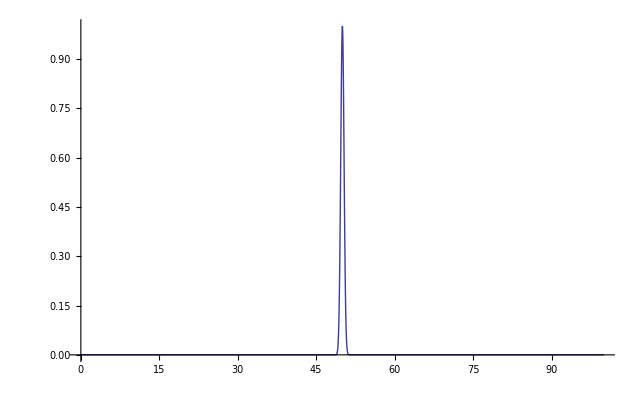

```mathematica
scale = 10;
μ =5 *scale;
σ =1/Sqrt[scale];
Plot[ⅇ^(-(x-μ)^2/(2 σ^2)),{x,0,10 scale},PlotRange->{Automatic,{0,1}}]
```

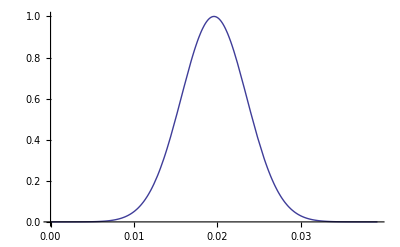

```mathematica
scale = 1/255;
μ =5 *scale;
σ =1 *scale;
Plot[ⅇ^(-(x-μ)^2/(2 σ^2)),{x,0,10 scale},PlotRange->{Automatic,{0,1}}]
```

## The relationship to the error Function

```mathematica
FullSimplify[Integrate[ PDF[NormalDistribution[μ,σ], t],{t,x0,x}]]
FullSimplify[Integrate[ A PDF[NormalDistribution[μ,σ],a t],{t,x0,x}]]
FullSimplify[Integrate[ A PDF[NormalDistribution[μ,σ] ,t],{t,sMin,sMax}]]
```

1/2 (Erf[(x-μ)/(√2 σ)]-Erf[(x0-μ)/(√2 σ)])

(A (-Erf[(-a x+μ)/(√2 σ)]+Erf[(-a x0+μ)/(√2 σ)]))/(2 a)

1/2 A (Erf[(sMax-μ)/(√2 σ)]-Erf[(sMin-μ)/(√2 σ)])

```mathematica
g[sMax_,sMin_, σ_]:= (sMax-sMin)/(Sqrt[2] σ)
```

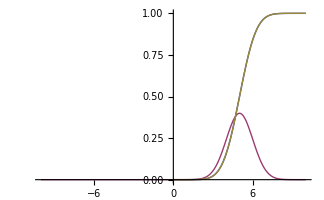

```mathematica
μ =5;
σ =1;
sMax = 10; sMin = 0;
g =  (sMax-sMin)/(Sqrt[2] σ) ;
c = μ;
dRange =N[ 1/2 (Erf[(μ - sMin)/(√2 σ)]+Erf[(sMax - μ)/(√2 σ)])];
dMin = 0;
dMax = dMin + dRange;
setUprErf[ g,c,sMin,sMax,dMin,dMax]
Plot[{1/2 (Erf[(x-μ)/(√2 σ)]+Erf[μ/(√2 σ)]),PDF[NormalDistribution[μ,σ],x], nErf[x]},{x,-10,10},PlotRange->{Automatic,{0,1}}]
```

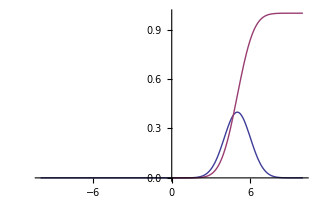

```mathematica
Plot[{PDF[NormalDistribution[μ,σ],x], nErf[x]},{x,-10,10},PlotRange->{Automatic,{0,1}}]
```

```mathematica
Clear[μ,σ, g,c, sMin, sMax, dMin, dMax];
Expand[Log[1/2 (Erf[(μ - sMin)/(√2 σ)]+Erf[(sMax - μ)/(√2 σ)])]]
```

Log[1/2 (Erf[(sMax-μ)/(√2 σ)]+Erf[(-sMin+μ)/(√2 σ)])]

```mathematica
dMax
```

```mathematica
g[σ
```

0.999999

```mathematica
nErf[h]
```

(255 Erf[3/85])/(Erf[3/85]+Erf[82/85])+(255 Erf[82/85])/(Erf[3/85]+Erf[82/85])

```mathematica
nErf[x] /.{Erf[(g (c-x))/(sMax-sMin)]->- Erf[(g (x-c))/(sMax-sMin)]}
%[[0]][%[[1]],Simplify[Together[%[[0]][%[[2]],%[[3]]]]]]
```

dMin+((dMax-dMin) Erf[(g (c-sMin))/(sMax-sMin)])/(Erf[(g (-c+sMax))/(sMax-sMin)]+Erf[(g (c-sMin))/(sMax-sMin)])+((dMax-dMin) Erf[(g (-c+x))/(sMax-sMin)])/(Erf[(g (-c+sMax))/(sMax-sMin)]+Erf[(g (c-sMin))/(sMax-sMin)])

dMin+((dMax-dMin) (Erf[(g (c-sMin))/(sMax-sMin)]+Erf[(g (-c+x))/(sMax-sMin)]))/(Erf[(g (-c+sMax))/(sMax-sMin)]+Erf[(g (c-sMin))/(sMax-sMin)])

```mathematica
FullSimplify[nErf[x] /.{Erf[(g (c-x))/(sMax-sMin)]->- Erf[(g (x-c))/(sMax-sMin)]},TransformationFunctions->{Automatic}]
```

(dMin (Erf[(g (-c+sMax))/(sMax-sMin)]+Erf[(g (c-x))/(sMax-sMin)])+dMax (Erf[(g (c-sMin))/(sMax-sMin)]+Erf[(g (-c+x))/(sMax-sMin)]))/(Erf[(g (-c+sMax))/(sMax-sMin)]+Erf[(g (c-sMin))/(sMax-sMin)])

```mathematica
setUprErf[ g,c,sMin,sMax,dMin,dMax]
nErf[x] /.{Erf[(g (c-x))/(sMax-sMin)]->- Erf[(g (x-c))/(sMax-sMin)]};
%[[0]][%[[1]],Simplify[Together[%[[0]][%[[2]],%[[3]]]]]]
```

dMin+((dMax-dMin) (Erf[(g (c-sMin))/(sMax-sMin)]+Erf[(g (-c+x))/(sMax-sMin)]))/(Erf[(g (-c+sMax))/(sMax-sMin)]+Erf[(g (c-sMin))/(sMax-sMin)])

```mathematica
FullSimplify[Integrate[PDF[NormalDistribution[0,1],t],{t,0,x}]]
```

1/2 Erf[x/(√2)]

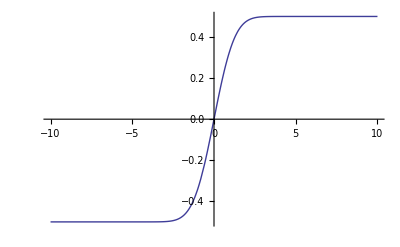

```mathematica
Plot[1/2 Erf[x/(√2)],{x,-10,10}]
```

```mathematica
mErf[x_, g_,c_]:=1/2 ( Erf[g (x -c)]+1)
InputForm[FullSimplify[(yMax-yMin)(mErf[x,g/(xMax-xMin),c]-mErf[xMin,g/(xMax-xMin),c])/(mErf[xMax,g/(xMax-xMin),c]-mErf[xMin,g/(xMax-xMin),c])+yMin, xMin <=c≤xMax]]
```

yMin + ((-yMax + yMin)*(Erf[(g*(-c + x))/(xMax - xMin)] + Erf[(g*(c - xMin))/(xMax - xMin)]))/(Erf[(g*(c - xMax))/(xMax - xMin)] + Erf[(g*(-c + xMin))/(xMax - xMin)])

```mathematica
aErf[x_, g_,c_,xMin_,xMax_,yMin_,yMax_,erf_:Function[{a,b},Erf[a,b]]]:=yMin+((yMax-yMin)*(Piecewise[{{erf[(g*(-c+x)),(xMax-xMin)],x≥c},{-erf[(g*(c-x)),(xMax-xMin)],x<c}}]+erf[(g*(c-xMin)),(xMax-xMin)]))/( erf[(g*(-c+xMax)),(xMax-xMin)]+erf[(g*(c-xMin)),(xMax-xMin)]);
```

```mathematica
aErf[x, g,c,xMin,xMax,yMin,yMax]
```

yMin+((yMax-yMin) (Erf[g (c-xMin),xMax-xMin]+(Piecewise[{{Erf[g (-c+x),xMax-xMin], x≥c}, {-Erf[g (c-x),xMax-xMin], x<c}, {0, True}}])))/(Erf[g (-c+xMax),xMax-xMin]+Erf[g (c-xMin),xMax-xMin])

```mathematica
Clear[setUprErf];
setUprErf[ g_,c_,sMin_,sMax_,dMin_,dMax_]:=Module[{aa5,aa4,aa3,aa2,aa1,ppD,ppN},
Clear[dRange,sRange, ErfA,ErfB, grad,con,ErfA,ErfB,iErf];
grad= g;
con = c;
dRange = dMax-dMin;
sRange = sMax-sMin;
ErfA = Erf[g (c-sMin)/sRange];
ErfB = Erf[g (-c+sMax)/sRange]+Erf[g (c-sMin)/sRange];
     shift=dRange*ErfA/ErfB + dMin;
     scale=dRange/ErfB;
iErf[x_]:=Evaluate[ Floor[N[shift]] +Floor[N[scale]]  Erf[((grad*(x-con))/sRange)]];
nErf[x_]:=Evaluate[ shift +scale  Erf[((grad*(x-con))/sRange)]];
]
```

```mathematica
Clear[g,c]
setUprErf[ g,c,sMin,sMax,dMin,dMax]
Together[iErf[x]]
Together[nErf[x]]
```

Erf[(g (-c+x))/(sMax-sMin)] Floor[(dMax-1. dMin)/(Erf[(g (-1. c+sMax))/(sMax-1. sMin)]+Erf[(g (c-1. sMin))/(sMax-1. sMin)])]+Floor[dMin+((dMax-1. dMin) Erf[(g (c-1. sMin))/(sMax-1. sMin)])/(Erf[(g (-1. c+sMax))/(sMax-1. sMin)]+Erf[(g (c-1. sMin))/(sMax-1. sMin)])]

(dMin Erf[(g (-c+sMax))/(sMax-sMin)]+dMax Erf[(g (c-sMin))/(sMax-sMin)]+dMax Erf[(g (-c+x))/(sMax-sMin)]-dMin Erf[(g (-c+x))/(sMax-sMin)])/(Erf[(g (-c+sMax))/(sMax-sMin)]+Erf[(g (c-sMin))/(sMax-sMin)])

```mathematica
setUprErf[ 1.4138,188,0,255,0,255]
TableForm[{{"ErfA", "ErfB", "shift", "scale"},{ErfA, ErfB, shift, scale},{N[ErfA], N[ErfB], N[shift],N[ scale]}}]
iErf[a]
N[iErf[128]]
```

ErfA | ErfB | shift | scale
0.85954 | 1.26019 | 173.928 | 202.35
0.85954 | 1.26019 | 173.928 | 202.35

173+202 Erf[0.00554431 (-188+a)]

99.8827

```mathematica
Manipulate[
DiscretePlot[{Evaluate[setUprErf[ g,c,sMin,sMax,dMin,dMax]];Floor[iErf[x]]},{x,sMin,sMax},PlotStyle->{Blue},AxesLabel->TraditionalForm/@{a,iErf[a]},PlotRange->{{sMin,sMax},{dMin, dMax}},Filling->Bottom,
Epilog->{Red,Dashing[{.02,.02}],Line[{{sMin,dMax},{sMax,dMax}}], Line[{{sMin,dMin},{sMax,dMin}}]}],
{{dMin,0},-255,255,1,ValueThumbSlider[##]&},{{dMax,255},1,255,1,ValueThumbSlider[##]&},{sMin,0,sMax,1,ValueThumbSlider[##]&},{{sMax,255},1,255,1,ValueThumbSlider[##]&},{{c,188},sMin,sMax,1,ValueThumbSlider[##]&},{{g,1.4138},1,10,ValueThumbSlider[##]&}
]
```

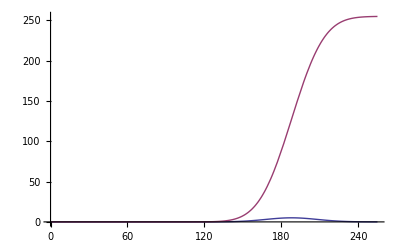

```mathematica
μ =188;
σ =20.1188;
sMax = 255; sMin = 0;
g =  (sMax-sMin)/(Sqrt[2] σ) ;
c = μ;
dRange =255; dMin = 0; dMax = dMin + dRange;
setUprErf[ g,c,sMin,sMax,dMin,dMax]
Plot[{dRange PDF[NormalDistribution[μ,σ],x], nErf[x]},{x,sMin,sMax},PlotRange->{{sMin,sMax},{dMin,dMax}}]
```

.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00v.030".00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00êlaw.00.00.00.000ë@@.01.00.00.00.90éB.00.00.00.00.00.00.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.1f.8e ýþ.07.00.00.9e
.04.00.00.00.00.00.00.b2Ò	.00.00.00.00p:ß.10.00.00.00.00.aaÒ+w.00.00.00.00.0e.00.00.00.01.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.90éB.00.00.00.00.00.9e
.04.00.00.00.00.00À¸.86@.01.00.00.00.00.b2Ò	.00.00.00.00 .8aC.11.00.00.00.00`sB.00.00.00.00.00.90éB.00.00.00.00.00.9e
.04.00.00.00.00.00À¸.86@.01.00.00.00.00.b2Ò	.00.00.00.00 .8aC.11.00.00.00.00.1f.8e ýþ.07.00.00.90éB.00.00.00.00.00.9e
.04.00.00.00.00.00À¸.86@.01.00.00.00.00.b2Ò	.00.00.00.00.0e.00.00.00.00.00.00.00`sB.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.1dj.11.00.00.00.00	.00.00.00.00.00.00.00ç+_@.01.00.00.00.00.00.00.00.00.00.00.00ÉÜ_@.01.00.00.00.00.00.00.00.00.00.00.00	.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00`sB.00.00.00.00.00.00.00.00.00.00.00.00.00.08Þ_@.01.00.00.00.90éB.00.00.00.00.00.9e
.04.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00 Ú .11.00.00.00.00.00.00.00.00.00.00.00.00à°Ò	.00.00.00.00
0.19w.00.00.00.00.00.00.00.00.00.00.00.00°í .11.00.00.00.00	.00.00.00.00.00.00.00ç+_@.01.00.00.00Ð=.b9	.00.00.00.00<ß^@.01.00.00.00À¸.86@.01.00.00.00 ©Ô	.00.00.00.00°í .11.00.00.00.00.00.00.00.00.00.00.00.00°í .11.00.00.00.00%Ö@@.01.00.00.00°í .11.00.00.00.00°í .11.00.00.00.00à°Ò	.00.00.00.00.01.00.00.00.00.00.00.00.01sB.00.00.00.00.00.00.0cA@.01.00.00.00.01tB.00.00.00.00.00 Ú .11.00.00.00.00.00.00.00.00.00.00.00.00 Ú .11.00.00.00.00°í .11.00.00.00.00Ú.0c.1a@.01.00.00.00.98éB.00.00.00.00.00à°Ò	.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00x.1a>þþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.18[ý.0f.00.00.00.00.98éB.00.00.00.00.00.90éB.00.00.00.00.00.02.00.00.00.00.00.00.006tB.00.00.00.00.00ÂB.18w.00.00.00.00Ô.94V.9c.12].00.00n/©ûþ.07.00.00.18[ý.0f.00.00.00.00.02D.aaûþ.07.00.00XtB.00.00.00.00.00HwB.00.00.00.00.00.00.00.00.00.00.00.00.003Q.w.00.00.00.00.00.00.00.00.00.00.00.004.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00÷A.18w.00.00.00.004.00.00À.00.00.00.00.00.00.00.00þ.07.00.00.00.00.00.00.00.00.00.00.04.00.00.00.00.00.00.00.84tB.00.00.00.00.00¨tB.00.00.00.00.00xxB.00.00.00.00.00`wB.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.004.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ÿÿÿÿ.00.00.00.00.00.00.00.00.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.000.00.00.00þ.07.00.004.00.00.00.00.00.00.00°wB.00.00.00.00.00@.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00Ø.00Ø.00.00.00.00.00pëL.0b.00.00.00.00.00.b2.00.00.00.00.00.00.00.00.00.00þ.07.00.000.00.00.00þ.07.00.004.00.00.00.00.00.00.00@ \.00.00.00.00.00@.00.00.00.00.00.00.008¢\.00.00.00.00.00.90.07`.00.00.00.00.00.00.00.00.00.00.00.00.00@ëL.0b.00.00.00.000yB.00.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.000.00.00.00.00.00.00.00.00.00\.00.00.00.00.00.0f.00.00.00.00.00.00.00 .00.00.00.00.00.00.00¨.02\.00.00.00.00.00.8eY.w.00.00.00.00	.00.00.00.0b.02.00.00 .00.00.00.00.00.00.00.12.00Ç.01÷.00.00.00à.05`.00.00.00.00.00{.000.00E.005.00ð.a6.0c.10.00.00.00.00ð.a6.0c.10.00.00.00.00àvB.00.00.00.00.00.00.00.00.00.00.00.00.00!.1dçóþ.07.00.00.00.00.00.00.00.00.00.00D.00E.004.000.000.002.007.004.00E.00}.00.00.00.00.00ð.a6.0c.10.00.00.00.00é.1cçóþ.07.00.00.00.00.00.00.00.00.00.00Ê.1d ýþ.07.00.00'.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ÀwB.00.00.00.00.00.00.00.00.00.00.00.00.00'.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00{®.1b@.01.00.00.00.18[ý.0f.00.00.00.00.98)Hþþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.0f.00.00.00.00.00.00.00.0f.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00{®.1b@.01.00.00.00.02.00.00.00.00.00.00.00`yB.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00pëL.0b.00.00.00.00þÿÿÿÿÿÿÿ.01.00.00.00.00.00.00.00@ \.00.00.00.00.00.01.00.00.00.00.00.00.008¢\.00.00.00.00.00þÿÿÿÿÿÿÿ{R.18w.00.00.00.00.00.00.00.00.00.00.00.00ÿÿÿÿÿÿÿÿ.0f.00.00.00.00.00.00.00.98Üh.00.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.000.00.00.00.00.00.00.00.00.00\.00.00.00.00.00.90ëL.0b.00.00.00.00 .00.00.00.00.00.00.00¨.02\.00.00.00.00.00.8eY.w.00.00.00.00	.00.00.00.00.00.00.00 .00.00.00.00.00.00.00.11.00Ê.01÷.00.00.00à.05`.00.00.00.00.00ÀæÑ.04.00.00.00.00.00.00.00.00.00.00.00.00.10}B.00.00.00.00.00.00.00.00.00.00.00.00.00.00!@þ.00.00.04.00.00@.00 .00.00.00.00.18[ý.0f.00.00.00.00.00.00.00.00.00.00.00.00.90æÑ.04.00.00.00.00`yB.00.00.00.00.00þÿÿÿÿÿÿÿF.00}.00.00.00.00.00`xB.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.9d.07Kýþ.07.00.00.00.00.00.00.00.00.00.00Ý.8c.02þþ.07.00.00Ð.05Oýþ.07.00.003Q.w.00.00.00.00`xB.00.00.00.00.00{®.1b@.01.00.00.00.00æÑ.04.00.00.00.00 zB.00.00.00.00.00.10.00.00.00.00.00.00.00.00@.00 .00.00.00.00.90ëL.0b.00.00.00.00pëL.0b.00.00.00.00.00@.00 .00.00.00.00
:.02þþ.07.00.00.00æÑ.04.00.00.00.00 zB.00.00.00.00.00þÿÿÿÿÿÿÿ.00@.00 .00.00.00.00.00.00.00.00.00.00.00.00.98)Hþþ.07.00.00.00@.00 .00.00.00.00qJ.04þþ.07.00.00.18[ý.0f.00.00.00.00pëL.0b.00.00.00.00.00.00.00.00.00.00.00.00.98)Hþþ.07.00.00.00.00.00.00.00.00.00.00.baM.04þþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00 ëL.0b.00.00.00.00.8f.0f.00ÀO×Ðb`yB.00.00.00.00.00ØYý.0f.00.00.00.00.00.00.00.005.00C.00`.04ó.10.00.00.00.00.01.00.00.00.00.00.00.00ÐyB.00.00.00.00.00à7¶.02.00.00.00.00,.af.1b@.01.00.00.00à7¶.02.00.00.00.00.01.00.00.00.00.00.00.00.08à.93@.01.00.00.00ÈµB.00.00.00.00.00.00T:w.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.02.00.00.00ÐyB.00.00.00.00.00Ø.8eB.00.00.00.00.00.02.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.884.w.00.00.00.00.00»#.04.00.00.00.00à7¶.02.00.00.00.00@.1eÌ.10.00.00.00.00 .0cÌ.10.00.00.00.00.00.00.00.00.00.00.00.00&L.04þþ.07.00.000zB.00.00.00.00.00.80.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00{®.1b@.01.00.00.00.05@.00.80.00.00.00.00pYý.0f.00.00.00.00`{B.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00qJ.04þþ.07.00.00pYý.0f.00.00.00.00 ëL.0b.00.00.00.00`{B.00.00.00.00.00h.1bhûþ.07.00.00þÿÿÿÿÿÿÿ .1ahûþ.07.00.00.08.13.8e.03.00.00.00.00.00.00\.00.00.00.00.00Ö.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.80{B.00.00.00.00.00_ hûþ.07.00.00.00.00.00.00.00.00.00.00.10g.8b.07.00.00.00.00hØx.03.00.00.00.00.80{B.00.00.00.00.00È
.05.00.00.00.00.00(.9bc.00.00.00.00.00È
.05.00.00.00.00.00.10.95r.06.00.00.00.00.01.00.00.00.00.00.00.00õk.08w.00.00.00.00.00.00.00.00.00.00.00.00`.04ó.10.00.00.00.00.01.00.00.00.00.00.00.00.90{B.00.00.00.00.00à7¶.02.00.00.00.00,.af.1b@.01.00.00.00à7¶.02.00.00.00.00.01.00.00.00.00.00.00.00.08à.93@.01.00.00.00.88·B.00.00.00.00.00.00.0e.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00Øx.03.02.00.00.00.90{B.00.00.00.00.00.00.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00.00»#.04.00.00.00.00à7¶.02.00.00.00.00@.1eÌ.10.00.00.00.00 .0cÌ.10.00.00.00.00!.03.0f.00.00.00.00.00KÆ.90ûþ.07.00.00.00.00.00.00.00.00.00.00.01i.86ûþ.07.00.00°°þ.0f.00.00.00.00È
.05.00.00.00.00.00ÿÿÿ.7f.00.00.00.003$.02þþ.07.00.00.00.00.00.00.00.00.00.00{®.1b@.01.00.00.00±.00.00.00.00.00.00.00.01.00.00.00.00.00.00.008Ñi.06.00.00.00.00È
.05.00.00.00.00.00.04.00.00.00.00.00.00.00.80.94B.00.00.00.00.00.90.16u.06.00.00.00.00.86¨.9c.12].00.00±.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.01.00.00.00.00.00.00.00.90g.86ûþ.07.00.00.05.00.00.00.00.00.00.00È
.05.00.00.00.00.00!.03.0f.00.00.00.00.00.00.00.00.00.00.00.00.00°°þ.0f.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.008.a6.8eûþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00H.00.00.00.00.00.00.00.01.00.00.00þ.07.00.00 µB.00.00.00.00.00(.9bc.00.00.00.00.00p.00.00.00.00.00.00.00ßJ.bdÿÿÿÿÿÍ.81¨.9c.12].00.00C.9b.08w.00.00.00.00ï.9b.08w.00.00.00.00È
.05.00.00.00.00.00(.9bc.00.00.00.00.00.05.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.05.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00\.97.8eûþ.07.00.00ï.9b.08w.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.80.92'.0b.00.00.00.00x;.08w.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.80.00.00.00.00.00.00H.00.00.00.00.00.00.00.01.00.00.00þ.07.00.00 µB.00.00.00.00.00(.9bc.00.00.00.00.00p.00.00.00.00.00.00.00ßJ.bdÿÿÿÿÿ×d.9cÿÿÿÿÿC.9b.08w.00.00.00.00ï.9b.08w.00.00.00.00_ hûþ.07.00.00È
.05.00.00.00.00.00.05.00.00.00.00.00.00.00.05.00.00.00.00.00.00.00ü;.08w.00.00.00.00È
.05.00.00.00.00.00{®.1b@.01.00.00.00.05.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00!.03.0f.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00{®.1b@.01.00.00.00.80.94B.00.00.00.00.00!.03.0f.00.00.00.00.00þÿÿÿÿÿÿÿ(.9bc.00.00.00.00.00!.03.0f.00.00.00.00.00.00.00.00.00ÿÿÿÿ×d.9cÿÿÿÿÿ.15b.86ûþ.07.00.00ï.9b.08w.00.00.00.00.01.00.00.00.00.00.00.00þÿÿÿÿÿÿÿxÐUõþ.07.00.00!.03.0f.00.00.00.00.00¨j.08w.00.00.00.00À.1aÅ.00.00.00.00.00äi.86ûþ.07.00.00qþÿÿ.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00`.04ó.10.00.00.00.00.01.00.00.00.00.00.00.00.90.7fB.00.00.00.00.00à7¶.02.00.00.00.00,.af.1b@.01.00.00.00à7¶.02.00.00.00.00.01.00.00.00.00.00.00.00.08à.93@.01.00.00.00`.04ó.10.00.00.00.00.01.00.00.00.00.00.00.00Ð.7fB.00.00.00.00.00à7¶.02.00.00.00.00,.af.1b@.01.00.00.00à7¶.02.00.00.00.00.01.00.00.00.00.00.00.00.08à.93@.01.00.00.00È»B.00.00.00.00.00.00»#.04.00.00.00.00à7¶.02.00.00.00.00.00.1eÌ.10.02.00.00.00Ð.7fB.00.00.00.00.00.00.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ°°þ.0f.00.00.00.00.00»#.04.00.00.00.00à7¶.02.00.00.00.00@.1eÌ.10.00.00.00.00 .0cÌ.10.00.00.00.00.80.94B.00.00.00.00.00!.03.0f.00.00.00.00.00.05.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00`.0f.0e.10.00.00.00.00.01.00.00.00.00.00.00.00.80.94B.00.00.00.00.00.00.00.00.00.00.00.00.00.8d.82¨.9c.12].00.00ï.9b.08w.00.00.00.00.00.00.00.00.00.00.00.00.90.16u.06.00.00.00.00È
.05.00.00.00.00.00.00.00.00.00.00.00.00.00hg.86ûþ.07.00.00.00.00.00.00.00.00.00.00È
.05.00.00.00.00.00\.97.8eûþ.07.00.00ï.9b.08w.00.00.00.00!.03.0f.00.00.00.00.00.01.00.00.00.00.00.00.00!.03.0f.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00j.0b.04þþ.07.00.00!.03.0f.00.00.00.00.00È
.05.00.00.00.00.00.05.00.00.00.00.00.00.00.90L].11.00.00.00.00.01.00.00.00.00.00.00.00`.81B.00.00.00.00.00`,Ì.10.00.00.00.00,.af.1b@.01.00.00.00`,Ì.10.00.00.00.00.01.00.00.00ÿÿÿÿ.08à.93@.01.00.00.00¸.b4B.00.00.00.00.00.00.00.00.00.00.00.00.00.1aa.0bþþ.07.00.00.00.94B.00.02.00.00.00`.81B.00.00.00.00.00.05.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00þÿÿÿÿÿÿÿäi.86ûþ.07.00.00ð.141.04.00.00.00.00`,Ì.10.00.00.00.00.00.00.00.00.00.00.00.00Û.02.0f.00.00.00.00.00.00.00.00.00.00.00.00.00 {ö.0f.00.00.00.00.01.00.00.00.00.00.00.00.80.94B.00.00.00.00.00þÿÿÿÿÿÿÿ.1d|¨.9c.12].00.00s.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.90.16u.06.00.00.00.00È
.05.00.00.00.00.00ÐyB.00.00.00.00.00hg.86ûþ.07.00.00.00.00.00.00.00.00.00.00°±ò.10.00.00.00.00.02.00.00.00.00.00.00.00p.82B.00.00.00.00.00`.04ó.10.00.00.00.00{®.1b@.01.00.00.00`.04ó.10.00.00.00.00.01.00.00.00.00.00.00.00.08à.93@.01.00.00.00{®.1b@.01.00.00.00.00.03.0f.00.00.00.00.00È
.05.00.00.00.00.00.00.00.00.00.03.00.00.00p.82B.00.00.00.00.00.10.95r.06.00.00.00.00.03.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00@î/.04.00.00.00.00p©ò.10.00.00.00.00þÿÿÿÿÿÿÿYæ.1b@.01.00.00.00'.00.00.00.01.00.00.00.90L].11.00.00.00.00.01.00.00.00.00.00.00.00 .83B.00.00.00.00.00`,Ì.10.00.00.00.00,.af.1b@.01.00.00.00`,Ì.10.00.00.00.00.01.00.00.00.00.00.00.00.08à.93@.01.00.00.00x¶B.00.00.00.00.00.00ÿÿÿÿÿÿÿ K|.00.00.00.00.00.00.00.00.00.02.00.00.00 .83B.00.00.00.00.00È
.05.00.00.00.00.00.02.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00ð.141.04.00.00.00.00`,Ì.10.00.00.00.00À.97B.00.00.00.00.00Û.02.0f.00.00.00.00.00.05.00.00.00.00.00.00.00{®.1b@.01.00.00.00.00.00.00.00.00.00.00.00`.0f.0e.10.00.00.00.00.01.00.00.00.00.00.00.00À.97B.00.00.00.00.00.00.00.00.00.00.00.00.00M~¨.9c.12].00.00L.0b.00.00.00.00.00.00{®.1b@.01.00.00.00.90{B.00.00.00.00.00È
.05.00.00.00.00.00þÿÿÿÿÿÿÿ°±ò.10.00.00.00.00.02.00.00.00.00.00.00.000.84B.00.00.00.00.00`.04ó.10.00.00.00.00{®.1b@.01.00.00.00`.04ó.10.00.00.00.00{®.1b@.01.00.00.00þÿÿÿÿÿÿÿYæ.1b@.01.00.00.00.00.00.00.00.00.00.00.00j.0b.04þþ.07.00.00.00.02.0f.00.03.00.00.00Yæ.1b@.01.00.00.00.05.00.00.00.00.00.00.00.03.00.00.00.00.00.00.00þÿÿÿÿÿÿÿÅa.0bþþ.07.00.00þÿÿÿÿÿÿÿp©ò.10.00.00.00.00þÿÿÿÿÿÿÿYæ.1b@.01.00.00.00.05.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00Yæ.1b@.01.00.00.00.00.00.00.00.00.00(À`.04ó.10.00.00.00.00þÿÿÿÿÿÿÿ.00.85B.00.00.00.00.00à7¶.02.00.00.00.00,.af.1b@.01.00.00.00þÿÿÿÿÿÿÿ.01.00.00.00.00.00.00.00.08à.93@.01.00.00.00øÀB.00.00.00.00.00.00.00.00.00.00.00.00.00 {ö.0f.00.00.00.00.00.00.00.00.02.00.00.00.00.85B.00.00.00.00.00.00.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00.00»#.04.00.00.00.00à7¶.02.00.00.00.00@.1eÌ.10.00.00.00.00{®.1b@.01.00.00.00.00.00.00.00.00.00.00.00Zø0@.01.00.00.00.00.00.00.00.00.00à?GýN@.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.80.00.00.00.00.00.00.00.00.80.0b¿.10.00.00.00.00Ëp1@.01.00.00.00þÿÿÿÿÿÿÿ.00D.87@.01.00.00.00.00D.87@.01.00.00.00Ð÷.be.10.00.00.00.00.00D.87@.01.00.00.00.80.0b¿.10.00.00.00.00.00.00.00.00.08.00.00.00Yæ.1b@.01.00.00.00.00D.87@.01.00.00.00xtð.05.00.00.00.00.08.00.00.00.00.004@Yæ.1b@.01.00.00.00.08.00.00.00.00.00.00.00.00D.87@.01.00.00.00þÿÿÿÿÿÿÿ`¶".06.00.00.00.00.01.00.00.00.00.00.00.00PÃ.b3.10.00.00.00.00þÿÿÿÿÿÿÿ`¶".06.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00333333)@.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.80.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00 ÎÄ	.00.00.00.00îB?@.01.00.00.00.00.00.00.00.00.00.00@.00.00.00.00.00.00.00.00.00.00.00.00.00ð.80@Zø0@.01.00.00.00°s|.08.00.00.00.00Þ.1d
@.01.00.00.00.10.0c¿.10.00.00.00.00.90L].11.00.00.00.00.01.00.00.00.00.00.00.00 .87B.00.00.00.00.00`,Ì.10.00.00.00.00,.af.1b@.01.00.00.00`,Ì.10.00.00.00.00.01.00.00.00.01.00.00.00.08à.93@.01.00.00.00.90L].11.00.00.00.00.01.00.00.00.00.00.00.00`.87B.00.00.00.00.00`,Ì.10.00.00.00.00,.af.1b@.01.00.00.00`,Ì.10.00.00.00.00.01.00.00.00.00.00.00.00.08à.93@.01.00.00.00¸.baB.00.00.00.00.00.00.141.04.00.00.00.00`,Ì.10.00.00.00.00.00ÿÿÿ.02.00.00.00`.87B.00.00.00.00.00þÿÿÿÿÿÿÿ.02.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00ð.141.04.00.00.00.00`,Ì.10.00.00.00.00.07.00.00.0033)@ú	.04.00.00.00.00.00p.baÒ	.00.00.00.00.90Æ.b3.10.00.00.00.00.90.7fB.00.00.00.00.00.00.00.00.00.00.00.00.000.17é.05.00.00.00.00°±ò.10.00.00.00.00.02.00.00.00.00.00.00.000.88B.00.00.00.00.00`.04ó.10.00.00.00.00{®.1b@.01.00.00.00Ð.7fB.00.00.00.00.00.01.00.00.00.00.00.00.00.08à.93@.01.00.00.00{®.1b@.01.00.00.00.02.00.00.00.00.00.00.00p.88B.00.00.00.00.00`.04ó.10.00.00.00.00{®.1b@.01.00.00.00`.04ó.10.00.00.00.00.01.00.00.00.00.00.00.00.08à.93@.01.00.00.00È»B.00.00.00.00.00.00î/.04.00.00.00.00p©ò.10.00.00.00.00þÿÿÿÿÿÿÿp.88B.00.00.00.00.00ø®.87@.01.00.00.00.03.00.00.00.00.00.00.00þÿÿÿÿÿÿÿYæ.1b@.01.00.00.00@î/.04.00.00.00.00p©ò.10.00.00.00.00`.04ó.10.00.00.00.00Yæ.1b@.01.00.00.00@.00.00.00.00.00.00.00|.9c?@.01.00.00.00þÿÿÿÿÿÿÿ{®.1b@.01.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ{®.1b@.01.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00.00.00.00.00.00.00ð?.00.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.80.00.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ0tð.05.00.00.00.00.10.0c¿.10.00.00.00.00ÿÿÿ.7f.00.00.00.00.00.00.00.00.00.00.00.00Æ{1@.01.00.00.00`.81B.00.00.00.00.00V.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00ðL].11.00.00.00.00.01.00.00.00.00.00.00.00.00.8aB.00.00.00.00.00.90L].11.00.00.00.00{®.1b@.01.00.00.00.90L].11.00.00.00.00.01.00.00.00.01.00.00.00.08à.93@.01.00.00.00¸.b4B.00.00.00.00.00.00.00.00.00.00.00.10@`.04ó.10.00.00.00.00.00.00.00.00.02.00.00.00.00.8aB.00.00.00.00.00à7¶.02.00.00.00.00.02.00.00.00.00.00.00.00.00.0cI.01.00.00.00.00.a6.9a.08w.00.00.00.00.8a
 .00.00.00.00.00ü·B.00.00.00.00.00 .00.00.00.00.00.00.00O%_@.01.00.00.00.00.0cI.01.00.00.00.00.02.b4.0ew.00.00.00.00à.1d.ba.00.00.00.00.00ü·B.00.00.00.00.00 .00.00.00.00.00.00.00O%_@.01.00.00.00.00.0cI.01.00.00.00.00.a6.9a.08w.00.00.00.00.00.00.00.00.00.00.00.00ü·B.00.00.00.00.00.01L].11.00.00.00.00{®.1b@.01.00.00.00.00.0cI.01.00.00.00.00â7.08w.00.00.00.00.00.00.00.00.00.00.00.00.01L].11.00.00.00.00.0c2¨.9c.12].00.00Àóù.05.00.00.00.00.01.00.00.00.00.00.00.000.8bB.00.00.00.00.00@?¶.02.00.00.00.00{®.1b@.01.00.00.00þÿÿÿÿÿÿÿ{®.1b@.01.00.00.00.08à.93@.01.00.00.00èµB.00.00.00.00.00.00.00.00.00.00.00.00.00{®.1b@.01.00.00.00.00·B.00.02.00.00.000.8bB.00.00.00.00.00ð.141.04.00.00.00.00.02.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ{®.1b@.01.00.00.00þÿÿÿÿÿÿÿ@?¶.02.00.00.00.00.01.00.00.00.00.00.00.00À.8bB.00.00.00.00.00þÿÿÿÿÿÿÿ{®.1b@.01.00.00.00.90L].11.00.00.00.00.01.00.00.00.01.00.00.00.08à.93@.01.00.00.00x¶B.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00.00.00.00.00.02.00.00.00À.8bB.00.00.00.00.00.00.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00.00.0cI.01.00.00.00.00.a6.9a.08w.00.00.00.00.8a
 .00.00.00.00.00`.04ó.10.00.00.00.00.01.00.00.00.00.00.00.00P.8cB.00.00.00.00.00à7¶.02.00.00.00.00{®.1b@.01.00.00.00à7¶.02.00.00.00.00.01.00.00.00.00.00.00.00.08à.93@.01.00.00.00{®.1b@.01.00.00.00.00.0cI.01.00.00.00.00.a6.9a.08w.00.00.00.00.00.00.00.00.02.00.00.00P.8cB.00.00.00.00.00.01L].11.00.00.00.00.02.00.00.00.00.00.00.00þÿÿÿÿÿÿÿâ7.08w.00.00.00.00.00»#.04.00.00.00.00`.04ó.10.00.00.00.00þÿÿÿÿÿÿÿà.8cB.00.00.00.00.00à7¶.02.00.00.00.00{®.1b@.01.00.00.00à7¶.02.00.00.00.00.01.00.00.00.00.00.00.00.08à.93@.01.00.00.00ØÈB.00.00.00.00.00.00.00.00.00.00.00.00.00+V.1c@.01.00.00.00.00.00.00.00.02.00.00.00à.8cB.00.00.00.00.00.80.b9B.00.00.00.00.00.02.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.98ê.1b@.01.00.00.00.00»#.04.00.00.00.00à7¶.02.00.00.00.00@.1eÌ.10.00.00.00.00 .0cÌ.10.00.00.00.00.00.00.00.00ÿÿÿÿ.90L].11.00.00.00.00.80.b9B.00.00.00.00.00.01.00.00.00.00.00.00.00.90L].11.00.00.00.00P.04.1d@.01.00.00.00.80.b9B.00.00.00.00.00{®.1b@.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.@.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00{®.1b@.01.00.00.00.00.00.00.00.00.00.00.00{®.1b@.01.00.00.00.80.b9B.00.00.00.00.00.80.b9B.00.00.00.00.00þÿÿÿÿÿÿÿÀóù.05.00.00.00.00.01.00.00.00.00.00.00.00 .8eB.00.00.00.00.00@?¶.02.00.00.00.00{®.1b@.01.00.00.00þÿÿÿÿÿÿÿ.01.00.00.00.01.00.00.00.08à.93@.01.00.00.00Ø¸B.00.00.00.00.00.00ÿÿÿÿÿÿÿ.bc.b9B.00.00.00.00.00.00.00.00.00.02.00.00.00{®.1b@.01.00.00.00þÿÿÿÿÿÿÿ.02.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.00O].11.00.00.00.00 =¶.02.00.00.00.00@?¶.02.00.00.00.00 ®/.04.00.00.00.00.01.00.00.00.00.00.00.00.80.b9B.00.00.00.00.00.90L].11.00.00.00.00þÿÿÿÿÿÿÿ1è.1b@.01.00.00.00.00.00.00.00.00.00.00.00.90L].11.00.00.00.00ðL].11.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00 .8eB.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00 =¶.02.00.00.00.00.90L].11.00.00.00.00þÿÿÿÿÿÿÿ.80.b9B.00.00.00.00.00 =¶.02.00.00.00.00.90L].11.00.00.00.00PÜ.10.00.00.00.00.bc.b9B.00.00.00.00.00ÐÌ^.11.00.00.00.00.04.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.bc.b9B.00.00.00.00.00.05.00.00.00.01.00.00.00{®.1b@.01.00.00.00þÿÿÿÿÿÿÿ.bc.b9B.00.00.00.00.00.05.00.00.00.00.00.00.00Vg1@.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.80.b9B.00.00.00.00.00.00O].11.00.00.00.00þÿÿÿÿÿÿÿ1è.1b@.01.00.00.00.00.00.00.00.00.00.00.00.00O].11.00.00.00.00`O].11.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00°.8fB.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00 =¶.02.00.00.00.00.00O].11.00.00.00.00þÿÿÿÿÿÿÿð.8fB.00.00.00.00.00 =¶.02.00.00.00.00.00O].11.00.00.00.00þÿÿÿÿÿÿÿ.02.00.00.00.00.00.00.00.00.0cI.01.00.00.00.00.a6.9a.08w.00.00.00.00.8a
 .00.00.00.00.00ü.bdB.00.00.00.00.00 .00.00.00.00.00.00.00O%_@.01.00.00.00.00.0cI.01.00.00.00.00{®.1b@.01.00.00.00à.1d.ba.00.00.00.00.00ü.bdB.00.00.00.00.00 .00.00.00.00.00.00.00O%_@.01.00.00.00.00.0cI.01.00.00.00.00.a6.9a.08w.00.00.00.00.00.00.00.00.00.00.00.00{®.1b@.01.00.00.00.01.00.00.00.00.00.00.00ð.90B.00.00.00.00.00þÿÿÿÿÿÿÿ{®.1b@.01.00.00.00@?¶.02.00.00.00.00.01.00.00.00.00.00.00.00.08à.93@.01.00.00.00¨»B.00.00.00.00.00.00
 .00.00.00.00.00¡ 4@.01.00.00.00þÿÿÿÿÿÿÿ{®.1b@.01.00.00.00ü(¨.9c.12].00.00.02.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ+V.1c@.01.00.00.00 =¶.02.00.00.00.00@?¶.02.00.00.00.00À.bdB.00.00.00.00.00.90L].11.00.00.00.00ð.141.04.00.00.00.00.98ê.1b@.01.00.00.00þÿÿÿÿÿÿÿ.90L].11.00.00.00.00.01.00.00.00.00.00.00.00°.91B.00.00.00.00.00`,Ì.10.00.00.00.00,.af.1b@.01.00.00.00`,Ì.10.00.00.00.00.90L].11.00.00.00.00.01.00.00.00.00.00.00.00à.91B.00.00.00.00.00`,Ì.10.00.00.00.00,.af.1b@.01.00.00.00`,Ì.10.00.00.00.00.01.00.00.00.00.00.00.00.08à.93@.01.00.00.008ÅB.00.00.00.00.00.00ÿÿÿÿÿÿÿ.00.00©.02.00.00.00.00.00.141.04.02.00.00.00à.91B.00.00.00.00.00.00.00.00.00.00.00.00.00{®.1b@.01.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00ð.141.04.00.00.00.00`,Ì.10.00.00.00.00.00.00.00.00.00.00.00.00{®.1b@.01.00.00.00(Ú}@.01.00.00.00{®.1b@.01.00.00.00.bc)¨.9c.12].00.00.80Á1.04.00.00.00.00þÿÿÿÿÿÿÿj.00.00.00.00.00.00.00.01¿B.00.00.00.00.00.00Ç.1c.11.00.00.00.00p=1.04.00.00.00.00.01.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ
0.19w.00.00.00.00þÿÿÿÿÿÿÿ.00.1dj.11.00.00.00.00.00.00.00.00.00.00.00.00.86(K@.01.00.00.00À.bdB.00.00.00.00.00üfSÿþ.07.00.00.90.99B.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00ñÔÔþþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00È=Sÿþ.07.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.90.99B.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.08à.93@.01.00.00.008.beB.00.00.00.00.00.00.00.00.00.00.00.00.00OJ.00.009.02.00.0f.90.99B.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.9e.1açýþ.07.00.00.01.00.00.00.00.00.00.00ðo¨.9c.12].00.00@?¶.02.00.00.00.00.00.00.00.00.00.00.00.00.90.99B.00.00.00.00.00.01.00.00.00.00.00.00.00ÿÿÿÿ.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00.00.10.00.00.00.00.00.00å"çýþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.90.99B.00.00.00.00.00.01.00.00.00.02.00.00.00.00.00.00.00.00.00.00.00.90.95B.00.00.00.00.00x6Sÿþ.07.00.00.80.99B.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00ñÔÔþþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.90.99B.00.00.00.00.00.97.18çýþ.07.00.00¸.1d.01I.00.00.00.00{®.1b@.01.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.90.99B.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ÿÿÿÿ.00.00.00.00x6Sÿþ.07.00.00þÿÿÿÿÿÿÿ.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00ñÔÔþþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00È=Sÿþ.07.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00`.9aB.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.9bB.00.00.00.00.00.03.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00NJ.00.00i.00.00F`.9aB.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.9e.1açýþ.07.00.00.01.00.00.00.00.00.00.00@h¨.9c.12].00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00`.9aB.00.00.00.00.00.01.00.00.00.00.00.00.00ÿÿÿÿ.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00.00.10.00.00.00.00.00.00å"çýþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00`.9aB.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00p.9bB.00.00.00.00.00.03.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ÿÿÿÿ.00.00.00.00x6Sÿþ.07.00.00À.9dB.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00ñÔÔþþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00È=Sÿþ.07.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00À.9dB.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ÿÿÿÿ.00.00.00.00.0f.1f:@.01.00.00.00.00.00.00.00.00.00.00.00MJ.00.00=.02.00.14À.9dB.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.9e.1açýþ.07.00.00.01.00.00.00.00.00.00.00.00j¨.9c.12].00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00À.9dB.00.00.00.00.00.01.00.00.00.00.00.00.00ÿÿÿÿ.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00.00.10.00.00.00.00.00.00å"çýþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00À.9dB.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00].01.00.00.00.00.00.00¸.99B.00.00.00.00.00.02.00.00.00.00.00.00.00].01.00.00.00.00.00.00÷Â @.01.00.00.00.8c.00.00.00.00.00.00.00p.99B.00.00.00.00.00p.99B.00.00.00.00.00p.99B.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00À.9dB.00.00.00.00.00.97.18çýþ.07.00.00¸.1d.01I.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00À.9dB.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ÿÿÿÿ.00.00.00.00.01.00.00.00.01.00.00.00 .9eý.10.00.00.00.00v×Sÿþ.07.00.00].01.00.00.8c.00.00.00(/m@.01.00.00.00p.99B.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00À.9dB.00.00.00.00.00.01.00.00.00.00.90a@.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00F.15.14@.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00*.00.00.00.00£B.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00 v@.00.00.00.00.00.90a@.02.00.00.00.00.00.00.00WM?@.01.00.00.00.00.00.00.00.00.00.00.00Ð/%.11.00.00.00.00.00.00.00.00.00.10u@.00.00.00.00.00@a@.18.9aB.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.02.00.000.00.00.00.00.000.00.01.00.00.00.02.00.00.00.00.00.00.00ð.8a>.04.00.00.00.00ð.8a>.04.00.00.00.00.00.0cI.01.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00`p.01.11.00.00.00.00.90.81>.04.00.00.00.000.00B.00.00.00.00.00.03.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.10u@.00.00.00.00.00@a@.00.00.00.00.00@a@.06.00.00.00.00.00.00.00F.15.14@.01.00.00.00 .9eý.10.00.00.00.00Pç$.11.00.00.00.00 .9eý.10.00.00.00.00.06.00.00.00.00.00.00.00.00.00.00.00.00.10u@.00.00.00.00.00@a@.02.00.00.00.00.00.00.00WM?@.01.00.00.00.00.00.00.00.00.00.00.00Pç$.11.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00(.9bB.00.00.00.00.00.10.00.00.00.00.00.00.00`p.01.11.00.00.00.00».00:@.01.00.00.00.01.02.87.03f.00.00.00.00.00f.00.01.07.00.00.02.00.00.00.00.00.00.00.80.00.aa.02.00.00.00.00ð.8a>.04.00.00.00.00p.02.aa.02.00.00.00.00`p.01.11.00.00.00.00.03.00.00.00.00.00.00.00Àü.7f	.00.00.00.00.90.81>.04.00.00.00.00e.00r.00f.00.00.00.80.00.aa.02.00.00.00.00@p.01.11.00.00.00.00p.02.aa.02.00.00.00.000.00.aa.02.00.00.00.00.00.00©.02.00.00.00.00.02.00.00.00.00.00.00.00.80.00.aa.02.00.00.00.00.88.02©.02.00.00.00.00p.02.aa.02.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00©.02.00.00.00.00.02.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00.88.02©.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00þÿÿÿÿÿÿÿp.04.aa.02.00.00.00.00.88.02©.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.8a.00.00.00.02.00.00.00.00.00.00.00Ù.00".01o¿x4p.04.aa.02.00.00.00.00p.9cB.00.00.00.00.00°.9eB.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.10t@.00.00.00.00.00@a@.00.00.00.00.00@a@.01.00.00.00.00.00.00.00è.14.14@.01.00.00.00ÐZÜ.10.00.00.00.00.01.00.00.00.00.00.00.00 ö.7f	.00.00.00.00.00.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00ïÝ^@.01.00.00.00.01.00.00.00.00.00.00.00@òÙ.10.00.00.00.00 ö.7f	.00.00.00.00.00.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00`p.01.11.00.00.00.00.01.00.00.00.00.00.00.00@òÙ.10.00.00.00.00 ö.7f	.00.00.00.00.00.00.00.00.00.00.00.00.90.9eB.00.00.00.00.00 »ò.10.00.00.00.00.01.00.00.00.00.00.00.00°.9dB.00.00.00.00.00.00
Ì.10.00.00.00.00,.af.1b@.01.00.00.00.00
Ì.10.00.00.00.00.01.00.00.00.00.00.00.00.08à.93@.01.00.00.00.08ÑB.00.00.00.00.00.00.9eB.00.00.00.00.00.00.00.00.00.00.00.00.00.00.9eB.00.02.00.00.00°.9dB.00.00.00.00.00.01.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ¸.aaB.00.00.00.00.00ð.141.04.00.00.00.00.00
Ì.10.00.00.00.00Lðÿÿÿÿÿÿ
0.19w.00.00.00.00.00.00.00.00.00.00.00.00.90.9eB.00.00.00.00.00.00.00.00.00.00.90a@ÄÝ.17@.01.00.00.00.bc!¨.9c.12].00.00<ß^@.01.00.00.00.00.00.00.00.00Ðu@.00.00.00.00.00.00.00.00.00.00.00.00.00Ðu@.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00@òÙ.10.00.00.00.00 ö.7f	.00.00.00.00¸.aaB.00.00.00.00.00.00.00.00.00.00.00.00.00`.aaB.00.00.00.00.00.10.00.00.00.00.00.00.00.97õ.05@.01.00.00.00ÐZÜ.10.00.00.00.00ÐZÜ.10.00.00.00.00`.aaB.00.00.00.00.00.10.00.00.00.00.00.00.00`.aaB.00.00.00.00.00.0f.1f:@.01.00.00.00Ð.15p@.01.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00Þ.92.18@.01.00.00.00-.00.00.00.00@a@.00.00.00.00.00.00.00.00 .9eý.10.00.00.00.00 ö.7f	.00.00.00.00Pd¨.9c.12].00.00Yæ.1b@.01.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.90ü$.11.00.00.00.00Yæ.1b@.01.00.00.00 .9eý.10.00.00.00.00¸.1d.01I.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00.00.00.00.00.00.00(@».00:@.01.00.00.00.00.00.87.03.00.00.00.004ISÿþ.07.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.08¡B.00.00.00.00.00 .9eý.10.00.00.00.00¸.1d.01I.00.00.00.00.9cÀ @.01.00.00.00c.01.00.00.00.00.00.00  B.00.00.00.00.00  B.00.00.00.00.00  B.00.00.00.00.00.00.00.00.00.00.00.00.00.00£B.00.00.00.00.00.01.00.00.00.000v@.00.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00g.01.00.00.8a.00.00.00.00.00.00.00.000v@.00.00.00.00.00@a@.00.00.00.00.00pv@.00.00.00.00.00@a@.00.00.00.00.000v@.00.00.00.00.00.00.00.00.00.00.00.00.000v@.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.90ü$.11.00.00.00.00.90ü$.11.00.00.00.00.00¡B.00.00.00.00.00.01.00.00.00.00.00.00.00.00£B.00.00.00.00.00 .9eý.10.00.00.00.00W.be.10@.01.00.00.00c.01.00.00.8a.00.00.00(/m@.01.00.00.00.00£B.00.00.00.00.00õë.12@.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00  B.00.00.00.00.00.00.00.00.00.000v@.00.00.00.00.00@a@.12.00.00.00.00.00.00.00Ñ.14.14@.01.00.00.00 .9eý.10.00.00.00.00`.aaB.00.00.00.00.00°".8a	.00.00.00.00.00£B.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00pv@.00.00.00.00.00@a@.00.00.00.00.000v@.00.00.00.00.00.00.00.00.00.00.00.00.000v@.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.90ü$.11.00.00.00.00.90ü$.11.00.00.00.00.12.00.00.00.00.00.00.00pÓÚ.10.00.00.00.00°".8a	.00.00.00.00`.aaB.00.00.00.00.00I.baX@.01.00.00.00pÓÚ.10.00.00.00.00L.00.00.00.00.00.00.00¸.aaB.00.00.00.00.00.12.00.00.00.00.00.00.00`.aaB.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00@a@.00.00.00.00.00.00.00.00.00.00.00.00.00pu@.00.00.00.00.00.00.00.00@òÙ.10.00.00.00.00þÿÿÿÿÿÿÿàãÙ.10.00.00.00.00`.aaB.00.00.00.00.00¸.aaB.00.00.00.00.00vgO@.01.00.00.00Ð7c.11.00.00.00.00.10.00.00.00.00.00.00.00°.aaB.00.00.00.00.00.01.00.00.00.00.00.00.00`.aaB.00.00.00.00.00.80.00.aa.02.00.00.00.00þÿÿÿÿÿÿÿ.80.02.aa.02.00.00.00.00 .07.aa.02.00.00.00.00¸.aaB.00.00.00.00.00 ¥B.00.00.00.00.00õë.12@.01.00.00.00.00£B.00.00.00.00.00.80.00.aa.02.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00P.00.00.00.00.00.00.00.00.00©.02.00.00.00.00@.00.00.00.00.00.00.00@.00.00.00.00.00.00.00È.02©.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.00@.00.00.00.00.00.00.00å.00y.0b .1e}Ep.04.aa.02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.10.a6B.00.00.00.00.00.b9+A@.01.00.00.00 .9eý.10.00.00.00.00.00.01.00.00.00.00.00.00f.00,	.13.06zkp.04.aa.02.00.00.00.00.00.00.00.00.000q@.00.00.00.00.00.80_@.00.00.00.00.00pv@.00.00.00.00.00Àa@`.aaB.00.00.00.00.00pÓÚ.10.00.00.00.00.04.00.00.00.13.00.00.00.00.00.00.00.04.00.00.00.00.00.00.00.00.00ð?.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ð?.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00@.00.00.00.00.00.00.00.bc.1a:@.01.00.00.00.00.00.00.00.00.00.00.00ïÝ^@.01.00.00.00.02.00.00.00.00.00.00.00%j.1a@.01.00.00.00(¤B.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01¥B.00.00.00.00.00H.1c:@.01.00.00.00.00.00.00.00.00Àa@ÀÝñ.10.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00À§B.00.00.00.00.00.02.04.00.00.00.00.00.00p3c.11.00.00.00.00
0.19w.00.00.00.00.00.00.00.00.00.00.00.00ð¥B.00.00.00.00.00¸.1d.01I.00.00.00.00]qP@.01.00.00.00Ð7c.11.00.00.00.00.80.02.aa.02.00.00.00.00 .07.aa.02.00.00.00.00.02.04.00.00.00.00.00.00à6c.11.00.00.00.00õë.12@.01.00.00.00@¥B.00.00.00.00.00.80.02.aa.02.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00P.00.00.00.00.00.00.00.00.00©.02.00.00.00.00@.00.00.00.00.00.00.00@.00.00.00.00.00.00.00È.02©.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.00@.00.00.00.00.00.00.00.00.00.00.00.00.00ð?.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00x6Sÿþ.07.00.00.10¬B.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00ñÔÔþþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00È=Sÿþ.07.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.10¬B.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00°.9dB.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00`§ò.10.00.00.00.00.01.00.00.00.00.00.00.00P.a6B.00.00.00.00.00 »ò.10.00.00.00.00{®.1b@.01.00.00.00 »ò.10.00.00.00.00.01.00.00.00.12].00.00.08à.93@.01.00.00.00.08ÑB.00.00.00.00.00p%,.02.00.00.00.00.01.00.00.00.00.00.00.00.00ÿÿÿ.02.00.00.00P.a6B.00.00.00.00.00.01.00.00.00.00.00.00.00.80.00$.02.00.00.00.00.00.0cI.01.00.00.00.00t.02$.02.00.00.00.00`.05$.02.00.00.00.00<ÓB.00.00.00.00.00 .00.00.00.00.00.00.00O%_@.01.00.00.00.00.0cI.01.00.00.00.00.02.b4.0ew.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00.80Ã1.02.00.00.00.00.00.004.02.00.00.00.00
.00.00.00.00.00.00.00
.00.00.00.00.00.00.00.98.024.02.00.00.00.00.80.00$.02.00.00.00.00.00.00.00.00.00.00.00.00.14.03$.02.00.00.00.00`#$.02.00.00.00.00p.04$.02.00.00.00.00.00.00.00.00.00.00.00.00.01»ò.10.00.00.00.00Ü.1e¨.9c.12].00.00.00.0cI.01.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.000.03.00.00.00.00.00.00.00.004.02.00.00.00.00 .03.00.00.00.00.00.00 .03.00.00.00.00.00.00¨.054.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.00 .03.00.00.00.00.00.00.05.00.9a.01Ó.05.00.00p.04$.02.00.00.00.00ð.141.04.00.00.00.00.98ê.1b@.01.00.00.00 »ò.10.00.00.00.00.00ÓB.00.00.00.00.00.00.141.04.00.00.00.00.00ê.1b@.01.00.00.00 ×*.02.00.00.00.00.0c.00.00.00.00.00.00.00 ×*.02.00.00.00.00.03.00.00.00.00.00.00.00P7+.02.00.00.00.00°ð+.02.00.00.00.00 .15je.00.00.00.00pz4.02.00.00.00.00.10w4.02.00.00.00.00
0.19w.00.00.00.00.00.00.00.00.00.00.00@à.984.02.00.00.00.00.14w4.02.00.00.00.00}éie.00.00.00.00.80¨B.00.00.00.00.00Øcje.00.00.00.00 ×*.02.00.00.00.00à.984.02.00.00.00.00P7+.02.00.00.00.00°ð+.02.00.00.00.00 .03.00.00.00.00.00.00pz4.02.00.00.00.00.10w4.02.00.00.00.00_cje.00.00.00.00.02.00.00.00.00.00.00.00 .03.00.00.00.00.00.00.00.00.00.00.00.00.00.00.03@ge.00.00.00.00P7+.02.00.00.00.00à.984.02.00.00.00.00.80Ã1.02.00.00.00.00pz4.02.00.00.00.00.00.00.00.00.00.00.00.00p.04$.02.00.00.00.00.80Ã1.02.00.00.00.006Ñfe.00.00.00.00à.984.02.00.00.00.00pz4.02.00.00.00.00@.00.00.00.00.00.00.00@.00.00.00.00.00.00.00ð¨B.00.00.00.00.00à.984.02.00.00.00.00à.984.02.00.00.00.00@.00.00.00.00.00.00.000Îfe.00.00.00.00@Îfe.00.00.00.00.98z4.02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.000©B.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00
.00.00.00.00.00.00.00£Á.17@.01.00.00.00Ê.14j.11.00.00.00.00`.aaB.00.00.00.00.00p.aaB.00.00.00.00.00ÈÄ1.02.00.00.00.00.05J/.02.00.00.00.00
.00.00.00.00.00.00.00ÿ.00.00.00.00.00.00.00.18,he.00.00.00.00À.14j.11.00.00.00.00PÅ1.02.00.00.00.00.02.00.00.00.00.00.00.00`.aaB.00.00.00.00.00.00R/.02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00Ê.14j.11.00.00.00.00À.14j.11.00.00.00.00`.aaB.00.00.00.00.00ÈÄ1.02.00.00.00.00ù.a6he.00.00.00.00ÿ.00.00.00.00.00.00.00Ê.14j.11.00.00.00.00p.aaB.00.00.00.00.00@.00.00.00.00.00.00.00.00R/.02.00.00.00.00à.aaB.00.00.00.00.00 ×*.02.00.00.00.00.01.00.00.00.00.00.00.00.00R/.02.00.00.00.00.17.ge.00.00.00.00°ð+.02.00.00.00.00.00.00.00.00.00.00.00.00°ð+.02.00.00.00.00.80Ã1.02.00.00.00.00.00R/.02.00.00.00.00pz4.02.00.00.00.00.0fJ/.02.00.00.00.00.9e.1açýþ.07.00.00À.14j.11.00.00.00.00.03.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.03.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.05.01.00.00.00.00.00.00.01.00.00.00.00.00.00.00P7+.02.00.00.00.00.01.00.00.00.00.00.00.00
0.19w.00.00.00.00P7+.02.00.00.00.00.10®B.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00".00.00.00.00.00.00.00<ß^@.01.00.00.00À.14j.11.00.00.00.00Ê.14j.11.00.00.00.00
.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00.10®B.00.00.00.00.00<ô\@.01.00.00.00.10®B.00.00.00.00.00.02.00.00.00.00.00.00.00.10®B.00.00.00.00.00só\@.01.00.00.00
.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.10®B.00.00.00.00.00.02.00.00.00.00.00.00.00.aaù\@.01.00.00.00.00¬B.00.00.00.00.00ðáB.00.00.00.00.00.01.00.00.00.00.00.00.00øáB.00.00.00.00.00.00.00.00.00.00.00.00.00*ñ\@.01.00.00.00.10®B.00.00.00.00.00.00.00.00.00þ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00È=Sÿþ.07.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.04.01.00.00.01.00.00.00
.00.00.00.01.00.00.00P7+.02.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.9e.1açýþ.07.00.00.00.00.00.00.00.00.00.00NJ.00.00i.00.00F.00±B.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.9e.1açýþ.07.00.00ðáB.00.00.00.00.00.00.00.00.00.12].00.00ÐßB.00.00.00.00.00ÔßB.00.00.00.00.00.00±B.00.00.00.00.00.01.00.00.00.00.00.00.00ÿÿÿÿ.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00.00.10.00.00.00.00.00.00å"çýþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00±B.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00Ã.00.00.00.00.00.00.00D.01.00.00.00.00.00.00È.00.00.00.00.00.00.00ÐB.00.00.00.00.00.00.00.00.00
.00.00.00
.00.00.00.01.00.00.00À.14j.11.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.97.18çýþ.07.00.00¸.1d.01I.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00±B.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ÿÿÿÿ.00.00.00.00.00.00.00.00.00.00.00.00ÿÿÿÿ.00.00.00.00.0f.1f:@.01.00.00.00.04.01.00.00.01.00.00.00
.00.00.00.01.00.00.00P7+.02.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00
.00.00.00
.00.00.00.01.00.00.00À.14j.11.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00 =¶.02.00.00.00.00.01.00.00.00.00.00.00.00.08à.93@.01.00.00.00.08ÑB.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00ð®B.00.00.00.00.00.00.00.87.03.00.00.00.00.01.00.00.00.00.00.00.00þÿÿÿÿÿÿÿú.00.00.00.00.00.00.00 =¶.02.00.00.00.00`§ò.10.00.00.00.00.90d.14.06.00.00.00.00÷Â @.01.00.00.00/.01.00.00.00.00.00.00.10°B.00.00.00.00.00.10°B.00.00.00.00.00.10°B.00.00.00.00.00.00.00.00.00.00.00.00.00.00±B.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ÿ.00.00.00/.01.00.00î{.18@.01.00.00.00.00.00.00.00.00@o@.00.00.00.00.00ðr@.00.00.00.00.00ào@33333ór@.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00`q-.11.00.00.00.00.01.00.00.00.00.00.00.00P°B.00.00.00.00.00.01.00.00.00.00.00.00.00x6Sÿþ.07.00.000µB.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00ñÔÔþþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00È=Sÿþ.07.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.000µB.00.00.00.00.00.00.0cI.01.00.00.00.00.a6.9a.08w.00.00.00.00.8a
 .00.00.00.00.00<ÓB.00.00.00.00.00 .00.00.00.00.00.00.00O%_@.01.00.00.00.00.0cI.01.00.00.00.00.02.b4.0ew.00.00.00.00à.1d.ba.00.00.00.00.00<ÓB.00.00.00.00.00 .00.00.00.00.00.00.00O%_@.01.00.00.00.00.0cI.01.00.00.00.00.a6.9a.08w.00.00.00.00.00.00.00.00.00.00.00.00<ÓB.00.00.00.00.00.01§ò.10.00.00.00.00.00.0cI.01.00.00.00.00.00.0cI.01.00.00.00.00â7.08w.00.00.00.00.00.00.00.00.00.00.00.00.01§ò.10.00.00.00.00¬.08¨.9c.12].00.00.00.0cI.01.00.00.00.00.8a
 .00.00.00.00.00¡ 4@.01.00.00.00.00.00.00.00.00.00.00.00<ÓB.00.00.00.00.000©B.00.00.00.00.00.bec.1c@.01.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00{®.1b@.01.00.00.00.00ÓB.00.00.00.00.00`§ò.10.00.00.00.00 =¶.02.00.00.00.00.98ê.1b@.01.00.00.00`§ò.10.00.00.00.00.00ÓB.00.00.00.00.00.00=¶.02.00.00.00.00.00ê.1b@.01.00.00.00.00.00.00.00ÿÿÿÿ`§ò.10.00.00.00.00þÿÿÿÿÿÿÿ.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00è.11.1c@.01.00.00.00.00ÓB.00.00.00.00.00D§.15@.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00`§ò.10.00.00.00.00.00.00.00.00.00.00.00.00`§ò.10.00.00.00.00<ÓB.00.00.00.00.00.00ÓB.00.00.00.00.00Ïf.1c@.01.00.00.00.00.00.00.00.00.00.00.00.00ÓB.00.00.00.00.00.00ÓB.00.00.00.00.00Ïf.1c@.01.00.00.00.00.00.00.00.00.00.00.00.00ÓB.00.00.00.00.00.01.00.00.00.00.00.00.00ÐL¨.9c.12].00.00.80.b2B.00.00.00.00.00<ÓB.00.00.00.00.00Ð¶B.00.00.00.00.00.03.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ<ÓB.00.00.00.00.00.04.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00þÿÿÿÿÿÿÿ<ÓB.00.00.00.00.00.04.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00ÓB.00.00.00.00.00`§ò.10.00.00.00.00À§ò.10.00.00.00.001è.1b@.01.00.00.00.00.00.00.00.00.00.00.00`§ò.10.00.00.00.00À§ò.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00@.b3B.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00 =¶.02.00.00.00.00`§ò.10.00.00.00.00þÿÿÿÿÿÿÿÈ=Sÿþ.07.00.00 =¶.02.00.00.00.00`§ò.10.00.00.00.00.00.00.00.00.00.00.00.00x6Sÿþ.07.00.00à¸B.00.00.00.00.00.03.00.00.00.00.00.00.00.03.00.00.00.00.00.00.00ñÔÔþþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00È=Sÿþ.07.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.03.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00à¸B.00.00.00.00.00.03.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ÿÿÿÿ.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.16I.00.00%.00.00Yà¸B.00.00.00.00.00;.1b ýþ.07.00.00.00.00.00.00.00.00.00.00.9e.1açýþ.07.00.00.01.00.00.00.00.00.00.00ÀN¨.9c.12].00.00 .b4B.00.00.00.00.00P*.0b.06.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00f5.19w.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.03.00.00.00.00.00.00HµB.00.00.00.00.00.00.00.00.00.00.00.00.00à¸B.00.00.00.00.00.0b.00.00.00.00.00.00.00S®_@.01.00.00.00.00.00.00.00.00.00.00.00.80.00.aa.02.00.00.00.00 Ès.11.00.00.00.00t.02.aa.02.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.80.00.aa.02.00.00.00.00.00.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00 .00.00.00.00.00.00.00.00.00©.02.00.00.00.00.18.00.00.00.00.00.00.00.18.00.00.00.00.00.00.00.98.02©.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.00.18.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00à".8e@.01.00.00.00.90[.8e@.01.00.00.00.00.00.00.00.00.00.00.00.01.1e.00.00.00.00.00.00j.00.00.00.00.00.00.00.01ÚB.00.00.00.00.00;.1b ýþ.07.00.00.03.00.00.00.00.00.00.00.18.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00
0.19w.00.00.00.000¶B.00.00.00.00.00;.1b ýþ.07.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00`¶B.00.00.00.00.00P*.0b.06.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00f5.19w.00.00.00.00.0b.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.03.00.00.00.00.00.00.08·B.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.0b.00.00.00.00.00.00.00S®_@.01.00.00.00 Ai	.00.00.00.00`Z.17@.01.00.00.00.00.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00 Ès.11.00.00.00.00.10[.17@.01.00.00.00.00.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00>¶.02.00.00.00.00.00I .06.00.00.00.00u.af.1b@.01.00.00.00 >¶.02.00.00.00.00.02.00.00.00.00.00.00.00.08à.93@.01.00.00.00.08ÑB.00.00.00.00.00.00.00.00.00.00ÀQ@.00.00.00.00.00.00|@.01.00.00.00.03.00.00.00.90·B.00.00.00.00.00.00.00.00.00.00.00.00.00.03.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.90.14-.11.00.00.00.00 =¶.02.00.00.00.00.80Á1.04.00.00.00.00.80Á1.04.00.00.00.00Þ.92.18@.01.00.00.00 .9eý.10.00.00.00.00À.be.10@.01.00.00.002.00.00.00À.01.00.00(/m@.01.00.00.00ð·B.00.00.00.00.00;.1b ýþ.07.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00ÀQ@.00.00.00.00.00.00|@.00.00.00.00.00.00|@0¸B.00.00.00.00.00P*.0b.06.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.06.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00f5.19w.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.03.00.00.00.00.00.00Ø¸B.00.00.00.00.00.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00.00.0b.00.00.00.00.00.00.00S®_@.01.00.00.00.01.02.01If.00.00.00x6Sÿþ.07.00.00.00.beB.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ñÔÔþþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00È=Sÿþ.07.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.beB.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00Þ.92.18@.01.00.00.00.00.00.00.00.00.00.00.00dJ.00.00.06.01.009.00.beB.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.9e.1açýþ.07.00.00.01.00.00.00.00.00.00.00àE¨.9c.12].00.00.00.00.00.00.000v@.00.00.00.00.00.00.00.00.00.beB.00.00.00.00.00.01.00.00.00.00.00.00.00ÿÿÿÿ.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00.00.10.00.00.00.00.00.00 §p.11.00.00.00.00.01.00.00.00.00.00.00.00`.baB.00.00.00.00.00.80PÕ	.00.00.00.00,.af.1b@.01.00.00.00.80PÕ	.00.00.00.00.12.00.00.00.00.00.00.00pÜØ	.00.00.00.00 ßØ	.00.00.00.00.00ÿÿÿÿÿÿÿ .9eý.10.00.00.00.00.00.02ÿÿ.02.00.00.00`.baB.00.00.00.00.00.02.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.00.0cI.01.00.00.00.00 =¶.02.00.00.00.00.80PÕ	.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.97.18çýþ.07.00.00àÖ4.02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ø?.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.80.00$.02.00.00.00.00.01.00.00.00.00.00.00.00|.02$.02.00.00.00.00à.06$.02.00.00.00.00.00.00.00.00.00.00.00.00ÿÿÿÿ.00.00.00.00Þ.92.18@.01.00.00.00Po.01.11.00.00.00.00È=Sÿþ.07.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00@.00.00.00.00.00.00.00.80.00.aa.02.00.00.00.000.00.00.00.00.00.00.00p.02.aa.02.00.00.00.00 .04.aa.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.000.00.00.00.00.00.00.00.11.00.16.00 .01.01.00p.04$.02.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00©.02.00.00.00.00.05.00.00.00.00.00.00.00;.1b ýþ.07.00.00.88.02©.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.00.05.00.00.00.00.00.00.00.00.bcB.00.00.00.00.00P*.0b.06.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.0c×4.02.00.00.00.00.00.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00f5.19w.00.00.00.00àÖ4.02.00.00.00.00.00.00.00.00.00.00.00.00.00.03.00.00.00.00.00.00¨.bcB.00.00.00.00.00.00.00.00.00.00.00.00.00.80.00$.02.00.00.00.00.0b.00.00.00.00.00.00.00S®_@.01.00.00.00à.06$.02.00.00.00.00.80.00.aa.02.00.00.00.00.10.85+.02.00.00.00.00x.02.aa.02.00.00.00.00.00.00.00.00.00.00.00.00t.02.aa.02.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00p.02.aa.02.00.00.00.00 .04.aa.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.000.00.00.00.00.00.00.00.11.00.16.002.01.01.00p.04$.02.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00©.02.00.00.00.00.05.00.00.00.00.00.00.00.05.00.00.00.00.00.00.00.88.02©.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.00.05.00.00.00.00.00.00.00ì.00.1a.01Ô¿x4p.04.aa.02.00.00.00.000ò+.02.00.00.00.00.80.beB.00.00.00.00.00.18¿B.00.00.00.00.00.0c×4.02.00.00.00.00.10.85+.02.00.00.00.00KÚ0.02.00.00.00.00àÖ4.02.00.00.00.00®©he.00.00.00.00x¿B.00.00.00.00.00.00.00fe.00.00.00.00p.83+.02.00.00.00.00.80.00$.02.00.00.00.00KÚ0.02.00.00.00.00|.02$.02.00.00.00.00à.06$.02.00.00.00.00.9c.18ge.00.00.00.00.00.00.00.00.00.00.00.00p.83+.02.00.00.00.00 o.01.11.00.00.00.00.80.00.aa.02.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00@.00.00.00.00.00.00.00.80.00.aa.02.00.00.00.000.00.00.00.00.00.00.00p.02.aa.02.00.00.00.00 .04.aa.02.00.00.00.00.884.w.00.00.00.00àÖ4.02.00.00.00.000.00.00.00.00.00.00.00.11.00.16.004.01.01.00p.04$.02.00.00.00.00.10T:w.00.00.00.00.80.00$.02.00.00.00.00.10.00.00.00.00.00.00.00|.02$.02.00.00.00.00à.06$.02.00.00.00.00.05.00.00.00.00.00.00.00.88.02©.02.00.00.00.00.884.w.00.00.00.00 o.01.11.00.00.00.00.05.00.00.00.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00@.00.00.00.00.00.00.00.80.00.aa.02.00.00.00.000.00.00.00.00.00.00.00p.02.aa.02.00.00.00.00 .04.aa.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.000.00.00.00.00.00.00.00.11.00.16.006.01.01.00p.04$.02.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00©.02.00.00.00.00.05.00.00.00.00.00.00.00.05.00.00.00.00.00.00.00.88.02©.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.00.05.00.00.00.00.00.00.00ì.00.1a.01Þ¿x4p.04.aa.02.00.00.00.000ò+.02.00.00.00.00.90ÀB.00.00.00.00.00(ÁB.00.00.00.00.00.0c×4.02.00.00.00.00.10.85+.02.00.00.00.00KÚ0.02.00.00.00.00.10.85+.02.00.00.00.00®©he.00.00.00.00.88ÁB.00.00.00.00.00.00.00fe.00.00.00.00p.83+.02.00.00.00.00.18ÀB.00.00.00.00.00KÚ0.02.00.00.00.00Y.00.00.00.00.00.00.00 o.01.11.00.00.00.00.9c.18ge.00.00.00.00.00.00.00.00.00.00.00.00p.83+.02.00.00.00.00.10.85+.02.00.00.00.00.80.00.aa.02.00.00.00.00àÈs.11.00.00.00.00p.02.aa.02.00.00.00.00 .04.aa.02.00.00.00.00.00.00.00.00.00.00.00.00øØB.00.00.00.00.00.80.00.aa.02.00.00.00.00.05.00.00.00.00.00.00.00x.02.aa.02.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00©.02.00.00.00.00.08.00.00.00.00.00.00.00.08.00.00.00.00.00.00.00ðÊs.11.00.00.00.00.884.w.00.00.00.00.90Ês.11.00.00.00.00.08.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.80.00.aa.02.00.00.00.00.90[.8e@.01.00.00.00x.02.aa.02.00.00.00.00 .06.aa.02.00.00.00.00x.02.aa.02.00.00.00.00 .06.aa.02.00.00.00.00.90ÉÇ	.00.00.00.00.01.00.00.00.00.00.00.00.80.00.aa.02.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.000.00.00.00.00.00.00.00.00.00©.02.00.00.00.00 .00.00.00.00.00.00.00 .00.00.00.00.00.00.00¨.02©.02.00.00.00.00.884.w.00.00.00.00 Ës.11.00.00.00.00 .00.00.00.00.00.00.00`÷i.11.00.00.00.00p.04.aa.02.00.00.00.00PÂB.00.00.00.00.00.80.00.aa.02.00.00.00.00øØB.00.00.00.00.00x.02.aa.02.00.00.00.00 .06.aa.02.00.00.00.00t.02.aa.02.00.00.00.00`.05.aa.02.00.00.00.00àÈs.11.00.00.00.00.04.00.00.00.00.00.00.00.80.00.aa.02.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.000.00.00.00.00.00.00.00.00.00©.02.00.00.00.00 .00.00.00.00.00.00.00 .00.00.00.00.00.00.00¨.02©.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.00 .00.00.00.00.00.00.00.1b.04.03H.0c.00.00p.04.aa.02.00.00.00.00x.04þ.06tñ.00.00p.04.aa.02.00.00.00.00¨.02©.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.00 .00.00.00.00.00.00.00.1c.04.aa.03H.0c.00.00p.04.aa.02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00øØB.00.00.00.00.00.90ÉÇ	.00.00.00.00PÄB.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00
0.19w.00.00.00.00þÿÿÿÿÿÿÿàÈs.11.00.00.00.00.00.00.00.00.00.00.00.00E.90 @.01.00.00.00.90ÉÇ	.00.00.00.00<ß^@.01.00.00.00.00.00.00.00.00.00.00.00.0ee.00.00.00.00.00.00±O+.14.00.00.00.00.00.00.00.00.00.00.00.00 .00.00.00.00.00.00.00.80Ès.11.00.00.00.00.80Ès.11.00.00.00.00ïÝ^@.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00øØB.00.00.00.00.00.90ÉÇ	.00.00.00.00PÄB.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00
0.19w.00.00.00.00þÿÿÿÿÿÿÿ.80Ès.11.00.00.00.00.00.00.00.00.00.00.00.00øØB.00.00.00.00.00.90ÉÇ	.00.00.00.00<ß^@.01.00.00.00.80Ès.11.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.80Ès.11.00.00.00.00.b4.81.1b@.01.00.00.00.04.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00°ÄB.00.00.00.00.00.98ÒB.00.00.00.00.00.86.91-.02.00.00.00.00.04.00.00.00.00.00.00.00ÿ.00.00.00.00.00.00.00.18,he.00.00.00.00.00.00.00.00.00.00.00.00 ÓB.00.00.00.00.00þÿÿÿÿÿÿÿ ÄB.00.00.00.00.00p¡-.02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.04.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00 ÄB.00.00.00.00.00.98ÒB.00.00.00.00.00ù.a6he.00.00.00.00ÿ.00.00.00.00.00.00.00.04.00.00.00.00.00.00.00.84ÅB.00.00.00.00.00>Ìge.00.00.00.00.00.00.00.00.00.00.00.00 ÐB.00.00.00.00.00PÑB.00.00.00.00.00PÑB.00.00.00.00.00.01.00.00.00.00.00.00.00.17.ge.00.00.00.00.00.00.00.00.00.00.00.00p¡-.02.00.00.00.00hÅB.00.00.00.00.00 ÄB.00.00.00.00.00p¡-.02.00.00.00.00»Á-.02.00.00.00.00.8a.91-.02.00.00.00.00.9c.18ge.00.00.00.00.80ÅB.00.00.00.00.00hÅB.00.00.00.00.00.80ÍB.00.00.00.00.00.00.00.00.00.00.00.00.00»Á-.02.00.00.00.00.04)¨.9c.12].00.00.00.00fe.00.00.00.00PÑB.00.00.00.00.00°ËB.00.00.00.00.00.00.00.00.00.00.00.00.00.80ÍB.00.00.00.00.00 ÐB.00.00.00.00.00.00.00.00.00.00.00.00.00%Xge.00.00.00.00`/c.11.00.00.00.00.00.00.00.00.00.00.00.00PÑB.00.00.00.00.00.00.00.00.00.00.00.00.00.80ÅB.00.00.00.00.00.84ÅB.00.00.00.00.00.04.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00.84ÅB.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00List.00.00.00.00PÆB.00.00.00.00.00`/c.11.00.00.00.00ó.80.02@.01.00.00.00PÆB.00.00.00.00.00<ß^@.01.00.00.00.000c.11.00.00.00.00(Üñ.10.00.00.00.00þÿÿÿÿÿÿÿ
0.19w.00.00.00.00PÆB.00.00.00.00.00ó.80.02@.01.00.00.00`/c.11.00.00.00.00 Ûñ.10.00.00.00.00PÆB.00.00.00.00.00.00.00.00.00.00.00.00.00à6c.11.00.00.00.00.1f.0e.14@.01.00.00.00 .9eý.10.00.00.00.00Ì.869@.01.00.00.00PÆB.00.00.00.00.00.80.00.aa.02.00.00.00.00 Ûñ.10.00.00.00.00.80.02.aa.02.00.00.00.00 .07.aa.02.00.00.00.00þÿÿÿÿÿÿÿ°ÉB.00.00.00.00.00õë.12@.01.00.00.00.10ÇB.00.00.00.00.00.80.00.aa.02.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00P.00.00.00.00.00.00.00.00.00©.02.00.00.00.00@.00.00.00.00.00.00.00{®.1b@.01.00.00.00È.02©.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.00@.00.00.00.00.00.00.00ñ.00.1f.0bÍ%}Ep.04.aa.02.00.00.00.00.00.00.00.00.00.00.00.00{®.1b@.01.00.00.00 ÊB.00.00.00.00.00.b9+A@.01.00.00.00þÿÿÿÿÿÿÿ.00.01.00.00.00.00.00.00g.00.1b	ù.07zkp.04.aa.02.00.00.00.00.00.00.00.00.00.00T@.00.00.00.00.00À.83@.00.00.00.00.00à.83@.00.00.00.00.00è.83@þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ð?.00.00.00.00.00.00.00.00p.91-.02.00.00.00.00.00.00.00.00.00.00ð?.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.80.00$.02.00.00.00.00à.af+.02.00.00.00.00°.03$.02.00.00.00.00 @$.02.00.00.00.00.bc.1a:@.01.00.00.00.00.00.00.00.00.00.00.00.80.00$.02.00.00.00.00.02.00.00.00.00.00.00.00.80.02$.02.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00.10.10.00.00.00.00.00.00.00.004.02.00.00.00.00.00.10.00.00.00.00.00.00.00.10.00.00.00.00.00.00¨.1b4.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00.14.00
.0bW .00.00p.04$.02.00.00.00.00È.024.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.00H.00.00.00.00.00.00.00.11.00.89.00ðh.1c.00p.04$.02.00.00.00.00Po.01.11.00.00.00.00àÈs.11.00.00.00.00.04.00.00.00.00.00.00.00.80.02.aa.02.00.00.00.00 ÉB.00.00.00.00.00ÈÄ1.02.00.00.00.00.16J/.02.00.00.00.00.04.00.00.00.00.00.00.00ÿ.00.00.00.00.00.00.00.18,he.00.00.00.00.00.00.00.00.00.00.00.00PÅ1.02.00.00.00.00fffffÖp@.90ÉB.00.00.00.00.00.00R/.02.00.00.00.00Ýçge.00.00.00.00.00.00.00.00.00.00.00.00.04.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.90ÉB.00.00.00.00.00ÈÄ1.02.00.00.00.00ù.a6he.00.00.00.00ÿ.00.00.00.00.00.00.00.04.00.00.00.00.00.00.00tÊB.00.00.00.00.00.10ú+.02.00.00.00.00.00.00.00.00.00.00.00.00 ×*.02.00.00.00.00.80Ã1.02.00.00.00.00.80Ã1.02.00.00.00.00°ð+.02.00.00.00.00.17.ge.00.00.00.00pÊB.00.00.00.00.00.00R/.02.00.00.00.00XÊB.00.00.00.00.00.90ÉB.00.00.00.00.00.00R/.02.00.00.00.00p¡-.02.00.00.00.00.1aJ/.02.00.00.00.00.9c.18ge.00.00.00.00pÊB.00.00.00.00.00XÊB.00.00.00.00.00.90ÐB.00.00.00.00.00°ð+.02.00.00.00.00p¡-.02.00.00.00.00.14$¨.9c.12].00.00.00.00fe.00.00.00.00.80Ã1.02.00.00.00.000F+.02.00.00.00.00.10ú+.02.00.00.00.00.90ÐB.00.00.00.00.00 ×*.02.00.00.00.00.00.00.00.00.00.00.00.00%Xge.00.00.00.00 .00.00.00.00.00.00.00°ð+.02.00.00.00.00.80Ã1.02.00.00.00.00°ð+.02.00.00.00.00pÊB.00.00.00.00.00tÊB.00.00.00.00.00.04.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00tÊB.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00List.00.00.00.00°ËB.00.00.00.00.00(É4.02.00.00.00.00qìfe.00.00.00.00(É4.02.00.00.00.00°ËB.00.00.00.00.00ÀÈ4.02.00.00.00.00Ò.b4O@.01.00.00.00.00.00.00.00.00.00.00.00°ËB.00.00.00.00.00.01.00.00.00.00.00.00.00.80.00$.02.00.00.00.00.00.00.00.00.00.00.00.00ð>ge.00.00.00.00¸ËB.00.00.00.00.00T¸ge.00.00.00.00¸ËB.00.00.00.00.00PÑB.00.00.00.00.00.00.00.00.00.00.00.00.00 .90ge.00.00.00.00P.aahe.00.00.00.00.05ïfe.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00 .90ge.00.00.00.00 ÐB.00.00.00.00.00.80ÍB.00.00.00.00.00.00.00.00.00.00.00.00.00°ËB.00.00.00.00.00 ßØ	.00.00.00.00Pêfe.00.00.00.00 êfe.00.00.00.00.90ËB.00.00.00.00.00 ëfe.00.00.00.00p±ie.00.00.00.00 ËB.00.00.00.00.00pÎB.00.00.00.00.008ÏB.00.00.00.00.00°ÏB.00.00.00.00.00.00ÐB.00.00.00.00.00.90ÔB.00.00.00.00.00.88ÏB.00.00.00.00.00.00.00.00.00.00.00.00.00`ÏB.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00[.00.00.00.00.00.00.00àú.0c.11.00.00.00.00ðú.0c.11.00.00.00.00.00.00.00.00.00.00.00.00.03.0f.00.00.01.00.00.00.00.01.19.11.00.00.00.00ÀJ.03.0f.00.00.02.00.00.00.00.00.00.00.00.00.03.0f.01.05.02.00.00.00.00.01.00.00.01.00.00.01°h.03.0f.00.00.02.00Ð.8a.19.11.00.00.00.00 K.01.05.02.00.00.00.01.85+.02.00.00.00.01àú.0c.11.00.00.00.00.80.ba.13.11.00.00.00.00ðú.0c.11.00.00.00.00Â'j@.01.00.00.00°J.19.11.00.00.00.00.80.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.04.00.00.00.00.00.00.00î.97_@.00.00.00.00ÿ.03.00.00.00.00.00.00.00.01.00.00.00.00.00.00üÿÿÿ.00.00.00.00ÿ.03.00.00.00.00.00.00ÿ.03.00.00.00.00.00.00.00.01.00.00.00.00.00.00¨.024.02.00.00.00.00ÿ.03.00.00.00.00.00.00.04.00.00.00.04.00.00.00.00.01.00.00.00.00.00.00@Ú.1f.11.00.00.00.00.00.00.00.00.07.00.00.00.00.00.00.00.00.00.00.00.00ÐB.00.00.00.00.00@Ú.1f.11.00.00.00.00.02.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.1a.85_@.01.00.00.00.00.00.00.00.01.00.00.00ð.12©.02.00.00.00.00ð.12©.02.00.00.00.00ðú.0c.11.00.00.00.00À'j@.01.00.00.003.85_@.01.00.00.00XÎB.00.00.00.00.00ÀJ.19.11.00.00.00.00.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00Öì_@.01.00.00.00 .06$.02.00.00.01.01X.01©.02.00.00.00.00@,ð.05.00.00.00.00ð.12©.02.00.00.00.00.01.00.00.00.00.00.00.00î.97_@.01.00.00.00.9fÐB.00.00.00.00.00 ÑB.00.00.00.00.00ÿÿÿÿ.00.00.00.00.1a.85_@.01.00.00.00.81.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.04.00.00.00.00.00.00.00ð.12©.02.00.00.00.00.01.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.07.00.00.00.00.00.00.00.00.00.00.00 ÑB.00.00.00.00.00.00.00.00.00.00.00.00.00°h3.04.00.00.00.00.80Y©.02.00.00.00.00 K©.02.00.00.00.00.01Ú.1f.11.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00î.97_@.01.00.00.00Â'j@.01.00.00.00ÐÑB.00.00.00.00.00ÿÿÿÿ.00.00.00.00.1a.85_@.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ð.12©.02.00.00.00.00pz.13.11.00.00.00.00À'j@.01.00.00.003.85_@.01.00.00.00¸ÏB.00.00.00.00.00.00.00.00.00.07.00.00.00.00.00.00.00.00.00.00.00ÐÑB.00.00.00.00.00.00.00.00.00.00.00.00.00Öì_@.01.00.00.00.80Y©.02.00.00.00.00 K©.02.00.00.00.00.01#¨.9c.12].00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00î.97_@.01.00.00.00ÿÑB.00.00.00.00.00.80ÒB.00.00.00.00.00ÿÿÿÿ.00.00.00.00.1a.85_@.01.00.00.00.00.00.00.00.00.00.00.00ø®.87@.01.00.00.00À'j@.01.00.00.003.85_@.01.00.00.00À'j@.01.00.00.003.85_@.01.00.00.00hÐB.00.00.00.00.00.00.00.00.00.07.00.00.00.00.00.00.00.00.00.00.00.80ÒB.00.00.00.00.00.00.00.00.00.00.00.00.00Öì_@.01.00.00.00.80Y©.02.00.00.00.00 K©.02.00.00.00.00.01Ñ.93@.01.00.00.00.00.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00î.97_@.01.00.00.00®ÒB.00.00.00.00.000ÓB.00.00.00.00.00þÿÿÿ.00.00.00.00.00.00©.02.00.00.00.00(.00.00.00.00.00.00.00(.00.00.00.00.00.00.00¨.02©.02.00.00.00.00.884.w.00.00.00.00p.8fp.11.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.07.00.00.00.99
.00.00.00.00.00.00.86þ@@.01.00.00.00.00.00.00.00.01.00.00.00.02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.9e.00©.02.00.00.00.00ðeP.11.00.00.00.00.00fP.11.00.00.00.00.00.00.00.00.17.00.00.00öA.00.00.01.00.001.02.00B.00.00.00.00.00.99
öAl.07.02.00.01.00.00.00.00.00.00.00.00.00.00.00.02.00æ.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00.00.00 .18þ	.00.00.00.00 Ú .11.00.00.00.00.0ch¨.9c.12].00.00ðeP.11.00.00.00.00
ÛB.00.00.00.00.00.00fP.11.00.00.00.00.10ÛB.00.00.00.00.00.00ÛB.00.00.00.00.00.82ÑB.00E.00.00.00.02.00.00.00.00.00.00.00.01ÿÿÿ.00.00.00.00f.05A@.01.00.00.00C.00.00.00.00.00.00.00B.00.00.00.01.00.00.00.97
.00.00.00.00.00.00.80.00.00.00.00.00.00.00 Ú .11.00.00.00.00.02.00.00.00.00.00.00.00.007¶.02.00.00.00.00öÿÿÿ.00.00.00.00.00Ú .11.01.00.00.00.02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.9e.00.00.00.00.00.00.00ðeP.11.00.00.00.00.00fP.11.00.00.00.00.0c.00.00.00.00.00.00.00öA¶.02.00.00.00.00.02.00.00.00.00.00.00.00.00.00öA.00.00.02.00.01ÛB.00.00.00.00.000.02©.02.02.00æ.000.02©.02.00.00.02.00p.90t.11.00.00.00.00 .18þ	.00.00.00.00.10.00.00.00.00.00.00.00.00ÛB.00.01.00.00.00.92.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.bc.00P.11.00.00.00.00Àfà	.00.00.00.00Ðfà	.00.00.00.00.0c6¶.02E.00.00.00öA.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.80öA.00.00.02.00C.00.00.00.00.00.00.00¶)Å.07.02.00.00.00.00.00.00.00.00.80æ.00.80.00.00.00.00.00.00.00P.0bF.11.00.00.00.00.02.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00Àfà	.00.00.00.00ò
.00.00.00.00.00.00Ðfà	.00.00.00.00p.90t.11.00.00.00.00,Ò.93@.00.00.00.00f.00.00.00.00.00.00.00.92.00.00.00.00.00.00.00.00.00.00.00.00.80h@.00.00.00.00.00.00.00.00ÿ.03.00.00.00.00.00.00.00.00.00.00.00.00.00.00°ÓB.00.00.00.00.000.02©.02.00.00.00.000.02©.02.00.00.00.00.92.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.80h@.00.00.00.00.00.00.00.00p.90t.11.00.00.00.00¨ÓB.00.00.00.00.00.00.00.00.00.00.00.00.00àñ.1a
.00.00.00.00.00ØB.00.00.00.00.00X.01©.02.00.00.00.00Ð:.0c.11.00.00.00.00.00.00.00.00.00.00.00.00öA.00·.00.00.00.00ð.12©.02.00.00.00.00.02.00.00.02.00.00.00.00Ðfà	.00.00.00.00.02
.00.08.00.00.00.00.10.00.00.00.00.00.00.00.02
.00.08.00.00.00.00.02.00.00.00.00.00.00.00.01.05.00.04.00.00.00.00öA.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00fP.11.00.00.00.00.01.00.00.00.00.00.00.00.00.00©.02.00.00.00.00Àfà	.00.00.00.00Àfà	.00.00.00.00r.99-w.00.00.00.00Å.07.00.00.00.00.00.00È.03.00.00.00.00.00.00.00.10.00.00.00.00.00.00Å.07.00.00.01.00.00.00.0b.00.00.00.00.00.00.00È.03.00.00.00.00.00.00.00.00.00.00.00.00.00.00.0b.00.00.00.00.00.00.00.98.02©.02.00.00.00.00.884.w.00.00.00.00ô.00.00.00.00.00.00.00ãá .11.00.00.00.00.00.10.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ú.8d_@.01.00.00.00.0b.00.00.00.00.00.00.00 .b9.86@.01.00.00.00.0b.00.00.00.00.00.00.00.01.01.aa.02.00.00.00.00ô.00.00.00.00.00.00.00ÿû^@.01.00.00.00ðÙà	.00.00.00.00.02.00.00.00.00.00.00.00.00.00©.02.00.00.00.00Vâ-w.00.00.00.00.00.01.00.00.00.00.00.00Àfà	.00.00.00.00Å.07.00.00.00.00.00.00.00.01.00.00.00.00.00.00
.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00Ø.0e.00.00.00.00.00.00Ø.06.00.00.00.00.00.00.00øi.11.00.00.00.00.01.01.00.00.00.00.00.00.00.0e.00.00.00.00.00.00Å.07.00.00.00.00.00.00 Ú .11.00.00æ.00@øi.11.00.00.00.00 .b9.86@.01.00.00.00ä.00A@.01.00.00.00 .b9.86@.01.00.00.00<ß^@.01.00.00.00.00.00.00.00.00.00.00.00.03.00.00.00.01.00.00.00@Û .11.00.00.00.00.01.00.00.00.00.00.00.00@øi.11.00.00.00.00YÌ@@.01.00.00.00ÿ.03.00.00.00.00.00.00Ø.0e.00.00.00.00.00.00@øi.11.00.00.00.00.00.00.00.00.00.00.00.00 Ú .11.00.00.00.000ë@@.01.00.00.00 Ú .11.00.00.00.00.92.00.00.92.00.00.00.00Àfà	.00.00.00.00t.02.aa.02.00.00.00.00`.05.aa.02.00.00.00.000ÖB.00.00.00.00.00Ø.0e.00.00.00.00.00.00U
.00.00.00.00.00.00.00.00F.11.00.00.00.00.06.00.00.00.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00ð.12©.02.00.00.00.00.1a.85_@.01.00.00.00.00.00.00.00.00.00.00.00.0c.00.00.00.00.00.00.00.98.02©.02.00.00.00.00.884.w.00.00.00.00À'j@.01.00.00.003.85_@.01.00.00.00.18×B.00.00.00.00.00.92.00.00.00.00.00.00.00×.0e.00.00.00.00.00.00t.02.aa.02.00.00.00.00.00.00.00.00.00.00.00.00Öì_@.01.00.00.00.02.00.00.02.00.00.00.00@fP.11.00.00.00.00.00.00.00.00.00.00.00.00.02.00.00.02.01.00.00.00.01.00.00.00.00.00.00.00î.97_@.01.00.00.00_ÙB.00.00.00.00.00àÙB.00.00.00.00.00ÿÿÿÿ.00.00.00.00.16.00.00.00.00.00.00.00.98.02©.02.00.00.00.00.884.w.00.00.00.00 ?¶.02.00.00.00.00.1f.03.00.00.00.00.00.00.01.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.07.00.00.00.00.00.00.00.00.00.00.00àÙB.00.00.00.00.00.00.00.00.00.00.00.00.00°h3.04.00.00.00.00.80Y©.02.00.00.00.00 K©.02.00.00.00.00.01?¶.02.00.00.00.00.00.00.00.00.00.00.00.00.00ÚB.00.00.00.00.00.00ø!
.00.00.00.00Â'j@.01.00.00.00¸Ài@.01.00.00.00 Ú .11.00.00.00.00f.06A@.01.00.00.00.bdÀi@.01.00.00.00x6Sÿþ.07.00.00àÜB.00.00.00.00.00.0b.00.00.00.00.00.00.00.0b.00.00.00.00.00.00.00ñÔÔþþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00N.1f.01éÿÿÿÿÈ=Sÿþ.07.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.0b.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00àÜB.00.00.00.00.00.0b.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00Ìo¨.9c.00.00.00.00 ÙB.00.00.00.00.00.00.00.00.00.00.00.00.00fJ.00.00v.00.00.04àÜB.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.9e.1açýþ.07.00.00.01.00.00.00.00.00.00.00À*¨.9c.12].00.00 ÙB.00.00.00.00.00.00.00.00.00.00.00.00.00àÜB.00.00.00.00.00.0b.00.00.00.00.00.00.00ÿÿÿÿ.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00N.1f.01éÿÿÿÿ.00.10.00.00.00.00.00.00å"çýþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00N.1f.01éÿÿÿÿ.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00àÜB.00.00.00.00.00.0b.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00È.02©.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.00@.00.00.00.00.00.00.00ù.00Y.03$c}Ep.04.aa.02.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.88.03©.02.00.00.00.00d+A@.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.97.18çýþ.07.00.00Ðâb.11.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00@.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.80.00.aa.02.00.00.00.00 0c.11.00.00.00.00.80.02.aa.02.00.00.00.00 .07.aa.02.00.00.00.00.00.00.00.00.00.00.00.00@ÝB.00.00.00.00.00õë.12@.01.00.00.00 ÚB.00.00.00.00.00.80.00.aa.02.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00P.00.00.00.00.00.00.00.00.00©.02.00.00.00.00@.00.00.00.00.00.00.00@.00.00.00.00.00.00.00È.02©.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.00@.00.00.00.00.00.00.00.02.01.10.06=c}Ep.04.aa.02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00°ÝB.00.00.00.00.00.b9+A@.01.00.00.00 .9eý.10.00.00.00.00.00.01.00.00.00.00.00.00e.00=	¢.1ezkp.04.aa.02.00.00.00.00.00.00.00.00.00.00 Ã.00.00.00.00.00.00 Ã.00.00.00.00.00.00 C.00.00.00.00.00.00 Ce.00=	.9f.1ezkp.04.aa.02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ð?.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ð?.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00r.08¿.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00@.00.00.00.00.00.00.00.bc.1a:@.01.00.00.00.00.00.00.00.00.00.00.00ïÝ^@.01.00.00.00.02.00.00.00.00.00.00.00%j.1a@.01.00.00.00ÈÛB.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01ÜB.00.00.00.00.00H.1c:@.01.00.00.00.00.00.00.00.00.00 C.10ö!
.00.00.00.00r.08¿.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00`ßB.00.00.00.00.00.00.04.00.00.00.00.00.00.10ö!
.00.00.00.00
0.19w.00.00.00.00.00.00.00.00.00.00.00.00.90ÝB.00.00.00.00.00L.1d.01X.00.00.00.00.00.07!@.01.00.00.00Ðâb.11.00.00.00.00<ß^@.01.00.00.00.10ö!
.00.00.00.00.00.04.00.00.00.00.00.00.01.00.00.00.00.00.00.00.80.00.aa.02.00.00.00.00.90ÝB.00.00.00.00.00.80.02.aa.02.00.00.00.00 .07.aa.02.00.00.00.00.00.00.00.00.00.00 Ã.00.00.00.00.00.00 Ã.00.00.00.00.00.00 Cþÿÿÿÿÿÿÿ.01.00.00.00.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00P.00.00.00.00.00.00.00.00.00©.02.00.00.00.00@.00.00.00.00.00.00.00@.00.00.00.00.00.00.00È.02©.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.80@.00.00.00.00.00.00.00.02.01.10.06?c}Ep.04.aa.02.00.00.00.00.00.00.00.00.00.00.00.00.884.w.00.00.00.00ø~g@.01.00.00.00Ðâb.11.00.00.00.00.04.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.90	c.11.00.00.00.00.00.00.00.00.00.00 Ã.00.00.00.00.00.00 C.00.00.00.00.00.00 C.01.03©.02.00.00.00.00.80.00.aa.02.00.00.00.00þÿÿÿÿÿÿÿ.80.02.aa.02.00.00.00.00 .07.aa.02.00.00.00.00 Rn.11.00.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00 Ã.00.00.00.00.00.00 Ã.10T:w.00.00.00.00.00.00.00.00.00.00.00.00r.08¿.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00@.00.00.00.00.00.00.00.04.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ïÝ^@.01.00.00.00.02.00.00.00?c}E@.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.04.00.00.00.00.00.00.00.90	c.11.00.00.00.00.03Ø^@.01.00.00.00@.00.00.00.00.00.00.00.04.00.00.00.00.00.00.00.00.00.00.00.00.00 Ã.00.00.00.00.00.00 Ã0Ýb.11.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00r.08¿.00.00.00.00.00.80.00.aa.02.00.00.00.00r.08¿.00.00.00.00.00.80.02.aa.02.00.00.00.00 .07.aa.02.00.00.00.00.00.00.00.00.00.00.00.00ÀáB.00.00.00.00.00õë.12@.01.00.00.00 ßB.00.00.00.00.00.80.00.aa.02.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00P.00.00.00.00.00.00.00.00.00©.02.00.00.00.00@.00.00.00.00.00.00.00@.00.00.00.00.00.00.00È.02©.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.00@.00.00.00.00.00.00.00.0b.01.01.06Jc}Ep.04.aa.02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.000âB.00.00.00.00.00.b9+A@.01.00.00.00 ¢ý.10.00.00.00.00.00.01.00.00.00.00.00.00e.00=	¥.1ezkp.04.aa.02.00.00.00.00.00.00.00.00.00.00 Ã.00.00.00.00.00.00 Ã.00.00.00.00.00.00 C.00.00.00.00.00.00 C.9e
.04.00.00.00.00.00
0.19w.00.00.00.00.10ö!
.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ð?.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ð?.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.000.9fÑ	.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00@.00.00.00.00.00.00.00.bc.1a:@.01.00.00.00.00.00.00.00.00.00.00.00ÜÅ ýþ.07.00.00.02.00.00.00.00.00.00.00%j.1a@.01.00.00.00HàB.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01áB.00.00.00.00.00H.1c:@.01.00.00.00.00.00.00.00.00.00 C°ø!
.00.00.00.000.9fÑ	.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00àãB.00.00.00.00.00.00.04.00.00.00.00.00.00°ø!
.00.00.00.00
0.19w.00.00.00.00.00.00.00.00.00.00.00.00.10âB.00.00.00.00.00ý_.00.00.02.00.03.03.03.03.03.03.03.05.05.05.03.00.02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.04.00.00.00.00.00.00.01.00.00.00.00.00.00.00.80.00.aa.02.00.00.00.00.10âB.00.00.00.00.00.80.02.aa.02.00.00.00.00 .07.aa.02.00.00.00.00.00.00.00.00.00.00 Ã.00.00.00.00.00.00 Ã.00.00.00.00.00.00 Cþÿÿÿÿÿÿÿ.01.00.00.00.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00P.00.00.00.00.00.00.00.00.00©.02.00.00.00.00@.00.00.00.00.00.00.00@.00.00.00.00.00.00.00È.02©.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.80@.00.00.00.00.00.00.00.0b.01.01.06Lc}E.1a.85_@.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ø~g@.01.00.00.000Ýb.11.00.00.00.00.00çB.00.00.00.00.003.85_@.01.00.00.00%.00.00.00.00.00.00.00BÌ_@.01.00.00.00.00.00.00.00.00.00 C.00.00.00.00.00.00 C.00.00.00.00.00.00.00.00Öì_@.01.00.00.00°h3.04.00.00.00.00.80Y©.02.00.00.00.00 .07.aa.02.00.00.00.00.00Rn.11.00.00.00.00.9eäB.00.00.00.00.00î.97_@.01.00.00.00.9eäB.00.00.00.00.00 åB.00.00.00.00.00þÿÿÿ.00.00.00.00.00.00.00.00.00.00.00.00À.14j.11.00.00.00.00.01.00.00.00.00.00.00.00.10Qn.11.00.00.00.00.80.00.aa.02.00.00.00.00.0b.00.00.00.02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00 åB.00.00.00.00.00.00.00.00.00.00.00.00.00°h3.04.00.00.00.00.80Y©.02.00.00.00.00 K©.02.00.00.00.00.01T:w.00.00.00.00.00.00.00.00.00.00.00.00 .00.00.00.00.00.00.00.00.00©.02.00.00.00.00@
r.06.00.00.00.00.0e.00.00.00.00.00.00.00.98.02©.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.00@ \.00.00.00.00.00~.04¨.01.02.03.01.000¢\.00.00.00.00.00.10.06`.00.00.00.00.00.80.00.aa.02.00.00.00.00g.00.1b	¨.1ezkx.02.aa.02.00.00.00.00 .06.aa.02.00.00.00.00
0.19w.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00.00Ë.1ea@.01.00.00.00.08.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00L[¨.9c.12].00.00.884.w.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00&.0c`@.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00À.14j.11.00.00.00.00.8a.8fp.11.00.00.00.00.00.01.00.00.00.00.00.00
0.19w.00.00.00.00.01.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.0e.00.00.00.00.00.00.00 äB.00.00.00.00.00.00.01.00.00.00.00.00.00<ß^@.01.00.00.00.00.00.00.00.00.00.00.00d.12a@.01.00.00.00.00 Ñ	.00.00.00.00@.18j.11.00.00.00.00.08.00Û.10.00.00.00.00jY6@.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.80.00.00.00.00.00.00.00.00.00.00.00.00.00 Ñ	.00.00.00.00@.18j.11.00.00.00.00ÐðB.00.00.00.00.00.01.1b'.01.00.00.00.00.10åB.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.005.03`@.01.00.00.00.00.00.00.00.00.00.00.00.90äB.00.00.00.00.00.00.00.00.00.00.00.00.00ÐäB.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00(åB.00.00.00.00.00.00.00.00.00.00.00 @3Ó.94@.01.00.00.00.00.00.00.00.00.00.00.00.00.80.02@.01.00.00.00<\¨.9c.12].00.00(V.w.00.00.00.00.02.00.00.00.00.00.00.00.9e
.04.00.00.00.00.00.00
.04.00.00.00.00.00Ù.19_@.01.00.00.00`åB.00.00.00.00.00.8a÷#ýþ.07.00.000Ó.94@.01.00.00.00@.18j.11.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00v.030".00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00êlaw.00.00.00.000ë@@.01.00.00.00.90éB.00.00.00.00.00.00.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.1f.8e ýþ.07.00.00.9e
.04.00.00.00.00.00.00.b2Ò	.00.00.00.00p:ß.10.00.00.00.00.aaÒ+w.00.00.00.00.0e.00.00.00.01.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.90éB.00.00.00.00.00.9e
.04.00.00.00.00.00À¸.86@.01.00.00.00.00.b2Ò	.00.00.00.00 .8aC.11.00.00.00.00`sB.00.00.00.00.00.90éB.00.00.00.00.00.9e
.04.00.00.00.00.00À¸.86@.01.00.00.00.00.b2Ò	.00.00.00.00 .8aC.11.00.00.00.00.1f.8e ýþ.07.00.00.90éB.00.00.00.00.00.9e
.04.00.00.00.00.00À¸.86@.01.00.00.00.00.b2Ò	.00.00.00.00.0e.00.00.00.00.00.00.00`sB.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.1dj.11.00.00.00.00	.00.00.00.00.00.00.00ç+_@.01.00.00.00.00.00.00.00.00.00.00.00ÉÜ_@.01.00.00.00.00.00.00.00.00.00.00.00	.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00`sB.00.00.00.00.00.00.00.00.00.00.00.00.00.08Þ_@.01.00.00.00.90éB.00.00.00.00.00.9e
.04.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00 Ú .11.00.00.00.00.00.00.00.00.00.00.00.00à°Ò	.00.00.00.00
0.19w.00.00.00.00.00.00.00.00.00.00.00.00°í .11.00.00.00.00	.00.00.00.00.00.00.00ç+_@.01.00.00.00Ð=.b9	.00.00.00.00<ß^@.01.00.00.00À¸.86@.01.00.00.00 ©Ô	.00.00.00.00°í .11.00.00.00.00.00.00.00.00.00.00.00.00°í .11.00.00.00.00%Ö@@.01.00.00.00°í .11.00.00.00.00°í .11.00.00.00.00à°Ò	.00.00.00.00.01.00.00.00.00.00.00.00.01sB.00.00.00.00.00.00.0cA@.01.00.00.00.01tB.00.00.00.00.00 Ú .11.00.00.00.00.00.00.00.00.00.00.00.00 Ú .11.00.00.00.00°í .11.00.00.00.00Ú.0c.1a@.01.00.00.00.98éB.00.00.00.00.00à°Ò	.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00x.1a>þþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.18[ý.0f.00.00.00.00.98éB.00.00.00.00.00.90éB.00.00.00.00.00.02.00.00.00.00.00.00.006tB.00.00.00.00.00ÂB.18w.00.00.00.00Ô.94V.9c.12].00.00n/©ûþ.07.00.00.18[ý.0f.00.00.00.00.02D.aaûþ.07.00.00XtB.00.00.00.00.00HwB.00.00.00.00.00.00.00.00.00.00.00.00.003Q.w.00.00.00.00.00.00.00.00.00.00.00.004.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00÷A.18w.00.00.00.004.00.00À.00.00.00.00.00.00.00.00þ.07.00.00.00.00.00.00.00.00.00.00.04.00.00.00.00.00.00.00.84tB.00.00.00.00.00¨tB.00.00.00.00.00xxB.00.00.00.00.00`wB.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.004.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ÿÿÿÿ.00.00.00.00.00.00.00.00.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.000.00.00.00þ.07.00.004.00.00.00.00.00.00.00°wB.00.00.00.00.00@.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00Ø.00Ø.00.00.00.00.00pëL.0b.00.00.00.00.00.b2.00.00.00.00.00.00.00.00.00.00þ.07.00.000.00.00.00þ.07.00.004.00.00.00.00.00.00.00@ \.00.00.00.00.00@.00.00.00.00.00.00.008¢\.00.00.00.00.00.90.07`.00.00.00.00.00.00.00.00.00.00.00.00.00@ëL.0b.00.00.00.000yB.00.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.000.00.00.00.00.00.00.00.00.00\.00.00.00.00.00.0f.00.00.00.00.00.00.00 .00.00.00.00.00.00.00¨.02\.00.00.00.00.00.8eY.w.00.00.00.00	.00.00.00.0b.02.00.00 .00.00.00.00.00.00.00.12.00Ç.01÷.00.00.00à.05`.00.00.00.00.00{.000.00E.005.00ð.a6.0c.10.00.00.00.00ð.a6.0c.10.00.00.00.00àvB.00.00.00.00.00.00.00.00.00.00.00.00.00!.1dçóþ.07.00.00.00.00.00.00.00.00.00.00D.00E.004.000.000.002.007.004.00E.00}.00.00.00.00.00ð.a6.0c.10.00.00.00.00é.1cçóþ.07.00.00.00.00.00.00.00.00.00.00Ê.1d ýþ.07.00.00'.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ÀwB.00.00.00.00.00.00.00.00.00.00.00.00.00'.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00{®.1b@.01.00.00.00.18[ý.0f.00.00.00.00.98)Hþþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.0f.00.00.00.00.00.00.00.0f.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00{®.1b@.01.00.00.00.02.00.00.00.00.00.00.00`yB.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00pëL.0b.00.00.00.00þÿÿÿÿÿÿÿ.01.00.00.00.00.00.00.00@ \.00.00.00.00.00.01.00.00.00.00.00.00.008¢\.00.00.00.00.00þÿÿÿÿÿÿÿ{R.18w.00.00.00.00.00.00.00.00.00.00.00.00ÿÿÿÿÿÿÿÿ.0f.00.00.00.00.00.00.00.98Üh.00.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.000.00.00.00.00.00.00.00.00.00\.00.00.00.00.00.90ëL.0b.00.00.00.00 .00.00.00.00.00.00.00¨.02\.00.00.00.00.00.8eY.w.00.00.00.00	.00.00.00.00.00.00.00 .00.00.00.00.00.00.00.11.00Ê.01÷.00.00.00à.05`.00.00.00.00.00ÀæÑ.04.00.00.00.00.00.00.00.00.00.00.00.00.10}B.00.00.00.00.00.00.00.00.00.00.00.00.00.00!@þ.00.00.04.00.00@.00 .00.00.00.00.18[ý.0f.00.00.00.00.00.00.00.00.00.00.00.00.90æÑ.04.00.00.00.00`yB.00.00.00.00.00þÿÿÿÿÿÿÿF.00}.00.00.00.00.00`xB.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.9d.07Kýþ.07.00.00.00.00.00.00.00.00.00.00Ý.8c.02þþ.07.00.00Ð.05Oýþ.07.00.003Q.w.00.00.00.00`xB.00.00.00.00.00{®.1b@.01.00.00.00.00æÑ.04.00.00.00.00 zB.00.00.00.00.00.10.00.00.00.00.00.00.00.00@.00 .00.00.00.00.90ëL.0b.00.00.00.00pëL.0b.00.00.00.00.00@.00 .00.00.00.00
:.02þþ.07.00.00.00æÑ.04.00.00.00.00 zB.00.00.00.00.00þÿÿÿÿÿÿÿ.00@.00 .00.00.00.00.00.00.00.00.00.00.00.00.98)Hþþ.07.00.00.00@.00 .00.00.00.00qJ.04þþ.07.00.00.18[ý.0f.00.00.00.00pëL.0b.00.00.00.00.00.00.00.00.00.00.00.00.98)Hþþ.07.00.00.00.00.00.00.00.00.00.00.baM.04þþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00 ëL.0b.00.00.00.00.8f.0f.00ÀO×Ðb`yB.00.00.00.00.00ØYý.0f.00.00.00.00.00.00.00.005.00C.00`.04ó.10.00.00.00.00.01.00.00.00.00.00.00.00ÐyB.00.00.00.00.00à7¶.02.00.00.00.00,.af.1b@.01.00.00.00à7¶.02.00.00.00.00.01.00.00.00.00.00.00.00.08à.93@.01.00.00.00ÈµB.00.00.00.00.00.00T:w.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.02.00.00.00ÐyB.00.00.00.00.00Ø.8eB.00.00.00.00.00.02.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.884.w.00.00.00.00.00»#.04.00.00.00.00à7¶.02.00.00.00.00@.1eÌ.10.00.00.00.00 .0cÌ.10.00.00.00.00.00.00.00.00.00.00.00.00&L.04þþ.07.00.000zB.00.00.00.00.00.80.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00{®.1b@.01.00.00.00.05@.00.80.00.00.00.00pYý.0f.00.00.00.00`{B.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00qJ.04þþ.07.00.00pYý.0f.00.00.00.00 ëL.0b.00.00.00.00`{B.00.00.00.00.00h.1bhûþ.07.00.00þÿÿÿÿÿÿÿ .1ahûþ.07.00.00.08.13.8e.03.00.00.00.00.00.00\.00.00.00.00.00Ö.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.80{B.00.00.00.00.00_ hûþ.07.00.00.00.00.00.00.00.00.00.00.10g.8b.07.00.00.00.00hØx.03.00.00.00.00.80{B.00.00.00.00.00È
.05.00.00.00.00.00(.9bc.00.00.00.00.00È
.05.00.00.00.00.00.10.95r.06.00.00.00.00.01.00.00.00.00.00.00.00õk.08w.00.00.00.00.00.00.00.00.00.00.00.00`.04ó.10.00.00.00.00.01.00.00.00.00.00.00.00.90{B.00.00.00.00.00à7¶.02.00.00.00.00,.af.1b@.01.00.00.00à7¶.02.00.00.00.00.01.00.00.00.00.00.00.00.08à.93@.01.00.00.00.88·B.00.00.00.00.00.00.0e.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00Øx.03.02.00.00.00.90{B.00.00.00.00.00.00.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00.00»#.04.00.00.00.00à7¶.02.00.00.00.00@.1eÌ.10.00.00.00.00 .0cÌ.10.00.00.00.00!.03.0f.00.00.00.00.00KÆ.90ûþ.07.00.00.00.00.00.00.00.00.00.00.01i.86ûþ.07.00.00°°þ.0f.00.00.00.00È
.05.00.00.00.00.00ÿÿÿ.7f.00.00.00.003$.02þþ.07.00.00.00.00.00.00.00.00.00.00{®.1b@.01.00.00.00±.00.00.00.00.00.00.00.01.00.00.00.00.00.00.008Ñi.06.00.00.00.00È
.05.00.00.00.00.00.04.00.00.00.00.00.00.00.80.94B.00.00.00.00.00.90.16u.06.00.00.00.00.86¨.9c.12].00.00±.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.01.00.00.00.00.00.00.00.90g.86ûþ.07.00.00.05.00.00.00.00.00.00.00È
.05.00.00.00.00.00!.03.0f.00.00.00.00.00.00.00.00.00.00.00.00.00°°þ.0f.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.008.a6.8eûþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00H.00.00.00.00.00.00.00.01.00.00.00þ.07.00.00 µB.00.00.00.00.00(.9bc.00.00.00.00.00p.00.00.00.00.00.00.00ßJ.bdÿÿÿÿÿÍ.81¨.9c.12].00.00C.9b.08w.00.00.00.00ï.9b.08w.00.00.00.00È
.05.00.00.00.00.00(.9bc.00.00.00.00.00.05.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.05.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00\.97.8eûþ.07.00.00ï.9b.08w.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.80.92'.0b.00.00.00.00x;.08w.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.80.00.00.00.00.00.00H.00.00.00.00.00.00.00.01.00.00.00þ.07.00.00 µB.00.00.00.00.00(.9bc.00.00.00.00.00p.00.00.00.00.00.00.00ßJ.bdÿÿÿÿÿ×d.9cÿÿÿÿÿC.9b.08w.00.00.00.00ï.9b.08w.00.00.00.00_ hûþ.07.00.00È
.05.00.00.00.00.00.05.00.00.00.00.00.00.00.05.00.00.00.00.00.00.00ü;.08w.00.00.00.00È
.05.00.00.00.00.00{®.1b@.01.00.00.00.05.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00!.03.0f.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00{®.1b@.01.00.00.00.80.94B.00.00.00.00.00!.03.0f.00.00.00.00.00þÿÿÿÿÿÿÿ(.9bc.00.00.00.00.00!.03.0f.00.00.00.00.00.00.00.00.00ÿÿÿÿ×d.9cÿÿÿÿÿ.15b.86ûþ.07.00.00ï.9b.08w.00.00.00.00.01.00.00.00.00.00.00.00þÿÿÿÿÿÿÿxÐUõþ.07.00.00!.03.0f.00.00.00.00.00¨j.08w.00.00.00.00À.1aÅ.00.00.00.00.00äi.86ûþ.07.00.00qþÿÿ.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00`.04ó.10.00.00.00.00.01.00.00.00.00.00.00.00.90.7fB.00.00.00.00.00à7¶.02.00.00.00.00,.af.1b@.01.00.00.00à7¶.02.00.00.00.00.01.00.00.00.00.00.00.00.08à.93@.01.00.00.00`.04ó.10.00.00.00.00.01.00.00.00.00.00.00.00Ð.7fB.00.00.00.00.00à7¶.02.00.00.00.00,.af.1b@.01.00.00.00à7¶.02.00.00.00.00.01.00.00.00.00.00.00.00.08à.93@.01.00.00.00È»B.00.00.00.00.00.00»#.04.00.00.00.00à7¶.02.00.00.00.00.00.1eÌ.10.02.00.00.00Ð.7fB.00.00.00.00.00.00.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ°°þ.0f.00.00.00.00.00»#.04.00.00.00.00à7¶.02.00.00.00.00@.1eÌ.10.00.00.00.00 .0cÌ.10.00.00.00.00.80.94B.00.00.00.00.00!.03.0f.00.00.00.00.00.05.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00`.0f.0e.10.00.00.00.00.01.00.00.00.00.00.00.00.80.94B.00.00.00.00.00.00.00.00.00.00.00.00.00.8d.82¨.9c.12].00.00ï.9b.08w.00.00.00.00.00.00.00.00.00.00.00.00.90.16u.06.00.00.00.00È
.05.00.00.00.00.00.00.00.00.00.00.00.00.00hg.86ûþ.07.00.00.00.00.00.00.00.00.00.00È
.05.00.00.00.00.00\.97.8eûþ.07.00.00ï.9b.08w.00.00.00.00!.03.0f.00.00.00.00.00.01.00.00.00.00.00.00.00!.03.0f.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00j.0b.04þþ.07.00.00!.03.0f.00.00.00.00.00È
.05.00.00.00.00.00.05.00.00.00.00.00.00.00.90L].11.00.00.00.00.01.00.00.00.00.00.00.00`.81B.00.00.00.00.00`,Ì.10.00.00.00.00,.af.1b@.01.00.00.00`,Ì.10.00.00.00.00.01.00.00.00ÿÿÿÿ.08à.93@.01.00.00.00¸.b4B.00.00.00.00.00.00.00.00.00.00.00.00.00.1aa.0bþþ.07.00.00.00.94B.00.02.00.00.00`.81B.00.00.00.00.00.05.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00þÿÿÿÿÿÿÿäi.86ûþ.07.00.00ð.141.04.00.00.00.00`,Ì.10.00.00.00.00.00.00.00.00.00.00.00.00Û.02.0f.00.00.00.00.00.00.00.00.00.00.00.00.00 {ö.0f.00.00.00.00.01.00.00.00.00.00.00.00.80.94B.00.00.00.00.00þÿÿÿÿÿÿÿ.1d|¨.9c.12].00.00s.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.90.16u.06.00.00.00.00È
.05.00.00.00.00.00ÐyB.00.00.00.00.00hg.86ûþ.07.00.00.00.00.00.00.00.00.00.00°±ò.10.00.00.00.00.02.00.00.00.00.00.00.00p.82B.00.00.00.00.00`.04ó.10.00.00.00.00{®.1b@.01.00.00.00`.04ó.10.00.00.00.00.01.00.00.00.00.00.00.00.08à.93@.01.00.00.00{®.1b@.01.00.00.00.00.03.0f.00.00.00.00.00È
.05.00.00.00.00.00.00.00.00.00.03.00.00.00p.82B.00.00.00.00.00.10.95r.06.00.00.00.00.03.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00@î/.04.00.00.00.00p©ò.10.00.00.00.00þÿÿÿÿÿÿÿYæ.1b@.01.00.00.00'.00.00.00.01.00.00.00.90L].11.00.00.00.00.01.00.00.00.00.00.00.00 .83B.00.00.00.00.00`,Ì.10.00.00.00.00,.af.1b@.01.00.00.00`,Ì.10.00.00.00.00.01.00.00.00.00.00.00.00.08à.93@.01.00.00.00x¶B.00.00.00.00.00.00ÿÿÿÿÿÿÿ K|.00.00.00.00.00.00.00.00.00.02.00.00.00 .83B.00.00.00.00.00È
.05.00.00.00.00.00.02.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00ð.141.04.00.00.00.00`,Ì.10.00.00.00.00À.97B.00.00.00.00.00Û.02.0f.00.00.00.00.00.05.00.00.00.00.00.00.00{®.1b@.01.00.00.00.00.00.00.00.00.00.00.00`.0f.0e.10.00.00.00.00.01.00.00.00.00.00.00.00À.97B.00.00.00.00.00.00.00.00.00.00.00.00.00M~¨.9c.12].00.00L.0b.00.00.00.00.00.00{®.1b@.01.00.00.00.90{B.00.00.00.00.00È
.05.00.00.00.00.00þÿÿÿÿÿÿÿ°±ò.10.00.00.00.00.02.00.00.00.00.00.00.000.84B.00.00.00.00.00`.04ó.10.00.00.00.00{®.1b@.01.00.00.00`.04ó.10.00.00.00.00{®.1b@.01.00.00.00þÿÿÿÿÿÿÿYæ.1b@.01.00.00.00.00.00.00.00.00.00.00.00j.0b.04þþ.07.00.00.00.02.0f.00.03.00.00.00Yæ.1b@.01.00.00.00.05.00.00.00.00.00.00.00.03.00.00.00.00.00.00.00þÿÿÿÿÿÿÿÅa.0bþþ.07.00.00þÿÿÿÿÿÿÿp©ò.10.00.00.00.00þÿÿÿÿÿÿÿYæ.1b@.01.00.00.00.05.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00Yæ.1b@.01.00.00.00.00.00.00.00.00.00(À`.04ó.10.00.00.00.00þÿÿÿÿÿÿÿ.00.85B.00.00.00.00.00à7¶.02.00.00.00.00,.af.1b@.01.00.00.00þÿÿÿÿÿÿÿ.01.00.00.00.00.00.00.00.08à.93@.01.00.00.00øÀB.00.00.00.00.00.00.00.00.00.00.00.00.00 {ö.0f.00.00.00.00.00.00.00.00.02.00.00.00.00.85B.00.00.00.00.00.00.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00.00»#.04.00.00.00.00à7¶.02.00.00.00.00@.1eÌ.10.00.00.00.00{®.1b@.01.00.00.00.00.00.00.00.00.00.00.00Zø0@.01.00.00.00.00.00.00.00.00.00à?GýN@.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.80.00.00.00.00.00.00.00.00.80.0b¿.10.00.00.00.00Ëp1@.01.00.00.00þÿÿÿÿÿÿÿ.00D.87@.01.00.00.00.00D.87@.01.00.00.00Ð÷.be.10.00.00.00.00.00D.87@.01.00.00.00.80.0b¿.10.00.00.00.00.00.00.00.00.08.00.00.00Yæ.1b@.01.00.00.00.00D.87@.01.00.00.00xtð.05.00.00.00.00.08.00.00.00.00.004@Yæ.1b@.01.00.00.00.08.00.00.00.00.00.00.00.00D.87@.01.00.00.00þÿÿÿÿÿÿÿ`¶".06.00.00.00.00.01.00.00.00.00.00.00.00PÃ.b3.10.00.00.00.00þÿÿÿÿÿÿÿ`¶".06.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00333333)@.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.80.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00 ÎÄ	.00.00.00.00îB?@.01.00.00.00.00.00.00.00.00.00.00@.00.00.00.00.00.00.00.00.00.00.00.00.00ð.80@Zø0@.01.00.00.00°s|.08.00.00.00.00Þ.1d
@.01.00.00.00.10.0c¿.10.00.00.00.00.90L].11.00.00.00.00.01.00.00.00.00.00.00.00 .87B.00.00.00.00.00`,Ì.10.00.00.00.00,.af.1b@.01.00.00.00`,Ì.10.00.00.00.00.01.00.00.00.01.00.00.00.08à.93@.01.00.00.00.90L].11.00.00.00.00.01.00.00.00.00.00.00.00`.87B.00.00.00.00.00`,Ì.10.00.00.00.00,.af.1b@.01.00.00.00`,Ì.10.00.00.00.00.01.00.00.00.00.00.00.00.08à.93@.01.00.00.00¸.baB.00.00.00.00.00.00.141.04.00.00.00.00`,Ì.10.00.00.00.00.00ÿÿÿ.02.00.00.00`.87B.00.00.00.00.00þÿÿÿÿÿÿÿ.02.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00ð.141.04.00.00.00.00`,Ì.10.00.00.00.00.07.00.00.0033)@ú	.04.00.00.00.00.00p.baÒ	.00.00.00.00.90Æ.b3.10.00.00.00.00.90.7fB.00.00.00.00.00.00.00.00.00.00.00.00.000.17é.05.00.00.00.00°±ò.10.00.00.00.00.02.00.00.00.00.00.00.000.88B.00.00.00.00.00`.04ó.10.00.00.00.00{®.1b@.01.00.00.00Ð.7fB.00.00.00.00.00.01.00.00.00.00.00.00.00.08à.93@.01.00.00.00{®.1b@.01.00.00.00.02.00.00.00.00.00.00.00p.88B.00.00.00.00.00`.04ó.10.00.00.00.00{®.1b@.01.00.00.00`.04ó.10.00.00.00.00.01.00.00.00.00.00.00.00.08à.93@.01.00.00.00È»B.00.00.00.00.00.00î/.04.00.00.00.00p©ò.10.00.00.00.00þÿÿÿÿÿÿÿp.88B.00.00.00.00.00ø®.87@.01.00.00.00.03.00.00.00.00.00.00.00þÿÿÿÿÿÿÿYæ.1b@.01.00.00.00@î/.04.00.00.00.00p©ò.10.00.00.00.00`.04ó.10.00.00.00.00Yæ.1b@.01.00.00.00@.00.00.00.00.00.00.00|.9c?@.01.00.00.00þÿÿÿÿÿÿÿ{®.1b@.01.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ{®.1b@.01.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00.00.00.00.00.00.00ð?.00.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.80.00.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ0tð.05.00.00.00.00.10.0c¿.10.00.00.00.00ÿÿÿ.7f.00.00.00.00.00.00.00.00.00.00.00.00Æ{1@.01.00.00.00`.81B.00.00.00.00.00V.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00ðL].11.00.00.00.00.01.00.00.00.00.00.00.00.00.8aB.00.00.00.00.00.90L].11.00.00.00.00{®.1b@.01.00.00.00.90L].11.00.00.00.00.01.00.00.00.01.00.00.00.08à.93@.01.00.00.00¸.b4B.00.00.00.00.00.00.00.00.00.00.00.10@`.04ó.10.00.00.00.00.00.00.00.00.02.00.00.00.00.8aB.00.00.00.00.00à7¶.02.00.00.00.00.02.00.00.00.00.00.00.00.00.0cI.01.00.00.00.00.a6.9a.08w.00.00.00.00.8a
 .00.00.00.00.00ü·B.00.00.00.00.00 .00.00.00.00.00.00.00O%_@.01.00.00.00.00.0cI.01.00.00.00.00.02.b4.0ew.00.00.00.00à.1d.ba.00.00.00.00.00ü·B.00.00.00.00.00 .00.00.00.00.00.00.00O%_@.01.00.00.00.00.0cI.01.00.00.00.00.a6.9a.08w.00.00.00.00.00.00.00.00.00.00.00.00ü·B.00.00.00.00.00.01L].11.00.00.00.00{®.1b@.01.00.00.00.00.0cI.01.00.00.00.00â7.08w.00.00.00.00.00.00.00.00.00.00.00.00.01L].11.00.00.00.00.0c2¨.9c.12].00.00Àóù.05.00.00.00.00.01.00.00.00.00.00.00.000.8bB.00.00.00.00.00@?¶.02.00.00.00.00{®.1b@.01.00.00.00þÿÿÿÿÿÿÿ{®.1b@.01.00.00.00.08à.93@.01.00.00.00èµB.00.00.00.00.00.00.00.00.00.00.00.00.00{®.1b@.01.00.00.00.00·B.00.02.00.00.000.8bB.00.00.00.00.00ð.141.04.00.00.00.00.02.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ{®.1b@.01.00.00.00þÿÿÿÿÿÿÿ@?¶.02.00.00.00.00.01.00.00.00.00.00.00.00À.8bB.00.00.00.00.00þÿÿÿÿÿÿÿ{®.1b@.01.00.00.00.90L].11.00.00.00.00.01.00.00.00.01.00.00.00.08à.93@.01.00.00.00x¶B.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00.00.00.00.00.02.00.00.00À.8bB.00.00.00.00.00.00.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00.00.0cI.01.00.00.00.00.a6.9a.08w.00.00.00.00.8a
 .00.00.00.00.00`.04ó.10.00.00.00.00.01.00.00.00.00.00.00.00P.8cB.00.00.00.00.00à7¶.02.00.00.00.00{®.1b@.01.00.00.00à7¶.02.00.00.00.00.01.00.00.00.00.00.00.00.08à.93@.01.00.00.00{®.1b@.01.00.00.00.00.0cI.01.00.00.00.00.a6.9a.08w.00.00.00.00.00.00.00.00.02.00.00.00P.8cB.00.00.00.00.00.01L].11.00.00.00.00.02.00.00.00.00.00.00.00þÿÿÿÿÿÿÿâ7.08w.00.00.00.00.00»#.04.00.00.00.00`.04ó.10.00.00.00.00þÿÿÿÿÿÿÿà.8cB.00.00.00.00.00à7¶.02.00.00.00.00{®.1b@.01.00.00.00à7¶.02.00.00.00.00.01.00.00.00.00.00.00.00.08à.93@.01.00.00.00ØÈB.00.00.00.00.00.00.00.00.00.00.00.00.00+V.1c@.01.00.00.00.00.00.00.00.02.00.00.00à.8cB.00.00.00.00.00.80.b9B.00.00.00.00.00.02.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.98ê.1b@.01.00.00.00.00»#.04.00.00.00.00à7¶.02.00.00.00.00@.1eÌ.10.00.00.00.00 .0cÌ.10.00.00.00.00.00.00.00.00ÿÿÿÿ.90L].11.00.00.00.00.80.b9B.00.00.00.00.00.01.00.00.00.00.00.00.00.90L].11.00.00.00.00P.04.1d@.01.00.00.00.80.b9B.00.00.00.00.00{®.1b@.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.@.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00{®.1b@.01.00.00.00.00.00.00.00.00.00.00.00{®.1b@.01.00.00.00.80.b9B.00.00.00.00.00.80.b9B.00.00.00.00.00þÿÿÿÿÿÿÿÀóù.05.00.00.00.00.01.00.00.00.00.00.00.00 .8eB.00.00.00.00.00@?¶.02.00.00.00.00{®.1b@.01.00.00.00þÿÿÿÿÿÿÿ.01.00.00.00.01.00.00.00.08à.93@.01.00.00.00Ø¸B.00.00.00.00.00.00ÿÿÿÿÿÿÿ.bc.b9B.00.00.00.00.00.00.00.00.00.02.00.00.00{®.1b@.01.00.00.00þÿÿÿÿÿÿÿ.02.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.00O].11.00.00.00.00 =¶.02.00.00.00.00@?¶.02.00.00.00.00 ®/.04.00.00.00.00.01.00.00.00.00.00.00.00.80.b9B.00.00.00.00.00.90L].11.00.00.00.00þÿÿÿÿÿÿÿ1è.1b@.01.00.00.00.00.00.00.00.00.00.00.00.90L].11.00.00.00.00ðL].11.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00 .8eB.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00 =¶.02.00.00.00.00.90L].11.00.00.00.00þÿÿÿÿÿÿÿ.80.b9B.00.00.00.00.00 =¶.02.00.00.00.00.90L].11.00.00.00.00PÜ.10.00.00.00.00.bc.b9B.00.00.00.00.00ÐÌ^.11.00.00.00.00.04.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.bc.b9B.00.00.00.00.00.05.00.00.00.01.00.00.00{®.1b@.01.00.00.00þÿÿÿÿÿÿÿ.bc.b9B.00.00.00.00.00.05.00.00.00.00.00.00.00Vg1@.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.80.b9B.00.00.00.00.00.00O].11.00.00.00.00þÿÿÿÿÿÿÿ1è.1b@.01.00.00.00.00.00.00.00.00.00.00.00.00O].11.00.00.00.00`O].11.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00°.8fB.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00 =¶.02.00.00.00.00.00O].11.00.00.00.00þÿÿÿÿÿÿÿð.8fB.00.00.00.00.00 =¶.02.00.00.00.00.00O].11.00.00.00.00þÿÿÿÿÿÿÿ.02.00.00.00.00.00.00.00.00.0cI.01.00.00.00.00.a6.9a.08w.00.00.00.00.8a
 .00.00.00.00.00ü.bdB.00.00.00.00.00 .00.00.00.00.00.00.00O%_@.01.00.00.00.00.0cI.01.00.00.00.00{®.1b@.01.00.00.00à.1d.ba.00.00.00.00.00ü.bdB.00.00.00.00.00 .00.00.00.00.00.00.00O%_@.01.00.00.00.00.0cI.01.00.00.00.00.a6.9a.08w.00.00.00.00.00.00.00.00.00.00.00.00{®.1b@.01.00.00.00.01.00.00.00.00.00.00.00ð.90B.00.00.00.00.00þÿÿÿÿÿÿÿ{®.1b@.01.00.00.00@?¶.02.00.00.00.00.01.00.00.00.00.00.00.00.08à.93@.01.00.00.00¨»B.00.00.00.00.00.00
 .00.00.00.00.00¡ 4@.01.00.00.00þÿÿÿÿÿÿÿ{®.1b@.01.00.00.00ü(¨.9c.12].00.00.02.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ+V.1c@.01.00.00.00 =¶.02.00.00.00.00@?¶.02.00.00.00.00À.bdB.00.00.00.00.00.90L].11.00.00.00.00ð.141.04.00.00.00.00.98ê.1b@.01.00.00.00þÿÿÿÿÿÿÿ.90L].11.00.00.00.00.01.00.00.00.00.00.00.00°.91B.00.00.00.00.00`,Ì.10.00.00.00.00,.af.1b@.01.00.00.00`,Ì.10.00.00.00.00.90L].11.00.00.00.00.01.00.00.00.00.00.00.00à.91B.00.00.00.00.00`,Ì.10.00.00.00.00,.af.1b@.01.00.00.00`,Ì.10.00.00.00.00.01.00.00.00.00.00.00.00.08à.93@.01.00.00.008ÅB.00.00.00.00.00.00ÿÿÿÿÿÿÿ.00.00©.02.00.00.00.00.00.141.04.02.00.00.00à.91B.00.00.00.00.00.00.00.00.00.00.00.00.00{®.1b@.01.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00ð.141.04.00.00.00.00`,Ì.10.00.00.00.00.00.00.00.00.00.00.00.00{®.1b@.01.00.00.00(Ú}@.01.00.00.00{®.1b@.01.00.00.00.bc)¨.9c.12].00.00.80Á1.04.00.00.00.00þÿÿÿÿÿÿÿj.00.00.00.00.00.00.00.01¿B.00.00.00.00.00.00Ç.1c.11.00.00.00.00p=1.04.00.00.00.00.01.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ
0.19w.00.00.00.00þÿÿÿÿÿÿÿ.00.1dj.11.00.00.00.00.00.00.00.00.00.00.00.00.86(K@.01.00.00.00À.bdB.00.00.00.00.00üfSÿþ.07.00.00.90.99B.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00ñÔÔþþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00È=Sÿþ.07.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.90.99B.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.08à.93@.01.00.00.008.beB.00.00.00.00.00.00.00.00.00.00.00.00.00OJ.00.009.02.00.0f.90.99B.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.9e.1açýþ.07.00.00.01.00.00.00.00.00.00.00ðo¨.9c.12].00.00@?¶.02.00.00.00.00.00.00.00.00.00.00.00.00.90.99B.00.00.00.00.00.01.00.00.00.00.00.00.00ÿÿÿÿ.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00.00.10.00.00.00.00.00.00å"çýþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.90.99B.00.00.00.00.00.01.00.00.00.02.00.00.00.00.00.00.00.00.00.00.00.90.95B.00.00.00.00.00x6Sÿþ.07.00.00.80.99B.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00ñÔÔþþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.90.99B.00.00.00.00.00.97.18çýþ.07.00.00¸.1d.01I.00.00.00.00{®.1b@.01.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.90.99B.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ÿÿÿÿ.00.00.00.00x6Sÿþ.07.00.00þÿÿÿÿÿÿÿ.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00ñÔÔþþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00È=Sÿþ.07.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00`.9aB.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.9bB.00.00.00.00.00.03.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00NJ.00.00i.00.00F`.9aB.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.9e.1açýþ.07.00.00.01.00.00.00.00.00.00.00@h¨.9c.12].00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00`.9aB.00.00.00.00.00.01.00.00.00.00.00.00.00ÿÿÿÿ.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00.00.10.00.00.00.00.00.00å"çýþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00`.9aB.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00p.9bB.00.00.00.00.00.03.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ÿÿÿÿ.00.00.00.00x6Sÿþ.07.00.00À.9dB.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00ñÔÔþþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00È=Sÿþ.07.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00À.9dB.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ÿÿÿÿ.00.00.00.00.0f.1f:@.01.00.00.00.00.00.00.00.00.00.00.00MJ.00.00=.02.00.14À.9dB.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.9e.1açýþ.07.00.00.01.00.00.00.00.00.00.00.00j¨.9c.12].00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00À.9dB.00.00.00.00.00.01.00.00.00.00.00.00.00ÿÿÿÿ.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00.00.10.00.00.00.00.00.00å"çýþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00À.9dB.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00].01.00.00.00.00.00.00¸.99B.00.00.00.00.00.02.00.00.00.00.00.00.00].01.00.00.00.00.00.00÷Â @.01.00.00.00.8c.00.00.00.00.00.00.00p.99B.00.00.00.00.00p.99B.00.00.00.00.00p.99B.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00À.9dB.00.00.00.00.00.97.18çýþ.07.00.00¸.1d.01I.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00À.9dB.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ÿÿÿÿ.00.00.00.00.01.00.00.00.01.00.00.00 .9eý.10.00.00.00.00v×Sÿþ.07.00.00].01.00.00.8c.00.00.00(/m@.01.00.00.00p.99B.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00À.9dB.00.00.00.00.00.01.00.00.00.00.90a@.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00F.15.14@.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00*.00.00.00.00£B.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00 v@.00.00.00.00.00.90a@.02.00.00.00.00.00.00.00WM?@.01.00.00.00.00.00.00.00.00.00.00.00Ð/%.11.00.00.00.00.00.00.00.00.00.10u@.00.00.00.00.00@a@.18.9aB.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.02.00.000.00.00.00.00.000.00.01.00.00.00.02.00.00.00.00.00.00.00ð.8a>.04.00.00.00.00ð.8a>.04.00.00.00.00.00.0cI.01.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00`p.01.11.00.00.00.00.90.81>.04.00.00.00.000.00B.00.00.00.00.00.03.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.10u@.00.00.00.00.00@a@.00.00.00.00.00@a@.06.00.00.00.00.00.00.00F.15.14@.01.00.00.00 .9eý.10.00.00.00.00Pç$.11.00.00.00.00 .9eý.10.00.00.00.00.06.00.00.00.00.00.00.00.00.00.00.00.00.10u@.00.00.00.00.00@a@.02.00.00.00.00.00.00.00WM?@.01.00.00.00.00.00.00.00.00.00.00.00Pç$.11.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00(.9bB.00.00.00.00.00.10.00.00.00.00.00.00.00`p.01.11.00.00.00.00».00:@.01.00.00.00.01.02.87.03f.00.00.00.00.00f.00.01.07.00.00.02.00.00.00.00.00.00.00.80.00.aa.02.00.00.00.00ð.8a>.04.00.00.00.00p.02.aa.02.00.00.00.00`p.01.11.00.00.00.00.03.00.00.00.00.00.00.00Àü.7f	.00.00.00.00.90.81>.04.00.00.00.00e.00r.00f.00.00.00.80.00.aa.02.00.00.00.00@p.01.11.00.00.00.00p.02.aa.02.00.00.00.000.00.aa.02.00.00.00.00.00.00©.02.00.00.00.00.02.00.00.00.00.00.00.00.80.00.aa.02.00.00.00.00.88.02©.02.00.00.00.00p.02.aa.02.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00©.02.00.00.00.00.02.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00.88.02©.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00þÿÿÿÿÿÿÿp.04.aa.02.00.00.00.00.88.02©.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.8a.00.00.00.02.00.00.00.00.00.00.00Ù.00".01o¿x4p.04.aa.02.00.00.00.00p.9cB.00.00.00.00.00°.9eB.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.10t@.00.00.00.00.00@a@.00.00.00.00.00@a@.01.00.00.00.00.00.00.00è.14.14@.01.00.00.00ÐZÜ.10.00.00.00.00.01.00.00.00.00.00.00.00 ö.7f	.00.00.00.00.00.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00ïÝ^@.01.00.00.00.01.00.00.00.00.00.00.00@òÙ.10.00.00.00.00 ö.7f	.00.00.00.00.00.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00`p.01.11.00.00.00.00.01.00.00.00.00.00.00.00@òÙ.10.00.00.00.00 ö.7f	.00.00.00.00.00.00.00.00.00.00.00.00.90.9eB.00.00.00.00.00 »ò.10.00.00.00.00.01.00.00.00.00.00.00.00°.9dB.00.00.00.00.00.00
Ì.10.00.00.00.00,.af.1b@.01.00.00.00.00
Ì.10.00.00.00.00.01.00.00.00.00.00.00.00.08à.93@.01.00.00.00.08ÑB.00.00.00.00.00.00.9eB.00.00.00.00.00.00.00.00.00.00.00.00.00.00.9eB.00.02.00.00.00°.9dB.00.00.00.00.00.01.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ¸.aaB.00.00.00.00.00ð.141.04.00.00.00.00.00
Ì.10.00.00.00.00Lðÿÿÿÿÿÿ
0.19w.00.00.00.00.00.00.00.00.00.00.00.00.90.9eB.00.00.00.00.00.00.00.00.00.00.90a@ÄÝ.17@.01.00.00.00.bc!¨.9c.12].00.00<ß^@.01.00.00.00.00.00.00.00.00Ðu@.00.00.00.00.00.00.00.00.00.00.00.00.00Ðu@.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00@òÙ.10.00.00.00.00 ö.7f	.00.00.00.00¸.aaB.00.00.00.00.00.00.00.00.00.00.00.00.00`.aaB.00.00.00.00.00.10.00.00.00.00.00.00.00.97õ.05@.01.00.00.00ÐZÜ.10.00.00.00.00ÐZÜ.10.00.00.00.00`.aaB.00.00.00.00.00.10.00.00.00.00.00.00.00`.aaB.00.00.00.00.00.0f.1f:@.01.00.00.00Ð.15p@.01.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00Þ.92.18@.01.00.00.00-.00.00.00.00@a@.00.00.00.00.00.00.00.00 .9eý.10.00.00.00.00 ö.7f	.00.00.00.00Pd¨.9c.12].00.00Yæ.1b@.01.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.90ü$.11.00.00.00.00Yæ.1b@.01.00.00.00 .9eý.10.00.00.00.00¸.1d.01I.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00.00.00.00.00.00.00(@».00:@.01.00.00.00.00.00.87.03.00.00.00.004ISÿþ.07.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.08¡B.00.00.00.00.00 .9eý.10.00.00.00.00¸.1d.01I.00.00.00.00.9cÀ @.01.00.00.00c.01.00.00.00.00.00.00  B.00.00.00.00.00  B.00.00.00.00.00  B.00.00.00.00.00.00.00.00.00.00.00.00.00.00£B.00.00.00.00.00.01.00.00.00.000v@.00.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00g.01.00.00.8a.00.00.00.00.00.00.00.000v@.00.00.00.00.00@a@.00.00.00.00.00pv@.00.00.00.00.00@a@.00.00.00.00.000v@.00.00.00.00.00.00.00.00.00.00.00.00.000v@.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.90ü$.11.00.00.00.00.90ü$.11.00.00.00.00.00¡B.00.00.00.00.00.01.00.00.00.00.00.00.00.00£B.00.00.00.00.00 .9eý.10.00.00.00.00W.be.10@.01.00.00.00c.01.00.00.8a.00.00.00(/m@.01.00.00.00.00£B.00.00.00.00.00õë.12@.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00  B.00.00.00.00.00.00.00.00.00.000v@.00.00.00.00.00@a@.12.00.00.00.00.00.00.00Ñ.14.14@.01.00.00.00 .9eý.10.00.00.00.00`.aaB.00.00.00.00.00°".8a	.00.00.00.00.00£B.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00pv@.00.00.00.00.00@a@.00.00.00.00.000v@.00.00.00.00.00.00.00.00.00.00.00.00.000v@.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.90ü$.11.00.00.00.00.90ü$.11.00.00.00.00.12.00.00.00.00.00.00.00pÓÚ.10.00.00.00.00°".8a	.00.00.00.00`.aaB.00.00.00.00.00I.baX@.01.00.00.00pÓÚ.10.00.00.00.00L.00.00.00.00.00.00.00¸.aaB.00.00.00.00.00.12.00.00.00.00.00.00.00`.aaB.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00@a@.00.00.00.00.00.00.00.00.00.00.00.00.00pu@.00.00.00.00.00.00.00.00@òÙ.10.00.00.00.00þÿÿÿÿÿÿÿàãÙ.10.00.00.00.00`.aaB.00.00.00.00.00¸.aaB.00.00.00.00.00vgO@.01.00.00.00Ð7c.11.00.00.00.00.10.00.00.00.00.00.00.00°.aaB.00.00.00.00.00.01.00.00.00.00.00.00.00`.aaB.00.00.00.00.00.80.00.aa.02.00.00.00.00þÿÿÿÿÿÿÿ.80.02.aa.02.00.00.00.00 .07.aa.02.00.00.00.00¸.aaB.00.00.00.00.00 ¥B.00.00.00.00.00õë.12@.01.00.00.00.00£B.00.00.00.00.00.80.00.aa.02.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00P.00.00.00.00.00.00.00.00.00©.02.00.00.00.00@.00.00.00.00.00.00.00@.00.00.00.00.00.00.00È.02©.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.00@.00.00.00.00.00.00.00å.00y.0b .1e}Ep.04.aa.02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.10.a6B.00.00.00.00.00.b9+A@.01.00.00.00 .9eý.10.00.00.00.00.00.01.00.00.00.00.00.00f.00,	.13.06zkp.04.aa.02.00.00.00.00.00.00.00.00.000q@.00.00.00.00.00.80_@.00.00.00.00.00pv@.00.00.00.00.00Àa@`.aaB.00.00.00.00.00pÓÚ.10.00.00.00.00.04.00.00.00.13.00.00.00.00.00.00.00.04.00.00.00.00.00.00.00.00.00ð?.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ð?.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00@.00.00.00.00.00.00.00.bc.1a:@.01.00.00.00.00.00.00.00.00.00.00.00ïÝ^@.01.00.00.00.02.00.00.00.00.00.00.00%j.1a@.01.00.00.00(¤B.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01¥B.00.00.00.00.00H.1c:@.01.00.00.00.00.00.00.00.00Àa@ÀÝñ.10.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00À§B.00.00.00.00.00.02.04.00.00.00.00.00.00p3c.11.00.00.00.00
0.19w.00.00.00.00.00.00.00.00.00.00.00.00ð¥B.00.00.00.00.00¸.1d.01I.00.00.00.00]qP@.01.00.00.00Ð7c.11.00.00.00.00.80.02.aa.02.00.00.00.00 .07.aa.02.00.00.00.00.02.04.00.00.00.00.00.00à6c.11.00.00.00.00õë.12@.01.00.00.00@¥B.00.00.00.00.00.80.02.aa.02.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00P.00.00.00.00.00.00.00.00.00©.02.00.00.00.00@.00.00.00.00.00.00.00@.00.00.00.00.00.00.00È.02©.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.00@.00.00.00.00.00.00.00.00.00.00.00.00.00ð?.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00x6Sÿþ.07.00.00.10¬B.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00ñÔÔþþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00È=Sÿþ.07.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.10¬B.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00°.9dB.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00`§ò.10.00.00.00.00.01.00.00.00.00.00.00.00P.a6B.00.00.00.00.00 »ò.10.00.00.00.00{®.1b@.01.00.00.00 »ò.10.00.00.00.00.01.00.00.00.12].00.00.08à.93@.01.00.00.00.08ÑB.00.00.00.00.00p%,.02.00.00.00.00.01.00.00.00.00.00.00.00.00ÿÿÿ.02.00.00.00P.a6B.00.00.00.00.00.01.00.00.00.00.00.00.00.80.00$.02.00.00.00.00.00.0cI.01.00.00.00.00t.02$.02.00.00.00.00`.05$.02.00.00.00.00<ÓB.00.00.00.00.00 .00.00.00.00.00.00.00O%_@.01.00.00.00.00.0cI.01.00.00.00.00.02.b4.0ew.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00.80Ã1.02.00.00.00.00.00.004.02.00.00.00.00
.00.00.00.00.00.00.00
.00.00.00.00.00.00.00.98.024.02.00.00.00.00.80.00$.02.00.00.00.00.00.00.00.00.00.00.00.00.14.03$.02.00.00.00.00`#$.02.00.00.00.00p.04$.02.00.00.00.00.00.00.00.00.00.00.00.00.01»ò.10.00.00.00.00Ü.1e¨.9c.12].00.00.00.0cI.01.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.000.03.00.00.00.00.00.00.00.004.02.00.00.00.00 .03.00.00.00.00.00.00 .03.00.00.00.00.00.00¨.054.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.00 .03.00.00.00.00.00.00.05.00.9a.01Ó.05.00.00p.04$.02.00.00.00.00ð.141.04.00.00.00.00.98ê.1b@.01.00.00.00 »ò.10.00.00.00.00.00ÓB.00.00.00.00.00.00.141.04.00.00.00.00.00ê.1b@.01.00.00.00 ×*.02.00.00.00.00.0c.00.00.00.00.00.00.00 ×*.02.00.00.00.00.03.00.00.00.00.00.00.00P7+.02.00.00.00.00°ð+.02.00.00.00.00 .15je.00.00.00.00pz4.02.00.00.00.00.10w4.02.00.00.00.00
0.19w.00.00.00.00.00.00.00.00.00.00.00@à.984.02.00.00.00.00.14w4.02.00.00.00.00}éie.00.00.00.00.80¨B.00.00.00.00.00Øcje.00.00.00.00 ×*.02.00.00.00.00à.984.02.00.00.00.00P7+.02.00.00.00.00°ð+.02.00.00.00.00 .03.00.00.00.00.00.00pz4.02.00.00.00.00.10w4.02.00.00.00.00_cje.00.00.00.00.02.00.00.00.00.00.00.00 .03.00.00.00.00.00.00.00.00.00.00.00.00.00.00.03@ge.00.00.00.00P7+.02.00.00.00.00à.984.02.00.00.00.00.80Ã1.02.00.00.00.00pz4.02.00.00.00.00.00.00.00.00.00.00.00.00p.04$.02.00.00.00.00.80Ã1.02.00.00.00.006Ñfe.00.00.00.00à.984.02.00.00.00.00pz4.02.00.00.00.00@.00.00.00.00.00.00.00@.00.00.00.00.00.00.00ð¨B.00.00.00.00.00à.984.02.00.00.00.00à.984.02.00.00.00.00@.00.00.00.00.00.00.000Îfe.00.00.00.00@Îfe.00.00.00.00.98z4.02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.000©B.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00
.00.00.00.00.00.00.00£Á.17@.01.00.00.00Ê.14j.11.00.00.00.00`.aaB.00.00.00.00.00p.aaB.00.00.00.00.00ÈÄ1.02.00.00.00.00.05J/.02.00.00.00.00
.00.00.00.00.00.00.00ÿ.00.00.00.00.00.00.00.18,he.00.00.00.00À.14j.11.00.00.00.00PÅ1.02.00.00.00.00.02.00.00.00.00.00.00.00`.aaB.00.00.00.00.00.00R/.02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00Ê.14j.11.00.00.00.00À.14j.11.00.00.00.00`.aaB.00.00.00.00.00ÈÄ1.02.00.00.00.00ù.a6he.00.00.00.00ÿ.00.00.00.00.00.00.00Ê.14j.11.00.00.00.00p.aaB.00.00.00.00.00@.00.00.00.00.00.00.00.00R/.02.00.00.00.00à.aaB.00.00.00.00.00 ×*.02.00.00.00.00.01.00.00.00.00.00.00.00.00R/.02.00.00.00.00.17.ge.00.00.00.00°ð+.02.00.00.00.00.00.00.00.00.00.00.00.00°ð+.02.00.00.00.00.80Ã1.02.00.00.00.00.00R/.02.00.00.00.00pz4.02.00.00.00.00.0fJ/.02.00.00.00.00.9e.1açýþ.07.00.00À.14j.11.00.00.00.00.03.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.03.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.05.01.00.00.00.00.00.00.01.00.00.00.00.00.00.00P7+.02.00.00.00.00.01.00.00.00.00.00.00.00
0.19w.00.00.00.00P7+.02.00.00.00.00.10®B.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00".00.00.00.00.00.00.00<ß^@.01.00.00.00À.14j.11.00.00.00.00Ê.14j.11.00.00.00.00
.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00.10®B.00.00.00.00.00<ô\@.01.00.00.00.10®B.00.00.00.00.00.02.00.00.00.00.00.00.00.10®B.00.00.00.00.00só\@.01.00.00.00
.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.10®B.00.00.00.00.00.02.00.00.00.00.00.00.00.aaù\@.01.00.00.00.00¬B.00.00.00.00.00ðáB.00.00.00.00.00.01.00.00.00.00.00.00.00øáB.00.00.00.00.00.00.00.00.00.00.00.00.00*ñ\@.01.00.00.00.10®B.00.00.00.00.00.00.00.00.00þ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00È=Sÿþ.07.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.04.01.00.00.01.00.00.00
.00.00.00.01.00.00.00P7+.02.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.9e.1açýþ.07.00.00.00.00.00.00.00.00.00.00NJ.00.00i.00.00F.00±B.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.9e.1açýþ.07.00.00ðáB.00.00.00.00.00.00.00.00.00.12].00.00ÐßB.00.00.00.00.00ÔßB.00.00.00.00.00.00±B.00.00.00.00.00.01.00.00.00.00.00.00.00ÿÿÿÿ.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00.00.10.00.00.00.00.00.00å"çýþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00±B.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00Ã.00.00.00.00.00.00.00D.01.00.00.00.00.00.00È.00.00.00.00.00.00.00ÐB.00.00.00.00.00.00.00.00.00
.00.00.00
.00.00.00.01.00.00.00À.14j.11.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.97.18çýþ.07.00.00¸.1d.01I.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00±B.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ÿÿÿÿ.00.00.00.00.00.00.00.00.00.00.00.00ÿÿÿÿ.00.00.00.00.0f.1f:@.01.00.00.00.04.01.00.00.01.00.00.00
.00.00.00.01.00.00.00P7+.02.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00
.00.00.00
.00.00.00.01.00.00.00À.14j.11.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00 =¶.02.00.00.00.00.01.00.00.00.00.00.00.00.08à.93@.01.00.00.00.08ÑB.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00ð®B.00.00.00.00.00.00.00.87.03.00.00.00.00.01.00.00.00.00.00.00.00þÿÿÿÿÿÿÿú.00.00.00.00.00.00.00 =¶.02.00.00.00.00`§ò.10.00.00.00.00.90d.14.06.00.00.00.00÷Â @.01.00.00.00/.01.00.00.00.00.00.00.10°B.00.00.00.00.00.10°B.00.00.00.00.00.10°B.00.00.00.00.00.00.00.00.00.00.00.00.00.00±B.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ÿ.00.00.00/.01.00.00î{.18@.01.00.00.00.00.00.00.00.00@o@.00.00.00.00.00ðr@.00.00.00.00.00ào@33333ór@.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00`q-.11.00.00.00.00.01.00.00.00.00.00.00.00P°B.00.00.00.00.00.01.00.00.00.00.00.00.00x6Sÿþ.07.00.000µB.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00ñÔÔþþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00È=Sÿþ.07.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.000µB.00.00.00.00.00.00.0cI.01.00.00.00.00.a6.9a.08w.00.00.00.00.8a
 .00.00.00.00.00<ÓB.00.00.00.00.00 .00.00.00.00.00.00.00O%_@.01.00.00.00.00.0cI.01.00.00.00.00.02.b4.0ew.00.00.00.00à.1d.ba.00.00.00.00.00<ÓB.00.00.00.00.00 .00.00.00.00.00.00.00O%_@.01.00.00.00.00.0cI.01.00.00.00.00.a6.9a.08w.00.00.00.00.00.00.00.00.00.00.00.00<ÓB.00.00.00.00.00.01§ò.10.00.00.00.00.00.0cI.01.00.00.00.00.00.0cI.01.00.00.00.00â7.08w.00.00.00.00.00.00.00.00.00.00.00.00.01§ò.10.00.00.00.00¬.08¨.9c.12].00.00.00.0cI.01.00.00.00.00.8a
 .00.00.00.00.00¡ 4@.01.00.00.00.00.00.00.00.00.00.00.00<ÓB.00.00.00.00.000©B.00.00.00.00.00.bec.1c@.01.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00{®.1b@.01.00.00.00.00ÓB.00.00.00.00.00`§ò.10.00.00.00.00 =¶.02.00.00.00.00.98ê.1b@.01.00.00.00`§ò.10.00.00.00.00.00ÓB.00.00.00.00.00.00=¶.02.00.00.00.00.00ê.1b@.01.00.00.00.00.00.00.00ÿÿÿÿ`§ò.10.00.00.00.00þÿÿÿÿÿÿÿ.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00è.11.1c@.01.00.00.00.00ÓB.00.00.00.00.00D§.15@.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00`§ò.10.00.00.00.00.00.00.00.00.00.00.00.00`§ò.10.00.00.00.00<ÓB.00.00.00.00.00.00ÓB.00.00.00.00.00Ïf.1c@.01.00.00.00.00.00.00.00.00.00.00.00.00ÓB.00.00.00.00.00.00ÓB.00.00.00.00.00Ïf.1c@.01.00.00.00.00.00.00.00.00.00.00.00.00ÓB.00.00.00.00.00.01.00.00.00.00.00.00.00ÐL¨.9c.12].00.00.80.b2B.00.00.00.00.00<ÓB.00.00.00.00.00Ð¶B.00.00.00.00.00.03.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ<ÓB.00.00.00.00.00.04.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00þÿÿÿÿÿÿÿ<ÓB.00.00.00.00.00.04.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00ÓB.00.00.00.00.00`§ò.10.00.00.00.00À§ò.10.00.00.00.001è.1b@.01.00.00.00.00.00.00.00.00.00.00.00`§ò.10.00.00.00.00À§ò.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00@.b3B.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00 =¶.02.00.00.00.00`§ò.10.00.00.00.00þÿÿÿÿÿÿÿÈ=Sÿþ.07.00.00 =¶.02.00.00.00.00`§ò.10.00.00.00.00.00.00.00.00.00.00.00.00x6Sÿþ.07.00.00à¸B.00.00.00.00.00.03.00.00.00.00.00.00.00.03.00.00.00.00.00.00.00ñÔÔþþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00È=Sÿþ.07.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.03.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00à¸B.00.00.00.00.00.03.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ÿÿÿÿ.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.16I.00.00%.00.00Yà¸B.00.00.00.00.00;.1b ýþ.07.00.00.00.00.00.00.00.00.00.00.9e.1açýþ.07.00.00.01.00.00.00.00.00.00.00ÀN¨.9c.12].00.00 .b4B.00.00.00.00.00P*.0b.06.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00f5.19w.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.03.00.00.00.00.00.00HµB.00.00.00.00.00.00.00.00.00.00.00.00.00à¸B.00.00.00.00.00.0b.00.00.00.00.00.00.00S®_@.01.00.00.00.00.00.00.00.00.00.00.00.80.00.aa.02.00.00.00.00 Ès.11.00.00.00.00t.02.aa.02.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.80.00.aa.02.00.00.00.00.00.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00 .00.00.00.00.00.00.00.00.00©.02.00.00.00.00.18.00.00.00.00.00.00.00.18.00.00.00.00.00.00.00.98.02©.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.00.18.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00à".8e@.01.00.00.00.90[.8e@.01.00.00.00.00.00.00.00.00.00.00.00.01.1e.00.00.00.00.00.00j.00.00.00.00.00.00.00.01ÚB.00.00.00.00.00;.1b ýþ.07.00.00.03.00.00.00.00.00.00.00.18.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00
0.19w.00.00.00.000¶B.00.00.00.00.00;.1b ýþ.07.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00`¶B.00.00.00.00.00P*.0b.06.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00f5.19w.00.00.00.00.0b.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.03.00.00.00.00.00.00.08·B.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.0b.00.00.00.00.00.00.00S®_@.01.00.00.00 Ai	.00.00.00.00`Z.17@.01.00.00.00.00.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00 Ès.11.00.00.00.00.10[.17@.01.00.00.00.00.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00>¶.02.00.00.00.00.00I .06.00.00.00.00u.af.1b@.01.00.00.00 >¶.02.00.00.00.00.02.00.00.00.00.00.00.00.08à.93@.01.00.00.00.08ÑB.00.00.00.00.00.00.00.00.00.00ÀQ@.00.00.00.00.00.00|@.01.00.00.00.03.00.00.00.90·B.00.00.00.00.00.00.00.00.00.00.00.00.00.03.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.90.14-.11.00.00.00.00 =¶.02.00.00.00.00.80Á1.04.00.00.00.00.80Á1.04.00.00.00.00Þ.92.18@.01.00.00.00 .9eý.10.00.00.00.00À.be.10@.01.00.00.002.00.00.00À.01.00.00(/m@.01.00.00.00ð·B.00.00.00.00.00;.1b ýþ.07.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00ÀQ@.00.00.00.00.00.00|@.00.00.00.00.00.00|@0¸B.00.00.00.00.00P*.0b.06.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.06.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00f5.19w.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.03.00.00.00.00.00.00Ø¸B.00.00.00.00.00.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00.00.0b.00.00.00.00.00.00.00S®_@.01.00.00.00.01.02.01If.00.00.00x6Sÿþ.07.00.00.00.beB.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ñÔÔþþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00È=Sÿþ.07.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.beB.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00Þ.92.18@.01.00.00.00.00.00.00.00.00.00.00.00dJ.00.00.06.01.009.00.beB.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.9e.1açýþ.07.00.00.01.00.00.00.00.00.00.00àE¨.9c.12].00.00.00.00.00.00.000v@.00.00.00.00.00.00.00.00.00.beB.00.00.00.00.00.01.00.00.00.00.00.00.00ÿÿÿÿ.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00.00.10.00.00.00.00.00.00 §p.11.00.00.00.00.01.00.00.00.00.00.00.00`.baB.00.00.00.00.00.80PÕ	.00.00.00.00,.af.1b@.01.00.00.00.80PÕ	.00.00.00.00.12.00.00.00.00.00.00.00pÜØ	.00.00.00.00 ßØ	.00.00.00.00.00ÿÿÿÿÿÿÿ .9eý.10.00.00.00.00.00.02ÿÿ.02.00.00.00`.baB.00.00.00.00.00.02.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.00.0cI.01.00.00.00.00 =¶.02.00.00.00.00.80PÕ	.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.97.18çýþ.07.00.00àÖ4.02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ø?.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.80.00$.02.00.00.00.00.01.00.00.00.00.00.00.00|.02$.02.00.00.00.00à.06$.02.00.00.00.00.00.00.00.00.00.00.00.00ÿÿÿÿ.00.00.00.00Þ.92.18@.01.00.00.00Po.01.11.00.00.00.00È=Sÿþ.07.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00@.00.00.00.00.00.00.00.80.00.aa.02.00.00.00.000.00.00.00.00.00.00.00p.02.aa.02.00.00.00.00 .04.aa.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.000.00.00.00.00.00.00.00.11.00.16.00 .01.01.00p.04$.02.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00©.02.00.00.00.00.05.00.00.00.00.00.00.00;.1b ýþ.07.00.00.88.02©.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.00.05.00.00.00.00.00.00.00.00.bcB.00.00.00.00.00P*.0b.06.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.0c×4.02.00.00.00.00.00.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00f5.19w.00.00.00.00àÖ4.02.00.00.00.00.00.00.00.00.00.00.00.00.00.03.00.00.00.00.00.00¨.bcB.00.00.00.00.00.00.00.00.00.00.00.00.00.80.00$.02.00.00.00.00.0b.00.00.00.00.00.00.00S®_@.01.00.00.00à.06$.02.00.00.00.00.80.00.aa.02.00.00.00.00.10.85+.02.00.00.00.00x.02.aa.02.00.00.00.00.00.00.00.00.00.00.00.00t.02.aa.02.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00p.02.aa.02.00.00.00.00 .04.aa.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.000.00.00.00.00.00.00.00.11.00.16.002.01.01.00p.04$.02.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00©.02.00.00.00.00.05.00.00.00.00.00.00.00.05.00.00.00.00.00.00.00.88.02©.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.00.05.00.00.00.00.00.00.00ì.00.1a.01Ô¿x4p.04.aa.02.00.00.00.000ò+.02.00.00.00.00.80.beB.00.00.00.00.00.18¿B.00.00.00.00.00.0c×4.02.00.00.00.00.10.85+.02.00.00.00.00KÚ0.02.00.00.00.00àÖ4.02.00.00.00.00®©he.00.00.00.00x¿B.00.00.00.00.00.00.00fe.00.00.00.00p.83+.02.00.00.00.00.80.00$.02.00.00.00.00KÚ0.02.00.00.00.00|.02$.02.00.00.00.00à.06$.02.00.00.00.00.9c.18ge.00.00.00.00.00.00.00.00.00.00.00.00p.83+.02.00.00.00.00 o.01.11.00.00.00.00.80.00.aa.02.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00@.00.00.00.00.00.00.00.80.00.aa.02.00.00.00.000.00.00.00.00.00.00.00p.02.aa.02.00.00.00.00 .04.aa.02.00.00.00.00.884.w.00.00.00.00àÖ4.02.00.00.00.000.00.00.00.00.00.00.00.11.00.16.004.01.01.00p.04$.02.00.00.00.00.10T:w.00.00.00.00.80.00$.02.00.00.00.00.10.00.00.00.00.00.00.00|.02$.02.00.00.00.00à.06$.02.00.00.00.00.05.00.00.00.00.00.00.00.88.02©.02.00.00.00.00.884.w.00.00.00.00 o.01.11.00.00.00.00.05.00.00.00.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00@.00.00.00.00.00.00.00.80.00.aa.02.00.00.00.000.00.00.00.00.00.00.00p.02.aa.02.00.00.00.00 .04.aa.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.000.00.00.00.00.00.00.00.11.00.16.006.01.01.00p.04$.02.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00©.02.00.00.00.00.05.00.00.00.00.00.00.00.05.00.00.00.00.00.00.00.88.02©.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.00.05.00.00.00.00.00.00.00ì.00.1a.01Þ¿x4p.04.aa.02.00.00.00.000ò+.02.00.00.00.00.90ÀB.00.00.00.00.00(ÁB.00.00.00.00.00.0c×4.02.00.00.00.00.10.85+.02.00.00.00.00KÚ0.02.00.00.00.00.10.85+.02.00.00.00.00®©he.00.00.00.00.88ÁB.00.00.00.00.00.00.00fe.00.00.00.00p.83+.02.00.00.00.00.18ÀB.00.00.00.00.00KÚ0.02.00.00.00.00Y.00.00.00.00.00.00.00 o.01.11.00.00.00.00.9c.18ge.00.00.00.00.00.00.00.00.00.00.00.00p.83+.02.00.00.00.00.10.85+.02.00.00.00.00.80.00.aa.02.00.00.00.00àÈs.11.00.00.00.00p.02.aa.02.00.00.00.00 .04.aa.02.00.00.00.00.00.00.00.00.00.00.00.00øØB.00.00.00.00.00.80.00.aa.02.00.00.00.00.05.00.00.00.00.00.00.00x.02.aa.02.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00©.02.00.00.00.00.08.00.00.00.00.00.00.00.08.00.00.00.00.00.00.00ðÊs.11.00.00.00.00.884.w.00.00.00.00.90Ês.11.00.00.00.00.08.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.80.00.aa.02.00.00.00.00.90[.8e@.01.00.00.00x.02.aa.02.00.00.00.00 .06.aa.02.00.00.00.00x.02.aa.02.00.00.00.00 .06.aa.02.00.00.00.00.90ÉÇ	.00.00.00.00.01.00.00.00.00.00.00.00.80.00.aa.02.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.000.00.00.00.00.00.00.00.00.00©.02.00.00.00.00 .00.00.00.00.00.00.00 .00.00.00.00.00.00.00¨.02©.02.00.00.00.00.884.w.00.00.00.00 Ës.11.00.00.00.00 .00.00.00.00.00.00.00`÷i.11.00.00.00.00p.04.aa.02.00.00.00.00PÂB.00.00.00.00.00.80.00.aa.02.00.00.00.00øØB.00.00.00.00.00x.02.aa.02.00.00.00.00 .06.aa.02.00.00.00.00t.02.aa.02.00.00.00.00`.05.aa.02.00.00.00.00àÈs.11.00.00.00.00.04.00.00.00.00.00.00.00.80.00.aa.02.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.000.00.00.00.00.00.00.00.00.00©.02.00.00.00.00 .00.00.00.00.00.00.00 .00.00.00.00.00.00.00¨.02©.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.00 .00.00.00.00.00.00.00.1b.04.03H.0c.00.00p.04.aa.02.00.00.00.00x.04þ.06tñ.00.00p.04.aa.02.00.00.00.00¨.02©.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.00 .00.00.00.00.00.00.00.1c.04.aa.03H.0c.00.00p.04.aa.02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00øØB.00.00.00.00.00.90ÉÇ	.00.00.00.00PÄB.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00
0.19w.00.00.00.00þÿÿÿÿÿÿÿàÈs.11.00.00.00.00.00.00.00.00.00.00.00.00E.90 @.01.00.00.00.90ÉÇ	.00.00.00.00<ß^@.01.00.00.00.00.00.00.00.00.00.00.00.0ee.00.00.00.00.00.00±O+.14.00.00.00.00.00.00.00.00.00.00.00.00 .00.00.00.00.00.00.00.80Ès.11.00.00.00.00.80Ès.11.00.00.00.00ïÝ^@.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00øØB.00.00.00.00.00.90ÉÇ	.00.00.00.00PÄB.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00
0.19w.00.00.00.00þÿÿÿÿÿÿÿ.80Ès.11.00.00.00.00.00.00.00.00.00.00.00.00øØB.00.00.00.00.00.90ÉÇ	.00.00.00.00<ß^@.01.00.00.00.80Ès.11.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.80Ès.11.00.00.00.00.b4.81.1b@.01.00.00.00.04.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00°ÄB.00.00.00.00.00.98ÒB.00.00.00.00.00.86.91-.02.00.00.00.00.04.00.00.00.00.00.00.00ÿ.00.00.00.00.00.00.00.18,he.00.00.00.00.00.00.00.00.00.00.00.00 ÓB.00.00.00.00.00þÿÿÿÿÿÿÿ ÄB.00.00.00.00.00p¡-.02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.04.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00 ÄB.00.00.00.00.00.98ÒB.00.00.00.00.00ù.a6he.00.00.00.00ÿ.00.00.00.00.00.00.00.04.00.00.00.00.00.00.00.84ÅB.00.00.00.00.00>Ìge.00.00.00.00.00.00.00.00.00.00.00.00 ÐB.00.00.00.00.00PÑB.00.00.00.00.00PÑB.00.00.00.00.00.01.00.00.00.00.00.00.00.17.ge.00.00.00.00.00.00.00.00.00.00.00.00p¡-.02.00.00.00.00hÅB.00.00.00.00.00 ÄB.00.00.00.00.00p¡-.02.00.00.00.00»Á-.02.00.00.00.00.8a.91-.02.00.00.00.00.9c.18ge.00.00.00.00.80ÅB.00.00.00.00.00hÅB.00.00.00.00.00.80ÍB.00.00.00.00.00.00.00.00.00.00.00.00.00»Á-.02.00.00.00.00.04)¨.9c.12].00.00.00.00fe.00.00.00.00PÑB.00.00.00.00.00°ËB.00.00.00.00.00.00.00.00.00.00.00.00.00.80ÍB.00.00.00.00.00 ÐB.00.00.00.00.00.00.00.00.00.00.00.00.00%Xge.00.00.00.00`/c.11.00.00.00.00.00.00.00.00.00.00.00.00PÑB.00.00.00.00.00.00.00.00.00.00.00.00.00.80ÅB.00.00.00.00.00.84ÅB.00.00.00.00.00.04.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00.84ÅB.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00List.00.00.00.00PÆB.00.00.00.00.00`/c.11.00.00.00.00ó.80.02@.01.00.00.00PÆB.00.00.00.00.00<ß^@.01.00.00.00.000c.11.00.00.00.00(Üñ.10.00.00.00.00þÿÿÿÿÿÿÿ
0.19w.00.00.00.00PÆB.00.00.00.00.00ó.80.02@.01.00.00.00`/c.11.00.00.00.00 Ûñ.10.00.00.00.00PÆB.00.00.00.00.00.00.00.00.00.00.00.00.00à6c.11.00.00.00.00.1f.0e.14@.01.00.00.00 .9eý.10.00.00.00.00Ì.869@.01.00.00.00PÆB.00.00.00.00.00.80.00.aa.02.00.00.00.00 Ûñ.10.00.00.00.00.80.02.aa.02.00.00.00.00 .07.aa.02.00.00.00.00þÿÿÿÿÿÿÿ°ÉB.00.00.00.00.00õë.12@.01.00.00.00.10ÇB.00.00.00.00.00.80.00.aa.02.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00P.00.00.00.00.00.00.00.00.00©.02.00.00.00.00@.00.00.00.00.00.00.00{®.1b@.01.00.00.00È.02©.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.00@.00.00.00.00.00.00.00ñ.00.1f.0bÍ%}Ep.04.aa.02.00.00.00.00.00.00.00.00.00.00.00.00{®.1b@.01.00.00.00 ÊB.00.00.00.00.00.b9+A@.01.00.00.00þÿÿÿÿÿÿÿ.00.01.00.00.00.00.00.00g.00.1b	ù.07zkp.04.aa.02.00.00.00.00.00.00.00.00.00.00T@.00.00.00.00.00À.83@.00.00.00.00.00à.83@.00.00.00.00.00è.83@þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ð?.00.00.00.00.00.00.00.00p.91-.02.00.00.00.00.00.00.00.00.00.00ð?.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.80.00$.02.00.00.00.00à.af+.02.00.00.00.00°.03$.02.00.00.00.00 @$.02.00.00.00.00.bc.1a:@.01.00.00.00.00.00.00.00.00.00.00.00.80.00$.02.00.00.00.00.02.00.00.00.00.00.00.00.80.02$.02.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00.10.10.00.00.00.00.00.00.00.004.02.00.00.00.00.00.10.00.00.00.00.00.00.00.10.00.00.00.00.00.00¨.1b4.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00.14.00
.0bW .00.00p.04$.02.00.00.00.00È.024.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.00H.00.00.00.00.00.00.00.11.00.89.00ðh.1c.00p.04$.02.00.00.00.00Po.01.11.00.00.00.00àÈs.11.00.00.00.00.04.00.00.00.00.00.00.00.80.02.aa.02.00.00.00.00 ÉB.00.00.00.00.00ÈÄ1.02.00.00.00.00.16J/.02.00.00.00.00.04.00.00.00.00.00.00.00ÿ.00.00.00.00.00.00.00.18,he.00.00.00.00.00.00.00.00.00.00.00.00PÅ1.02.00.00.00.00fffffÖp@.90ÉB.00.00.00.00.00.00R/.02.00.00.00.00Ýçge.00.00.00.00.00.00.00.00.00.00.00.00.04.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.90ÉB.00.00.00.00.00ÈÄ1.02.00.00.00.00ù.a6he.00.00.00.00ÿ.00.00.00.00.00.00.00.04.00.00.00.00.00.00.00tÊB.00.00.00.00.00.10ú+.02.00.00.00.00.00.00.00.00.00.00.00.00 ×*.02.00.00.00.00.80Ã1.02.00.00.00.00.80Ã1.02.00.00.00.00°ð+.02.00.00.00.00.17.ge.00.00.00.00pÊB.00.00.00.00.00.00R/.02.00.00.00.00XÊB.00.00.00.00.00.90ÉB.00.00.00.00.00.00R/.02.00.00.00.00p¡-.02.00.00.00.00.1aJ/.02.00.00.00.00.9c.18ge.00.00.00.00pÊB.00.00.00.00.00XÊB.00.00.00.00.00.90ÐB.00.00.00.00.00°ð+.02.00.00.00.00p¡-.02.00.00.00.00.14$¨.9c.12].00.00.00.00fe.00.00.00.00.80Ã1.02.00.00.00.000F+.02.00.00.00.00.10ú+.02.00.00.00.00.90ÐB.00.00.00.00.00 ×*.02.00.00.00.00.00.00.00.00.00.00.00.00%Xge.00.00.00.00 .00.00.00.00.00.00.00°ð+.02.00.00.00.00.80Ã1.02.00.00.00.00°ð+.02.00.00.00.00pÊB.00.00.00.00.00tÊB.00.00.00.00.00.04.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00tÊB.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00List.00.00.00.00°ËB.00.00.00.00.00(É4.02.00.00.00.00qìfe.00.00.00.00(É4.02.00.00.00.00°ËB.00.00.00.00.00ÀÈ4.02.00.00.00.00Ò.b4O@.01.00.00.00.00.00.00.00.00.00.00.00°ËB.00.00.00.00.00.01.00.00.00.00.00.00.00.80.00$.02.00.00.00.00.00.00.00.00.00.00.00.00ð>ge.00.00.00.00¸ËB.00.00.00.00.00T¸ge.00.00.00.00¸ËB.00.00.00.00.00PÑB.00.00.00.00.00.00.00.00.00.00.00.00.00 .90ge.00.00.00.00P.aahe.00.00.00.00.05ïfe.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00 .90ge.00.00.00.00 ÐB.00.00.00.00.00.80ÍB.00.00.00.00.00.00.00.00.00.00.00.00.00°ËB.00.00.00.00.00 ßØ	.00.00.00.00Pêfe.00.00.00.00 êfe.00.00.00.00.90ËB.00.00.00.00.00 ëfe.00.00.00.00p±ie.00.00.00.00 ËB.00.00.00.00.00pÎB.00.00.00.00.008ÏB.00.00.00.00.00°ÏB.00.00.00.00.00.00ÐB.00.00.00.00.00.90ÔB.00.00.00.00.00.88ÏB.00.00.00.00.00.00.00.00.00.00.00.00.00`ÏB.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00[.00.00.00.00.00.00.00àú.0c.11.00.00.00.00ðú.0c.11.00.00.00.00.00.00.00.00.00.00.00.00.03.0f.00.00.01.00.00.00.00.01.19.11.00.00.00.00ÀJ.03.0f.00.00.02.00.00.00.00.00.00.00.00.00.03.0f.01.05.02.00.00.00.00.01.00.00.01.00.00.01°h.03.0f.00.00.02.00Ð.8a.19.11.00.00.00.00 K.01.05.02.00.00.00.01.85+.02.00.00.00.01àú.0c.11.00.00.00.00.80.ba.13.11.00.00.00.00ðú.0c.11.00.00.00.00Â'j@.01.00.00.00°J.19.11.00.00.00.00.80.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.04.00.00.00.00.00.00.00î.97_@.00.00.00.00ÿ.03.00.00.00.00.00.00.00.01.00.00.00.00.00.00üÿÿÿ.00.00.00.00ÿ.03.00.00.00.00.00.00ÿ.03.00.00.00.00.00.00.00.01.00.00.00.00.00.00¨.024.02.00.00.00.00ÿ.03.00.00.00.00.00.00.04.00.00.00.04.00.00.00.00.01.00.00.00.00.00.00@Ú.1f.11.00.00.00.00.00.00.00.00.07.00.00.00.00.00.00.00.00.00.00.00.00ÐB.00.00.00.00.00@Ú.1f.11.00.00.00.00.02.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.1a.85_@.01.00.00.00.00.00.00.00.01.00.00.00ð.12©.02.00.00.00.00ð.12©.02.00.00.00.00ðú.0c.11.00.00.00.00À'j@.01.00.00.003.85_@.01.00.00.00XÎB.00.00.00.00.00ÀJ.19.11.00.00.00.00.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00Öì_@.01.00.00.00 .06$.02.00.00.01.01X.01©.02.00.00.00.00@,ð.05.00.00.00.00ð.12©.02.00.00.00.00.01.00.00.00.00.00.00.00î.97_@.01.00.00.00.9fÐB.00.00.00.00.00 ÑB.00.00.00.00.00ÿÿÿÿ.00.00.00.00.1a.85_@.01.00.00.00.81.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.04.00.00.00.00.00.00.00ð.12©.02.00.00.00.00.01.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.07.00.00.00.00.00.00.00.00.00.00.00 ÑB.00.00.00.00.00.00.00.00.00.00.00.00.00°h3.04.00.00.00.00.80Y©.02.00.00.00.00 K©.02.00.00.00.00.01Ú.1f.11.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00î.97_@.01.00.00.00Â'j@.01.00.00.00ÐÑB.00.00.00.00.00ÿÿÿÿ.00.00.00.00.1a.85_@.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ð.12©.02.00.00.00.00pz.13.11.00.00.00.00À'j@.01.00.00.003.85_@.01.00.00.00¸ÏB.00.00.00.00.00.00.00.00.00.07.00.00.00.00.00.00.00.00.00.00.00ÐÑB.00.00.00.00.00.00.00.00.00.00.00.00.00Öì_@.01.00.00.00.80Y©.02.00.00.00.00 K©.02.00.00.00.00.01#¨.9c.12].00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00î.97_@.01.00.00.00ÿÑB.00.00.00.00.00.80ÒB.00.00.00.00.00ÿÿÿÿ.00.00.00.00.1a.85_@.01.00.00.00.00.00.00.00.00.00.00.00ø®.87@.01.00.00.00À'j@.01.00.00.003.85_@.01.00.00.00À'j@.01.00.00.003.85_@.01.00.00.00hÐB.00.00.00.00.00.00.00.00.00.07.00.00.00.00.00.00.00.00.00.00.00.80ÒB.00.00.00.00.00.00.00.00.00.00.00.00.00Öì_@.01.00.00.00.80Y©.02.00.00.00.00 K©.02.00.00.00.00.01Ñ.93@.01.00.00.00.00.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00î.97_@.01.00.00.00®ÒB.00.00.00.00.000ÓB.00.00.00.00.00þÿÿÿ.00.00.00.00.00.00©.02.00.00.00.00(.00.00.00.00.00.00.00(.00.00.00.00.00.00.00¨.02©.02.00.00.00.00.884.w.00.00.00.00p.8fp.11.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.07.00.00.00.99
.00.00.00.00.00.00.86þ@@.01.00.00.00.00.00.00.00.01.00.00.00.02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.9e.00©.02.00.00.00.00ðeP.11.00.00.00.00.00fP.11.00.00.00.00.00.00.00.00.17.00.00.00öA.00.00.01.00.001.02.00B.00.00.00.00.00.99
öAl.07.02.00.01.00.00.00.00.00.00.00.00.00.00.00.02.00æ.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00.00.00 .18þ	.00.00.00.00 Ú .11.00.00.00.00.0ch¨.9c.12].00.00ðeP.11.00.00.00.00
ÛB.00.00.00.00.00.00fP.11.00.00.00.00.10ÛB.00.00.00.00.00.00ÛB.00.00.00.00.00.82ÑB.00E.00.00.00.02.00.00.00.00.00.00.00.01ÿÿÿ.00.00.00.00f.05A@.01.00.00.00C.00.00.00.00.00.00.00B.00.00.00.01.00.00.00.97
.00.00.00.00.00.00.80.00.00.00.00.00.00.00 Ú .11.00.00.00.00.02.00.00.00.00.00.00.00.007¶.02.00.00.00.00öÿÿÿ.00.00.00.00.00Ú .11.01.00.00.00.02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.9e.00.00.00.00.00.00.00ðeP.11.00.00.00.00.00fP.11.00.00.00.00.0c.00.00.00.00.00.00.00öA¶.02.00.00.00.00.02.00.00.00.00.00.00.00.00.00öA.00.00.02.00.01ÛB.00.00.00.00.000.02©.02.02.00æ.000.02©.02.00.00.02.00p.90t.11.00.00.00.00 .18þ	.00.00.00.00.10.00.00.00.00.00.00.00.00ÛB.00.01.00.00.00.92.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.bc.00P.11.00.00.00.00Àfà	.00.00.00.00Ðfà	.00.00.00.00.0c6¶.02E.00.00.00öA.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.80öA.00.00.02.00C.00.00.00.00.00.00.00¶)Å.07.02.00.00.00.00.00.00.00.00.80æ.00.80.00.00.00.00.00.00.00P.0bF.11.00.00.00.00.02.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00Àfà	.00.00.00.00ò
.00.00.00.00.00.00Ðfà	.00.00.00.00p.90t.11.00.00.00.00,Ò.93@.00.00.00.00f.00.00.00.00.00.00.00.92.00.00.00.00.00.00.00.00.00.00.00.00.80h@.00.00.00.00.00.00.00.00ÿ.03.00.00.00.00.00.00.00.00.00.00.00.00.00.00°ÓB.00.00.00.00.000.02©.02.00.00.00.000.02©.02.00.00.00.00.92.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.80h@.00.00.00.00.00.00.00.00p.90t.11.00.00.00.00¨ÓB.00.00.00.00.00.00.00.00.00.00.00.00.00àñ.1a
.00.00.00.00.00ØB.00.00.00.00.00X.01©.02.00.00.00.00Ð:.0c.11.00.00.00.00.00.00.00.00.00.00.00.00öA.00·.00.00.00.00ð.12©.02.00.00.00.00.02.00.00.02.00.00.00.00Ðfà	.00.00.00.00.02
.00.08.00.00.00.00.10.00.00.00.00.00.00.00.02
.00.08.00.00.00.00.02.00.00.00.00.00.00.00.01.05.00.04.00.00.00.00öA.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00fP.11.00.00.00.00.01.00.00.00.00.00.00.00.00.00©.02.00.00.00.00Àfà	.00.00.00.00Àfà	.00.00.00.00r.99-w.00.00.00.00Å.07.00.00.00.00.00.00È.03.00.00.00.00.00.00.00.10.00.00.00.00.00.00Å.07.00.00.01.00.00.00.0b.00.00.00.00.00.00.00È.03.00.00.00.00.00.00.00.00.00.00.00.00.00.00.0b.00.00.00.00.00.00.00.98.02©.02.00.00.00.00.884.w.00.00.00.00ô.00.00.00.00.00.00.00ãá .11.00.00.00.00.00.10.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ú.8d_@.01.00.00.00.0b.00.00.00.00.00.00.00 .b9.86@.01.00.00.00.0b.00.00.00.00.00.00.00.01.01.aa.02.00.00.00.00ô.00.00.00.00.00.00.00ÿû^@.01.00.00.00ðÙà	.00.00.00.00.02.00.00.00.00.00.00.00.00.00©.02.00.00.00.00Vâ-w.00.00.00.00.00.01.00.00.00.00.00.00Àfà	.00.00.00.00Å.07.00.00.00.00.00.00.00.01.00.00.00.00.00.00
.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00Ø.0e.00.00.00.00.00.00Ø.06.00.00.00.00.00.00.00øi.11.00.00.00.00.01.01.00.00.00.00.00.00.00.0e.00.00.00.00.00.00Å.07.00.00.00.00.00.00 Ú .11.00.00æ.00@øi.11.00.00.00.00 .b9.86@.01.00.00.00ä.00A@.01.00.00.00 .b9.86@.01.00.00.00<ß^@.01.00.00.00.00.00.00.00.00.00.00.00.03.00.00.00.01.00.00.00@Û .11.00.00.00.00.01.00.00.00.00.00.00.00@øi.11.00.00.00.00YÌ@@.01.00.00.00ÿ.03.00.00.00.00.00.00Ø.0e.00.00.00.00.00.00@øi.11.00.00.00.00.00.00.00.00.00.00.00.00 Ú .11.00.00.00.000ë@@.01.00.00.00 Ú .11.00.00.00.00.92.00.00.92.00.00.00.00Àfà	.00.00.00.00t.02.aa.02.00.00.00.00`.05.aa.02.00.00.00.000ÖB.00.00.00.00.00Ø.0e.00.00.00.00.00.00U
.00.00.00.00.00.00.00.00F.11.00.00.00.00.06.00.00.00.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00ð.12©.02.00.00.00.00.1a.85_@.01.00.00.00.00.00.00.00.00.00.00.00.0c.00.00.00.00.00.00.00.98.02©.02.00.00.00.00.884.w.00.00.00.00À'j@.01.00.00.003.85_@.01.00.00.00.18×B.00.00.00.00.00.92.00.00.00.00.00.00.00×.0e.00.00.00.00.00.00t.02.aa.02.00.00.00.00.00.00.00.00.00.00.00.00Öì_@.01.00.00.00.02.00.00.02.00.00.00.00@fP.11.00.00.00.00.00.00.00.00.00.00.00.00.02.00.00.02.01.00.00.00.01.00.00.00.00.00.00.00î.97_@.01.00.00.00_ÙB.00.00.00.00.00àÙB.00.00.00.00.00ÿÿÿÿ.00.00.00.00.16.00.00.00.00.00.00.00.98.02©.02.00.00.00.00.884.w.00.00.00.00 ?¶.02.00.00.00.00.1f.03.00.00.00.00.00.00.01.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.07.00.00.00.00.00.00.00.00.00.00.00àÙB.00.00.00.00.00.00.00.00.00.00.00.00.00°h3.04.00.00.00.00.80Y©.02.00.00.00.00 K©.02.00.00.00.00.01?¶.02.00.00.00.00.00.00.00.00.00.00.00.00.00ÚB.00.00.00.00.00.00ø!
.00.00.00.00Â'j@.01.00.00.00¸Ài@.01.00.00.00 Ú .11.00.00.00.00f.06A@.01.00.00.00.bdÀi@.01.00.00.00x6Sÿþ.07.00.00àÜB.00.00.00.00.00.0b.00.00.00.00.00.00.00.0b.00.00.00.00.00.00.00ñÔÔþþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00N.1f.01éÿÿÿÿÈ=Sÿþ.07.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.0b.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00àÜB.00.00.00.00.00.0b.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00Ìo¨.9c.00.00.00.00 ÙB.00.00.00.00.00.00.00.00.00.00.00.00.00fJ.00.00v.00.00.04àÜB.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.9e.1açýþ.07.00.00.01.00.00.00.00.00.00.00À*¨.9c.12].00.00 ÙB.00.00.00.00.00.00.00.00.00.00.00.00.00àÜB.00.00.00.00.00.0b.00.00.00.00.00.00.00ÿÿÿÿ.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00N.1f.01éÿÿÿÿ.00.10.00.00.00.00.00.00å"çýþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00N.1f.01éÿÿÿÿ.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00àÜB.00.00.00.00.00.0b.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00È.02©.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.00@.00.00.00.00.00.00.00ù.00Y.03$c}Ep.04.aa.02.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.88.03©.02.00.00.00.00d+A@.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.97.18çýþ.07.00.00Ðâb.11.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00@.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.80.00.aa.02.00.00.00.00 0c.11.00.00.00.00.80.02.aa.02.00.00.00.00 .07.aa.02.00.00.00.00.00.00.00.00.00.00.00.00@ÝB.00.00.00.00.00õë.12@.01.00.00.00 ÚB.00.00.00.00.00.80.00.aa.02.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00P.00.00.00.00.00.00.00.00.00©.02.00.00.00.00@.00.00.00.00.00.00.00@.00.00.00.00.00.00.00È.02©.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.00@.00.00.00.00.00.00.00.02.01.10.06=c}Ep.04.aa.02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00°ÝB.00.00.00.00.00.b9+A@.01.00.00.00 .9e

.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00v.030".00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00êlaw.00.00.00.000ë@@.01.00.00.00.90éB.00.00.00.00.00.00.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.1f.8e ýþ.07.00.00.9e
.04.00.00.00.00.00.00.b2Ò	.00.00.00.00p:ß.10.00.00.00.00.aaÒ+w.00.00.00.00.0e.00.00.00.01.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.90éB.00.00.00.00.00.9e
.04.00.00.00.00.00À¸.86@.01.00.00.00.00.b2Ò	.00.00.00.00 .8aC.11.00.00.00.00`sB.00.00.00.00.00.90éB.00.00.00.00.00.9e
.04.00.00.00.00.00À¸.86@.01.00.00.00.00.b2Ò	.00.00.00.00 .8aC.11.00.00.00.00.1f.8e ýþ.07.00.00.90éB.00.00.00.00.00.9e
.04.00.00.00.00.00À¸.86@.01.00.00.00.00.b2Ò	.00.00.00.00.0e.00.00.00.00.00.00.00`sB.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.1dj.11.00.00.00.00	.00.00.00.00.00.00.00ç+_@.01.00.00.00.00.00.00.00.00.00.00.00ÉÜ_@.01.00.00.00.00.00.00.00.00.00.00.00	.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00`sB.00.00.00.00.00.00.00.00.00.00.00.00.00.08Þ_@.01.00.00.00.90éB.00.00.00.00.00.9e
.04.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00 Ú .11.00.00.00.00.00.00.00.00.00.00.00.00à°Ò	.00.00.00.00
0.19w.00.00.00.00.00.00.00.00.00.00.00.00°í .11.00.00.00.00	.00.00.00.00.00.00.00ç+_@.01.00.00.00Ð=.b9	.00.00.00.00<ß^@.01.00.00.00À¸.86@.01.00.00.00 ©Ô	.00.00.00.00°í .11.00.00.00.00.00.00.00.00.00.00.00.00°í .11.00.00.00.00%Ö@@.01.00.00.00°í .11.00.00.00.00°í .11.00.00.00.00à°Ò	.00.00.00.00.01.00.00.00.00.00.00.00.01sB.00.00.00.00.00.00.0cA@.01.00.00.00.01tB.00.00.00.00.00 Ú .11.00.00.00.00.00.00.00.00.00.00.00.00 Ú .11.00.00.00.00°í .11.00.00.00.00Ú.0c.1a@.01.00.00.00.98éB.00.00.00.00.00à°Ò	.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00x.1a>þþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.18[ý.0f.00.00.00.00.98éB.00.00.00.00.00.90éB.00.00.00.00.00.02.00.00.00.00.00.00.006tB.00.00.00.00.00ÂB.18w.00.00.00.00Ô.94V.9c.12].00.00n/©ûþ.07.00.00.18[ý.0f.00.00.00.00.02D.aaûþ.07.00.00XtB.00.00.00.00.00HwB.00.00.00.00.00.00.00.00.00.00.00.00.003Q.w.00.00.00.00.00.00.00.00.00.00.00.004.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00÷A.18w.00.00.00.004.00.00À.00.00.00.00.00.00.00.00þ.07.00.00.00.00.00.00.00.00.00.00.04.00.00.00.00.00.00.00.84tB.00.00.00.00.00¨tB.00.00.00.00.00xxB.00.00.00.00.00`wB.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.004.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ÿÿÿÿ.00.00.00.00.00.00.00.00.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.000.00.00.00þ.07.00.004.00.00.00.00.00.00.00°wB.00.00.00.00.00@.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00Ø.00Ø.00.00.00.00.00pëL.0b.00.00.00.00.00.b2.00.00.00.00.00.00.00.00.00.00þ.07.00.000.00.00.00þ.07.00.004.00.00.00.00.00.00.00@ \.00.00.00.00.00@.00.00.00.00.00.00.008¢\.00.00.00.00.00.90.07`.00.00.00.00.00.00.00.00.00.00.00.00.00@ëL.0b.00.00.00.000yB.00.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.000.00.00.00.00.00.00.00.00.00\.00.00.00.00.00.0f.00.00.00.00.00.00.00 .00.00.00.00.00.00.00¨.02\.00.00.00.00.00.8eY.w.00.00.00.00	.00.00.00.0b.02.00.00 .00.00.00.00.00.00.00.12.00Ç.01÷.00.00.00à.05`.00.00.00.00.00{.000.00E.005.00ð.a6.0c.10.00.00.00.00ð.a6.0c.10.00.00.00.00àvB.00.00.00.00.00.00.00.00.00.00.00.00.00!.1dçóþ.07.00.00.00.00.00.00.00.00.00.00D.00E.004.000.000.002.007.004.00E.00}.00.00.00.00.00ð.a6.0c.10.00.00.00.00é.1cçóþ.07.00.00.00.00.00.00.00.00.00.00Ê.1d ýþ.07.00.00'.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ÀwB.00.00.00.00.00.00.00.00.00.00.00.00.00'.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00{®.1b@.01.00.00.00.18[ý.0f.00.00.00.00.98)Hþþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.0f.00.00.00.00.00.00.00.0f.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00{®.1b@.01.00.00.00.02.00.00.00.00.00.00.00`yB.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00pëL.0b.00.00.00.00þÿÿÿÿÿÿÿ.01.00.00.00.00.00.00.00@ \.00.00.00.00.00.01.00.00.00.00.00.00.008¢\.00.00.00.00.00þÿÿÿÿÿÿÿ{R.18w.00.00.00.00.00.00.00.00.00.00.00.00ÿÿÿÿÿÿÿÿ.0f.00.00.00.00.00.00.00.98Üh.00.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.000.00.00.00.00.00.00.00.00.00\.00.00.00.00.00.90ëL.0b.00.00.00.00 .00.00.00.00.00.00.00¨.02\.00.00.00.00.00.8eY.w.00.00.00.00	.00.00.00.00.00.00.00 .00.00.00.00.00.00.00.11.00Ê.01÷.00.00.00à.05`.00.00.00.00.00ÀæÑ.04.00.00.00.00.00.00.00.00.00.00.00.00.10}B.00.00.00.00.00.00.00.00.00.00.00.00.00.00!@þ.00.00.04.00.00@.00 .00.00.00.00.18[ý.0f.00.00.00.00.00.00.00.00.00.00.00.00.90æÑ.04.00.00.00.00`yB.00.00.00.00.00þÿÿÿÿÿÿÿF.00}.00.00.00.00.00`xB.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.9d.07Kýþ.07.00.00.00.00.00.00.00.00.00.00Ý.8c.02þþ.07.00.00Ð.05Oýþ.07.00.003Q.w.00.00.00.00`xB.00.00.00.00.00{®.1b@.01.00.00.00.00æÑ.04.00.00.00.00 zB.00.00.00.00.00.10.00.00.00.00.00.00.00.00@.00 .00.00.00.00.90ëL.0b.00.00.00.00pëL.0b.00.00.00.00.00@.00 .00.00.00.00
:.02þþ.07.00.00.00æÑ.04.00.00.00.00 zB.00.00.00.00.00þÿÿÿÿÿÿÿ.00@.00 .00.00.00.00.00.00.00.00.00.00.00.00.98)Hþþ.07.00.00.00@.00 .00.00.00.00qJ.04þþ.07.00.00.18[ý.0f.00.00.00.00pëL.0b.00.00.00.00.00.00.00.00.00.00.00.00.98)Hþþ.07.00.00.00.00.00.00.00.00.00.00.baM.04þþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00 ëL.0b.00.00.00.00.8f.0f.00ÀO×Ðb`yB.00.00.00.00.00ØYý.0f.00.00.00.00.00.00.00.005.00C.00`.04ó.10.00.00.00.00.01.00.00.00.00.00.00.00ÐyB.00.00.00.00.00à7¶.02.00.00.00.00,.af.1b@.01.00.00.00à7¶.02.00.00.00.00.01.00.00.00.00.00.00.00.08à.93@.01.00.00.00ÈµB.00.00.00.00.00.00T:w.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.02.00.00.00ÐyB.00.00.00.00.00Ø.8eB.00.00.00.00.00.02.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.884.w.00.00.00.00.00»#.04.00.00.00.00à7¶.02.00.00.00.00@.1eÌ.10.00.00.00.00 .0cÌ.10.00.00.00.00.00.00.00.00.00.00.00.00&L.04þþ.07.00.000zB.00.00.00.00.00.80.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00{®.1b@.01.00.00.00.05@.00.80.00.00.00.00pYý.0f.00.00.00.00`{B.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00qJ.04þþ.07.00.00pYý.0f.00.00.00.00 ëL.0b.00.00.00.00`{B.00.00.00.00.00h.1bhûþ.07.00.00þÿÿÿÿÿÿÿ .1ahûþ.07.00.00.08.13.8e.03.00.00.00.00.00.00\.00.00.00.00.00Ö.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.80{B.00.00.00.00.00_ hûþ.07.00.00.00.00.00.00.00.00.00.00.10g.8b.07.00.00.00.00hØx.03.00.00.00.00.80{B.00.00.00.00.00È
.05.00.00.00.00.00(.9bc.00.00.00.00.00È
.05.00.00.00.00.00.10.95r.06.00.00.00.00.01.00.00.00.00.00.00.00õk.08w.00.00.00.00.00.00.00.00.00.00.00.00`.04ó.10.00.00.00.00.01.00.00.00.00.00.00.00.90{B.00.00.00.00.00à7¶.02.00.00.00.00,.af.1b@.01.00.00.00à7¶.02.00.00.00.00.01.00.00.00.00.00.00.00.08à.93@.01.00.00.00.88·B.00.00.00.00.00.00.0e.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00Øx.03.02.00.00.00.90{B.00.00.00.00.00.00.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00.00»#.04.00.00.00.00à7¶.02.00.00.00.00@.1eÌ.10.00.00.00.00 .0cÌ.10.00.00.00.00!.03.0f.00.00.00.00.00KÆ.90ûþ.07.00.00.00.00.00.00.00.00.00.00.01i.86ûþ.07.00.00°°þ.0f.00.00.00.00È
.05.00.00.00.00.00ÿÿÿ.7f.00.00.00.003$.02þþ.07.00.00.00.00.00.00.00.00.00.00{®.1b@.01.00.00.00±.00.00.00.00.00.00.00.01.00.00.00.00.00.00.008Ñi.06.00.00.00.00È
.05.00.00.00.00.00.04.00.00.00.00.00.00.00.80.94B.00.00.00.00.00.90.16u.06.00.00.00.00.86¨.9c.12].00.00±.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.01.00.00.00.00.00.00.00.90g.86ûþ.07.00.00.05.00.00.00.00.00.00.00È
.05.00.00.00.00.00!.03.0f.00.00.00.00.00.00.00.00.00.00.00.00.00°°þ.0f.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.008.a6.8eûþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00H.00.00.00.00.00.00.00.01.00.00.00þ.07.00.00 µB.00.00.00.00.00(.9bc.00.00.00.00.00p.00.00.00.00.00.00.00ßJ.bdÿÿÿÿÿÍ.81¨.9c.12].00.00C.9b.08w.00.00.00.00ï.9b.08w.00.00.00.00È
.05.00.00.00.00.00(.9bc.00.00.00.00.00.05.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.05.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00\.97.8eûþ.07.00.00ï.9b.08w.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.80.92'.0b.00.00.00.00x;.08w.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.80.00.00.00.00.00.00H.00.00.00.00.00.00.00.01.00.00.00þ.07.00.00 µB.00.00.00.00.00(.9bc.00.00.00.00.00p.00.00.00.00.00.00.00ßJ.bdÿÿÿÿÿ×d.9cÿÿÿÿÿC.9b.08w.00.00.00.00ï.9b.08w.00.00.00.00_ hûþ.07.00.00È
.05.00.00.00.00.00.05.00.00.00.00.00.00.00.05.00.00.00.00.00.00.00ü;.08w.00.00.00.00È
.05.00.00.00.00.00{®.1b@.01.00.00.00.05.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00!.03.0f.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00{®.1b@.01.00.00.00.80.94B.00.00.00.00.00!.03.0f.00.00.00.00.00þÿÿÿÿÿÿÿ(.9bc.00.00.00.00.00!.03.0f.00.00.00.00.00.00.00.00.00ÿÿÿÿ×d.9cÿÿÿÿÿ.15b.86ûþ.07.00.00ï.9b.08w.00.00.00.00.01.00.00.00.00.00.00.00þÿÿÿÿÿÿÿxÐUõþ.07.00.00!.03.0f.00.00.00.00.00¨j.08w.00.00.00.00À.1aÅ.00.00.00.00.00äi.86ûþ.07.00.00qþÿÿ.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00`.04ó.10.00.00.00.00.01.00.00.00.00.00.00.00.90.7fB.00.00.00.00.00à7¶.02.00.00.00.00,.af.1b@.01.00.00.00à7¶.02.00.00.00.00.01.00.00.00.00.00.00.00.08à.93@.01.00.00.00`.04ó.10.00.00.00.00.01.00.00.00.00.00.00.00Ð.7fB.00.00.00.00.00à7¶.02.00.00.00.00,.af.1b@.01.00.00.00à7¶.02.00.00.00.00.01.00.00.00.00.00.00.00.08à.93@.01.00.00.00È»B.00.00.00.00.00.00»#.04.00.00.00.00à7¶.02.00.00.00.00.00.1eÌ.10.02.00.00.00Ð.7fB.00.00.00.00.00.00.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ°°þ.0f.00.00.00.00.00»#.04.00.00.00.00à7¶.02.00.00.00.00@.1eÌ.10.00.00.00.00 .0cÌ.10.00.00.00.00.80.94B.00.00.00.00.00!.03.0f.00.00.00.00.00.05.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00`.0f.0e.10.00.00.00.00.01.00.00.00.00.00.00.00.80.94B.00.00.00.00.00.00.00.00.00.00.00.00.00.8d.82¨.9c.12].00.00ï.9b.08w.00.00.00.00.00.00.00.00.00.00.00.00.90.16u.06.00.00.00.00È
.05.00.00.00.00.00.00.00.00.00.00.00.00.00hg.86ûþ.07.00.00.00.00.00.00.00.00.00.00È
.05.00.00.00.00.00\.97.8eûþ.07.00.00ï.9b.08w.00.00.00.00!.03.0f.00.00.00.00.00.01.00.00.00.00.00.00.00!.03.0f.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00j.0b.04þþ.07.00.00!.03.0f.00.00.00.00.00È
.05.00.00.00.00.00.05.00.00.00.00.00.00.00.90L].11.00.00.00.00.01.00.00.00.00.00.00.00`.81B.00.00.00.00.00`,Ì.10.00.00.00.00,.af.1b@.01.00.00.00`,Ì.10.00.00.00.00.01.00.00.00ÿÿÿÿ.08à.93@.01.00.00.00¸.b4B.00.00.00.00.00.00.00.00.00.00.00.00.00.1aa.0bþþ.07.00.00.00.94B.00.02.00.00.00`.81B.00.00.00.00.00.05.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00þÿÿÿÿÿÿÿäi.86ûþ.07.00.00ð.141.04.00.00.00.00`,Ì.10.00.00.00.00.00.00.00.00.00.00.00.00Û.02.0f.00.00.00.00.00.00.00.00.00.00.00.00.00 {ö.0f.00.00.00.00.01.00.00.00.00.00.00.00.80.94B.00.00.00.00.00þÿÿÿÿÿÿÿ.1d|¨.9c.12].00.00s.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.90.16u.06.00.00.00.00È
.05.00.00.00.00.00ÐyB.00.00.00.00.00hg.86ûþ.07.00.00.00.00.00.00.00.00.00.00°±ò.10.00.00.00.00.02.00.00.00.00.00.00.00p.82B.00.00.00.00.00`.04ó.10.00.00.00.00{®.1b@.01.00.00.00`.04ó.10.00.00.00.00.01.00.00.00.00.00.00.00.08à.93@.01.00.00.00{®.1b@.01.00.00.00.00.03.0f.00.00.00.00.00È
.05.00.00.00.00.00.00.00.00.00.03.00.00.00p.82B.00.00.00.00.00.10.95r.06.00.00.00.00.03.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00@î/.04.00.00.00.00p©ò.10.00.00.00.00þÿÿÿÿÿÿÿYæ.1b@.01.00.00.00'.00.00.00.01.00.00.00.90L].11.00.00.00.00.01.00.00.00.00.00.00.00 .83B.00.00.00.00.00`,Ì.10.00.00.00.00,.af.1b@.01.00.00.00`,Ì.10.00.00.00.00.01.00.00.00.00.00.00.00.08à.93@.01.00.00.00x¶B.00.00.00.00.00.00ÿÿÿÿÿÿÿ K|.00.00.00.00.00.00.00.00.00.02.00.00.00 .83B.00.00.00.00.00È
.05.00.00.00.00.00.02.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00ð.141.04.00.00.00.00`,Ì.10.00.00.00.00À.97B.00.00.00.00.00Û.02.0f.00.00.00.00.00.05.00.00.00.00.00.00.00{®.1b@.01.00.00.00.00.00.00.00.00.00.00.00`.0f.0e.10.00.00.00.00.01.00.00.00.00.00.00.00À.97B.00.00.00.00.00.00.00.00.00.00.00.00.00M~¨.9c.12].00.00L.0b.00.00.00.00.00.00{®.1b@.01.00.00.00.90{B.00.00.00.00.00È
.05.00.00.00.00.00þÿÿÿÿÿÿÿ°±ò.10.00.00.00.00.02.00.00.00.00.00.00.000.84B.00.00.00.00.00`.04ó.10.00.00.00.00{®.1b@.01.00.00.00`.04ó.10.00.00.00.00{®.1b@.01.00.00.00þÿÿÿÿÿÿÿYæ.1b@.01.00.00.00.00.00.00.00.00.00.00.00j.0b.04þþ.07.00.00.00.02.0f.00.03.00.00.00Yæ.1b@.01.00.00.00.05.00.00.00.00.00.00.00.03.00.00.00.00.00.00.00þÿÿÿÿÿÿÿÅa.0bþþ.07.00.00þÿÿÿÿÿÿÿp©ò.10.00.00.00.00þÿÿÿÿÿÿÿYæ.1b@.01.00.00.00.05.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00Yæ.1b@.01.00.00.00.00.00.00.00.00.00(À`.04ó.10.00.00.00.00þÿÿÿÿÿÿÿ.00.85B.00.00.00.00.00à7¶.02.00.00.00.00,.af.1b@.01.00.00.00þÿÿÿÿÿÿÿ.01.00.00.00.00.00.00.00.08à.93@.01.00.00.00øÀB.00.00.00.00.00.00.00.00.00.00.00.00.00 {ö.0f.00.00.00.00.00.00.00.00.02.00.00.00.00.85B.00.00.00.00.00.00.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00.00»#.04.00.00.00.00à7¶.02.00.00.00.00@.1eÌ.10.00.00.00.00{®.1b@.01.00.00.00.00.00.00.00.00.00.00.00Zø0@.01.00.00.00.00.00.00.00.00.00à?GýN@.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.80.00.00.00.00.00.00.00.00.80.0b¿.10.00.00.00.00Ëp1@.01.00.00.00þÿÿÿÿÿÿÿ.00D.87@.01.00.00.00.00D.87@.01.00.00.00Ð÷.be.10.00.00.00.00.00D.87@.01.00.00.00.80.0b¿.10.00.00.00.00.00.00.00.00.08.00.00.00Yæ.1b@.01.00.00.00.00D.87@.01.00.00.00xtð.05.00.00.00.00.08.00.00.00.00.004@Yæ.1b@.01.00.00.00.08.00.00.00.00.00.00.00.00D.87@.01.00.00.00þÿÿÿÿÿÿÿ`¶".06.00.00.00.00.01.00.00.00.00.00.00.00PÃ.b3.10.00.00.00.00þÿÿÿÿÿÿÿ`¶".06.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00333333)@.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.80.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00 ÎÄ	.00.00.00.00îB?@.01.00.00.00.00.00.00.00.00.00.00@.00.00.00.00.00.00.00.00.00.00.00.00.00ð.80@Zø0@.01.00.00.00°s|.08.00.00.00.00Þ.1d
@.01.00.00.00.10.0c¿.10.00.00.00.00.90L].11.00.00.00.00.01.00.00.00.00.00.00.00 .87B.00.00.00.00.00`,Ì.10.00.00.00.00,.af.1b@.01.00.00.00`,Ì.10.00.00.00.00.01.00.00.00.01.00.00.00.08à.93@.01.00.00.00.90L].11.00.00.00.00.01.00.00.00.00.00.00.00`.87B.00.00.00.00.00`,Ì.10.00.00.00.00,.af.1b@.01.00.00.00`,Ì.10.00.00.00.00.01.00.00.00.00.00.00.00.08à.93@.01.00.00.00¸.baB.00.00.00.00.00.00.141.04.00.00.00.00`,Ì.10.00.00.00.00.00ÿÿÿ.02.00.00.00`.87B.00.00.00.00.00þÿÿÿÿÿÿÿ.02.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00ð.141.04.00.00.00.00`,Ì.10.00.00.00.00.07.00.00.0033)@ú	.04.00.00.00.00.00p.baÒ	.00.00.00.00.90Æ.b3.10.00.00.00.00.90.7fB.00.00.00.00.00.00.00.00.00.00.00.00.000.17é.05.00.00.00.00°±ò.10.00.00.00.00.02.00.00.00.00.00.00.000.88B.00.00.00.00.00`.04ó.10.00.00.00.00{®.1b@.01.00.00.00Ð.7fB.00.00.00.00.00.01.00.00.00.00.00.00.00.08à.93@.01.00.00.00{®.1b@.01.00.00.00.02.00.00.00.00.00.00.00p.88B.00.00.00.00.00`.04ó.10.00.00.00.00{®.1b@.01.00.00.00`.04ó.10.00.00.00.00.01.00.00.00.00.00.00.00.08à.93@.01.00.00.00È»B.00.00.00.00.00.00î/.04.00.00.00.00p©ò.10.00.00.00.00þÿÿÿÿÿÿÿp.88B.00.00.00.00.00ø®.87@.01.00.00.00.03.00.00.00.00.00.00.00þÿÿÿÿÿÿÿYæ.1b@.01.00.00.00@î/.04.00.00.00.00p©ò.10.00.00.00.00`.04ó.10.00.00.00.00Yæ.1b@.01.00.00.00@.00.00.00.00.00.00.00|.9c?@.01.00.00.00þÿÿÿÿÿÿÿ{®.1b@.01.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ{®.1b@.01.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00.00.00.00.00.00.00ð?.00.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.80.00.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ0tð.05.00.00.00.00.10.0c¿.10.00.00.00.00ÿÿÿ.7f.00.00.00.00.00.00.00.00.00.00.00.00Æ{1@.01.00.00.00`.81B.00.00.00.00.00V.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00ðL].11.00.00.00.00.01.00.00.00.00.00.00.00.00.8aB.00.00.00.00.00.90L].11.00.00.00.00{®.1b@.01.00.00.00.90L].11.00.00.00.00.01.00.00.00.01.00.00.00.08à.93@.01.00.00.00¸.b4B.00.00.00.00.00.00.00.00.00.00.00.10@`.04ó.10.00.00.00.00.00.00.00.00.02.00.00.00.00.8aB.00.00.00.00.00à7¶.02.00.00.00.00.02.00.00.00.00.00.00.00.00.0cI.01.00.00.00.00.a6.9a.08w.00.00.00.00.8a
 .00.00.00.00.00ü·B.00.00.00.00.00 .00.00.00.00.00.00.00O%_@.01.00.00.00.00.0cI.01.00.00.00.00.02.b4.0ew.00.00.00.00à.1d.ba.00.00.00.00.00ü·B.00.00.00.00.00 .00.00.00.00.00.00.00O%_@.01.00.00.00.00.0cI.01.00.00.00.00.a6.9a.08w.00.00.00.00.00.00.00.00.00.00.00.00ü·B.00.00.00.00.00.01L].11.00.00.00.00{®.1b@.01.00.00.00.00.0cI.01.00.00.00.00â7.08w.00.00.00.00.00.00.00.00.00.00.00.00.01L].11.00.00.00.00.0c2¨.9c.12].00.00Àóù.05.00.00.00.00.01.00.00.00.00.00.00.000.8bB.00.00.00.00.00@?¶.02.00.00.00.00{®.1b@.01.00.00.00þÿÿÿÿÿÿÿ{®.1b@.01.00.00.00.08à.93@.01.00.00.00èµB.00.00.00.00.00.00.00.00.00.00.00.00.00{®.1b@.01.00.00.00.00·B.00.02.00.00.000.8bB.00.00.00.00.00ð.141.04.00.00.00.00.02.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ{®.1b@.01.00.00.00þÿÿÿÿÿÿÿ@?¶.02.00.00.00.00.01.00.00.00.00.00.00.00À.8bB.00.00.00.00.00þÿÿÿÿÿÿÿ{®.1b@.01.00.00.00.90L].11.00.00.00.00.01.00.00.00.01.00.00.00.08à.93@.01.00.00.00x¶B.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00.00.00.00.00.02.00.00.00À.8bB.00.00.00.00.00.00.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00.00.0cI.01.00.00.00.00.a6.9a.08w.00.00.00.00.8a
 .00.00.00.00.00`.04ó.10.00.00.00.00.01.00.00.00.00.00.00.00P.8cB.00.00.00.00.00à7¶.02.00.00.00.00{®.1b@.01.00.00.00à7¶.02.00.00.00.00.01.00.00.00.00.00.00.00.08à.93@.01.00.00.00{®.1b@.01.00.00.00.00.0cI.01.00.00.00.00.a6.9a.08w.00.00.00.00.00.00.00.00.02.00.00.00P.8cB.00.00.00.00.00.01L].11.00.00.00.00.02.00.00.00.00.00.00.00þÿÿÿÿÿÿÿâ7.08w.00.00.00.00.00»#.04.00.00.00.00`.04ó.10.00.00.00.00þÿÿÿÿÿÿÿà.8cB.00.00.00.00.00à7¶.02.00.00.00.00{®.1b@.01.00.00.00à7¶.02.00.00.00.00.01.00.00.00.00.00.00.00.08à.93@.01.00.00.00ØÈB.00.00.00.00.00.00.00.00.00.00.00.00.00+V.1c@.01.00.00.00.00.00.00.00.02.00.00.00à.8cB.00.00.00.00.00.80.b9B.00.00.00.00.00.02.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.98ê.1b@.01.00.00.00.00»#.04.00.00.00.00à7¶.02.00.00.00.00@.1eÌ.10.00.00.00.00 .0cÌ.10.00.00.00.00.00.00.00.00ÿÿÿÿ.90L].11.00.00.00.00.80.b9B.00.00.00.00.00.01.00.00.00.00.00.00.00.90L].11.00.00.00.00P.04.1d@.01.00.00.00.80.b9B.00.00.00.00.00{®.1b@.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.@.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00{®.1b@.01.00.00.00.00.00.00.00.00.00.00.00{®.1b@.01.00.00.00.80.b9B.00.00.00.00.00.80.b9B.00.00.00.00.00þÿÿÿÿÿÿÿÀóù.05.00.00.00.00.01.00.00.00.00.00.00.00 .8eB.00.00.00.00.00@?¶.02.00.00.00.00{®.1b@.01.00.00.00þÿÿÿÿÿÿÿ.01.00.00.00.01.00.00.00.08à.93@.01.00.00.00Ø¸B.00.00.00.00.00.00ÿÿÿÿÿÿÿ.bc.b9B.00.00.00.00.00.00.00.00.00.02.00.00.00{®.1b@.01.00.00.00þÿÿÿÿÿÿÿ.02.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.00O].11.00.00.00.00 =¶.02.00.00.00.00@?¶.02.00.00.00.00 ®/.04.00.00.00.00.01.00.00.00.00.00.00.00.80.b9B.00.00.00.00.00.90L].11.00.00.00.00þÿÿÿÿÿÿÿ1è.1b@.01.00.00.00.00.00.00.00.00.00.00.00.90L].11.00.00.00.00ðL].11.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00 .8eB.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00 =¶.02.00.00.00.00.90L].11.00.00.00.00þÿÿÿÿÿÿÿ.80.b9B.00.00.00.00.00 =¶.02.00.00.00.00.90L].11.00.00.00.00PÜ.10.00.00.00.00.bc.b9B.00.00.00.00.00ÐÌ^.11.00.00.00.00.04.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.bc.b9B.00.00.00.00.00.05.00.00.00.01.00.00.00{®.1b@.01.00.00.00þÿÿÿÿÿÿÿ.bc.b9B.00.00.00.00.00.05.00.00.00.00.00.00.00Vg1@.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.80.b9B.00.00.00.00.00.00O].11.00.00.00.00þÿÿÿÿÿÿÿ1è.1b@.01.00.00.00.00.00.00.00.00.00.00.00.00O].11.00.00.00.00`O].11.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00°.8fB.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00 =¶.02.00.00.00.00.00O].11.00.00.00.00þÿÿÿÿÿÿÿð.8fB.00.00.00.00.00 =¶.02.00.00.00.00.00O].11.00.00.00.00þÿÿÿÿÿÿÿ.02.00.00.00.00.00.00.00.00.0cI.01.00.00.00.00.a6.9a.08w.00.00.00.00.8a
 .00.00.00.00.00ü.bdB.00.00.00.00.00 .00.00.00.00.00.00.00O%_@.01.00.00.00.00.0cI.01.00.00.00.00{®.1b@.01.00.00.00à.1d.ba.00.00.00.00.00ü.bdB.00.00.00.00.00 .00.00.00.00.00.00.00O%_@.01.00.00.00.00.0cI.01.00.00.00.00.a6.9a.08w.00.00.00.00.00.00.00.00.00.00.00.00{®.1b@.01.00.00.00.01.00.00.00.00.00.00.00ð.90B.00.00.00.00.00þÿÿÿÿÿÿÿ{®.1b@.01.00.00.00@?¶.02.00.00.00.00.01.00.00.00.00.00.00.00.08à.93@.01.00.00.00¨»B.00.00.00.00.00.00
 .00.00.00.00.00¡ 4@.01.00.00.00þÿÿÿÿÿÿÿ{®.1b@.01.00.00.00ü(¨.9c.12].00.00.02.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ+V.1c@.01.00.00.00 =¶.02.00.00.00.00@?¶.02.00.00.00.00À.bdB.00.00.00.00.00.90L].11.00.00.00.00ð.141.04.00.00.00.00.98ê.1b@.01.00.00.00þÿÿÿÿÿÿÿ.90L].11.00.00.00.00.01.00.00.00.00.00.00.00°.91B.00.00.00.00.00`,Ì.10.00.00.00.00,.af.1b@.01.00.00.00`,Ì.10.00.00.00.00.90L].11.00.00.00.00.01.00.00.00.00.00.00.00à.91B.00.00.00.00.00`,Ì.10.00.00.00.00,.af.1b@.01.00.00.00`,Ì.10.00.00.00.00.01.00.00.00.00.00.00.00.08à.93@.01.00.00.008ÅB.00.00.00.00.00.00ÿÿÿÿÿÿÿ.00.00©.02.00.00.00.00.00.141.04.02.00.00.00à.91B.00.00.00.00.00.00.00.00.00.00.00.00.00{®.1b@.01.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00ð.141.04.00.00.00.00`,Ì.10.00.00.00.00.00.00.00.00.00.00.00.00{®.1b@.01.00.00.00(Ú}@.01.00.00.00{®.1b@.01.00.00.00.bc)¨.9c.12].00.00.80Á1.04.00.00.00.00þÿÿÿÿÿÿÿj.00.00.00.00.00.00.00.01¿B.00.00.00.00.00.00Ç.1c.11.00.00.00.00p=1.04.00.00.00.00.01.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ
0.19w.00.00.00.00þÿÿÿÿÿÿÿ.00.1dj.11.00.00.00.00.00.00.00.00.00.00.00.00.86(K@.01.00.00.00À.bdB.00.00.00.00.00üfSÿþ.07.00.00.90.99B.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00ñÔÔþþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00È=Sÿþ.07.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.90.99B.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.08à.93@.01.00.00.008.beB.00.00.00.00.00.00.00.00.00.00.00.00.00OJ.00.009.02.00.0f.90.99B.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.9e.1açýþ.07.00.00.01.00.00.00.00.00.00.00ðo¨.9c.12].00.00@?¶.02.00.00.00.00.00.00.00.00.00.00.00.00.90.99B.00.00.00.00.00.01.00.00.00.00.00.00.00ÿÿÿÿ.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00.00.10.00.00.00.00.00.00å"çýþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.90.99B.00.00.00.00.00.01.00.00.00.02.00.00.00.00.00.00.00.00.00.00.00.90.95B.00.00.00.00.00x6Sÿþ.07.00.00.80.99B.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00ñÔÔþþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.90.99B.00.00.00.00.00.97.18çýþ.07.00.00¸.1d.01I.00.00.00.00{®.1b@.01.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.90.99B.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ÿÿÿÿ.00.00.00.00x6Sÿþ.07.00.00þÿÿÿÿÿÿÿ.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00ñÔÔþþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00È=Sÿþ.07.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00`.9aB.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.9bB.00.00.00.00.00.03.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00NJ.00.00i.00.00F`.9aB.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.9e.1açýþ.07.00.00.01.00.00.00.00.00.00.00@h¨.9c.12].00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00`.9aB.00.00.00.00.00.01.00.00.00.00.00.00.00ÿÿÿÿ.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00.00.10.00.00.00.00.00.00å"çýþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00`.9aB.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00p.9bB.00.00.00.00.00.03.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ÿÿÿÿ.00.00.00.00x6Sÿþ.07.00.00À.9dB.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00ñÔÔþþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00È=Sÿþ.07.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00À.9dB.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ÿÿÿÿ.00.00.00.00.0f.1f:@.01.00.00.00.00.00.00.00.00.00.00.00MJ.00.00=.02.00.14À.9dB.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.9e.1açýþ.07.00.00.01.00.00.00.00.00.00.00.00j¨.9c.12].00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00À.9dB.00.00.00.00.00.01.00.00.00.00.00.00.00ÿÿÿÿ.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00.00.10.00.00.00.00.00.00å"çýþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00À.9dB.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00].01.00.00.00.00.00.00¸.99B.00.00.00.00.00.02.00.00.00.00.00.00.00].01.00.00.00.00.00.00÷Â @.01.00.00.00.8c.00.00.00.00.00.00.00p.99B.00.00.00.00.00p.99B.00.00.00.00.00p.99B.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00À.9dB.00.00.00.00.00.97.18çýþ.07.00.00¸.1d.01I.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00À.9dB.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ÿÿÿÿ.00.00.00.00.01.00.00.00.01.00.00.00 .9eý.10.00.00.00.00v×Sÿþ.07.00.00].01.00.00.8c.00.00.00(/m@.01.00.00.00p.99B.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00À.9dB.00.00.00.00.00.01.00.00.00.00.90a@.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00F.15.14@.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00*.00.00.00.00£B.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00 v@.00.00.00.00.00.90a@.02.00.00.00.00.00.00.00WM?@.01.00.00.00.00.00.00.00.00.00.00.00Ð/%.11.00.00.00.00.00.00.00.00.00.10u@.00.00.00.00.00@a@.18.9aB.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.02.00.000.00.00.00.00.000.00.01.00.00.00.02.00.00.00.00.00.00.00ð.8a>.04.00.00.00.00ð.8a>.04.00.00.00.00.00.0cI.01.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00`p.01.11.00.00.00.00.90.81>.04.00.00.00.000.00B.00.00.00.00.00.03.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.10u@.00.00.00.00.00@a@.00.00.00.00.00@a@.06.00.00.00.00.00.00.00F.15.14@.01.00.00.00 .9eý.10.00.00.00.00Pç$.11.00.00.00.00 .9eý.10.00.00.00.00.06.00.00.00.00.00.00.00.00.00.00.00.00.10u@.00.00.00.00.00@a@.02.00.00.00.00.00.00.00WM?@.01.00.00.00.00.00.00.00.00.00.00.00Pç$.11.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00(.9bB.00.00.00.00.00.10.00.00.00.00.00.00.00`p.01.11.00.00.00.00».00:@.01.00.00.00.01.02.87.03f.00.00.00.00.00f.00.01.07.00.00.02.00.00.00.00.00.00.00.80.00.aa.02.00.00.00.00ð.8a>.04.00.00.00.00p.02.aa.02.00.00.00.00`p.01.11.00.00.00.00.03.00.00.00.00.00.00.00Àü.7f	.00.00.00.00.90.81>.04.00.00.00.00e.00r.00f.00.00.00.80.00.aa.02.00.00.00.00@p.01.11.00.00.00.00p.02.aa.02.00.00.00.000.00.aa.02.00.00.00.00.00.00©.02.00.00.00.00.02.00.00.00.00.00.00.00.80.00.aa.02.00.00.00.00.88.02©.02.00.00.00.00p.02.aa.02.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00©.02.00.00.00.00.02.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00.88.02©.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00þÿÿÿÿÿÿÿp.04.aa.02.00.00.00.00.88.02©.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.8a.00.00.00.02.00.00.00.00.00.00.00Ù.00".01o¿x4p.04.aa.02.00.00.00.00p.9cB.00.00.00.00.00°.9eB.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.10t@.00.00.00.00.00@a@.00.00.00.00.00@a@.01.00.00.00.00.00.00.00è.14.14@.01.00.00.00ÐZÜ.10.00.00.00.00.01.00.00.00.00.00.00.00 ö.7f	.00.00.00.00.00.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00ïÝ^@.01.00.00.00.01.00.00.00.00.00.00.00@òÙ.10.00.00.00.00 ö.7f	.00.00.00.00.00.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00`p.01.11.00.00.00.00.01.00.00.00.00.00.00.00@òÙ.10.00.00.00.00 ö.7f	.00.00.00.00.00.00.00.00.00.00.00.00.90.9eB.00.00.00.00.00 »ò.10.00.00.00.00.01.00.00.00.00.00.00.00°.9dB.00.00.00.00.00.00
Ì.10.00.00.00.00,.af.1b@.01.00.00.00.00
Ì.10.00.00.00.00.01.00.00.00.00.00.00.00.08à.93@.01.00.00.00.08ÑB.00.00.00.00.00.00.9eB.00.00.00.00.00.00.00.00.00.00.00.00.00.00.9eB.00.02.00.00.00°.9dB.00.00.00.00.00.01.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ¸.aaB.00.00.00.00.00ð.141.04.00.00.00.00.00
Ì.10.00.00.00.00Lðÿÿÿÿÿÿ
0.19w.00.00.00.00.00.00.00.00.00.00.00.00.90.9eB.00.00.00.00.00.00.00.00.00.00.90a@ÄÝ.17@.01.00.00.00.bc!¨.9c.12].00.00<ß^@.01.00.00.00.00.00.00.00.00Ðu@.00.00.00.00.00.00.00.00.00.00.00.00.00Ðu@.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00@òÙ.10.00.00.00.00 ö.7f	.00.00.00.00¸.aaB.00.00.00.00.00.00.00.00.00.00.00.00.00`.aaB.00.00.00.00.00.10.00.00.00.00.00.00.00.97õ.05@.01.00.00.00ÐZÜ.10.00.00.00.00ÐZÜ.10.00.00.00.00`.aaB.00.00.00.00.00.10.00.00.00.00.00.00.00`.aaB.00.00.00.00.00.0f.1f:@.01.00.00.00Ð.15p@.01.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00Þ.92.18@.01.00.00.00-.00.00.00.00@a@.00.00.00.00.00.00.00.00 .9eý.10.00.00.00.00 ö.7f	.00.00.00.00Pd¨.9c.12].00.00Yæ.1b@.01.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.90ü$.11.00.00.00.00Yæ.1b@.01.00.00.00 .9eý.10.00.00.00.00¸.1d.01I.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00.00.00.00.00.00.00(@».00:@.01.00.00.00.00.00.87.03.00.00.00.004ISÿþ.07.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.08¡B.00.00.00.00.00 .9eý.10.00.00.00.00¸.1d.01I.00.00.00.00.9cÀ @.01.00.00.00c.01.00.00.00.00.00.00  B.00.00.00.00.00  B.00.00.00.00.00  B.00.00.00.00.00.00.00.00.00.00.00.00.00.00£B.00.00.00.00.00.01.00.00.00.000v@.00.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00g.01.00.00.8a.00.00.00.00.00.00.00.000v@.00.00.00.00.00@a@.00.00.00.00.00pv@.00.00.00.00.00@a@.00.00.00.00.000v@.00.00.00.00.00.00.00.00.00.00.00.00.000v@.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.90ü$.11.00.00.00.00.90ü$.11.00.00.00.00.00¡B.00.00.00.00.00.01.00.00.00.00.00.00.00.00£B.00.00.00.00.00 .9eý.10.00.00.00.00W.be.10@.01.00.00.00c.01.00.00.8a.00.00.00(/m@.01.00.00.00.00£B.00.00.00.00.00õë.12@.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00  B.00.00.00.00.00.00.00.00.00.000v@.00.00.00.00.00@a@.12.00.00.00.00.00.00.00Ñ.14.14@.01.00.00.00 .9eý.10.00.00.00.00`.aaB.00.00.00.00.00°".8a	.00.00.00.00.00£B.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00pv@.00.00.00.00.00@a@.00.00.00.00.000v@.00.00.00.00.00.00.00.00.00.00.00.00.000v@.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.90ü$.11.00.00.00.00.90ü$.11.00.00.00.00.12.00.00.00.00.00.00.00pÓÚ.10.00.00.00.00°".8a	.00.00.00.00`.aaB.00.00.00.00.00I.baX@.01.00.00.00pÓÚ.10.00.00.00.00L.00.00.00.00.00.00.00¸.aaB.00.00.00.00.00.12.00.00.00.00.00.00.00`.aaB.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00@a@.00.00.00.00.00.00.00.00.00.00.00.00.00pu@.00.00.00.00.00.00.00.00@òÙ.10.00.00.00.00þÿÿÿÿÿÿÿàãÙ.10.00.00.00.00`.aaB.00.00.00.00.00¸.aaB.00.00.00.00.00vgO@.01.00.00.00Ð7c.11.00.00.00.00.10.00.00.00.00.00.00.00°.aaB.00.00.00.00.00.01.00.00.00.00.00.00.00`.aaB.00.00.00.00.00.80.00.aa.02.00.00.00.00þÿÿÿÿÿÿÿ.80.02.aa.02.00.00.00.00 .07.aa.02.00.00.00.00¸.aaB.00.00.00.00.00 ¥B.00.00.00.00.00õë.12@.01.00.00.00.00£B.00.00.00.00.00.80.00.aa.02.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00P.00.00.00.00.00.00.00.00.00©.02.00.00.00.00@.00.00.00.00.00.00.00@.00.00.00.00.00.00.00È.02©.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.00@.00.00.00.00.00.00.00å.00y.0b .1e}Ep.04.aa.02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.10.a6B.00.00.00.00.00.b9+A@.01.00.00.00 .9eý.10.00.00.00.00.00.01.00.00.00.00.00.00f.00,	.13.06zkp.04.aa.02.00.00.00.00.00.00.00.00.000q@.00.00.00.00.00.80_@.00.00.00.00.00pv@.00.00.00.00.00Àa@`.aaB.00.00.00.00.00pÓÚ.10.00.00.00.00.04.00.00.00.13.00.00.00.00.00.00.00.04.00.00.00.00.00.00.00.00.00ð?.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ð?.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00@.00.00.00.00.00.00.00.bc.1a:@.01.00.00.00.00.00.00.00.00.00.00.00ïÝ^@.01.00.00.00.02.00.00.00.00.00.00.00%j.1a@.01.00.00.00(¤B.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01¥B.00.00.00.00.00H.1c:@.01.00.00.00.00.00.00.00.00Àa@ÀÝñ.10.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00À§B.00.00.00.00.00.02.04.00.00.00.00.00.00p3c.11.00.00.00.00
0.19w.00.00.00.00.00.00.00.00.00.00.00.00ð¥B.00.00.00.00.00¸.1d.01I.00.00.00.00]qP@.01.00.00.00Ð7c.11.00.00.00.00.80.02.aa.02.00.00.00.00 .07.aa.02.00.00.00.00.02.04.00.00.00.00.00.00à6c.11.00.00.00.00õë.12@.01.00.00.00@¥B.00.00.00.00.00.80.02.aa.02.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00P.00.00.00.00.00.00.00.00.00©.02.00.00.00.00@.00.00.00.00.00.00.00@.00.00.00.00.00.00.00È.02©.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.00@.00.00.00.00.00.00.00.00.00.00.00.00.00ð?.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00x6Sÿþ.07.00.00.10¬B.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00ñÔÔþþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00È=Sÿþ.07.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.10¬B.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00°.9dB.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00`§ò.10.00.00.00.00.01.00.00.00.00.00.00.00P.a6B.00.00.00.00.00 »ò.10.00.00.00.00{®.1b@.01.00.00.00 »ò.10.00.00.00.00.01.00.00.00.12].00.00.08à.93@.01.00.00.00.08ÑB.00.00.00.00.00p%,.02.00.00.00.00.01.00.00.00.00.00.00.00.00ÿÿÿ.02.00.00.00P.a6B.00.00.00.00.00.01.00.00.00.00.00.00.00.80.00$.02.00.00.00.00.00.0cI.01.00.00.00.00t.02$.02.00.00.00.00`.05$.02.00.00.00.00<ÓB.00.00.00.00.00 .00.00.00.00.00.00.00O%_@.01.00.00.00.00.0cI.01.00.00.00.00.02.b4.0ew.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00.80Ã1.02.00.00.00.00.00.004.02.00.00.00.00
.00.00.00.00.00.00.00
.00.00.00.00.00.00.00.98.024.02.00.00.00.00.80.00$.02.00.00.00.00.00.00.00.00.00.00.00.00.14.03$.02.00.00.00.00`#$.02.00.00.00.00p.04$.02.00.00.00.00.00.00.00.00.00.00.00.00.01»ò.10.00.00.00.00Ü.1e¨.9c.12].00.00.00.0cI.01.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.000.03.00.00.00.00.00.00.00.004.02.00.00.00.00 .03.00.00.00.00.00.00 .03.00.00.00.00.00.00¨.054.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.00 .03.00.00.00.00.00.00.05.00.9a.01Ó.05.00.00p.04$.02.00.00.00.00ð.141.04.00.00.00.00.98ê.1b@.01.00.00.00 »ò.10.00.00.00.00.00ÓB.00.00.00.00.00.00.141.04.00.00.00.00.00ê.1b@.01.00.00.00 ×*.02.00.00.00.00.0c.00.00.00.00.00.00.00 ×*.02.00.00.00.00.03.00.00.00.00.00.00.00P7+.02.00.00.00.00°ð+.02.00.00.00.00 .15je.00.00.00.00pz4.02.00.00.00.00.10w4.02.00.00.00.00
0.19w.00.00.00.00.00.00.00.00.00.00.00@à.984.02.00.00.00.00.14w4.02.00.00.00.00}éie.00.00.00.00.80¨B.00.00.00.00.00Øcje.00.00.00.00 ×*.02.00.00.00.00à.984.02.00.00.00.00P7+.02.00.00.00.00°ð+.02.00.00.00.00 .03.00.00.00.00.00.00pz4.02.00.00.00.00.10w4.02.00.00.00.00_cje.00.00.00.00.02.00.00.00.00.00.00.00 .03.00.00.00.00.00.00.00.00.00.00.00.00.00.00.03@ge.00.00.00.00P7+.02.00.00.00.00à.984.02.00.00.00.00.80Ã1.02.00.00.00.00pz4.02.00.00.00.00.00.00.00.00.00.00.00.00p.04$.02.00.00.00.00.80Ã1.02.00.00.00.006Ñfe.00.00.00.00à.984.02.00.00.00.00pz4.02.00.00.00.00@.00.00.00.00.00.00.00@.00.00.00.00.00.00.00ð¨B.00.00.00.00.00à.984.02.00.00.00.00à.984.02.00.00.00.00@.00.00.00.00.00.00.000Îfe.00.00.00.00@Îfe.00.00.00.00.98z4.02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.000©B.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00
.00.00.00.00.00.00.00£Á.17@.01.00.00.00Ê.14j.11.00.00.00.00`.aaB.00.00.00.00.00p.aaB.00.00.00.00.00ÈÄ1.02.00.00.00.00.05J/.02.00.00.00.00
.00.00.00.00.00.00.00ÿ.00.00.00.00.00.00.00.18,he.00.00.00.00À.14j.11.00.00.00.00PÅ1.02.00.00.00.00.02.00.00.00.00.00.00.00`.aaB.00.00.00.00.00.00R/.02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00Ê.14j.11.00.00.00.00À.14j.11.00.00.00.00`.aaB.00.00.00.00.00ÈÄ1.02.00.00.00.00ù.a6he.00.00.00.00ÿ.00.00.00.00.00.00.00Ê.14j.11.00.00.00.00p.aaB.00.00.00.00.00@.00.00.00.00.00.00.00.00R/.02.00.00.00.00à.aaB.00.00.00.00.00 ×*.02.00.00.00.00.01.00.00.00.00.00.00.00.00R/.02.00.00.00.00.17.ge.00.00.00.00°ð+.02.00.00.00.00.00.00.00.00.00.00.00.00°ð+.02.00.00.00.00.80Ã1.02.00.00.00.00.00R/.02.00.00.00.00pz4.02.00.00.00.00.0fJ/.02.00.00.00.00.9e.1açýþ.07.00.00À.14j.11.00.00.00.00.03.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.03.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.05.01.00.00.00.00.00.00.01.00.00.00.00.00.00.00P7+.02.00.00.00.00.01.00.00.00.00.00.00.00
0.19w.00.00.00.00P7+.02.00.00.00.00.10®B.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00".00.00.00.00.00.00.00<ß^@.01.00.00.00À.14j.11.00.00.00.00Ê.14j.11.00.00.00.00
.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00.10®B.00.00.00.00.00<ô\@.01.00.00.00.10®B.00.00.00.00.00.02.00.00.00.00.00.00.00.10®B.00.00.00.00.00só\@.01.00.00.00
.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.10®B.00.00.00.00.00.02.00.00.00.00.00.00.00.aaù\@.01.00.00.00.00¬B.00.00.00.00.00ðáB.00.00.00.00.00.01.00.00.00.00.00.00.00øáB.00.00.00.00.00.00.00.00.00.00.00.00.00*ñ\@.01.00.00.00.10®B.00.00.00.00.00.00.00.00.00þ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00È=Sÿþ.07.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.04.01.00.00.01.00.00.00
.00.00.00.01.00.00.00P7+.02.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.9e.1açýþ.07.00.00.00.00.00.00.00.00.00.00NJ.00.00i.00.00F.00±B.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.9e.1açýþ.07.00.00ðáB.00.00.00.00.00.00.00.00.00.12].00.00ÐßB.00.00.00.00.00ÔßB.00.00.00.00.00.00±B.00.00.00.00.00.01.00.00.00.00.00.00.00ÿÿÿÿ.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00.00.10.00.00.00.00.00.00å"çýþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00±B.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00Ã.00.00.00.00.00.00.00D.01.00.00.00.00.00.00È.00.00.00.00.00.00.00ÐB.00.00.00.00.00.00.00.00.00
.00.00.00
.00.00.00.01.00.00.00À.14j.11.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.97.18çýþ.07.00.00¸.1d.01I.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00±B.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ÿÿÿÿ.00.00.00.00.00.00.00.00.00.00.00.00ÿÿÿÿ.00.00.00.00.0f.1f:@.01.00.00.00.04.01.00.00.01.00.00.00
.00.00.00.01.00.00.00P7+.02.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00
.00.00.00
.00.00.00.01.00.00.00À.14j.11.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00 =¶.02.00.00.00.00.01.00.00.00.00.00.00.00.08à.93@.01.00.00.00.08ÑB.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00ð®B.00.00.00.00.00.00.00.87.03.00.00.00.00.01.00.00.00.00.00.00.00þÿÿÿÿÿÿÿú.00.00.00.00.00.00.00 =¶.02.00.00.00.00`§ò.10.00.00.00.00.90d.14.06.00.00.00.00÷Â @.01.00.00.00/.01.00.00.00.00.00.00.10°B.00.00.00.00.00.10°B.00.00.00.00.00.10°B.00.00.00.00.00.00.00.00.00.00.00.00.00.00±B.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ÿ.00.00.00/.01.00.00î{.18@.01.00.00.00.00.00.00.00.00@o@.00.00.00.00.00ðr@.00.00.00.00.00ào@33333ór@.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00`q-.11.00.00.00.00.01.00.00.00.00.00.00.00P°B.00.00.00.00.00.01.00.00.00.00.00.00.00x6Sÿþ.07.00.000µB.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00ñÔÔþþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00È=Sÿþ.07.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.000µB.00.00.00.00.00.00.0cI.01.00.00.00.00.a6.9a.08w.00.00.00.00.8a
 .00.00.00.00.00<ÓB.00.00.00.00.00 .00.00.00.00.00.00.00O%_@.01.00.00.00.00.0cI.01.00.00.00.00.02.b4.0ew.00.00.00.00à.1d.ba.00.00.00.00.00<ÓB.00.00.00.00.00 .00.00.00.00.00.00.00O%_@.01.00.00.00.00.0cI.01.00.00.00.00.a6.9a.08w.00.00.00.00.00.00.00.00.00.00.00.00<ÓB.00.00.00.00.00.01§ò.10.00.00.00.00.00.0cI.01.00.00.00.00.00.0cI.01.00.00.00.00â7.08w.00.00.00.00.00.00.00.00.00.00.00.00.01§ò.10.00.00.00.00¬.08¨.9c.12].00.00.00.0cI.01.00.00.00.00.8a
 .00.00.00.00.00¡ 4@.01.00.00.00.00.00.00.00.00.00.00.00<ÓB.00.00.00.00.000©B.00.00.00.00.00.bec.1c@.01.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00{®.1b@.01.00.00.00.00ÓB.00.00.00.00.00`§ò.10.00.00.00.00 =¶.02.00.00.00.00.98ê.1b@.01.00.00.00`§ò.10.00.00.00.00.00ÓB.00.00.00.00.00.00=¶.02.00.00.00.00.00ê.1b@.01.00.00.00.00.00.00.00ÿÿÿÿ`§ò.10.00.00.00.00þÿÿÿÿÿÿÿ.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00è.11.1c@.01.00.00.00.00ÓB.00.00.00.00.00D§.15@.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00`§ò.10.00.00.00.00.00.00.00.00.00.00.00.00`§ò.10.00.00.00.00<ÓB.00.00.00.00.00.00ÓB.00.00.00.00.00Ïf.1c@.01.00.00.00.00.00.00.00.00.00.00.00.00ÓB.00.00.00.00.00.00ÓB.00.00.00.00.00Ïf.1c@.01.00.00.00.00.00.00.00.00.00.00.00.00ÓB.00.00.00.00.00.01.00.00.00.00.00.00.00ÐL¨.9c.12].00.00.80.b2B.00.00.00.00.00<ÓB.00.00.00.00.00Ð¶B.00.00.00.00.00.03.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ<ÓB.00.00.00.00.00.04.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00þÿÿÿÿÿÿÿ<ÓB.00.00.00.00.00.04.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00ÓB.00.00.00.00.00`§ò.10.00.00.00.00À§ò.10.00.00.00.001è.1b@.01.00.00.00.00.00.00.00.00.00.00.00`§ò.10.00.00.00.00À§ò.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00@.b3B.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00 =¶.02.00.00.00.00`§ò.10.00.00.00.00þÿÿÿÿÿÿÿÈ=Sÿþ.07.00.00 =¶.02.00.00.00.00`§ò.10.00.00.00.00.00.00.00.00.00.00.00.00x6Sÿþ.07.00.00à¸B.00.00.00.00.00.03.00.00.00.00.00.00.00.03.00.00.00.00.00.00.00ñÔÔþþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00È=Sÿþ.07.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.03.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00à¸B.00.00.00.00.00.03.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ÿÿÿÿ.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.16I.00.00%.00.00Yà¸B.00.00.00.00.00;.1b ýþ.07.00.00.00.00.00.00.00.00.00.00.9e.1açýþ.07.00.00.01.00.00.00.00.00.00.00ÀN¨.9c.12].00.00 .b4B.00.00.00.00.00P*.0b.06.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00f5.19w.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.03.00.00.00.00.00.00HµB.00.00.00.00.00.00.00.00.00.00.00.00.00à¸B.00.00.00.00.00.0b.00.00.00.00.00.00.00S®_@.01.00.00.00.00.00.00.00.00.00.00.00.80.00.aa.02.00.00.00.00 Ès.11.00.00.00.00t.02.aa.02.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.80.00.aa.02.00.00.00.00.00.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00 .00.00.00.00.00.00.00.00.00©.02.00.00.00.00.18.00.00.00.00.00.00.00.18.00.00.00.00.00.00.00.98.02©.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.00.18.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00à".8e@.01.00.00.00.90[.8e@.01.00.00.00.00.00.00.00.00.00.00.00.01.1e.00.00.00.00.00.00j.00.00.00.00.00.00.00.01ÚB.00.00.00.00.00;.1b ýþ.07.00.00.03.00.00.00.00.00.00.00.18.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00
0.19w.00.00.00.000¶B.00.00.00.00.00;.1b ýþ.07.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00`¶B.00.00.00.00.00P*.0b.06.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00f5.19w.00.00.00.00.0b.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.03.00.00.00.00.00.00.08·B.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.0b.00.00.00.00.00.00.00S®_@.01.00.00.00 Ai	.00.00.00.00`Z.17@.01.00.00.00.00.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00 Ès.11.00.00.00.00.10[.17@.01.00.00.00.00.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00>¶.02.00.00.00.00.00I .06.00.00.00.00u.af.1b@.01.00.00.00 >¶.02.00.00.00.00.02.00.00.00.00.00.00.00.08à.93@.01.00.00.00.08ÑB.00.00.00.00.00.00.00.00.00.00ÀQ@.00.00.00.00.00.00|@.01.00.00.00.03.00.00.00.90·B.00.00.00.00.00.00.00.00.00.00.00.00.00.03.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.90.14-.11.00.00.00.00 =¶.02.00.00.00.00.80Á1.04.00.00.00.00.80Á1.04.00.00.00.00Þ.92.18@.01.00.00.00 .9eý.10.00.00.00.00À.be.10@.01.00.00.002.00.00.00À.01.00.00(/m@.01.00.00.00ð·B.00.00.00.00.00;.1b ýþ.07.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00ÀQ@.00.00.00.00.00.00|@.00.00.00.00.00.00|@0¸B.00.00.00.00.00P*.0b.06.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.06.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00f5.19w.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.03.00.00.00.00.00.00Ø¸B.00.00.00.00.00.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00.00.0b.00.00.00.00.00.00.00S®_@.01.00.00.00.01.02.01If.00.00.00x6Sÿþ.07.00.00.00.beB.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ñÔÔþþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00È=Sÿþ.07.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.beB.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00Þ.92.18@.01.00.00.00.00.00.00.00.00.00.00.00dJ.00.00.06.01.009.00.beB.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.9e.1açýþ.07.00.00.01.00.00.00.00.00.00.00àE¨.9c.12].00.00.00.00.00.00.000v@.00.00.00.00.00.00.00.00.00.beB.00.00.00.00.00.01.00.00.00.00.00.00.00ÿÿÿÿ.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00.00.10.00.00.00.00.00.00 §p.11.00.00.00.00.01.00.00.00.00.00.00.00`.baB.00.00.00.00.00.80PÕ	.00.00.00.00,.af.1b@.01.00.00.00.80PÕ	.00.00.00.00.12.00.00.00.00.00.00.00pÜØ	.00.00.00.00 ßØ	.00.00.00.00.00ÿÿÿÿÿÿÿ .9eý.10.00.00.00.00.00.02ÿÿ.02.00.00.00`.baB.00.00.00.00.00.02.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.00.0cI.01.00.00.00.00 =¶.02.00.00.00.00.80PÕ	.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.97.18çýþ.07.00.00àÖ4.02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ø?.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.80.00$.02.00.00.00.00.01.00.00.00.00.00.00.00|.02$.02.00.00.00.00à.06$.02.00.00.00.00.00.00.00.00.00.00.00.00ÿÿÿÿ.00.00.00.00Þ.92.18@.01.00.00.00Po.01.11.00.00.00.00È=Sÿþ.07.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00@.00.00.00.00.00.00.00.80.00.aa.02.00.00.00.000.00.00.00.00.00.00.00p.02.aa.02.00.00.00.00 .04.aa.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.000.00.00.00.00.00.00.00.11.00.16.00 .01.01.00p.04$.02.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00©.02.00.00.00.00.05.00.00.00.00.00.00.00;.1b ýþ.07.00.00.88.02©.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.00.05.00.00.00.00.00.00.00.00.bcB.00.00.00.00.00P*.0b.06.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.0c×4.02.00.00.00.00.00.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00f5.19w.00.00.00.00àÖ4.02.00.00.00.00.00.00.00.00.00.00.00.00.00.03.00.00.00.00.00.00¨.bcB.00.00.00.00.00.00.00.00.00.00.00.00.00.80.00$.02.00.00.00.00.0b.00.00.00.00.00.00.00S®_@.01.00.00.00à.06$.02.00.00.00.00.80.00.aa.02.00.00.00.00.10.85+.02.00.00.00.00x.02.aa.02.00.00.00.00.00.00.00.00.00.00.00.00t.02.aa.02.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00p.02.aa.02.00.00.00.00 .04.aa.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.000.00.00.00.00.00.00.00.11.00.16.002.01.01.00p.04$.02.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00©.02.00.00.00.00.05.00.00.00.00.00.00.00.05.00.00.00.00.00.00.00.88.02©.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.00.05.00.00.00.00.00.00.00ì.00.1a.01Ô¿x4p.04.aa.02.00.00.00.000ò+.02.00.00.00.00.80.beB.00.00.00.00.00.18¿B.00.00.00.00.00.0c×4.02.00.00.00.00.10.85+.02.00.00.00.00KÚ0.02.00.00.00.00àÖ4.02.00.00.00.00®©he.00.00.00.00x¿B.00.00.00.00.00.00.00fe.00.00.00.00p.83+.02.00.00.00.00.80.00$.02.00.00.00.00KÚ0.02.00.00.00.00|.02$.02.00.00.00.00à.06$.02.00.00.00.00.9c.18ge.00.00.00.00.00.00.00.00.00.00.00.00p.83+.02.00.00.00.00 o.01.11.00.00.00.00.80.00.aa.02.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00@.00.00.00.00.00.00.00.80.00.aa.02.00.00.00.000.00.00.00.00.00.00.00p.02.aa.02.00.00.00.00 .04.aa.02.00.00.00.00.884.w.00.00.00.00àÖ4.02.00.00.00.000.00.00.00.00.00.00.00.11.00.16.004.01.01.00p.04$.02.00.00.00.00.10T:w.00.00.00.00.80.00$.02.00.00.00.00.10.00.00.00.00.00.00.00|.02$.02.00.00.00.00à.06$.02.00.00.00.00.05.00.00.00.00.00.00.00.88.02©.02.00.00.00.00.884.w.00.00.00.00 o.01.11.00.00.00.00.05.00.00.00.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00@.00.00.00.00.00.00.00.80.00.aa.02.00.00.00.000.00.00.00.00.00.00.00p.02.aa.02.00.00.00.00 .04.aa.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.000.00.00.00.00.00.00.00.11.00.16.006.01.01.00p.04$.02.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00©.02.00.00.00.00.05.00.00.00.00.00.00.00.05.00.00.00.00.00.00.00.88.02©.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.00.05.00.00.00.00.00.00.00ì.00.1a.01Þ¿x4p.04.aa.02.00.00.00.000ò+.02.00.00.00.00.90ÀB.00.00.00.00.00(ÁB.00.00.00.00.00.0c×4.02.00.00.00.00.10.85+.02.00.00.00.00KÚ0.02.00.00.00.00.10.85+.02.00.00.00.00®©he.00.00.00.00.88ÁB.00.00.00.00.00.00.00fe.00.00.00.00p.83+.02.00.00.00.00.18ÀB.00.00.00.00.00KÚ0.02.00.00.00.00Y.00.00.00.00.00.00.00 o.01.11.00.00.00.00.9c.18ge.00.00.00.00.00.00.00.00.00.00.00.00p.83+.02.00.00.00.00.10.85+.02.00.00.00.00.80.00.aa.02.00.00.00.00àÈs.11.00.00.00.00p.02.aa.02.00.00.00.00 .04.aa.02.00.00.00.00.00.00.00.00.00.00.00.00øØB.00.00.00.00.00.80.00.aa.02.00.00.00.00.05.00.00.00.00.00.00.00x.02.aa.02.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00©.02.00.00.00.00.08.00.00.00.00.00.00.00.08.00.00.00.00.00.00.00ðÊs.11.00.00.00.00.884.w.00.00.00.00.90Ês.11.00.00.00.00.08.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.80.00.aa.02.00.00.00.00.90[.8e@.01.00.00.00x.02.aa.02.00.00.00.00 .06.aa.02.00.00.00.00x.02.aa.02.00.00.00.00 .06.aa.02.00.00.00.00.90ÉÇ	.00.00.00.00.01.00.00.00.00.00.00.00.80.00.aa.02.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.000.00.00.00.00.00.00.00.00.00©.02.00.00.00.00 .00.00.00.00.00.00.00 .00.00.00.00.00.00.00¨.02©.02.00.00.00.00.884.w.00.00.00.00 Ës.11.00.00.00.00 .00.00.00.00.00.00.00`÷i.11.00.00.00.00p.04.aa.02.00.00.00.00PÂB.00.00.00.00.00.80.00.aa.02.00.00.00.00øØB.00.00.00.00.00x.02.aa.02.00.00.00.00 .06.aa.02.00.00.00.00t.02.aa.02.00.00.00.00`.05.aa.02.00.00.00.00àÈs.11.00.00.00.00.04.00.00.00.00.00.00.00.80.00.aa.02.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.000.00.00.00.00.00.00.00.00.00©.02.00.00.00.00 .00.00.00.00.00.00.00 .00.00.00.00.00.00.00¨.02©.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.00 .00.00.00.00.00.00.00.1b.04.03H.0c.00.00p.04.aa.02.00.00.00.00x.04þ.06tñ.00.00p.04.aa.02.00.00.00.00¨.02©.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.00 .00.00.00.00.00.00.00.1c.04.aa.03H.0c.00.00p.04.aa.02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00øØB.00.00.00.00.00.90ÉÇ	.00.00.00.00PÄB.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00
0.19w.00.00.00.00þÿÿÿÿÿÿÿàÈs.11.00.00.00.00.00.00.00.00.00.00.00.00E.90 @.01.00.00.00.90ÉÇ	.00.00.00.00<ß^@.01.00.00.00.00.00.00.00.00.00.00.00.0ee.00.00.00.00.00.00±O+.14.00.00.00.00.00.00.00.00.00.00.00.00 .00.00.00.00.00.00.00.80Ès.11.00.00.00.00.80Ès.11.00.00.00.00ïÝ^@.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00øØB.00.00.00.00.00.90ÉÇ	.00.00.00.00PÄB.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00
0.19w.00.00.00.00þÿÿÿÿÿÿÿ.80Ès.11.00.00.00.00.00.00.00.00.00.00.00.00øØB.00.00.00.00.00.90ÉÇ	.00.00.00.00<ß^@.01.00.00.00.80Ès.11.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.80Ès.11.00.00.00.00.b4.81.1b@.01.00.00.00.04.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00°ÄB.00.00.00.00.00.98ÒB.00.00.00.00.00.86.91-.02.00.00.00.00.04.00.00.00.00.00.00.00ÿ.00.00.00.00.00.00.00.18,he.00.00.00.00.00.00.00.00.00.00.00.00 ÓB.00.00.00.00.00þÿÿÿÿÿÿÿ ÄB.00.00.00.00.00p¡-.02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.04.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00 ÄB.00.00.00.00.00.98ÒB.00.00.00.00.00ù.a6he.00.00.00.00ÿ.00.00.00.00.00.00.00.04.00.00.00.00.00.00.00.84ÅB.00.00.00.00.00>Ìge.00.00.00.00.00.00.00.00.00.00.00.00 ÐB.00.00.00.00.00PÑB.00.00.00.00.00PÑB.00.00.00.00.00.01.00.00.00.00.00.00.00.17.ge.00.00.00.00.00.00.00.00.00.00.00.00p¡-.02.00.00.00.00hÅB.00.00.00.00.00 ÄB.00.00.00.00.00p¡-.02.00.00.00.00»Á-.02.00.00.00.00.8a.91-.02.00.00.00.00.9c.18ge.00.00.00.00.80ÅB.00.00.00.00.00hÅB.00.00.00.00.00.80ÍB.00.00.00.00.00.00.00.00.00.00.00.00.00»Á-.02.00.00.00.00.04)¨.9c.12].00.00.00.00fe.00.00.00.00PÑB.00.00.00.00.00°ËB.00.00.00.00.00.00.00.00.00.00.00.00.00.80ÍB.00.00.00.00.00 ÐB.00.00.00.00.00.00.00.00.00.00.00.00.00%Xge.00.00.00.00`/c.11.00.00.00.00.00.00.00.00.00.00.00.00PÑB.00.00.00.00.00.00.00.00.00.00.00.00.00.80ÅB.00.00.00.00.00.84ÅB.00.00.00.00.00.04.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00.84ÅB.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00List.00.00.00.00PÆB.00.00.00.00.00`/c.11.00.00.00.00ó.80.02@.01.00.00.00PÆB.00.00.00.00.00<ß^@.01.00.00.00.000c.11.00.00.00.00(Üñ.10.00.00.00.00þÿÿÿÿÿÿÿ
0.19w.00.00.00.00PÆB.00.00.00.00.00ó.80.02@.01.00.00.00`/c.11.00.00.00.00 Ûñ.10.00.00.00.00PÆB.00.00.00.00.00.00.00.00.00.00.00.00.00à6c.11.00.00.00.00.1f.0e.14@.01.00.00.00 .9eý.10.00.00.00.00Ì.869@.01.00.00.00PÆB.00.00.00.00.00.80.00.aa.02.00.00.00.00 Ûñ.10.00.00.00.00.80.02.aa.02.00.00.00.00 .07.aa.02.00.00.00.00þÿÿÿÿÿÿÿ°ÉB.00.00.00.00.00õë.12@.01.00.00.00.10ÇB.00.00.00.00.00.80.00.aa.02.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00P.00.00.00.00.00.00.00.00.00©.02.00.00.00.00@.00.00.00.00.00.00.00{®.1b@.01.00.00.00È.02©.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.00@.00.00.00.00.00.00.00ñ.00.1f.0bÍ%}Ep.04.aa.02.00.00.00.00.00.00.00.00.00.00.00.00{®.1b@.01.00.00.00 ÊB.00.00.00.00.00.b9+A@.01.00.00.00þÿÿÿÿÿÿÿ.00.01.00.00.00.00.00.00g.00.1b	ù.07zkp.04.aa.02.00.00.00.00.00.00.00.00.00.00T@.00.00.00.00.00À.83@.00.00.00.00.00à.83@.00.00.00.00.00è.83@þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ð?.00.00.00.00.00.00.00.00p.91-.02.00.00.00.00.00.00.00.00.00.00ð?.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.80.00$.02.00.00.00.00à.af+.02.00.00.00.00°.03$.02.00.00.00.00 @$.02.00.00.00.00.bc.1a:@.01.00.00.00.00.00.00.00.00.00.00.00.80.00$.02.00.00.00.00.02.00.00.00.00.00.00.00.80.02$.02.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00.10.10.00.00.00.00.00.00.00.004.02.00.00.00.00.00.10.00.00.00.00.00.00.00.10.00.00.00.00.00.00¨.1b4.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00.14.00
.0bW .00.00p.04$.02.00.00.00.00È.024.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.00H.00.00.00.00.00.00.00.11.00.89.00ðh.1c.00p.04$.02.00.00.00.00Po.01.11.00.00.00.00àÈs.11.00.00.00.00.04.00.00.00.00.00.00.00.80.02.aa.02.00.00.00.00 ÉB.00.00.00.00.00ÈÄ1.02.00.00.00.00.16J/.02.00.00.00.00.04.00.00.00.00.00.00.00ÿ.00.00.00.00.00.00.00.18,he.00.00.00.00.00.00.00.00.00.00.00.00PÅ1.02.00.00.00.00fffffÖp@.90ÉB.00.00.00.00.00.00R/.02.00.00.00.00Ýçge.00.00.00.00.00.00.00.00.00.00.00.00.04.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.90ÉB.00.00.00.00.00ÈÄ1.02.00.00.00.00ù.a6he.00.00.00.00ÿ.00.00.00.00.00.00.00.04.00.00.00.00.00.00.00tÊB.00.00.00.00.00.10ú+.02.00.00.00.00.00.00.00.00.00.00.00.00 ×*.02.00.00.00.00.80Ã1.02.00.00.00.00.80Ã1.02.00.00.00.00°ð+.02.00.00.00.00.17.ge.00.00.00.00pÊB.00.00.00.00.00.00R/.02.00.00.00.00XÊB.00.00.00.00.00.90ÉB.00.00.00.00.00.00R/.02.00.00.00.00p¡-.02.00.00.00.00.1aJ/.02.00.00.00.00.9c.18ge.00.00.00.00pÊB.00.00.00.00.00XÊB.00.00.00.00.00.90ÐB.00.00.00.00.00°ð+.02.00.00.00.00p¡-.02.00.00.00.00.14$¨.9c.12].00.00.00.00fe.00.00.00.00.80Ã1.02.00.00.00.000F+.02.00.00.00.00.10ú+.02.00.00.00.00.90ÐB.00.00.00.00.00 ×*.02.00.00.00.00.00.00.00.00.00.00.00.00%Xge.00.00.00.00 .00.00.00.00.00.00.00°ð+.02.00.00.00.00.80Ã1.02.00.00.00.00°ð+.02.00.00.00.00pÊB.00.00.00.00.00tÊB.00.00.00.00.00.04.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00tÊB.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00List.00.00.00.00°ËB.00.00.00.00.00(É4.02.00.00.00.00qìfe.00.00.00.00(É4.02.00.00.00.00°ËB.00.00.00.00.00ÀÈ4.02.00.00.00.00Ò.b4O@.01.00.00.00.00.00.00.00.00.00.00.00°ËB.00.00.00.00.00.01.00.00.00.00.00.00.00.80.00$.02.00.00.00.00.00.00.00.00.00.00.00.00ð>ge.00.00.00.00¸ËB.00.00.00.00.00T¸ge.00.00.00.00¸ËB.00.00.00.00.00PÑB.00.00.00.00.00.00.00.00.00.00.00.00.00 .90ge.00.00.00.00P.aahe.00.00.00.00.05ïfe.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00 .90ge.00.00.00.00 ÐB.00.00.00.00.00.80ÍB.00.00.00.00.00.00.00.00.00.00.00.00.00°ËB.00.00.00.00.00 ßØ	.00.00.00.00Pêfe.00.00.00.00 êfe.00.00.00.00.90ËB.00.00.00.00.00 ëfe.00.00.00.00p±ie.00.00.00.00 ËB.00.00.00.00.00pÎB.00.00.00.00.008ÏB.00.00.00.00.00°ÏB.00.00.00.00.00.00ÐB.00.00.00.00.00.90ÔB.00.00.00.00.00.88ÏB.00.00.00.00.00.00.00.00.00.00.00.00.00`ÏB.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00[.00.00.00.00.00.00.00àú.0c.11.00.00.00.00ðú.0c.11.00.00.00.00.00.00.00.00.00.00.00.00.03.0f.00.00.01.00.00.00.00.01.19.11.00.00.00.00ÀJ.03.0f.00.00.02.00.00.00.00.00.00.00.00.00.03.0f.01.05.02.00.00.00.00.01.00.00.01.00.00.01°h.03.0f.00.00.02.00Ð.8a.19.11.00.00.00.00 K.01.05.02.00.00.00.01.85+.02.00.00.00.01àú.0c.11.00.00.00.00.80.ba.13.11.00.00.00.00ðú.0c.11.00.00.00.00Â'j@.01.00.00.00°J.19.11.00.00.00.00.80.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.04.00.00.00.00.00.00.00î.97_@.00.00.00.00ÿ.03.00.00.00.00.00.00.00.01.00.00.00.00.00.00üÿÿÿ.00.00.00.00ÿ.03.00.00.00.00.00.00ÿ.03.00.00.00.00.00.00.00.01.00.00.00.00.00.00¨.024.02.00.00.00.00ÿ.03.00.00.00.00.00.00.04.00.00.00.04.00.00.00.00.01.00.00.00.00.00.00@Ú.1f.11.00.00.00.00.00.00.00.00.07.00.00.00.00.00.00.00.00.00.00.00.00ÐB.00.00.00.00.00@Ú.1f.11.00.00.00.00.02.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.1a.85_@.01.00.00.00.00.00.00.00.01.00.00.00ð.12©.02.00.00.00.00ð.12©.02.00.00.00.00ðú.0c.11.00.00.00.00À'j@.01.00.00.003.85_@.01.00.00.00XÎB.00.00.00.00.00ÀJ.19.11.00.00.00.00.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00Öì_@.01.00.00.00 .06$.02.00.00.01.01X.01©.02.00.00.00.00@,ð.05.00.00.00.00ð.12©.02.00.00.00.00.01.00.00.00.00.00.00.00î.97_@.01.00.00.00.9fÐB.00.00.00.00.00 ÑB.00.00.00.00.00ÿÿÿÿ.00.00.00.00.1a.85_@.01.00.00.00.81.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.04.00.00.00.00.00.00.00ð.12©.02.00.00.00.00.01.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.07.00.00.00.00.00.00.00.00.00.00.00 ÑB.00.00.00.00.00.00.00.00.00.00.00.00.00°h3.04.00.00.00.00.80Y©.02.00.00.00.00 K©.02.00.00.00.00.01Ú.1f.11.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00î.97_@.01.00.00.00Â'j@.01.00.00.00ÐÑB.00.00.00.00.00ÿÿÿÿ.00.00.00.00.1a.85_@.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ð.12©.02.00.00.00.00pz.13.11.00.00.00.00À'j@.01.00.00.003.85_@.01.00.00.00¸ÏB.00.00.00.00.00.00.00.00.00.07.00.00.00.00.00.00.00.00.00.00.00ÐÑB.00.00.00.00.00.00.00.00.00.00.00.00.00Öì_@.01.00.00.00.80Y©.02.00.00.00.00 K©.02.00.00.00.00.01#¨.9c.12].00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00î.97_@.01.00.00.00ÿÑB.00.00.00.00.00.80ÒB.00.00.00.00.00ÿÿÿÿ.00.00.00.00.1a.85_@.01.00.00.00.00.00.00.00.00.00.00.00ø®.87@.01.00.00.00À'j@.01.00.00.003.85_@.01.00.00.00À'j@.01.00.00.003.85_@.01.00.00.00hÐB.00.00.00.00.00.00.00.00.00.07.00.00.00.00.00.00.00.00.00.00.00.80ÒB.00.00.00.00.00.00.00.00.00.00.00.00.00Öì_@.01.00.00.00.80Y©.02.00.00.00.00 K©.02.00.00.00.00.01Ñ.93@.01.00.00.00.00.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00î.97_@.01.00.00.00®ÒB.00.00.00.00.000ÓB.00.00.00.00.00þÿÿÿ.00.00.00.00.00.00©.02.00.00.00.00(.00.00.00.00.00.00.00(.00.00.00.00.00.00.00¨.02©.02.00.00.00.00.884.w.00.00.00.00p.8fp.11.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.07.00.00.00.99
.00.00.00.00.00.00.86þ@@.01.00.00.00.00.00.00.00.01.00.00.00.02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.9e.00©.02.00.00.00.00ðeP.11.00.00.00.00.00fP.11.00.00.00.00.00.00.00.00.17.00.00.00öA.00.00.01.00.001.02.00B.00.00.00.00.00.99
öAl.07.02.00.01.00.00.00.00.00.00.00.00.00.00.00.02.00æ.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00.00.00 .18þ	.00.00.00.00 Ú .11.00.00.00.00.0ch¨.9c.12].00.00ðeP.11.00.00.00.00
ÛB.00.00.00.00.00.00fP.11.00.00.00.00.10ÛB.00.00.00.00.00.00ÛB.00.00.00.00.00.82ÑB.00E.00.00.00.02.00.00.00.00.00.00.00.01ÿÿÿ.00.00.00.00f.05A@.01.00.00.00C.00.00.00.00.00.00.00B.00.00.00.01.00.00.00.97
.00.00.00.00.00.00.80.00.00.00.00.00.00.00 Ú .11.00.00.00.00.02.00.00.00.00.00.00.00.007¶.02.00.00.00.00öÿÿÿ.00.00.00.00.00Ú .11.01.00.00.00.02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.9e.00.00.00.00.00.00.00ðeP.11.00.00.00.00.00fP.11.00.00.00.00.0c.00.00.00.00.00.00.00öA¶.02.00.00.00.00.02.00.00.00.00.00.00.00.00.00öA.00.00.02.00.01ÛB.00.00.00.00.000.02©.02.02.00æ.000.02©.02.00.00.02.00p.90t.11.00.00.00.00 .18þ	.00.00.00.00.10.00.00.00.00.00.00.00.00ÛB.00.01.00.00.00.92.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.bc.00P.11.00.00.00.00Àfà	.00.00.00.00Ðfà	.00.00.00.00.0c6¶.02E.00.00.00öA.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.80öA.00.00.02.00C.00.00.00.00.00.00.00¶)Å.07.02.00.00.00.00.00.00.00.00.80æ.00.80.00.00.00.00.00.00.00P.0bF.11.00.00.00.00.02.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00Àfà	.00.00.00.00ò
.00.00.00.00.00.00Ðfà	.00.00.00.00p.90t.11.00.00.00.00,Ò.93@.00.00.00.00f.00.00.00.00.00.00.00.92.00.00.00.00.00.00.00.00.00.00.00.00.80h@.00.00.00.00.00.00.00.00ÿ.03.00.00.00.00.00.00.00.00.00.00.00.00.00.00°ÓB.00.00.00.00.000.02©.02.00.00.00.000.02©.02.00.00.00.00.92.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.80h@.00.00.00.00.00.00.00.00p.90t.11.00.00.00.00¨ÓB.00.00.00.00.00.00.00.00.00.00.00.00.00àñ.1a
.00.00.00.00.00ØB.00.00.00.00.00X.01©.02.00.00.00.00Ð:.0c.11.00.00.00.00.00.00.00.00.00.00.00.00öA.00·.00.00.00.00ð.12©.02.00.00.00.00.02.00.00.02.00.00.00.00Ðfà	.00.00.00.00.02
.00.08.00.00.00.00.10.00.00.00.00.00.00.00.02
.00.08.00.00.00.00.02.00.00.00.00.00.00.00.01.05.00.04.00.00.00.00öA.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00fP.11.00.00.00.00.01.00.00.00.00.00.00.00.00.00©.02.00.00.00.00Àfà	.00.00.00.00Àfà	.00.00.00.00r.99-w.00.00.00.00Å.07.00.00.00.00.00.00È.03.00.00.00.00.00.00.00.10.00.00.00.00.00.00Å.07.00.00.01.00.00.00.0b.00.00.00.00.00.00.00È.03.00.00.00.00.00.00.00.00.00.00.00.00.00.00.0b.00.00.00.00.00.00.00.98.02©.02.00.00.00.00.884.w.00.00.00.00ô.00.00.00.00.00.00.00ãá .11.00.00.00.00.00.10.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ú.8d_@.01.00.00.00.0b.00.00.00.00.00.00.00 .b9.86@.01.00.00.00.0b.00.00.00.00.00.00.00.01.01.aa.02.00.00.00.00ô.00.00.00.00.00.00.00ÿû^@.01.00.00.00ðÙà	.00.00.00.00.02.00.00.00.00.00.00.00.00.00©.02.00.00.00.00Vâ-w.00.00.00.00.00.01.00.00.00.00.00.00Àfà	.00.00.00.00Å.07.00.00.00.00.00.00.00.01.00.00.00.00.00.00
.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00Ø.0e.00.00.00.00.00.00Ø.06.00.00.00.00.00.00.00øi.11.00.00.00.00.01.01.00.00.00.00.00.00.00.0e.00.00.00.00.00.00Å.07.00.00.00.00.00.00 Ú .11.00.00æ.00@øi.11.00.00.00.00 .b9.86@.01.00.00.00ä.00A@.01.00.00.00 .b9.86@.01.00.00.00<ß^@.01.00.00.00.00.00.00.00.00.00.00.00.03.00.00.00.01.00.00.00@Û .11.00.00.00.00.01.00.00.00.00.00.00.00@øi.11.00.00.00.00YÌ@@.01.00.00.00ÿ.03.00.00.00.00.00.00Ø.0e.00.00.00.00.00.00@øi.11.00.00.00.00.00.00.00.00.00.00.00.00 Ú .11.00.00.00.000ë@@.01.00.00.00 Ú .11.00.00.00.00.92.00.00.92.00.00.00.00Àfà	.00.00.00.00t.02.aa.02.00.00.00.00`.05.aa.02.00.00.00.000ÖB.00.00.00.00.00Ø.0e.00.00.00.00.00.00U
.00.00.00.00.00.00.00.00F.11.00.00.00.00.06.00.00.00.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00ð.12©.02.00.00.00.00.1a.85_@.01.00.00.00.00.00.00.00.00.00.00.00.0c.00.00.00.00.00.00.00.98.02©.02.00.00.00.00.884.w.00.00.00.00À'j@.01.00.00.003.85_@.01.00.00.00.18×B.00.00.00.00.00.92.00.00.00.00.00.00.00×.0e.00.00.00.00.00.00t.02.aa.02.00.00.00.00.00.00.00.00.00.00.00.00Öì_@.01.00.00.00.02.00.00.02.00.00.00.00@fP.11.00.00.00.00.00.00.00.00.00.00.00.00.02.00.00.02.01.00.00.00.01.00.00.00.00.00.00.00î.97_@.01.00.00.00_ÙB.00.00.00.00.00àÙB.00.00.00.00.00ÿÿÿÿ.00.00.00.00.16.00.00.00.00.00.00.00.98.02©.02.00.00.00.00.884.w.00.00.00.00 ?¶.02.00.00.00.00.1f.03.00.00.00.00.00.00.01.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.07.00.00.00.00.00.00.00.00.00.00.00àÙB.00.00.00.00.00.00.00.00.00.00.00.00.00°h3.04.00.00.00.00.80Y©.02.00.00.00.00 K©.02.00.00.00.00.01?¶.02.00.00.00.00.00.00.00.00.00.00.00.00.00ÚB.00.00.00.00.00.00ø!
.00.00.00.00Â'j@.01.00.00.00¸Ài@.01.00.00.00 Ú .11.00.00.00.00f.06A@.01.00.00.00.bdÀi@.01.00.00.00x6Sÿþ.07.00.00àÜB.00.00.00.00.00.0b.00.00.00.00.00.00.00.0b.00.00.00.00.00.00.00ñÔÔþþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.99.1e.01I.00.00.00.00È=Sÿþ.07.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.0b.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00àÜB.00.00.00.00.00.0b.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00Ìo¨.9c.00.00.00.00 ÙB.00.00.00.00.00.00.00.00.00.00.00.00.00fJ.00.00v.00.00.04àÜB.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.9e.1açýþ.07.00.00.01.00.00.00.00.00.00.00À*¨.9c.12].00.00 ÙB.00.00.00.00.00.00.00.00.00.00.00.00.00àÜB.00.00.00.00.00.0b.00.00.00.00.00.00.00ÿÿÿÿ.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.99.1e.01I.00.00.00.00.00.10.00.00.00.00.00.00å"çýþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.99.1e.01I.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00àÜB.00.00.00.00.00.0b.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00È.02©.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.00@.00.00.00.00.00.00.00ù.00Þ.05.83c}Ep.04.aa.02.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.88.03©.02.00.00.00.00d+A@.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.97.18çýþ.07.00.00.00
c.11.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00@.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.80.00.aa.02.00.00.00.00.901c.11.00.00.00.00.80.02.aa.02.00.00.00.00 .07.aa.02.00.00.00.00.00.00.00.00.00.00.00.00@ÝB.00.00.00.00.00õë.12@.01.00.00.00 ÚB.00.00.00.00.00.80.00.aa.02.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00P.00.00.00.00.00.00.00.00.00©.02.00.00.00.00@.00.00.00.00.00.00.00@.00.00.00.00.00.00.00È.02©.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.00@.00.00.00.00.00.00.00.02.01.1a.06.9cc}Ep.04.aa.02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00°ÝB.00.00.00.00.00.b9+A@.01.00.00.00 .9eý.10.00.00.00.00.00.01.00.00.00.00.00.00e.00=	Ä.1ezkp.04.aa.02.00.00.00.00.00.00.00.00.00.00 Ã.00.00.00.00.00.00 Ã.00.00.00.00.00.00 C.00.00.00.00.00.00 Ce.00=	Á.1ezkp.04.aa.02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ð?.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ð?.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00r.08¿.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00@.00.00.00.00.00.00.00.bc.1a:@.01.00.00.00.00.00.00.00.00.00.00.00ïÝ^@.01.00.00.00.02.00.00.00.00.00.00.00%j.1a@.01.00.00.00ÈÛB.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01ÜB.00.00.00.00.00H.1c:@.01.00.00.00.00.00.00.00.00.00 C.10ö!
.00.00.00.00r.08¿.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00`ßB.00.00.00.00.00.00.04.00.00.00.00.00.00.10ö!
.00.00.00.00
0.19w.00.00.00.00.00.00.00.00.00.00.00.00.90ÝB.00.00.00.00.00û.1c.01óÿÿÿÿ.00.07!@.01.00.00.00.00
c.11.00.00.00.00<ß^@.01.00.00.00.10ö!
.00.00.00.00.00.04.00.00.00.00.00.00.01.00.00.00.00.00.00.00.80.00.aa.02.00.00.00.00.90ÝB.00.00.00.00.00.80.02.aa.02.00.00.00.00 .07.aa.02.00.00.00.00.00.00.00.00.00.00 Ã.00.00.00.00.00.00 Ã.00.00.00.00.00.00 Cþÿÿÿÿÿÿÿ.01.00.00.00.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00P.00.00.00.00.00.00.00.00.00©.02.00.00.00.00@.00.00.00.00.00.00.00@.00.00.00.00.00.00.00È.02©.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.80@.00.00.00.00.00.00.00.02.01.1a.06.9ec}Ep.04.aa.02.00.00.00.00.00.00.00.00.00.00.00.00.884.w.00.00.00.00ø~g@.01.00.00.00.00
c.11.00.00.00.00.04.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00Ð.14c.11.00.00.00.00.00.00.00.00.00.00 Ã.00.00.00.00.00.00 C.00.00.00.00.00.00 C.01.03©.02.00.00.00.00.80.00.aa.02.00.00.00.00þÿÿÿÿÿÿÿ.80.02.aa.02.00.00.00.00 .07.aa.02.00.00.00.00 Rn.11.00.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00 Ã.00.00.00.00.00.00 Ã.10T:w.00.00.00.00.00.00.00.00.00.00.00.00r.08¿.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00@.00.00.00.00.00.00.00.04.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ïÝ^@.01.00.00.00.02.00.00.00.9ec}E@.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.04.00.00.00.00.00.00.00Ð.14c.11.00.00.00.00.03Ø^@.01.00.00.00@.00.00.00.00.00.00.00.04.00.00.00.00.00.00.00.00.00.00.00.00.00 Ã.00.00.00.00.00.00 Ã Ûb.11.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00r.08¿.00.00.00.00.00.80.00.aa.02.00.00.00.00r.08¿.00.00.00.00.00.80.02.aa.02.00.00.00.00 .07.aa.02.00.00.00.00.00.00.00.00.00.00.00.00ÀáB.00.00.00.00.00õë.12@.01.00.00.00 ßB.00.00.00.00.00.80.00.aa.02.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00P.00.00.00.00.00.00.00.00.00©.02.00.00.00.00@.00.00.00.00.00.00.00@.00.00.00.00.00.00.00È.02©.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.00@.00.00.00.00.00.00.00.0b.01.01.06©c}Ep.04.aa.02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.000âB.00.00.00.00.00.b9+A@.01.00.00.00 ¢ý.10.00.00.00.00.00.01.00.00.00.00.00.00e.00=	Ç.1ezkp.04.aa.02.00.00.00.00.00.00.00.00.00.00 Ã.00.00.00.00.00.00 Ã.00.00.00.00.00.00 C.00.00.00.00.00.00 C.9e
.04.00.00.00.00.00
0.19w.00.00.00.00.10ö!
.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ð?.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ð?.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00 ¡Ñ	.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00@.00.00.00.00.00.00.00.bc.1a:@.01.00.00.00.00.00.00.00.00.00.00.00ÜÅ ýþ.07.00.00.02.00.00.00.00.00.00.00%j.1a@.01.00.00.00HàB.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01áB.00.00.00.00.00H.1c:@.01.00.00.00.00.00.00.00.00.00 C°ø!
.00.00.00.00 ¡Ñ	.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00àãB.00.00.00.00.00.00.04.00.00.00.00.00.00°ø!
.00.00.00.00
0.19w.00.00.00.00.00.00.00.00.00.00.00.00.10âB.00.00.00.00.00ý_.00.00.02.00.03.03.03.03.03.03.03.05.05.05.03.00.02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.04.00.00.00.00.00.00.01.00.00.00.00.00.00.00.80.00.aa.02.00.00.00.00.10âB.00.00.00.00.00.80.02.aa.02.00.00.00.00 .07.aa.02.00.00.00.00.00.00.00.00.00.00 Ã.00.00.00.00.00.00 Ã.00.00.00.00.00.00 Cþÿÿÿÿÿÿÿ.01.00.00.00.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00P.00.00.00.00.00.00.00.00.00©.02.00.00.00.00@.00.00.00.00.00.00.00@.00.00.00.00.00.00.00È.02©.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.80@.00.00.00.00.00.00.00.0b.01.01.06«c}E.1a.85_@.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ø~g@.01.00.00.00 Ûb.11.00.00.00.00.00çB.00.00.00.00.003.85_@.01.00.00.00%.00.00.00.00.00.00.00BÌ_@.01.00.00.00.00.00.00.00.00.00 C.00.00.00.00.00.00 C.00.00.00.00.00.00.00.00Öì_@.01.00.00.00°h3.04.00.00.00.00.80Y©.02.00.00.00.00 .07.aa.02.00.00.00.00.00Rn.11.00.00.00.00.9eäB.00.00.00.00.00î.97_@.01.00.00.00.9eäB.00.00.00.00.00 åB.00.00.00.00.00þÿÿÿ.00.00.00.00.00.00.00.00.00.00.00.00À.14j.11.00.00.00.00.01.00.00.00.00.00.00.00.10Qn.11.00.00.00.00.80.00.aa.02.00.00.00.00.0b.00.00.00.02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00 åB.00.00.00.00.00.00.00.00.00.00.00.00.00°h3.04.00.00.00.00.80Y©.02.00.00.00.00 K©.02.00.00.00.00.01T:w.00.00.00.00.00.00.00.00.00.00.00.00 .00.00.00.00.00.00.00.00.00©.02.00.00.00.00@
r.06.00.00.00.00.0e.00.00.00.00.00.00.00.98.02©.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.00@ \.00.00.00.00.00~.04¨.01.1a.03.01.000¢\.00.00.00.00.00.10.06`.00.00.00.00.00.80.00.aa.02.00.00.00.00g.00.1b	Ê.1ezkx.02.aa.02.00.00.00.00 .06.aa.02.00.00.00.00
0.19w.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00.00Ë.1ea@.01.00.00.00.08.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00L[¨.9c.12].00.00.884.w.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00&.0c`@.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00À.14j.11.00.00.00.00.8a.8fp.11.00.00.00.00.00.01.00.00.00.00.00.00
0.19w.00.00.00.00.01.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.0e.00.00.00.00.00.00.00 äB.00.00.00.00.00.00.01.00.00.00.00.00.00<ß^@.01.00.00.00.00.00.00.00.00.00.00.00d.12a@.01.00.00.00p¢Ñ	.00.00.00.00@.18j.11.00.00.00.00.08.00Û.10.00.00.00.00jY6@.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.80.00.00.00.00.00.00.00.00.00.00.00.00p¢Ñ	.00.00.00.00@.18j.11.00.00.00.00ÐðB.00.00.00.00.00.01.1c'.01.00.00.00.00.10åB.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.005.03`@.01.00.00.00.00.00.00.00.00.00.00.00.90äB.00.00.00.00.00.00.00.00.00.00.00.00.00ÐäB.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00(åB.00.00.00.00.00.00.00.00.00.00.00 @3Ó.94@.01.00.00.00.00.00.00.00.00.00.00.00.00.80.02@.01.00.00.00<\¨.9c.12].00.00(V.w.00.00.00.00.02.00.00.00.00.00.00.00.9e
.04.00.00.00.00.00.00
.04.00.00.00.00.00Ù.19_@.01.00.00.00`åB.00.00.00.00.00.8a÷#ýþ.07.00.000Ó.94@.01.00.00.00@.18j.11.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00v.030".00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00êlaw.00.00.00.000ë@@.01.00.00.00.90éB.00.00.00.00.00.00.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.1f.8e ýþ.07.00.00.9e
.04.00.00.00.00.00.00.b2Ò	.00.00.00.00p:ß.10.00.00.00.00.aaÒ+w.00.00.00.00.0e.00.00.00.01.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.90éB.00.00.00.00.00.9e
.04.00.00.00.00.00À¸.86@.01.00.00.00.00.b2Ò	.00.00.00.00 .8aC.11.00.00.00.00`sB.00.00.00.00.00.90éB.00.00.00.00.00.9e
.04.00.00.00.00.00À¸.86@.01.00.00.00.00.b2Ò	.00.00.00.00 .8aC.11.00.00.00.00.1f.8e ýþ.07.00.00.90éB.00.00.00.00.00.9e
.04.00.00.00.00.00À¸.86@.01.00.00.00.00.b2Ò	.00.00.00.00.0e.00.00.00.00.00.00.00`sB.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.1dj.11.00.00.00.00	.00.00.00.00.00.00.00ç+_@.01.00.00.00.00.00.00.00.00.00.00.00ÉÜ_@.01.00.00.00.00.00.00.00.00.00.00.00	.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00`sB.00.00.00.00.00.00.00.00.00.00.00.00.00.08Þ_@.01.00.00.00.90éB.00.00.00.00.00.9e
.04.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00 Ú .11.00.00.00.00.00.00.00.00.00.00.00.00à°Ò	.00.00.00.00
0.19w.00.00.00.00.00.00.00.00.00.00.00.00°í .11.00.00.00.00	.00.00.00.00.00.00.00ç+_@.01.00.00.00Ð=.b9	.00.00.00.00<ß^@.01.00.00.00À¸.86@.01.00.00.00 ©Ô	.00.00.00.00°í .11.00.00.00.00.00.00.00.00.00.00.00.00°í .11.00.00.00.00%Ö@@.01.00.00.00°í .11.00.00.00.00°í .11.00.00.00.00à°Ò	.00.00.00.00.01.00.00.00.00.00.00.00.01sB.00.00.00.00.00.00.0cA@.01.00.00.00.01tB.00.00.00.00.00 Ú .11.00.00.00.00.00.00.00.00.00.00.00.00 Ú .11.00.00.00.00°í .11.00.00.00.00Ú.0c.1a@.01.00.00.00.98éB.00.00.00.00.00à°Ò	.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00x.1a>þþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.18[ý.0f.00.00.00.00.98éB.00.00.00.00.00.90éB.00.00.00.00.00.02.00.00.00.00.00.00.006tB.00.00.00.00.00ÂB.18w.00.00.00.00Ô.94V.9c.12].00.00n/©ûþ.07.00.00.18[ý.0f.00.00.00.00.02D.aaûþ.07.00.00XtB.00.00.00.00.00HwB.00.00.00.00.00.00.00.00.00.00.00.00.003Q.w.00.00.00.00.00.00.00.00.00.00.00.004.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00÷A.18w.00.00.00.004.00.00À.00.00.00.00.00.00.00.00þ.07.00.00.00.00.00.00.00.00.00.00.04.00.00.00.00.00.00.00.84tB.00.00.00.00.00¨tB.00.00.00.00.00xxB.00.00.00.00.00`wB.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.004.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ÿÿÿÿ.00.00.00.00.00.00.00.00.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.000.00.00.00þ.07.00.004.00.00.00.00.00.00.00°wB.00.00.00.00.00@.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00Ø.00Ø.00.00.00.00.00pëL.0b.00.00.00.00.00.b2.00.00.00.00.00.00.00.00.00.00þ.07.00.000.00.00.00þ.07.00.004.00.00.00.00.00.00.00@ \.00.00.00.00.00@.00.00.00.00.00.00.008¢\.00.00.00.00.00.90.07`.00.00.00.00.00.00.00.00.00.00.00.00.00@ëL.0b.00.00.00.000yB.00.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.000.00.00.00.00.00.00.00.00.00\.00.00.00.00.00.0f.00.00.00.00.00.00.00 .00.00.00.00.00.00.00¨.02\.00.00.00.00.00.8eY.w.00.00.00.00	.00.00.00.0b.02.00.00 .00.00.00.00.00.00.00.12.00Ç.01÷.00.00.00à.05`.00.00.00.00.00{.000.00E.005.00ð.a6.0c.10.00.00.00.00ð.a6.0c.10.00.00.00.00àvB.00.00.00.00.00.00.00.00.00.00.00.00.00!.1dçóþ.07.00.00.00.00.00.00.00.00.00.00D.00E.004.000.000.002.007.004.00E.00}.00.00.00.00.00ð.a6.0c.10.00.00.00.00é.1cçóþ.07.00.00.00.00.00.00.00.00.00.00Ê.1d ýþ.07.00.00'.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ÀwB.00.00.00.00.00.00.00.00.00.00.00.00.00'.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00{®.1b@.01.00.00.00.18[ý.0f.00.00.00.00.98)Hþþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.0f.00.00.00.00.00.00.00.0f.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00{®.1b@.01.00.00.00.02.00.00.00.00.00.00.00`yB.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00pëL.0b.00.00.00.00þÿÿÿÿÿÿÿ.01.00.00.00.00.00.00.00@ \.00.00.00.00.00.01.00.00.00.00.00.00.008¢\.00.00.00.00.00þÿÿÿÿÿÿÿ{R.18w.00.00.00.00.00.00.00.00.00.00.00.00ÿÿÿÿÿÿÿÿ.0f.00.00.00.00.00.00.00.98Üh.00.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.000.00.00.00.00.00.00.00.00.00\.00.00.00.00.00.90ëL.0b.00.00.00.00 .00.00.00.00.00.00.00¨.02\.00.00.00.00.00.8eY.w.00.00.00.00	.00.00.00.00.00.00.00 .00.00.00.00.00.00.00.11.00Ê.01÷.00.00.00à.05`.00.00.00.00.00ÀæÑ.04.00.00.00.00.00.00.00.00.00.00.00.00.10}B.00.00.00.00.00.00.00.00.00.00.00.00.00.00!@þ.00.00.04.00.00@.00 .00.00.00.00.18[ý.0f.00.00.00.00.00.00.00.00.00.00.00.00.90æÑ.04.00.00.00.00`yB.00.00.00.00.00þÿÿÿÿÿÿÿF.00}.00.00.00.00.00`xB.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.9d.07Kýþ.07.00.00.00.00.00.00.00.00.00.00Ý.8c.02þþ.07.00.00Ð.05Oýþ.07.00.003Q.w.00.00.00.00`xB.00.00.00.00.00{®.1b@.01.00.00.00.00æÑ.04.00.00.00.00 zB.00.00.00.00.00.10.00.00.00.00.00.00.00.00@.00 .00.00.00.00.90ëL.0b.00.00.00.00pëL.0b.00.00.00.00.00@.00 .00.00.00.00
:.02þþ.07.00.00.00æÑ.04.00.00.00.00 zB.00.00.00.00.00þÿÿÿÿÿÿÿ.00@.00 .00.00.00.00.00.00.00.00.00.00.00.00.98)Hþþ.07.00.00.00@.00 .00.00.00.00qJ.04þþ.07.00.00.18[ý.0f.00.00.00.00pëL.0b.00.00.00.00.00.00.00.00.00.00.00.00.98)Hþþ.07.00.00.00.00.00.00.00.00.00.00.baM.04þþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00 ëL.0b.00.00.00.00.8f.0f.00ÀO×Ðb`yB.00.00.00.00.00ØYý.0f.00.00.00.00.00.00.00.005.00C.00`.04ó.10.00.00.00.00.01.00.00.00.00.00.00.00ÐyB.00.00.00.00.00à7¶.02.00.00.00.00,.af.1b@.01.00.00.00à7¶.02.00.00.00.00.01.00.00.00.00.00.00.00.08à.93@.01.00.00.00ÈµB.00.00.00.00.00.00T:w.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.02.00.00.00ÐyB.00.00.00.00.00Ø.8eB.00.00.00.00.00.02.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.884.w.00.00.00.00.00»#.04.00.00.00.00à7¶.02.00.00.00.00@.1eÌ.10.00.00.00.00 .0cÌ.10.00.00.00.00.00.00.00.00.00.00.00.00&L.04þþ.07.00.000zB.00.00.00.00.00.80.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00{®.1b@.01.00.00.00.05@.00.80.00.00.00.00pYý.0f.00.00.00.00`{B.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00qJ.04þþ.07.00.00pYý.0f.00.00.00.00 ëL.0b.00.00.00.00`{B.00.00.00.00.00h.1bhûþ.07.00.00þÿÿÿÿÿÿÿ .1ahûþ.07.00.00.08.13.8e.03.00.00.00.00.00.00\.00.00.00.00.00Ö.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.80{B.00.00.00.00.00_ hûþ.07.00.00.00.00.00.00.00.00.00.00.10g.8b.07.00.00.00.00hØx.03.00.00.00.00.80{B.00.00.00.00.00È
.05.00.00.00.00.00(.9bc.00.00.00.00.00È
.05.00.00.00.00.00.10.95r.06.00.00.00.00.01.00.00.00.00.00.00.00õk.08w.00.00.00.00.00.00.00.00.00.00.00.00`.04ó.10.00.00.00.00.01.00.00.00.00.00.00.00.90{B.00.00.00.00.00à7¶.02.00.00.00.00,.af.1b@.01.00.00.00à7¶.02.00.00.00.00.01.00.00.00.00.00.00.00.08à.93@.01.00.00.00.88·B.00.00.00.00.00.00.0e.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00Øx.03.02.00.00.00.90{B.00.00.00.00.00.00.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00.00»#.04.00.00.00.00à7¶.02.00.00.00.00@.1eÌ.10.00.00.00.00 .0cÌ.10.00.00.00.00!.03.0f.00.00.00.00.00KÆ.90ûþ.07.00.00.00.00.00.00.00.00.00.00.01i.86ûþ.07.00.00°°þ.0f.00.00.00.00È
.05.00.00.00.00.00ÿÿÿ.7f.00.00.00.003$.02þþ.07.00.00.00.00.00.00.00.00.00.00{®.1b@.01.00.00.00±.00.00.00.00.00.00.00.01.00.00.00.00.00.00.008Ñi.06.00.00.00.00È
.05.00.00.00.00.00.04.00.00.00.00.00.00.00.80.94B.00.00.00.00.00.90.16u.06.00.00.00.00.86¨.9c.12].00.00±.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.01.00.00.00.00.00.00.00.90g.86ûþ.07.00.00.05.00.00.00.00.00.00.00È
.05.00.00.00.00.00!.03.0f.00.00.00.00.00.00.00.00.00.00.00.00.00°°þ.0f.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.008.a6.8eûþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00H.00.00.00.00.00.00.00.01.00.00.00þ.07.00.00 µB.00.00.00.00.00(.9bc.00.00.00.00.00p.00.00.00.00.00.00.00ßJ.bdÿÿÿÿÿÍ.81¨.9c.12].00.00C.9b.08w.00.00.00.00ï.9b.08w.00.00.00.00È
.05.00.00.00.00.00(.9bc.00.00.00.00.00.05.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.05.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00\.97.8eûþ.07.00.00ï.9b.08w.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.80.92'.0b.00.00.00.00x;.08w.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.80.00.00.00.00.00.00H.00.00.00.00.00.00.00.01.00.00.00þ.07.00.00 µB.00.00.00.00.00(.9bc.00.00.00.00.00p.00.00.00.00.00.00.00ßJ.bdÿÿÿÿÿ×d.9cÿÿÿÿÿC.9b.08w.00.00.00.00ï.9b.08w.00.00.00.00_ hûþ.07.00.00È
.05.00.00.00.00.00.05.00.00.00.00.00.00.00.05.00.00.00.00.00.00.00ü;.08w.00.00.00.00È
.05.00.00.00.00.00{®.1b@.01.00.00.00.05.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00!.03.0f.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00{®.1b@.01.00.00.00.80.94B.00.00.00.00.00!.03.0f.00.00.00.00.00þÿÿÿÿÿÿÿ(.9bc.00.00.00.00.00!.03.0f.00.00.00.00.00.00.00.00.00ÿÿÿÿ×d.9cÿÿÿÿÿ.15b.86ûþ.07.00.00ï.9b.08w.00.00.00.00.01.00.00.00.00.00.00.00þÿÿÿÿÿÿÿxÐUõþ.07.00.00!.03.0f.00.00.00.00.00¨j.08w.00.00.00.00À.1aÅ.00.00.00.00.00äi.86ûþ.07.00.00qþÿÿ.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00`.04ó.10.00.00.00.00.01.00.00.00.00.00.00.00.90.7fB.00.00.00.00.00à7¶.02.00.00.00.00,.af.1b@.01.00.00.00à7¶.02.00.00.00.00.01.00.00.00.00.00.00.00.08à.93@.01.00.00.00`.04ó.10.00.00.00.00.01.00.00.00.00.00.00.00Ð.7fB.00.00.00.00.00à7¶.02.00.00.00.00,.af.1b@.01.00.00.00à7¶.02.00.00.00.00.01.00.00.00.00.00.00.00.08à.93@.01.00.00.00È»B.00.00.00.00.00.00»#.04.00.00.00.00à7¶.02.00.00.00.00.00.1eÌ.10.02.00.00.00Ð.7fB.00.00.00.00.00.00.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ°°þ.0f.00.00.00.00.00»#.04.00.00.00.00à7¶.02.00.00.00.00@.1eÌ.10.00.00.00.00 .0cÌ.10.00.00.00.00.80.94B.00.00.00.00.00!.03.0f.00.00.00.00.00.05.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00`.0f.0e.10.00.00.00.00.01.00.00.00.00.00.00.00.80.94B.00.00.00.00.00.00.00.00.00.00.00.00.00.8d.82¨.9c.12].00.00ï.9b.08w.00.00.00.00.00.00.00.00.00.00.00.00.90.16u.06.00.00.00.00È
.05.00.00.00.00.00.00.00.00.00.00.00.00.00hg.86ûþ.07.00.00.00.00.00.00.00.00.00.00È
.05.00.00.00.00.00\.97.8eûþ.07.00.00ï.9b.08w.00.00.00.00!.03.0f.00.00.00.00.00.01.00.00.00.00.00.00.00!.03.0f.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00j.0b.04þþ.07.00.00!.03.0f.00.00.00.00.00È
.05.00.00.00.00.00.05.00.00.00.00.00.00.00.90L].11.00.00.00.00.01.00.00.00.00.00.00.00`.81B.00.00.00.00.00`,Ì.10.00.00.00.00,.af.1b@.01.00.00.00`,Ì.10.00.00.00.00.01.00.00.00ÿÿÿÿ.08à.93@.01.00.00.00¸.b4B.00.00.00.00.00.00.00.00.00.00.00.00.00.1aa.0bþþ.07.00.00.00.94B.00.02.00.00.00`.81B.00.00.00.00.00.05.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00þÿÿÿÿÿÿÿäi.86ûþ.07.00.00ð.141.04.00.00.00.00`,Ì.10.00.00.00.00.00.00.00.00.00.00.00.00Û.02.0f.00.00.00.00.00.00.00.00.00.00.00.00.00 {ö.0f.00.00.00.00.01.00.00.00.00.00.00.00.80.94B.00.00.00.00.00þÿÿÿÿÿÿÿ.1d|¨.9c.12].00.00s.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.90.16u.06.00.00.00.00È
.05.00.00.00.00.00ÐyB.00.00.00.00.00hg.86ûþ.07.00.00.00.00.00.00.00.00.00.00°±ò.10.00.00.00.00.02.00.00.00.00.00.00.00p.82B.00.00.00.00.00`.04ó.10.00.00.00.00{®.1b@.01.00.00.00`.04ó.10.00.00.00.00.01.00.00.00.00.00.00.00.08à.93@.01.00.00.00{®.1b@.01.00.00.00.00.03.0f.00.00.00.00.00È
.05.00.00.00.00.00.00.00.00.00.03.00.00.00p.82B.00.00.00.00.00.10.95r.06.00.00.00.00.03.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00@î/.04.00.00.00.00p©ò.10.00.00.00.00þÿÿÿÿÿÿÿYæ.1b@.01.00.00.00'.00.00.00.01.00.00.00.90L].11.00.00.00.00.01.00.00.00.00.00.00.00 .83B.00.00.00.00.00`,Ì.10.00.00.00.00,.af.1b@.01.00.00.00`,Ì.10.00.00.00.00.01.00.00.00.00.00.00.00.08à.93@.01.00.00.00x¶B.00.00.00.00.00.00ÿÿÿÿÿÿÿ K|.00.00.00.00.00.00.00.00.00.02.00.00.00 .83B.00.00.00.00.00È
.05.00.00.00.00.00.02.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00ð.141.04.00.00.00.00`,Ì.10.00.00.00.00À.97B.00.00.00.00.00Û.02.0f.00.00.00.00.00.05.00.00.00.00.00.00.00{®.1b@.01.00.00.00.00.00.00.00.00.00.00.00`.0f.0e.10.00.00.00.00.01.00.00.00.00.00.00.00À.97B.00.00.00.00.00.00.00.00.00.00.00.00.00M~¨.9c.12].00.00L.0b.00.00.00.00.00.00{®.1b@.01.00.00.00.90{B.00.00.00.00.00È
.05.00.00.00.00.00þÿÿÿÿÿÿÿ°±ò.10.00.00.00.00.02.00.00.00.00.00.00.000.84B.00.00.00.00.00`.04ó.10.00.00.00.00{®.1b@.01.00.00.00`.04ó.10.00.00.00.00{®.1b@.01.00.00.00þÿÿÿÿÿÿÿYæ.1b@.01.00.00.00.00.00.00.00.00.00.00.00j.0b.04þþ.07.00.00.00.02.0f.00.03.00.00.00Yæ.1b@.01.00.00.00.05.00.00.00.00.00.00.00.03.00.00.00.00.00.00.00þÿÿÿÿÿÿÿÅa.0bþþ.07.00.00þÿÿÿÿÿÿÿp©ò.10.00.00.00.00þÿÿÿÿÿÿÿYæ.1b@.01.00.00.00.05.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00Yæ.1b@.01.00.00.00.00.00.00.00.00.00(À`.04ó.10.00.00.00.00þÿÿÿÿÿÿÿ.00.85B.00.00.00.00.00à7¶.02.00.00.00.00,.af.1b@.01.00.00.00þÿÿÿÿÿÿÿ.01.00.00.00.00.00.00.00.08à.93@.01.00.00.00øÀB.00.00.00.00.00.00.00.00.00.00.00.00.00 {ö.0f.00.00.00.00.00.00.00.00.02.00.00.00.00.85B.00.00.00.00.00.00.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00.00»#.04.00.00.00.00à7¶.02.00.00.00.00@.1eÌ.10.00.00.00.00{®.1b@.01.00.00.00.00.00.00.00.00.00.00.00Zø0@.01.00.00.00.00.00.00.00.00.00à?GýN@.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.80.00.00.00.00.00.00.00.00.80.0b¿.10.00.00.00.00Ëp1@.01.00.00.00þÿÿÿÿÿÿÿ.00D.87@.01.00.00.00.00D.87@.01.00.00.00Ð÷.be.10.00.00.00.00.00D.87@.01.00.00.00.80.0b¿.10.00.00.00.00.00.00.00.00.08.00.00.00Yæ.1b@.01.00.00.00.00D.87@.01.00.00.00xtð.05.00.00.00.00.08.00.00.00.00.004@Yæ.1b@.01.00.00.00.08.00.00.00.00.00.00.00.00D.87@.01.00.00.00þÿÿÿÿÿÿÿ`¶".06.00.00.00.00.01.00.00.00.00.00.00.00PÃ.b3.10.00.00.00.00þÿÿÿÿÿÿÿ`¶".06.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00333333)@.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.80.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00 ÎÄ	.00.00.00.00îB?@.01.00.00.00.00.00.00.00.00.00.00@.00.00.00.00.00.00.00.00.00.00.00.00.00ð.80@Zø0@.01.00.00.00°s|.08.00.00.00.00Þ.1d
@.01.00.00.00.10.0c¿.10.00.00.00.00.90L].11.00.00.00.00.01.00.00.00.00.00.00.00 .87B.00.00.00.00.00`,Ì.10.00.00.00.00,.af.1b@.01.00.00.00`,Ì.10.00.00.00.00.01.00.00.00.01.00.00.00.08à.93@.01.00.00.00.90L].11.00.00.00.00.01.00.00.00.00.00.00.00`.87B.00.00.00.00.00`,Ì.10.00.00.00.00,.af.1b@.01.00.00.00`,Ì.10.00.00.00.00.01.00.00.00.00.00.00.00.08à.93@.01.00.00.00¸.baB.00.00.00.00.00.00.141.04.00.00.00.00`,Ì.10.00.00.00.00.00ÿÿÿ.02.00.00.00`.87B.00.00.00.00.00þÿÿÿÿÿÿÿ.02.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00ð.141.04.00.00.00.00`,Ì.10.00.00.00.00.07.00.00.0033)@ú	.04.00.00.00.00.00p.baÒ	.00.00.00.00.90Æ.b3.10.00.00.00.00.90.7fB.00.00.00.00.00.00.00.00.00.00.00.00.000.17é.05.00.00.00.00°±ò.10.00.00.00.00.02.00.00.00.00.00.00.000.88B.00.00.00.00.00`.04ó.10.00.00.00.00{®.1b@.01.00.00.00Ð.7fB.00.00.00.00.00.01.00.00.00.00.00.00.00.08à.93@.01.00.00.00{®.1b@.01.00.00.00.02.00.00.00.00.00.00.00p.88B.00.00.00.00.00`.04ó.10.00.00.00.00{®.1b@.01.00.00.00`.04ó.10.00.00.00.00.01.00.00.00.00.00.00.00.08à.93@.01.00.00.00È»B.00.00.00.00.00.00î/.04.00.00.00.00p©ò.10.00.00.00.00þÿÿÿÿÿÿÿp.88B.00.00.00.00.00ø®.87@.01.00.00.00.03.00.00.00.00.00.00.00þÿÿÿÿÿÿÿYæ.1b@.01.00.00.00@î/.04.00.00.00.00p©ò.10.00.00.00.00`.04ó.10.00.00.00.00Yæ.1b@.01.00.00.00@.00.00.00.00.00.00.00|.9c?@.01.00.00.00þÿÿÿÿÿÿÿ{®.1b@.01.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ{®.1b@.01.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00.00.00.00.00.00.00ð?.00.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.80.00.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ0tð.05.00.00.00.00.10.0c¿.10.00.00.00.00ÿÿÿ.7f.00.00.00.00.00.00.00.00.00.00.00.00Æ{1@.01.00.00.00`.81B.00.00.00.00.00V.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00ðL].11.00.00.00.00.01.00.00.00.00.00.00.00.00.8aB.00.00.00.00.00.90L].11.00.00.00.00{®.1b@.01.00.00.00.90L].11.00.00.00.00.01.00.00.00.01.00.00.00.08à.93@.01.00.00.00¸.b4B.00.00.00.00.00.00.00.00.00.00.00.10@`.04ó.10.00.00.00.00.00.00.00.00.02.00.00.00.00.8aB.00.00.00.00.00à7¶.02.00.00.00.00.02.00.00.00.00.00.00.00.00.0cI.01.00.00.00.00.a6.9a.08w.00.00.00.00.8a
 .00.00.00.00.00ü·B.00.00.00.00.00 .00.00.00.00.00.00.00O%_@.01.00.00.00.00.0cI.01.00.00.00.00.02.b4.0ew.00.00.00.00à.1d.ba.00.00.00.00.00ü·B.00.00.00.00.00 .00.00.00.00.00.00.00O%_@.01.00.00.00.00.0cI.01.00.00.00.00.a6.9a.08w.00.00.00.00.00.00.00.00.00.00.00.00ü·B.00.00.00.00.00.01L].11.00.00.00.00{®.1b@.01.00.00.00.00.0cI.01.00.00.00.00â7.08w.00.00.00.00.00.00.00.00.00.00.00.00.01L].11.00.00.00.00.0c2¨.9c.12].00.00Àóù.05.00.00.00.00.01.00.00.00.00.00.00.000.8bB.00.00.00.00.00@?¶.02.00.00.00.00{®.1b@.01.00.00.00þÿÿÿÿÿÿÿ{®.1b@.01.00.00.00.08à.93@.01.00.00.00èµB.00.00.00.00.00.00.00.00.00.00.00.00.00{®.1b@.01.00.00.00.00·B.00.02.00.00.000.8bB.00.00.00.00.00ð.141.04.00.00.00.00.02.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ{®.1b@.01.00.00.00þÿÿÿÿÿÿÿ@?¶.02.00.00.00.00.01.00.00.00.00.00.00.00À.8bB.00.00.00.00.00þÿÿÿÿÿÿÿ{®.1b@.01.00.00.00.90L].11.00.00.00.00.01.00.00.00.01.00.00.00.08à.93@.01.00.00.00x¶B.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00.00.00.00.00.02.00.00.00À.8bB.00.00.00.00.00.00.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00.00.0cI.01.00.00.00.00.a6.9a.08w.00.00.00.00.8a
 .00.00.00.00.00`.04ó.10.00.00.00.00.01.00.00.00.00.00.00.00P.8cB.00.00.00.00.00à7¶.02.00.00.00.00{®.1b@.01.00.00.00à7¶.02.00.00.00.00.01.00.00.00.00.00.00.00.08à.93@.01.00.00.00{®.1b@.01.00.00.00.00.0cI.01.00.00.00.00.a6.9a.08w.00.00.00.00.00.00.00.00.02.00.00.00P.8cB.00.00.00.00.00.01L].11.00.00.00.00.02.00.00.00.00.00.00.00þÿÿÿÿÿÿÿâ7.08w.00.00.00.00.00»#.04.00.00.00.00`.04ó.10.00.00.00.00þÿÿÿÿÿÿÿà.8cB.00.00.00.00.00à7¶.02.00.00.00.00{®.1b@.01.00.00.00à7¶.02.00.00.00.00.01.00.00.00.00.00.00.00.08à.93@.01.00.00.00ØÈB.00.00.00.00.00.00.00.00.00.00.00.00.00+V.1c@.01.00.00.00.00.00.00.00.02.00.00.00à.8cB.00.00.00.00.00.80.b9B.00.00.00.00.00.02.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.98ê.1b@.01.00.00.00.00»#.04.00.00.00.00à7¶.02.00.00.00.00@.1eÌ.10.00.00.00.00 .0cÌ.10.00.00.00.00.00.00.00.00ÿÿÿÿ.90L].11.00.00.00.00.80.b9B.00.00.00.00.00.01.00.00.00.00.00.00.00.90L].11.00.00.00.00P.04.1d@.01.00.00.00.80.b9B.00.00.00.00.00{®.1b@.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.@.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00{®.1b@.01.00.00.00.00.00.00.00.00.00.00.00{®.1b@.01.00.00.00.80.b9B.00.00.00.00.00.80.b9B.00.00.00.00.00þÿÿÿÿÿÿÿÀóù.05.00.00.00.00.01.00.00.00.00.00.00.00 .8eB.00.00.00.00.00@?¶.02.00.00.00.00{®.1b@.01.00.00.00þÿÿÿÿÿÿÿ.01.00.00.00.01.00.00.00.08à.93@.01.00.00.00Ø¸B.00.00.00.00.00.00ÿÿÿÿÿÿÿ.bc.b9B.00.00.00.00.00.00.00.00.00.02.00.00.00{®.1b@.01.00.00.00þÿÿÿÿÿÿÿ.02.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.00O].11.00.00.00.00 =¶.02.00.00.00.00@?¶.02.00.00.00.00 ®/.04.00.00.00.00.01.00.00.00.00.00.00.00.80.b9B.00.00.00.00.00.90L].11.00.00.00.00þÿÿÿÿÿÿÿ1è.1b@.01.00.00.00.00.00.00.00.00.00.00.00.90L].11.00.00.00.00ðL].11.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00 .8eB.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00 =¶.02.00.00.00.00.90L].11.00.00.00.00þÿÿÿÿÿÿÿ.80.b9B.00.00.00.00.00 =¶.02.00.00.00.00.90L].11.00.00.00.00PÜ.10.00.00.00.00.bc.b9B.00.00.00.00.00ÐÌ^.11.00.00.00.00.04.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.bc.b9B.00.00.00.00.00.05.00.00.00.01.00.00.00{®.1b@.01.00.00.00þÿÿÿÿÿÿÿ.bc.b9B.00.00.00.00.00.05.00.00.00.00.00.00.00Vg1@.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.80.b9B.00.00.00.00.00.00O].11.00.00.00.00þÿÿÿÿÿÿÿ1è.1b@.01.00.00.00.00.00.00.00.00.00.00.00.00O].11.00.00.00.00`O].11.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00°.8fB.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00 =¶.02.00.00.00.00.00O].11.00.00.00.00þÿÿÿÿÿÿÿð.8fB.00.00.00.00.00 =¶.02.00.00.00.00.00O].11.00.00.00.00þÿÿÿÿÿÿÿ.02.00.00.00.00.00.00.00.00.0cI.01.00.00.00.00.a6.9a.08w.00.00.00.00.8a
 .00.00.00.00.00ü.bdB.00.00.00.00.00 .00.00.00.00.00.00.00O%_@.01.00.00.00.00.0cI.01.00.00.00.00{®.1b@.01.00.00.00à.1d.ba.00.00.00.00.00ü.bdB.00.00.00.00.00 .00.00.00.00.00.00.00O%_@.01.00.00.00.00.0cI.01.00.00.00.00.a6.9a.08w.00.00.00.00.00.00.00.00.00.00.00.00{®.1b@.01.00.00.00.01.00.00.00.00.00.00.00ð.90B.00.00.00.00.00þÿÿÿÿÿÿÿ{®.1b@.01.00.00.00@?¶.02.00.00.00.00.01.00.00.00.00.00.00.00.08à.93@.01.00.00.00¨»B.00.00.00.00.00.00
 .00.00.00.00.00¡ 4@.01.00.00.00þÿÿÿÿÿÿÿ{®.1b@.01.00.00.00ü(¨.9c.12].00.00.02.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ+V.1c@.01.00.00.00 =¶.02.00.00.00.00@?¶.02.00.00.00.00À.bdB.00.00.00.00.00.90L].11.00.00.00.00ð.141.04.00.00.00.00.98ê.1b@.01.00.00.00þÿÿÿÿÿÿÿ.90L].11.00.00.00.00.01.00.00.00.00.00.00.00°.91B.00.00.00.00.00`,Ì.10.00.00.00.00,.af.1b@.01.00.00.00`,Ì.10.00.00.00.00.90L].11.00.00.00.00.01.00.00.00.00.00.00.00à.91B.00.00.00.00.00`,Ì.10.00.00.00.00,.af.1b@.01.00.00.00`,Ì.10.00.00.00.00.01.00.00.00.00.00.00.00.08à.93@.01.00.00.008ÅB.00.00.00.00.00.00ÿÿÿÿÿÿÿ.00.00©.02.00.00.00.00.00.141.04.02.00.00.00à.91B.00.00.00.00.00.00.00.00.00.00.00.00.00{®.1b@.01.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00ð.141.04.00.00.00.00`,Ì.10.00.00.00.00.00.00.00.00.00.00.00.00{®.1b@.01.00.00.00(Ú}@.01.00.00.00{®.1b@.01.00.00.00.bc)¨.9c.12].00.00.80Á1.04.00.00.00.00þÿÿÿÿÿÿÿj.00.00.00.00.00.00.00.01¿B.00.00.00.00.00.00Ç.1c.11.00.00.00.00p=1.04.00.00.00.00.01.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ
0.19w.00.00.00.00þÿÿÿÿÿÿÿ.00.1dj.11.00.00.00.00.00.00.00.00.00.00.00.00.86(K@.01.00.00.00À.bdB.00.00.00.00.00üfSÿþ.07.00.00.90.99B.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00ñÔÔþþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00È=Sÿþ.07.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.90.99B.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.08à.93@.01.00.00.008.beB.00.00.00.00.00.00.00.00.00.00.00.00.00OJ.00.009.02.00.0f.90.99B.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.9e.1açýþ.07.00.00.01.00.00.00.00.00.00.00ðo¨.9c.12].00.00@?¶.02.00.00.00.00.00.00.00.00.00.00.00.00.90.99B.00.00.00.00.00.01.00.00.00.00.00.00.00ÿÿÿÿ.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00.00.10.00.00.00.00.00.00å"çýþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.90.99B.00.00.00.00.00.01.00.00.00.02.00.00.00.00.00.00.00.00.00.00.00.90.95B.00.00.00.00.00x6Sÿþ.07.00.00.80.99B.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00ñÔÔþþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.90.99B.00.00.00.00.00.97.18çýþ.07.00.00¸.1d.01I.00.00.00.00{®.1b@.01.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.90.99B.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ÿÿÿÿ.00.00.00.00x6Sÿþ.07.00.00þÿÿÿÿÿÿÿ.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00ñÔÔþþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00È=Sÿþ.07.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00`.9aB.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.9bB.00.00.00.00.00.03.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00NJ.00.00i.00.00F`.9aB.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.9e.1açýþ.07.00.00.01.00.00.00.00.00.00.00@h¨.9c.12].00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00`.9aB.00.00.00.00.00.01.00.00.00.00.00.00.00ÿÿÿÿ.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00.00.10.00.00.00.00.00.00å"çýþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00`.9aB.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00p.9bB.00.00.00.00.00.03.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ÿÿÿÿ.00.00.00.00x6Sÿþ.07.00.00À.9dB.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00ñÔÔþþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00È=Sÿþ.07.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00À.9dB.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ÿÿÿÿ.00.00.00.00.0f.1f:@.01.00.00.00.00.00.00.00.00.00.00.00MJ.00.00=.02.00.14À.9dB.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.9e.1açýþ.07.00.00.01.00.00.00.00.00.00.00.00j¨.9c.12].00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00À.9dB.00.00.00.00.00.01.00.00.00.00.00.00.00ÿÿÿÿ.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00.00.10.00.00.00.00.00.00å"çýþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00À.9dB.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00].01.00.00.00.00.00.00¸.99B.00.00.00.00.00.02.00.00.00.00.00.00.00].01.00.00.00.00.00.00÷Â @.01.00.00.00.8c.00.00.00.00.00.00.00p.99B.00.00.00.00.00p.99B.00.00.00.00.00p.99B.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00À.9dB.00.00.00.00.00.97.18çýþ.07.00.00¸.1d.01I.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00À.9dB.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ÿÿÿÿ.00.00.00.00.01.00.00.00.01.00.00.00 .9eý.10.00.00.00.00v×Sÿþ.07.00.00].01.00.00.8c.00.00.00(/m@.01.00.00.00p.99B.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00À.9dB.00.00.00.00.00.01.00.00.00.00.90a@.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00F.15.14@.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00*.00.00.00.00£B.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00 v@.00.00.00.00.00.90a@.02.00.00.00.00.00.00.00WM?@.01.00.00.00.00.00.00.00.00.00.00.00Ð/%.11.00.00.00.00.00.00.00.00.00.10u@.00.00.00.00.00@a@.18.9aB.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.02.00.000.00.00.00.00.000.00.01.00.00.00.02.00.00.00.00.00.00.00ð.8a>.04.00.00.00.00ð.8a>.04.00.00.00.00.00.0cI.01.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00`p.01.11.00.00.00.00.90.81>.04.00.00.00.000.00B.00.00.00.00.00.03.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.10u@.00.00.00.00.00@a@.00.00.00.00.00@a@.06.00.00.00.00.00.00.00F.15.14@.01.00.00.00 .9eý.10.00.00.00.00Pç$.11.00.00.00.00 .9eý.10.00.00.00.00.06.00.00.00.00.00.00.00.00.00.00.00.00.10u@.00.00.00.00.00@a@.02.00.00.00.00.00.00.00WM?@.01.00.00.00.00.00.00.00.00.00.00.00Pç$.11.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00(.9bB.00.00.00.00.00.10.00.00.00.00.00.00.00`p.01.11.00.00.00.00».00:@.01.00.00.00.01.02.87.03f.00.00.00.00.00f.00.01.07.00.00.02.00.00.00.00.00.00.00.80.00.aa.02.00.00.00.00ð.8a>.04.00.00.00.00p.02.aa.02.00.00.00.00`p.01.11.00.00.00.00.03.00.00.00.00.00.00.00Àü.7f	.00.00.00.00.90.81>.04.00.00.00.00e.00r.00f.00.00.00.80.00.aa.02.00.00.00.00@p.01.11.00.00.00.00p.02.aa.02.00.00.00.000.00.aa.02.00.00.00.00.00.00©.02.00.00.00.00.02.00.00.00.00.00.00.00.80.00.aa.02.00.00.00.00.88.02©.02.00.00.00.00p.02.aa.02.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00©.02.00.00.00.00.02.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00.88.02©.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00þÿÿÿÿÿÿÿp.04.aa.02.00.00.00.00.88.02©.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.8a.00.00.00.02.00.00.00.00.00.00.00Ù.00".01o¿x4p.04.aa.02.00.00.00.00p.9cB.00.00.00.00.00°.9eB.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.10t@.00.00.00.00.00@a@.00.00.00.00.00@a@.01.00.00.00.00.00.00.00è.14.14@.01.00.00.00ÐZÜ.10.00.00.00.00.01.00.00.00.00.00.00.00 ö.7f	.00.00.00.00.00.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00ïÝ^@.01.00.00.00.01.00.00.00.00.00.00.00@òÙ.10.00.00.00.00 ö.7f	.00.00.00.00.00.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00`p.01.11.00.00.00.00.01.00.00.00.00.00.00.00@òÙ.10.00.00.00.00 ö.7f	.00.00.00.00.00.00.00.00.00.00.00.00.90.9eB.00.00.00.00.00 »ò.10.00.00.00.00.01.00.00.00.00.00.00.00°.9dB.00.00.00.00.00.00
Ì.10.00.00.00.00,.af.1b@.01.00.00.00.00
Ì.10.00.00.00.00.01.00.00.00.00.00.00.00.08à.93@.01.00.00.00.08ÑB.00.00.00.00.00.00.9eB.00.00.00.00.00.00.00.00.00.00.00.00.00.00.9eB.00.02.00.00.00°.9dB.00.00.00.00.00.01.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ¸.aaB.00.00.00.00.00ð.141.04.00.00.00.00.00
Ì.10.00.00.00.00Lðÿÿÿÿÿÿ
0.19w.00.00.00.00.00.00.00.00.00.00.00.00.90.9eB.00.00.00.00.00.00.00.00.00.00.90a@ÄÝ.17@.01.00.00.00.bc!¨.9c.12].00.00<ß^@.01.00.00.00.00.00.00.00.00Ðu@.00.00.00.00.00.00.00.00.00.00.00.00.00Ðu@.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00@òÙ.10.00.00.00.00 ö.7f	.00.00.00.00¸.aaB.00.00.00.00.00.00.00.00.00.00.00.00.00`.aaB.00.00.00.00.00.10.00.00.00.00.00.00.00.97õ.05@.01.00.00.00ÐZÜ.10.00.00.00.00ÐZÜ.10.00.00.00.00`.aaB.00.00.00.00.00.10.00.00.00.00.00.00.00`.aaB.00.00.00.00.00.0f.1f:@.01.00.00.00Ð.15p@.01.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00Þ.92.18@.01.00.00.00-.00.00.00.00@a@.00.00.00.00.00.00.00.00 .9eý.10.00.00.00.00 ö.7f	.00.00.00.00Pd¨.9c.12].00.00Yæ.1b@.01.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.90ü$.11.00.00.00.00Yæ.1b@.01.00.00.00 .9eý.10.00.00.00.00¸.1d.01I.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00.00.00.00.00.00.00(@».00:@.01.00.00.00.00.00.87.03.00.00.00.004ISÿþ.07.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.08¡B.00.00.00.00.00 .9eý.10.00.00.00.00¸.1d.01I.00.00.00.00.9cÀ @.01.00.00.00c.01.00.00.00.00.00.00  B.00.00.00.00.00  B.00.00.00.00.00  B.00.00.00.00.00.00.00.00.00.00.00.00.00.00£B.00.00.00.00.00.01.00.00.00.000v@.00.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00g.01.00.00.8a.00.00.00.00.00.00.00.000v@.00.00.00.00.00@a@.00.00.00.00.00pv@.00.00.00.00.00@a@.00.00.00.00.000v@.00.00.00.00.00.00.00.00.00.00.00.00.000v@.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.90ü$.11.00.00.00.00.90ü$.11.00.00.00.00.00¡B.00.00.00.00.00.01.00.00.00.00.00.00.00.00£B.00.00.00.00.00 .9eý.10.00.00.00.00W.be.10@.01.00.00.00c.01.00.00.8a.00.00.00(/m@.01.00.00.00.00£B.00.00.00.00.00õë.12@.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00  B.00.00.00.00.00.00.00.00.00.000v@.00.00.00.00.00@a@.12.00.00.00.00.00.00.00Ñ.14.14@.01.00.00.00 .9eý.10.00.00.00.00`.aaB.00.00.00.00.00°".8a	.00.00.00.00.00£B.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00pv@.00.00.00.00.00@a@.00.00.00.00.000v@.00.00.00.00.00.00.00.00.00.00.00.00.000v@.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.90ü$.11.00.00.00.00.90ü$.11.00.00.00.00.12.00.00.00.00.00.00.00pÓÚ.10.00.00.00.00°".8a	.00.00.00.00`.aaB.00.00.00.00.00I.baX@.01.00.00.00pÓÚ.10.00.00.00.00L.00.00.00.00.00.00.00¸.aaB.00.00.00.00.00.12.00.00.00.00.00.00.00`.aaB.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00@a@.00.00.00.00.00.00.00.00.00.00.00.00.00pu@.00.00.00.00.00.00.00.00@òÙ.10.00.00.00.00þÿÿÿÿÿÿÿàãÙ.10.00.00.00.00`.aaB.00.00.00.00.00¸.aaB.00.00.00.00.00vgO@.01.00.00.00Ð7c.11.00.00.00.00.10.00.00.00.00.00.00.00°.aaB.00.00.00.00.00.01.00.00.00.00.00.00.00`.aaB.00.00.00.00.00.80.00.aa.02.00.00.00.00þÿÿÿÿÿÿÿ.80.02.aa.02.00.00.00.00 .07.aa.02.00.00.00.00¸.aaB.00.00.00.00.00 ¥B.00.00.00.00.00õë.12@.01.00.00.00.00£B.00.00.00.00.00.80.00.aa.02.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00P.00.00.00.00.00.00.00.00.00©.02.00.00.00.00@.00.00.00.00.00.00.00@.00.00.00.00.00.00.00È.02©.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.00@.00.00.00.00.00.00.00å.00y.0b .1e}Ep.04.aa.02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.10.a6B.00.00.00.00.00.b9+A@.01.00.00.00 .9eý.10.00.00.00.00.00.01.00.00.00.00.00.00f.00,	.13.06zkp.04.aa.02.00.00.00.00.00.00.00.00.000q@.00.00.00.00.00.80_@.00.00.00.00.00pv@.00.00.00.00.00Àa@`.aaB.00.00.00.00.00pÓÚ.10.00.00.00.00.04.00.00.00.13.00.00.00.00.00.00.00.04.00.00.00.00.00.00.00.00.00ð?.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ð?.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00@.00.00.00.00.00.00.00.bc.1a:@.01.00.00.00.00.00.00.00.00.00.00.00ïÝ^@.01.00.00.00.02.00.00.00.00.00.00.00%j.1a@.01.00.00.00(¤B.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01¥B.00.00.00.00.00H.1c:@.01.00.00.00.00.00.00.00.00Àa@ÀÝñ.10.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00À§B.00.00.00.00.00.02.04.00.00.00.00.00.00p3c.11.00.00.00.00
0.19w.00.00.00.00.00.00.00.00.00.00.00.00ð¥B.00.00.00.00.00¸.1d.01I.00.00.00.00]qP@.01.00.00.00Ð7c.11.00.00.00.00.80.02.aa.02.00.00.00.00 .07.aa.02.00.00.00.00.02.04.00.00.00.00.00.00à6c.11.00.00.00.00õë.12@.01.00.00.00@¥B.00.00.00.00.00.80.02.aa.02.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00P.00.00.00.00.00.00.00.00.00©.02.00.00.00.00@.00.00.00.00.00.00.00@.00.00.00.00.00.00.00È.02©.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.00@.00.00.00.00.00.00.00.00.00.00.00.00.00ð?.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00x6Sÿþ.07.00.00.10¬B.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00ñÔÔþþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00È=Sÿþ.07.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.10¬B.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00°.9dB.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00`§ò.10.00.00.00.00.01.00.00.00.00.00.00.00P.a6B.00.00.00.00.00 »ò.10.00.00.00.00{®.1b@.01.00.00.00 »ò.10.00.00.00.00.01.00.00.00.12].00.00.08à.93@.01.00.00.00.08ÑB.00.00.00.00.00p%,.02.00.00.00.00.01.00.00.00.00.00.00.00.00ÿÿÿ.02.00.00.00P.a6B.00.00.00.00.00.01.00.00.00.00.00.00.00.80.00$.02.00.00.00.00.00.0cI.01.00.00.00.00t.02$.02.00.00.00.00`.05$.02.00.00.00.00<ÓB.00.00.00.00.00 .00.00.00.00.00.00.00O%_@.01.00.00.00.00.0cI.01.00.00.00.00.02.b4.0ew.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00.80Ã1.02.00.00.00.00.00.004.02.00.00.00.00
.00.00.00.00.00.00.00
.00.00.00.00.00.00.00.98.024.02.00.00.00.00.80.00$.02.00.00.00.00.00.00.00.00.00.00.00.00.14.03$.02.00.00.00.00`#$.02.00.00.00.00p.04$.02.00.00.00.00.00.00.00.00.00.00.00.00.01»ò.10.00.00.00.00Ü.1e¨.9c.12].00.00.00.0cI.01.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.000.03.00.00.00.00.00.00.00.004.02.00.00.00.00 .03.00.00.00.00.00.00 .03.00.00.00.00.00.00¨.054.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.00 .03.00.00.00.00.00.00.05.00.9a.01Ó.05.00.00p.04$.02.00.00.00.00ð.141.04.00.00.00.00.98ê.1b@.01.00.00.00 »ò.10.00.00.00.00.00ÓB.00.00.00.00.00.00.141.04.00.00.00.00.00ê.1b@.01.00.00.00 ×*.02.00.00.00.00.0c.00.00.00.00.00.00.00 ×*.02.00.00.00.00.03.00.00.00.00.00.00.00P7+.02.00.00.00.00°ð+.02.00.00.00.00 .15je.00.00.00.00pz4.02.00.00.00.00.10w4.02.00.00.00.00
0.19w.00.00.00.00.00.00.00.00.00.00.00@à.984.02.00.00.00.00.14w4.02.00.00.00.00}éie.00.00.00.00.80¨B.00.00.00.00.00Øcje.00.00.00.00 ×*.02.00.00.00.00à.984.02.00.00.00.00P7+.02.00.00.00.00°ð+.02.00.00.00.00 .03.00.00.00.00.00.00pz4.02.00.00.00.00.10w4.02.00.00.00.00_cje.00.00.00.00.02.00.00.00.00.00.00.00 .03.00.00.00.00.00.00.00.00.00.00.00.00.00.00.03@ge.00.00.00.00P7+.02.00.00.00.00à.984.02.00.00.00.00.80Ã1.02.00.00.00.00pz4.02.00.00.00.00.00.00.00.00.00.00.00.00p.04$.02.00.00.00.00.80Ã1.02.00.00.00.006Ñfe.00.00.00.00à.984.02.00.00.00.00pz4.02.00.00.00.00@.00.00.00.00.00.00.00@.00.00.00.00.00.00.00ð¨B.00.00.00.00.00à.984.02.00.00.00.00à.984.02.00.00.00.00@.00.00.00.00.00.00.000Îfe.00.00.00.00@Îfe.00.00.00.00.98z4.02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.000©B.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00
.00.00.00.00.00.00.00£Á.17@.01.00.00.00Ê.14j.11.00.00.00.00`.aaB.00.00.00.00.00p.aaB.00.00.00.00.00ÈÄ1.02.00.00.00.00.05J/.02.00.00.00.00
.00.00.00.00.00.00.00ÿ.00.00.00.00.00.00.00.18,he.00.00.00.00À.14j.11.00.00.00.00PÅ1.02.00.00.00.00.02.00.00.00.00.00.00.00`.aaB.00.00.00.00.00.00R/.02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00Ê.14j.11.00.00.00.00À.14j.11.00.00.00.00`.aaB.00.00.00.00.00ÈÄ1.02.00.00.00.00ù.a6he.00.00.00.00ÿ.00.00.00.00.00.00.00Ê.14j.11.00.00.00.00p.aaB.00.00.00.00.00@.00.00.00.00.00.00.00.00R/.02.00.00.00.00à.aaB.00.00.00.00.00 ×*.02.00.00.00.00.01.00.00.00.00.00.00.00.00R/.02.00.00.00.00.17.ge.00.00.00.00°ð+.02.00.00.00.00.00.00.00.00.00.00.00.00°ð+.02.00.00.00.00.80Ã1.02.00.00.00.00.00R/.02.00.00.00.00pz4.02.00.00.00.00.0fJ/.02.00.00.00.00.9e.1açýþ.07.00.00À.14j.11.00.00.00.00.03.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.03.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.05.01.00.00.00.00.00.00.01.00.00.00.00.00.00.00P7+.02.00.00.00.00.01.00.00.00.00.00.00.00
0.19w.00.00.00.00P7+.02.00.00.00.00.10®B.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00".00.00.00.00.00.00.00<ß^@.01.00.00.00À.14j.11.00.00.00.00Ê.14j.11.00.00.00.00
.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00.10®B.00.00.00.00.00<ô\@.01.00.00.00.10®B.00.00.00.00.00.02.00.00.00.00.00.00.00.10®B.00.00.00.00.00só\@.01.00.00.00
.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.10®B.00.00.00.00.00.02.00.00.00.00.00.00.00.aaù\@.01.00.00.00.00¬B.00.00.00.00.00ðáB.00.00.00.00.00.01.00.00.00.00.00.00.00øáB.00.00.00.00.00.00.00.00.00.00.00.00.00*ñ\@.01.00.00.00.10®B.00.00.00.00.00.00.00.00.00þ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00È=Sÿþ.07.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.04.01.00.00.01.00.00.00
.00.00.00.01.00.00.00P7+.02.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.9e.1açýþ.07.00.00.00.00.00.00.00.00.00.00NJ.00.00i.00.00F.00±B.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.9e.1açýþ.07.00.00ðáB.00.00.00.00.00.00.00.00.00.12].00.00ÐßB.00.00.00.00.00ÔßB.00.00.00.00.00.00±B.00.00.00.00.00.01.00.00.00.00.00.00.00ÿÿÿÿ.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00.00.10.00.00.00.00.00.00å"çýþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00±B.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00Ã.00.00.00.00.00.00.00D.01.00.00.00.00.00.00È.00.00.00.00.00.00.00ÐB.00.00.00.00.00.00.00.00.00
.00.00.00
.00.00.00.01.00.00.00À.14j.11.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.97.18çýþ.07.00.00¸.1d.01I.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00±B.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ÿÿÿÿ.00.00.00.00.00.00.00.00.00.00.00.00ÿÿÿÿ.00.00.00.00.0f.1f:@.01.00.00.00.04.01.00.00.01.00.00.00
.00.00.00.01.00.00.00P7+.02.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00
.00.00.00
.00.00.00.01.00.00.00À.14j.11.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00 =¶.02.00.00.00.00.01.00.00.00.00.00.00.00.08à.93@.01.00.00.00.08ÑB.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00ð®B.00.00.00.00.00.00.00.87.03.00.00.00.00.01.00.00.00.00.00.00.00þÿÿÿÿÿÿÿú.00.00.00.00.00.00.00 =¶.02.00.00.00.00`§ò.10.00.00.00.00.90d.14.06.00.00.00.00÷Â @.01.00.00.00/.01.00.00.00.00.00.00.10°B.00.00.00.00.00.10°B.00.00.00.00.00.10°B.00.00.00.00.00.00.00.00.00.00.00.00.00.00±B.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ÿ.00.00.00/.01.00.00î{.18@.01.00.00.00.00.00.00.00.00@o@.00.00.00.00.00ðr@.00.00.00.00.00ào@33333ór@.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00`q-.11.00.00.00.00.01.00.00.00.00.00.00.00P°B.00.00.00.00.00.01.00.00.00.00.00.00.00x6Sÿþ.07.00.000µB.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00ñÔÔþþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00È=Sÿþ.07.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.000µB.00.00.00.00.00.00.0cI.01.00.00.00.00.a6.9a.08w.00.00.00.00.8a
 .00.00.00.00.00<ÓB.00.00.00.00.00 .00.00.00.00.00.00.00O%_@.01.00.00.00.00.0cI.01.00.00.00.00.02.b4.0ew.00.00.00.00à.1d.ba.00.00.00.00.00<ÓB.00.00.00.00.00 .00.00.00.00.00.00.00O%_@.01.00.00.00.00.0cI.01.00.00.00.00.a6.9a.08w.00.00.00.00.00.00.00.00.00.00.00.00<ÓB.00.00.00.00.00.01§ò.10.00.00.00.00.00.0cI.01.00.00.00.00.00.0cI.01.00.00.00.00â7.08w.00.00.00.00.00.00.00.00.00.00.00.00.01§ò.10.00.00.00.00¬.08¨.9c.12].00.00.00.0cI.01.00.00.00.00.8a
 .00.00.00.00.00¡ 4@.01.00.00.00.00.00.00.00.00.00.00.00<ÓB.00.00.00.00.000©B.00.00.00.00.00.bec.1c@.01.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00{®.1b@.01.00.00.00.00ÓB.00.00.00.00.00`§ò.10.00.00.00.00 =¶.02.00.00.00.00.98ê.1b@.01.00.00.00`§ò.10.00.00.00.00.00ÓB.00.00.00.00.00.00=¶.02.00.00.00.00.00ê.1b@.01.00.00.00.00.00.00.00ÿÿÿÿ`§ò.10.00.00.00.00þÿÿÿÿÿÿÿ.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00è.11.1c@.01.00.00.00.00ÓB.00.00.00.00.00D§.15@.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00`§ò.10.00.00.00.00.00.00.00.00.00.00.00.00`§ò.10.00.00.00.00<ÓB.00.00.00.00.00.00ÓB.00.00.00.00.00Ïf.1c@.01.00.00.00.00.00.00.00.00.00.00.00.00ÓB.00.00.00.00.00.00ÓB.00.00.00.00.00Ïf.1c@.01.00.00.00.00.00.00.00.00.00.00.00.00ÓB.00.00.00.00.00.01.00.00.00.00.00.00.00ÐL¨.9c.12].00.00.80.b2B.00.00.00.00.00<ÓB.00.00.00.00.00Ð¶B.00.00.00.00.00.03.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ<ÓB.00.00.00.00.00.04.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00þÿÿÿÿÿÿÿ<ÓB.00.00.00.00.00.04.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00ÓB.00.00.00.00.00`§ò.10.00.00.00.00À§ò.10.00.00.00.001è.1b@.01.00.00.00.00.00.00.00.00.00.00.00`§ò.10.00.00.00.00À§ò.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00@.b3B.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00 =¶.02.00.00.00.00`§ò.10.00.00.00.00þÿÿÿÿÿÿÿÈ=Sÿþ.07.00.00 =¶.02.00.00.00.00`§ò.10.00.00.00.00.00.00.00.00.00.00.00.00x6Sÿþ.07.00.00à¸B.00.00.00.00.00.03.00.00.00.00.00.00.00.03.00.00.00.00.00.00.00ñÔÔþþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00È=Sÿþ.07.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.03.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00à¸B.00.00.00.00.00.03.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ÿÿÿÿ.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.16I.00.00%.00.00Yà¸B.00.00.00.00.00;.1b ýþ.07.00.00.00.00.00.00.00.00.00.00.9e.1açýþ.07.00.00.01.00.00.00.00.00.00.00ÀN¨.9c.12].00.00 .b4B.00.00.00.00.00P*.0b.06.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00f5.19w.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.03.00.00.00.00.00.00HµB.00.00.00.00.00.00.00.00.00.00.00.00.00à¸B.00.00.00.00.00.0b.00.00.00.00.00.00.00S®_@.01.00.00.00.00.00.00.00.00.00.00.00.80.00.aa.02.00.00.00.00 Ès.11.00.00.00.00t.02.aa.02.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.80.00.aa.02.00.00.00.00.00.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00 .00.00.00.00.00.00.00.00.00©.02.00.00.00.00.18.00.00.00.00.00.00.00.18.00.00.00.00.00.00.00.98.02©.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.00.18.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00à".8e@.01.00.00.00.90[.8e@.01.00.00.00.00.00.00.00.00.00.00.00.01.1e.00.00.00.00.00.00j.00.00.00.00.00.00.00.01ÚB.00.00.00.00.00;.1b ýþ.07.00.00.03.00.00.00.00.00.00.00.18.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00
0.19w.00.00.00.000¶B.00.00.00.00.00;.1b ýþ.07.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00`¶B.00.00.00.00.00P*.0b.06.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00f5.19w.00.00.00.00.0b.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.03.00.00.00.00.00.00.08·B.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.0b.00.00.00.00.00.00.00S®_@.01.00.00.00 Ai	.00.00.00.00`Z.17@.01.00.00.00.00.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00 Ès.11.00.00.00.00.10[.17@.01.00.00.00.00.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00>¶.02.00.00.00.00.00I .06.00.00.00.00u.af.1b@.01.00.00.00 >¶.02.00.00.00.00.02.00.00.00.00.00.00.00.08à.93@.01.00.00.00.08ÑB.00.00.00.00.00.00.00.00.00.00ÀQ@.00.00.00.00.00.00|@.01.00.00.00.03.00.00.00.90·B.00.00.00.00.00.00.00.00.00.00.00.00.00.03.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.90.14-.11.00.00.00.00 =¶.02.00.00.00.00.80Á1.04.00.00.00.00.80Á1.04.00.00.00.00Þ.92.18@.01.00.00.00 .9eý.10.00.00.00.00À.be.10@.01.00.00.002.00.00.00À.01.00.00(/m@.01.00.00.00ð·B.00.00.00.00.00;.1b ýþ.07.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00ÀQ@.00.00.00.00.00.00|@.00.00.00.00.00.00|@0¸B.00.00.00.00.00P*.0b.06.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.06.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00f5.19w.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.03.00.00.00.00.00.00Ø¸B.00.00.00.00.00.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00.00.0b.00.00.00.00.00.00.00S®_@.01.00.00.00.01.02.01If.00.00.00x6Sÿþ.07.00.00.00.beB.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ñÔÔþþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00È=Sÿþ.07.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.beB.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00Þ.92.18@.01.00.00.00.00.00.00.00.00.00.00.00dJ.00.00.06.01.009.00.beB.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.9e.1açýþ.07.00.00.01.00.00.00.00.00.00.00àE¨.9c.12].00.00.00.00.00.00.000v@.00.00.00.00.00.00.00.00.00.beB.00.00.00.00.00.01.00.00.00.00.00.00.00ÿÿÿÿ.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00.00.10.00.00.00.00.00.00 §p.11.00.00.00.00.01.00.00.00.00.00.00.00`.baB.00.00.00.00.00.80PÕ	.00.00.00.00,.af.1b@.01.00.00.00.80PÕ	.00.00.00.00.12.00.00.00.00.00.00.00pÜØ	.00.00.00.00 ßØ	.00.00.00.00.00ÿÿÿÿÿÿÿ .9eý.10.00.00.00.00.00.02ÿÿ.02.00.00.00`.baB.00.00.00.00.00.02.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.00.0cI.01.00.00.00.00 =¶.02.00.00.00.00.80PÕ	.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.97.18çýþ.07.00.00àÖ4.02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ø?.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.80.00$.02.00.00.00.00.01.00.00.00.00.00.00.00|.02$.02.00.00.00.00à.06$.02.00.00.00.00.00.00.00.00.00.00.00.00ÿÿÿÿ.00.00.00.00Þ.92.18@.01.00.00.00Po.01.11.00.00.00.00È=Sÿþ.07.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00@.00.00.00.00.00.00.00.80.00.aa.02.00.00.00.000.00.00.00.00.00.00.00p.02.aa.02.00.00.00.00 .04.aa.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.000.00.00.00.00.00.00.00.11.00.16.00 .01.01.00p.04$.02.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00©.02.00.00.00.00.05.00.00.00.00.00.00.00;.1b ýþ.07.00.00.88.02©.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.00.05.00.00.00.00.00.00.00.00.bcB.00.00.00.00.00P*.0b.06.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.0c×4.02.00.00.00.00.00.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00f5.19w.00.00.00.00àÖ4.02.00.00.00.00.00.00.00.00.00.00.00.00.00.03.00.00.00.00.00.00¨.bcB.00.00.00.00.00.00.00.00.00.00.00.00.00.80.00$.02.00.00.00.00.0b.00.00.00.00.00.00.00S®_@.01.00.00.00à.06$.02.00.00.00.00.80.00.aa.02.00.00.00.00.10.85+.02.00.00.00.00x.02.aa.02.00.00.00.00.00.00.00.00.00.00.00.00t.02.aa.02.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00p.02.aa.02.00.00.00.00 .04.aa.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.000.00.00.00.00.00.00.00.11.00.16.002.01.01.00p.04$.02.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00©.02.00.00.00.00.05.00.00.00.00.00.00.00.05.00.00.00.00.00.00.00.88.02©.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.00.05.00.00.00.00.00.00.00ì.00.1a.01Ô¿x4p.04.aa.02.00.00.00.000ò+.02.00.00.00.00.80.beB.00.00.00.00.00.18¿B.00.00.00.00.00.0c×4.02.00.00.00.00.10.85+.02.00.00.00.00KÚ0.02.00.00.00.00àÖ4.02.00.00.00.00®©he.00.00.00.00x¿B.00.00.00.00.00.00.00fe.00.00.00.00p.83+.02.00.00.00.00.80.00$.02.00.00.00.00KÚ0.02.00.00.00.00|.02$.02.00.00.00.00à.06$.02.00.00.00.00.9c.18ge.00.00.00.00.00.00.00.00.00.00.00.00p.83+.02.00.00.00.00 o.01.11.00.00.00.00.80.00.aa.02.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00@.00.00.00.00.00.00.00.80.00.aa.02.00.00.00.000.00.00.00.00.00.00.00p.02.aa.02.00.00.00.00 .04.aa.02.00.00.00.00.884.w.00.00.00.00àÖ4.02.00.00.00.000.00.00.00.00.00.00.00.11.00.16.004.01.01.00p.04$.02.00.00.00.00.10T:w.00.00.00.00.80.00$.02.00.00.00.00.10.00.00.00.00.00.00.00|.02$.02.00.00.00.00à.06$.02.00.00.00.00.05.00.00.00.00.00.00.00.88.02©.02.00.00.00.00.884.w.00.00.00.00 o.01.11.00.00.00.00.05.00.00.00.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00@.00.00.00.00.00.00.00.80.00.aa.02.00.00.00.000.00.00.00.00.00.00.00p.02.aa.02.00.00.00.00 .04.aa.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.000.00.00.00.00.00.00.00.11.00.16.006.01.01.00p.04$.02.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00©.02.00.00.00.00.05.00.00.00.00.00.00.00.05.00.00.00.00.00.00.00.88.02©.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.00.05.00.00.00.00.00.00.00ì.00.1a.01Þ¿x4p.04.aa.02.00.00.00.000ò+.02.00.00.00.00.90ÀB.00.00.00.00.00(ÁB.00.00.00.00.00.0c×4.02.00.00.00.00.10.85+.02.00.00.00.00KÚ0.02.00.00.00.00.10.85+.02.00.00.00.00®©he.00.00.00.00.88ÁB.00.00.00.00.00.00.00fe.00.00.00.00p.83+.02.00.00.00.00.18ÀB.00.00.00.00.00KÚ0.02.00.00.00.00Y.00.00.00.00.00.00.00 o.01.11.00.00.00.00.9c.18ge.00.00.00.00.00.00.00.00.00.00.00.00p.83+.02.00.00.00.00.10.85+.02.00.00.00.00.80.00.aa.02.00.00.00.00àÈs.11.00.00.00.00p.02.aa.02.00.00.00.00 .04.aa.02.00.00.00.00.00.00.00.00.00.00.00.00øØB.00.00.00.00.00.80.00.aa.02.00.00.00.00.05.00.00.00.00.00.00.00x.02.aa.02.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00©.02.00.00.00.00.08.00.00.00.00.00.00.00.08.00.00.00.00.00.00.00ðÊs.11.00.00.00.00.884.w.00.00.00.00.90Ês.11.00.00.00.00.08.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.80.00.aa.02.00.00.00.00.90[.8e@.01.00.00.00x.02.aa.02.00.00.00.00 .06.aa.02.00.00.00.00x.02.aa.02.00.00.00.00 .06.aa.02.00.00.00.00.90ÉÇ	.00.00.00.00.01.00.00.00.00.00.00.00.80.00.aa.02.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.000.00.00.00.00.00.00.00.00.00©.02.00.00.00.00 .00.00.00.00.00.00.00 .00.00.00.00.00.00.00¨.02©.02.00.00.00.00.884.w.00.00.00.00 Ës.11.00.00.00.00 .00.00.00.00.00.00.00`÷i.11.00.00.00.00p.04.aa.02.00.00.00.00PÂB.00.00.00.00.00.80.00.aa.02.00.00.00.00øØB.00.00.00.00.00x.02.aa.02.00.00.00.00 .06.aa.02.00.00.00.00t.02.aa.02.00.00.00.00`.05.aa.02.00.00.00.00àÈs.11.00.00.00.00.04.00.00.00.00.00.00.00.80.00.aa.02.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.000.00.00.00.00.00.00.00.00.00©.02.00.00.00.00 .00.00.00.00.00.00.00 .00.00.00.00.00.00.00¨.02©.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.00 .00.00.00.00.00.00.00.1b.04.03H.0c.00.00p.04.aa.02.00.00.00.00x.04þ.06tñ.00.00p.04.aa.02.00.00.00.00¨.02©.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.00 .00.00.00.00.00.00.00.1c.04.aa.03H.0c.00.00p.04.aa.02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00øØB.00.00.00.00.00.90ÉÇ	.00.00.00.00PÄB.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00
0.19w.00.00.00.00þÿÿÿÿÿÿÿàÈs.11.00.00.00.00.00.00.00.00.00.00.00.00E.90 @.01.00.00.00.90ÉÇ	.00.00.00.00<ß^@.01.00.00.00.00.00.00.00.00.00.00.00.0ee.00.00.00.00.00.00±O+.14.00.00.00.00.00.00.00.00.00.00.00.00 .00.00.00.00.00.00.00.80Ès.11.00.00.00.00.80Ès.11.00.00.00.00ïÝ^@.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00øØB.00.00.00.00.00.90ÉÇ	.00.00.00.00PÄB.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00
0.19w.00.00.00.00þÿÿÿÿÿÿÿ.80Ès.11.00.00.00.00.00.00.00.00.00.00.00.00øØB.00.00.00.00.00.90ÉÇ	.00.00.00.00<ß^@.01.00.00.00.80Ès.11.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.80Ès.11.00.00.00.00.b4.81.1b@.01.00.00.00.04.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00°ÄB.00.00.00.00.00.98ÒB.00.00.00.00.00.86.91-.02.00.00.00.00.04.00.00.00.00.00.00.00ÿ.00.00.00.00.00.00.00.18,he.00.00.00.00.00.00.00.00.00.00.00.00 ÓB.00.00.00.00.00þÿÿÿÿÿÿÿ ÄB.00.00.00.00.00p¡-.02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.04.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00 ÄB.00.00.00.00.00.98ÒB.00.00.00.00.00ù.a6he.00.00.00.00ÿ.00.00.00.00.00.00.00.04.00.00.00.00.00.00.00.84ÅB.00.00.00.00.00>Ìge.00.00.00.00.00.00.00.00.00.00.00.00 ÐB.00.00.00.00.00PÑB.00.00.00.00.00PÑB.00.00.00.00.00.01.00.00.00.00.00.00.00.17.ge.00.00.00.00.00.00.00.00.00.00.00.00p¡-.02.00.00.00.00hÅB.00.00.00.00.00 ÄB.00.00.00.00.00p¡-.02.00.00.00.00»Á-.02.00.00.00.00.8a.91-.02.00.00.00.00.9c.18ge.00.00.00.00.80ÅB.00.00.00.00.00hÅB.00.00.00.00.00.80ÍB.00.00.00.00.00.00.00.00.00.00.00.00.00»Á-.02.00.00.00.00.04)¨.9c.12].00.00.00.00fe.00.00.00.00PÑB.00.00.00.00.00°ËB.00.00.00.00.00.00.00.00.00.00.00.00.00.80ÍB.00.00.00.00.00 ÐB.00.00.00.00.00.00.00.00.00.00.00.00.00%Xge.00.00.00.00`/c.11.00.00.00.00.00.00.00.00.00.00.00.00PÑB.00.00.00.00.00.00.00.00.00.00.00.00.00.80ÅB.00.00.00.00.00.84ÅB.00.00.00.00.00.04.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00.84ÅB.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00List.00.00.00.00PÆB.00.00.00.00.00`/c.11.00.00.00.00ó.80.02@.01.00.00.00PÆB.00.00.00.00.00<ß^@.01.00.00.00.000c.11.00.00.00.00(Üñ.10.00.00.00.00þÿÿÿÿÿÿÿ
0.19w.00.00.00.00PÆB.00.00.00.00.00ó.80.02@.01.00.00.00`/c.11.00.00.00.00 Ûñ.10.00.00.00.00PÆB.00.00.00.00.00.00.00.00.00.00.00.00.00à6c.11.00.00.00.00.1f.0e.14@.01.00.00.00 .9eý.10.00.00.00.00Ì.869@.01.00.00.00PÆB.00.00.00.00.00.80.00.aa.02.00.00.00.00 Ûñ.10.00.00.00.00.80.02.aa.02.00.00.00.00 .07.aa.02.00.00.00.00þÿÿÿÿÿÿÿ°ÉB.00.00.00.00.00õë.12@.01.00.00.00.10ÇB.00.00.00.00.00.80.00.aa.02.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00P.00.00.00.00.00.00.00.00.00©.02.00.00.00.00@.00.00.00.00.00.00.00{®.1b@.01.00.00.00È.02©.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.00@.00.00.00.00.00.00.00ñ.00.1f.0bÍ%}Ep.04.aa.02.00.00.00.00.00.00.00.00.00.00.00.00{®.1b@.01.00.00.00 ÊB.00.00.00.00.00.b9+A@.01.00.00.00þÿÿÿÿÿÿÿ.00.01.00.00.00.00.00.00g.00.1b	ù.07zkp.04.aa.02.00.00.00.00.00.00.00.00.00.00T@.00.00.00.00.00À.83@.00.00.00.00.00à.83@.00.00.00.00.00è.83@þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ð?.00.00.00.00.00.00.00.00p.91-.02.00.00.00.00.00.00.00.00.00.00ð?.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.80.00$.02.00.00.00.00à.af+.02.00.00.00.00°.03$.02.00.00.00.00 @$.02.00.00.00.00.bc.1a:@.01.00.00.00.00.00.00.00.00.00.00.00.80.00$.02.00.00.00.00.02.00.00.00.00.00.00.00.80.02$.02.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00.10.10.00.00.00.00.00.00.00.004.02.00.00.00.00.00.10.00.00.00.00.00.00.00.10.00.00.00.00.00.00¨.1b4.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00.14.00
.0bW .00.00p.04$.02.00.00.00.00È.024.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.00H.00.00.00.00.00.00.00.11.00.89.00ðh.1c.00p.04$.02.00.00.00.00Po.01.11.00.00.00.00àÈs.11.00.00.00.00.04.00.00.00.00.00.00.00.80.02.aa.02.00.00.00.00 ÉB.00.00.00.00.00ÈÄ1.02.00.00.00.00.16J/.02.00.00.00.00.04.00.00.00.00.00.00.00ÿ.00.00.00.00.00.00.00.18,he.00.00.00.00.00.00.00.00.00.00.00.00PÅ1.02.00.00.00.00fffffÖp@.90ÉB.00.00.00.00.00.00R/.02.00.00.00.00Ýçge.00.00.00.00.00.00.00.00.00.00.00.00.04.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.90ÉB.00.00.00.00.00ÈÄ1.02.00.00.00.00ù.a6he.00.00.00.00ÿ.00.00.00.00.00.00.00.04.00.00.00.00.00.00.00tÊB.00.00.00.00.00.10ú+.02.00.00.00.00.00.00.00.00.00.00.00.00 ×*.02.00.00.00.00.80Ã1.02.00.00.00.00.80Ã1.02.00.00.00.00°ð+.02.00.00.00.00.17.ge.00.00.00.00pÊB.00.00.00.00.00.00R/.02.00.00.00.00XÊB.00.00.00.00.00.90ÉB.00.00.00.00.00.00R/.02.00.00.00.00p¡-.02.00.00.00.00.1aJ/.02.00.00.00.00.9c.18ge.00.00.00.00pÊB.00.00.00.00.00XÊB.00.00.00.00.00.90ÐB.00.00.00.00.00°ð+.02.00.00.00.00p¡-.02.00.00.00.00.14$¨.9c.12].00.00.00.00fe.00.00.00.00.80Ã1.02.00.00.00.000F+.02.00.00.00.00.10ú+.02.00.00.00.00.90ÐB.00.00.00.00.00 ×*.02.00.00.00.00.00.00.00.00.00.00.00.00%Xge.00.00.00.00 .00.00.00.00.00.00.00°ð+.02.00.00.00.00.80Ã1.02.00.00.00.00°ð+.02.00.00.00.00pÊB.00.00.00.00.00tÊB.00.00.00.00.00.04.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00tÊB.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00List.00.00.00.00°ËB.00.00.00.00.00(É4.02.00.00.00.00qìfe.00.00.00.00(É4.02.00.00.00.00°ËB.00.00.00.00.00ÀÈ4.02.00.00.00.00Ò.b4O@.01.00.00.00.00.00.00.00.00.00.00.00°ËB.00.00.00.00.00.01.00.00.00.00.00.00.00.80.00$.02.00.00.00.00.00.00.00.00.00.00.00.00ð>ge.00.00.00.00¸ËB.00.00.00.00.00T¸ge.00.00.00.00¸ËB.00.00.00.00.00PÑB.00.00.00.00.00.00.00.00.00.00.00.00.00 .90ge.00.00.00.00P.aahe.00.00.00.00.05ïfe.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00 .90ge.00.00.00.00 ÐB.00.00.00.00.00.80ÍB.00.00.00.00.00.00.00.00.00.00.00.00.00°ËB.00.00.00.00.00 ßØ	.00.00.00.00Pêfe.00.00.00.00 êfe.00.00.00.00.90ËB.00.00.00.00.00 ëfe.00.00.00.00p±ie.00.00.00.00 ËB.00.00.00.00.00pÎB.00.00.00.00.008ÏB.00.00.00.00.00°ÏB.00.00.00.00.00.00ÐB.00.00.00.00.00.90ÔB.00.00.00.00.00.88ÏB.00.00.00.00.00.00.00.00.00.00.00.00.00`ÏB.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00[.00.00.00.00.00.00.00àú.0c.11.00.00.00.00ðú.0c.11.00.00.00.00.00.00.00.00.00.00.00.00.03.0f.00.00.01.00.00.00.00.01.19.11.00.00.00.00ÀJ.03.0f.00.00.02.00.00.00.00.00.00.00.00.00.03.0f.01.05.02.00.00.00.00.01.00.00.01.00.00.01°h.03.0f.00.00.02.00Ð.8a.19.11.00.00.00.00 K.01.05.02.00.00.00.01.85+.02.00.00.00.01àú.0c.11.00.00.00.00.80.ba.13.11.00.00.00.00ðú.0c.11.00.00.00.00Â'j@.01.00.00.00°J.19.11.00.00.00.00.80.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.04.00.00.00.00.00.00.00î.97_@.00.00.00.00ÿ.03.00.00.00.00.00.00.00.01.00.00.00.00.00.00üÿÿÿ.00.00.00.00ÿ.03.00.00.00.00.00.00ÿ.03.00.00.00.00.00.00.00.01.00.00.00.00.00.00¨.024.02.00.00.00.00ÿ.03.00.00.00.00.00.00.04.00.00.00.04.00.00.00.00.01.00.00.00.00.00.00@Ú.1f.11.00.00.00.00.00.00.00.00.07.00.00.00.00.00.00.00.00.00.00.00.00ÐB.00.00.00.00.00@Ú.1f.11.00.00.00.00.02.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.1a.85_@.01.00.00.00.00.00.00.00.01.00.00.00ð.12©.02.00.00.00.00ð.12©.02.00.00.00.00ðú.0c.11.00.00.00.00À'j@.01.00.00.003.85_@.01.00.00.00XÎB.00.00.00.00.00ÀJ.19.11.00.00.00.00.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00Öì_@.01.00.00.00 .06$.02.00.00.01.01X.01©.02.00.00.00.00@,ð.05.00.00.00.00ð.12©.02.00.00.00.00.01.00.00.00.00.00.00.00î.97_@.01.00.00.00.9fÐB.00.00.00.00.00 ÑB.00.00.00.00.00ÿÿÿÿ.00.00.00.00.1a.85_@.01.00.00.00.81.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.04.00.00.00.00.00.00.00ð.12©.02.00.00.00.00.01.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.07.00.00.00.00.00.00.00.00.00.00.00 ÑB.00.00.00.00.00.00.00.00.00.00.00.00.00°h3.04.00.00.00.00.80Y©.02.00.00.00.00 K©.02.00.00.00.00.01Ú.1f.11.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00î.97_@.01.00.00.00Â'j@.01.00.00.00ÐÑB.00.00.00.00.00ÿÿÿÿ.00.00.00.00.1a.85_@.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ð.12©.02.00.00.00.00pz.13.11.00.00.00.00À'j@.01.00.00.003.85_@.01.00.00.00¸ÏB.00.00.00.00.00.00.00.00.00.07.00.00.00.00.00.00.00.00.00.00.00ÐÑB.00.00.00.00.00.00.00.00.00.00.00.00.00Öì_@.01.00.00.00.80Y©.02.00.00.00.00 K©.02.00.00.00.00.01#¨.9c.12].00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00î.97_@.01.00.00.00ÿÑB.00.00.00.00.00.80ÒB.00.00.00.00.00ÿÿÿÿ.00.00.00.00.1a.85_@.01.00.00.00.00.00.00.00.00.00.00.00ø®.87@.01.00.00.00À'j@.01.00.00.003.85_@.01.00.00.00À'j@.01.00.00.003.85_@.01.00.00.00hÐB.00.00.00.00.00.00.00.00.00.07.00.00.00.00.00.00.00.00.00.00.00.80ÒB.00.00.00.00.00.00.00.00.00.00.00.00.00Öì_@.01.00.00.00.80Y©.02.00.00.00.00 K©.02.00.00.00.00.01Ñ.93@.01.00.00.00.00.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00î.97_@.01.00.00.00®ÒB.00.00.00.00.000ÓB.00.00.00.00.00þÿÿÿ.00.00.00.00.00.00©.02.00.00.00.00(.00.00.00.00.00.00.00(.00.00.00.00.00.00.00¨.02©.02.00.00.00.00.884.w.00.00.00.00p.8fp.11.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.07.00.00.00.99
.00.00.00.00.00.00.86þ@@.01.00.00.00.00.00.00.00.01.00.00.00.02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.9e.00©.02.00.00.00.00ðeP.11.00.00.00.00.00fP.11.00.00.00.00.00.00.00.00.17.00.00.00öA.00.00.01.00.001.02.00B.00.00.00.00.00.99
öAl.07.02.00.01.00.00.00.00.00.00.00.00.00.00.00.02.00æ.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00.00.00 .18þ	.00.00.00.00 Ú .11.00.00.00.00.0ch¨.9c.12].00.00ðeP.11.00.00.00.00
ÛB.00.00.00.00.00.00fP.11.00.00.00.00.10ÛB.00.00.00.00.00.00ÛB.00.00.00.00.00.82ÑB.00E.00.00.00.02.00.00.00.00.00.00.00.01ÿÿÿ.00.00.00.00f.05A@.01.00.00.00C.00.00.00.00.00.00.00B.00.00.00.01.00.00.00.97
.00.00.00.00.00.00.80.00.00.00.00.00.00.00 Ú .11.00.00.00.00.02.00.00.00.00.00.00.00.007¶.02.00.00.00.00öÿÿÿ.00.00.00.00.00Ú .11.01.00.00.00.02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.9e.00.00.00.00.00.00.00ðeP.11.00.00.00.00.00fP.11.00.00.00.00.0c.00.00.00.00.00.00.00öA¶.02.00.00.00.00.02.00.00.00.00.00.00.00.00.00öA.00.00.02.00.01ÛB.00.00.00.00.000.02©.02.02.00æ.000.02©.02.00.00.02.00p.90t.11.00.00.00.00 .18þ	.00.00.00.00.10.00.00.00.00.00.00.00.00ÛB.00.01.00.00.00.92.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.bc.00P.11.00.00.00.00Àfà	.00.00.00.00Ðfà	.00.00.00.00.0c6¶.02E.00.00.00öA.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.80öA.00.00.02.00C.00.00.00.00.00.00.00¶)Å.07.02.00.00.00.00.00.00.00.00.80æ.00.80.00.00.00.00.00.00.00P.0bF.11.00.00.00.00.02.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00Àfà	.00.00.00.00ò
.00.00.00.00.00.00Ðfà	.00.00.00.00p.90t.11.00.00.00.00,Ò.93@.00.00.00.00f.00.00.00.00.00.00.00.92.00.00.00.00.00.00.00.00.00.00.00.00.80h@.00.00.00.00.00.00.00.00ÿ.03.00.00.00.00.00.00.00.00.00.00.00.00.00.00°ÓB.00.00.00.00.000.02©.02.00.00.00.000.02©.02.00.00.00.00.92.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.80h@.00.00.00.00.00.00.00.00p.90t.11.00.00.00.00¨ÓB.00.00.00.00.00.00.00.00.00.00.00.00.00àñ.1a
.00.00.00.00.00ØB.00.00.00.00.00X.01©.02.00.00.00.00Ð:.0c.11.00.00.00.00.00.00.00.00.00.00.00.00öA.00·.00.00.00.00ð.12©.02.00.00.00.00.02.00.00.02.00.00.00.00Ðfà	.00.00.00.00.02
.00.08.00.00.00.00.10.00.00.00.00.00.00.00.02
.00.08.00.00.00.00.02.00.00.00.00.00.00.00.01.05.00.04.00.00.00.00öA.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00fP.11.00.00.00.00.01.00.00.00.00.00.00.00.00.00©.02.00.00.00.00Àfà	.00.00.00.00Àfà	.00.00.00.00r.99-w.00.00.00.00Å.07.00.00.00.00.00.00È.03.00.00.00.00.00.00.00.10.00.00.00.00.00.00Å.07.00.00.01.00.00.00.0b.00.00.00.00.00.00.00È.03.00.00.00.00.00.00.00.00.00.00.00.00.00.00.0b.00.00.00.00.00.00.00.98.02©.02.00.00.00.00.884.w.00.00.00.00ô.00.00.00.00.00.00.00ãá .11.00.00.00.00.00.10.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ú.8d_@.01.00.00.00.0b.00.00.00.00.00.00.00 .b9.86@.01.00.00.00.0b.00.00.00.00.00.00.00.01.01.aa.02.00.00.00.00ô.00.00.00.00.00.00.00ÿû^@.01.00.00.00ðÙà	.00.00.00.00.02.00.00.00.00.00.00.00.00.00©.02.00.00.00.00Vâ-w.00.00.00.00.00.01.00.00.00.00.00.00Àfà	.00.00.00.00Å.07.00.00.00.00.00.00.00.01.00.00.00.00.00.00
.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00Ø.0e.00.00.00.00.00.00Ø.06.00.00.00.00.00.00.00øi.11.00.00.00.00.01.01.00.00.00.00.00.00.00.0e.00.00.00.00.00.00Å.07.00.00.00.00.00.00 Ú .11.00.00æ.00@øi.11.00.00.00.00 .b9.86@.01.00.00.00ä.00A@.01.00.00.00 .b9.86@.01.00.00.00<ß^@.01.00.00.00.00.00.00.00.00.00.00.00.03.00.00.00.01.00.00.00@Û .11.00.00.00.00.01.00.00.00.00.00.00.00@øi.11.00.00.00.00YÌ@@.01.00.00.00ÿ.03.00.00.00.00.00.00Ø.0e.00.00.00.00.00.00@øi.11.00.00.00.00.00.00.00.00.00.00.00.00 Ú .11.00.00.00.000ë@@.01.00.00.00 Ú .11.00.00.00.00.92.00.00.92.00.00.00.00Àfà	.00.00.00.00t.02.aa.02.00.00.00.00`.05.aa.02.00.00.00.000ÖB.00.00.00.00.00Ø.0e.00.00.00.00.00.00U
.00.00.00.00.00.00.00.00F.11.00.00.00.00.06.00.00.00.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00ð.12©.02.00.00.00.00.1a.85_@.01.00.00.00.00.00.00.00.00.00.00.00.0c.00.00.00.00.00.00.00.98.02©.02.00.00.00.00.884.w.00.00.00.00À'j@.01.00.00.003.85_@.01.00.00.00.18×B.00.00.00.00.00.92.00.00.00.00.00.00.00×.0e.00.00.00.00.00.00t.02.aa.02.00.00.00.00.00.00.00.00.00.00.00.00Öì_@.01.00.00.00.02.00.00.02.00.00.00.00@fP.11.00.00.00.00.00.00.00.00.00.00.00.00.02.00.00.02.01.00.00.00.01.00.00.00.00.00.00.00î.97_@.01.00.00.00_ÙB.00.00.00.00.00àÙB.00.00.00.00.00ÿÿÿÿ.00.00.00.00.16.00.00.00.00.00.00.00.98.02©.02.00.00.00.00.884.w.00.00.00.00 ?¶.02.00.00.00.00.1f.03.00.00.00.00.00.00.01.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.07.00.00.00.00.00.00.00.00.00.00.00àÙB.00.00.00.00.00.00.00.00.00.00.00.00.00°h3.04.00.00.00.00.80Y©.02.00.00.00.00 K©.02.00.00.00.00.01?¶.02.00.00.00.00.00.00.00.00.00.00.00.00.00ÚB.00.00.00.00.00.00ø!
.00.00.00.00Â'j@.01.00.00.00¸Ài@.01.00.00.00 Ú .11.00.00.00.00f.06A@.01.00.00.00.bdÀi@.01.00.00.00x6Sÿþ.07.00.00àÜB.00.00.00.00.00.0b.00.00.00.00.00.00.00.0b.00.00.00.00.00.00.00ñÔÔþþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.99.1e.01I.00.00.00.00È=Sÿþ.07.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.0b.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00àÜB.00.00.00.00.00.0b.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00Ìo¨.9c.00.00.00.00 ÙB.00.00.00.00.00.00.00.00.00.00.00.00.00fJ.00.00v.00.00.04àÜB.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.9e.1açýþ.07.00.00.01.00.00.00.00.00.00.00À*¨.9c.12].00.00 ÙB.00.00.00.00.00.00.00.00.00.00.00.00.00àÜB.00.00.00.00.00.0b.00.00.00.00.00.00.00ÿÿÿÿ.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.99.1e.01I.00.00.00.00.00.10.00.00.00.00.00.00å"çýþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.99.1e.01I.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00àÜB.00.00.00.00.00.0b.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00È.02©.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.00@.00.00.00.00.00.00.00ù.00Þ.05.83c}Ep.04.aa.02.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.88.03©.02.00.00.00.00d+A@.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.97.18çýþ.07.00.00.00
c.11.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00@.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.80.00.aa.02.00.00.00.00.901c.11.00.00.00.00.80.02.aa.02.00.00.00.00 .07.aa.02.00.00.00.00.00.00.00.00.00.00.00.00@ÝB.00.00.00.00.00õë.12@.01.00.00.00 ÚB.00.00.00.00.00.80.00.aa.02.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00P.00.00.00.00.00.00.00.00.00©.02.00.00.00.00@.00.00.00.00.00.00.00@.00.00.00.00.00.00.00È.02©.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.00@.00.00.00.00.00.00.00.02.01.1a.06.9cc}Ep.04.aa.02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00°ÝB.00.00.00.00.00.b9+A@.01.00.00.00 .9eý.10.00.00.00.00.00.01.00.00.00.00.00.00e.00=	Ä.1ezkp.04.aa.02.00.00.00.00.00.00.00.00.00.00 Ã.00.00.00.00.00.00 Ã.00.00.00.00.00.00 C.00.00.00.00.00.00 Ce.00=	Á.1ezkp.04.aa.02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ð?.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ð?.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00r.08¿.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00@.00.00.00.00.00.00.00.bc.1a:@.01.00.00.00.00.00.00.00.00.00.00.00ïÝ^@.01.00.00.00.02.00.00.00.00.00.00.00%j.1a@.01.00.00.00ÈÛB.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01ÜB.00.00.00.00.00H.1c:@.01.00.00.00.00.00.00.00.00.00 C.10ö!
.00.00.00.00r.08¿.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00`ßB.00.00.00.00.00.00.04.00.00.00.00.00.00.10ö!
.00.00.00.00
0.19w.00.00.00.00.00.00.00.00.00.00.00.00.90ÝB.00.00.00.00.00û.1c.01óÿÿÿÿ.00.07!@.01.00.00.00.00
c.11.00.00.00.00<ß^@.01.00.00.00.10ö!
.00.00.00.00.00.04.00.00.00.00.00.00.01.00.00.00.00.00.00.00.80.00.aa.02.00.00.00.00.90ÝB.00.00.00.00.00.80.02.aa.02.00.00.00.00 .07.aa.02.00.00.00.00.00.00.00.00.00.00 Ã.00.00.00.00.00.00 Ã.00.00.00.00.00.00 Cþÿÿÿÿÿÿÿ.01.00.00.00.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00P.00.00.00.00.00.00.00.00.00©.02.00.00.00.00@.00.00.00.00.00.00.00@.00.00.00.00.00.00.00È.02©.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.80@.00.00.00.00.00.00.00.02.01.1a.06.9ec}Ep.04.aa.02.00.00.00.00.00.00.00.00.00.00.00.00.884.w.00.00.00.00ø~g@.01.00.00.00.00
c.11.00.00.00.00.04.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00Ð.14c.11.00.00.00.00.00.00.00.00.00.00 Ã.00.00.00.00.00.00 C.00.00.00.00.00.00 C.01.03©.02.00.00.00.00.80.00.aa.02.00.00.00.00þÿÿÿÿÿÿÿ.80.02.aa.02.00.00.00.00 .07.aa.02.00.00.00.00 Rn.11.00.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00 Ã.00.00.00.00.00.00 Ã.10T:w.00.00.00.00.00.00.00.00.00.00.00.00r.08¿.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00@.00.00.00.00.00.00.00.04.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ïÝ^@.01.00.00.00.02.00.00.00.9ec}E@.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.04.00.00.00.00.00.00.00Ð.14c.11.00.00.00.00.03Ø^@.01.00.00.00@.00.00.00.00.00.00.00.04.00.00.00.00.00.00.00.00.00.00.00.00.00 Ã.00.00.00.00.00.00 Ã Ûb.11.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00r.08¿.00.00.00.00.00.80.00.aa.02.00.00.00.00r.08¿.00.00.00.00.00.80.02.aa.02.00.00.00.00 .07.aa.02.00.00.00.00.00.00.00.00.00.00.00.00ÀáB.00.00.00.00.00õë.12@.01.00.00.00 ßB.00.00.00.00.00.80.00.aa.02.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00P.00.00.00.00.00.00.00.00.00©.02.00.00.00.00@.00.00.00.00.00.00.00@.00.00.00.00.00.00.00È.02©.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.00@.00.00.00.00.00.00.00.0b.01.01.06©c}Ep.04.aa.02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.000âB.00.00.00.00.00.b9+A@.01.00.00.00 ¢ý.10.00.00.00.00.00.01.00.00.00.00.00.00e.00=	Ç.1ezkp.04.aa.02.00.00.00.00.00.00.00.00.00.00 Ã.00.00.00.00.00.00 Ã.00.00.00.00.00.00 C.00.00.00.00.00.00 C.9e
.04.00.00.00.00.00
0.19w.00.00.00.00.10ö!
.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ð?.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ð?.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00 ¡Ñ	.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00@.00.00.00.00.00.00.00.bc.1a:@.01.00.00.00.00.00.00.00.00.00.00.00ÜÅ ýþ.07.00.00.02.00.00.00.00.00.00.00%j.1a@.01.00.00.00HàB.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01áB.00.00.00.00.00H.1c:@.01.00.00.00.00.00.00.00.00.00 C°ø!
.00.00.00.00 ¡Ñ	.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00àãB.00.00.00.00.00.00.04.00.00.00.00.00.00°ø!
.00.00.00.00
0.19w.00.00.00.00.00.00.00.00.00.00.00.00.10âB.00.00.00.00.00ý_.00.00.02.00.03.03.03.03.03.03.03.05.05.05.03.00.02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.04.00.00.00.00.00.00.01.00.00.00.00.00.00.00.80.00.aa.02.00.00.00.00.10âB.00.00.00.00.00.80.02.aa.02.00.00.00.00 .07.aa.02.00.00.00.00.00.00.00.00.00.00 Ã.00.00.00.00.00.00 Ã.00.00.00.00.00.00 Cþÿÿÿÿÿÿÿ.01.00.00.00.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00P.00.00.00.00.00.00.00.00.00©.02.00.00.00.00@.00.00.00.00.00.00.00@.00.00.00.00.00.00.00È.02©.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.80@.00.00.00.00.00.00.00.0b.01.01.06«c}E.1a.85_@.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ø~g@.01.00.00.00 Ûb.11.00.00.00.00.00çB.00.00.00.00.003.85_@.01.00.00.00%.00.00.00.00.00.00.00BÌ_@.01.00.00.00.00.00.00.00.00.00 C.00.00.00.00.00.00 C.00.00.00.00.00.00.00.00Öì_@.01.00.00.00°h3.04.00.00.00.00.80Y©.02.00.00.00.00 .07.aa.02.00.00.00.00.00Rn.11.00.00.00.00.9eäB.00.00.00.00.00î.97_@.01.00.00.00.9eäB.00.00.00.00.00 åB.00.00.00.00.00þÿÿÿ.00.00.00.00.00.00.00.00.00.00.00.00À.14j.11.00.00.00.00.01.00.00.00.00.00.00.00.10Qn.11.00.00.00.00.80.00.aa.02.00.00.00.00.0b.00.00.00.02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00 åB.00.00.00.00.00.00.00.00.00.00.00.00.00°h3.04.00.00.00.00.80Y©.02.00.00.00.00 K©.02.00.00.00.00.01T:w.00.00.00.00.00.00.00.00.00.00.00.00 .00.00.00.00.00.00.00.00.00©.02.00.00.00.00@
r.06.00.00.00.00.0e.00.00.00.00.00.00.00.98.02©.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.00@ \.00.00.00.00.00~.04¨.01.1a.03.01.000¢\.00.00.00.00.00.10.06`.00.00.00.00.00.80.00.aa.02.00.00.00.00g.00.1b	Ê.1ezkx.02.aa.02.00.00.00.00 .06.aa.02.00.00.00.00
0.19w.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00.00Ë.1ea@.01.00.00.00.08.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00L[¨.9c.12].00.00.884.w.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00&.0c`@.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00À.14j.11.00.00.00.00.8a.8fp.11.00.00.00.00.00.01.00.00.00.00.00.00
0.19w.00.00.00.00.01.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.0e.00.00.00.00.00.00.00 äB.00.00.00.00.00.00.01.00.00.00.00.00.00<ß^@.01.00.00.00.00.00.00.00.00.00.00.00d.12a@.01.00.00.00p¢Ñ	.00.00.00.00@.18j.11.00.00.00.00.08.00Û.10.00.00.00.00jY6@.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.80.00.00.00.00.00.00.00.00.00.00.00.00p¢Ñ	.00.00.00.00@.18j.11.00.00.00.00ÐðB.00.00.00.00.00.01.1c'.01.00.00.00.00.10åB.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.005.03`@.01.00.00.00.00.00.00.00.00.00.00.00.90äB.00.00.00.00.00.00.00.00.00.00.00.00.00ÐäB.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00(åB.00.00.00.00.00.00.00.00.00.00.00 @3Ó.94@.01.00.00.00.00.00.00.00.00.00.00.00.00.80.02@.01.00.00.00<\¨.9c.12].00.00(V.w.00.00.00.00.02.00.00.00.00.00.00.00.9e
.04.00.00.00.00.00.00
.04.00.00.00.00.00Ù.19_@.01.00.00.00`åB.00.00.00.00.00.8a÷#ýþ.07.00.000Ó.94@.01.00.00.00@.18j.11.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00v.030".00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00êlaw.00.00.00.000ë@@.01.00.00.00.90éB.00.00.00.00.00.00.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.1f.8e ýþ.07.00.00.9e
.04.00.00.00.00.00.00.b2Ò	.00.00.00.00p:ß.10.00.00.00.00.aaÒ+w.00.00.00.00.0e.00.00.00.01.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.90éB.00.00.00.00.00.9e
.04.00.00.00.00.00À¸.86@.01.00.00.00.00.b2Ò	.00.00.00.00 .8aC.11.00.00.00.00`sB.00.00.00.00.00.90éB.00.00.00.00.00.9e
.04.00.00.00.00.00À¸.86@.01.00.00.00.00.b2Ò	.00.00.00.00 .8aC.11.00.00.00.00.1f.8e ýþ.07.00.00.90éB.00.00.00.00.00.9e
.04.00.00.00.00.00À¸.86@.01.00.00.00.00.b2Ò	.00.00.00.00.0e.00.00.00.00.00.00.00`sB.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.1dj.11.00.00.00.00	.00.00.00.00.00.00.00ç+_@.01.00.00.00.00.00.00.00.00.00.00.00ÉÜ_@.01.00.00.00.00.00.00.00.00.00.00.00	.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00`sB.00.00.00.00.00.00.00.00.00.00.00.00.00.08Þ_@.01.00.00.00.90éB.00.00.00.00.00.9e
.04.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00 Ú .11.00.00.00.00.00.00.00.00.00.00.00.00à°Ò	.00.00.00.00
0.19w.00.00.00.00.00.00.00.00.00.00.00.00°í .11.00.00.00.00	.00.00.00.00.00.00.00ç+_@.01.00.00.00Ð=.b9	.00.00.00.00<ß^@.01.00.00.00À¸.86@.01.00.00.00 ©Ô	.00.00.00.00°í .11.00.00.00.00.00.00.00.00.00.00.00.00°í .11.00.00.00.00%Ö@@.01.00.00.00°í .11.00.00.00.00°í .11.00.00.00.00à°Ò	.00.00.00.00.01.00.00.00.00.00.00.00.01sB.00.00.00.00.00.00.0cA@.01.00.00.00.01tB.00.00.00.00.00 Ú .11.00.00.00.00.00.00.00.00.00.00.00.00 Ú .11.00.00.00.00°í .11.00.00.00.00Ú.0c.1a@.01.00.00.00.98éB.00.00.00.00.00à°Ò	.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00x.1a>þþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.18[ý.0f.00.00.00.00.98éB.00.00.00.00.00.90éB.00.00.00.00.00.02.00.00.00.00.00.00.006tB.00.00.00.00.00ÂB.18w.00.00.00.00Ô.94V.9c.12].00.00n/©ûþ.07.00.00.18[ý.0f.00.00.00.00.02D.aaûþ.07.00.00XtB.00.00.00.00.00HwB.00.00.00.00.00.00.00.00.00.00.00.00.003Q.w.00.00.00.00.00.00.00.00.00.00.00.004.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00÷A.18w.00.00.00.004.00.00À.00.00.00.00.00.00.00.00þ.07.00.00.00.00.00.00.00.00.00.00.04.00.00.00.00.00.00.00.84tB.00.00.00.00.00¨tB.00.00.00.00.00xxB.00.00.00.00.00`wB.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.004.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ÿÿÿÿ.00.00.00.00.00.00.00.00.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.000.00.00.00þ.07.00.004.00.00.00.00.00.00.00°wB.00.00.00.00.00@.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00Ø.00Ø.00.00.00.00.00pëL.0b.00.00.00.00.00.b2.00.00.00.00.00.00.00.00.00.00þ.07.00.000.00.00.00þ.07.00.004.00.00.00.00.00.00.00@ \.00.00.00.00.00@.00.00.00.00.00.00.008¢\.00.00.00.00.00.90.07`.00.00.00.00.00.00.00.00.00.00.00.00.00@ëL.0b.00.00.00.000yB.00.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.000.00.00.00.00.00.00.00.00.00\.00.00.00.00.00.0f.00.00.00.00.00.00.00 .00.00.00.00.00.00.00¨.02\.00.00.00.00.00.8eY.w.00.00.00.00	.00.00.00.0b.02.00.00 .00.00.00.00.00.00.00.12.00Ç.01÷.00.00.00à.05`.00.00.00.00.00{.000.00E.005.00ð.a6.0c.10.00.00.00.00ð.a6.0c.10.00.00.00.00àvB.00.00.00.00.00.00.00.00.00.00.00.00.00!.1dçóþ.07.00.00.00.00.00.00.00.00.00.00D.00E.004.000.000.002.007.004.00E.00}.00.00.00.00.00ð.a6.0c.10.00.00.00.00é.1cçóþ.07.00.00.00.00.00.00.00.00.00.00Ê.1d ýþ.07.00.00'.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ÀwB.00.00.00.00.00.00.00.00.00.00.00.00.00'.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00{®.1b@.01.00.00.00.18[ý.0f.00.00.00.00.98)Hþþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.0f.00.00.00.00.00.00.00.0f.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00{®.1b@.01.00.00.00.02.00.00.00.00.00.00.00`yB.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00pëL.0b.00.00.00.00þÿÿÿÿÿÿÿ.01.00.00.00.00.00.00.00@ \.00.00.00.00.00.01.00.00.00.00.00.00.008¢\.00.00.00.00.00þÿÿÿÿÿÿÿ{R.18w.00.00.00.00.00.00.00.00.00.00.00.00ÿÿÿÿÿÿÿÿ.0f.00.00.00.00.00.00.00.98Üh.00.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.000.00.00.00.00.00.00.00.00.00\.00.00.00.00.00.90ëL.0b.00.00.00.00 .00.00.00.00.00.00.00¨.02\.00.00.00.00.00.8eY.w.00.00.00.00	.00.00.00.00.00.00.00 .00.00.00.00.00.00.00.11.00Ê.01÷.00.00.00à.05`.00.00.00.00.00ÀæÑ.04.00.00.00.00.00.00.00.00.00.00.00.00.10}B.00.00.00.00.00.00.00.00.00.00.00.00.00.00!@þ.00.00.04.00.00@.00 .00.00.00.00.18[ý.0f.00.00.00.00.00.00.00.00.00.00.00.00.90æÑ.04.00.00.00.00`yB.00.00.00.00.00þÿÿÿÿÿÿÿF.00}.00.00.00.00.00`xB.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.9d.07Kýþ.07.00.00.00.00.00.00.00.00.00.00Ý.8c.02þþ.07.00.00Ð.05Oýþ.07.00.003Q.w.00.00.00.00`xB.00.00.00.00.00{®.1b@.01.00.00.00.00æÑ.04.00.00.00.00 zB.00.00.00.00.00.10.00.00.00.00.00.00.00.00@.00 .00.00.00.00.90ëL.0b.00.00.00.00pëL.0b.00.00.00.00.00@.00 .00.00.00.00
:.02þþ.07.00.00.00æÑ.04.00.00.00.00 zB.00.00.00.00.00þÿÿÿÿÿÿÿ.00@.00 .00.00.00.00.00.00.00.00.00.00.00.00.98)Hþþ.07.00.00.00@.00 .00.00.00.00qJ.04þþ.07.00.00.18[ý.0f.00.00.00.00pëL.0b.00.00.00.00.00.00.00.00.00.00.00.00.98)Hþþ.07.00.00.00.00.00.00.00.00.00.00.baM.04þþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00 ëL.0b.00.00.00.00.8f.0f.00ÀO×Ðb`yB.00.00.00.00.00ØYý.0f.00.00.00.00.00.00.00.005.00C.00`.04ó.10.00.00.00.00.01.00.00.00.00.00.00.00ÐyB.00.00.00.00.00à7¶.02.00.00.00.00,.af.1b@.01.00.00.00à7¶.02.00.00.00.00.01.00.00.00.00.00.00.00.08à.93@.01.00.00.00ÈµB.00.00.00.00.00.00T:w.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.02.00.00.00ÐyB.00.00.00.00.00Ø.8eB.00.00.00.00.00.02.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.884.w.00.00.00.00.00»#.04.00.00.00.00à7¶.02.00.00.00.00@.1eÌ.10.00.00.00.00 .0cÌ.10.00.00.00.00.00.00.00.00.00.00.00.00&L.04þþ.07.00.000zB.00.00.00.00.00.80.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00{®.1b@.01.00.00.00.05@.00.80.00.00.00.00pYý.0f.00.00.00.00`{B.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00qJ.04þþ.07.00.00pYý.0f.00.00.00.00 ëL.0b.00.00.00.00`{B.00.00.00.00.00h.1bhûþ.07.00.00þÿÿÿÿÿÿÿ .1ahûþ.07.00.00.08.13.8e.03.00.00.00.00.00.00\.00.00.00.00.00Ö.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.80{B.00.00.00.00.00_ hûþ.07.00.00.00.00.00.00.00.00.00.00.10g.8b.07.00.00.00.00hØx.03.00.00.00.00.80{B.00.00.00.00.00È
.05.00.00.00.00.00(.9bc.00.00.00.00.00È
.05.00.00.00.00.00.10.95r.06.00.00.00.00.01.00.00.00.00.00.00.00õk.08w.00.00.00.00.00.00.00.00.00.00.00.00`.04ó.10.00.00.00.00.01.00.00.00.00.00.00.00.90{B.00.00.00.00.00à7¶.02.00.00.00.00,.af.1b@.01.00.00.00à7¶.02.00.00.00.00.01.00.00.00.00.00.00.00.08à.93@.01.00.00.00.88·B.00.00.00.00.00.00.0e.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00Øx.03.02.00.00.00.90{B.00.00.00.00.00.00.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00.00»#.04.00.00.00.00à7¶.02.00.00.00.00@.1eÌ.10.00.00.00.00 .0cÌ.10.00.00.00.00!.03.0f.00.00.00.00.00KÆ.90ûþ.07.00.00.00.00.00.00.00.00.00.00.01i.86ûþ.07.00.00°°þ.0f.00.00.00.00È
.05.00.00.00.00.00ÿÿÿ.7f.00.00.00.003$.02þþ.07.00.00.00.00.00.00.00.00.00.00{®.1b@.01.00.00.00±.00.00.00.00.00.00.00.01.00.00.00.00.00.00.008Ñi.06.00.00.00.00È
.05.00.00.00.00.00.04.00.00.00.00.00.00.00.80.94B.00.00.00.00.00.90.16u.06.00.00.00.00.86¨.9c.12].00.00±.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.01.00.00.00.00.00.00.00.90g.86ûþ.07.00.00.05.00.00.00.00.00.00.00È
.05.00.00.00.00.00!.03.0f.00.00.00.00.00.00.00.00.00.00.00.00.00°°þ.0f.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.008.a6.8eûþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00H.00.00.00.00.00.00.00.01.00.00.00þ.07.00.00 µB.00.00.00.00.00(.9bc.00.00.00.00.00p.00.00.00.00.00.00.00ßJ.bdÿÿÿÿÿÍ.81¨.9c.12].00.00C.9b.08w.00.00.00.00ï.9b.08w.00.00.00.00È
.05.00.00.00.00.00(.9bc.00.00.00.00.00.05.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.05.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00\.97.8eûþ.07.00.00ï.9b.08w.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.80.92'.0b.00.00.00.00x;.08w.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.80.00.00.00.00.00.00H.00.00.00.00.00.00.00.01.00.00.00þ.07.00.00 µB.00.00.00.00.00(.9bc.00.00.00.00.00p.00.00.00.00.00.00.00ßJ.bdÿÿÿÿÿ×d.9cÿÿÿÿÿC.9b.08w.00.00.00.00ï.9b.08w.00.00.00.00_ hûþ.07.00.00È
.05.00.00.00.00.00.05.00.00.00.00.00.00.00.05.00.00.00.00.00.00.00ü;.08w.00.00.00.00È
.05.00.00.00.00.00{®.1b@.01.00.00.00.05.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00!.03.0f.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00{®.1b@.01.00.00.00.80.94B.00.00.00.00.00!.03.0f.00.00.00.00.00þÿÿÿÿÿÿÿ(.9bc.00.00.00.00.00!.03.0f.00.00.00.00.00.00.00.00.00ÿÿÿÿ×d.9cÿÿÿÿÿ.15b.86ûþ.07.00.00ï.9b.08w.00.00.00.00.01.00.00.00.00.00.00.00þÿÿÿÿÿÿÿxÐUõþ.07.00.00!.03.0f.00.00.00.00.00¨j.08w.00.00.00.00À.1aÅ.00.00.00.00.00äi.86ûþ.07.00.00qþÿÿ.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00`.04ó.10.00.00.00.00.01.00.00.00.00.00.00.00.90.7fB.00.00.00.00.00à7¶.02.00.00.00.00,.af.1b@.01.00.00.00à7¶.02.00.00.00.00.01.00.00.00.00.00.00.00.08à.93@.01.00.00.00`.04ó.10.00.00.00.00.01.00.00.00.00.00.00.00Ð.7fB.00.00.00.00.00à7¶.02.00.00.00.00,.af.1b@.01.00.00.00à7¶.02.00.00.00.00.01.00.00.00.00.00.00.00.08à.93@.01.00.00.00È»B.00.00.00.00.00.00»#.04.00.00.00.00à7¶.02.00.00.00.00.00.1eÌ.10.02.00.00.00Ð.7fB.00.00.00.00.00.00.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ°°þ.0f.00.00.00.00.00»#.04.00.00.00.00à7¶.02.00.00.00.00@.1eÌ.10.00.00.00.00 .0cÌ.10.00.00.00.00.80.94B.00.00.00.00.00!.03.0f.00.00.00.00.00.05.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00`.0f.0e.10.00.00.00.00.01.00.00.00.00.00.00.00.80.94B.00.00.00.00.00.00.00.00.00.00.00.00.00.8d.82¨.9c.12].00.00ï.9b.08w.00.00.00.00.00.00.00.00.00.00.00.00.90.16u.06.00.00.00.00È
.05.00.00.00.00.00.00.00.00.00.00.00.00.00hg.86ûþ.07.00.00.00.00.00.00.00.00.00.00È
.05.00.00.00.00.00\.97.8eûþ.07.00.00ï.9b.08w.00.00.00.00!.03.0f.00.00.00.00.00.01.00.00.00.00.00.00.00!.03.0f.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00j.0b.04þþ.07.00.00!.03.0f.00.00.00.00.00È
.05.00.00.00.00.00.05.00.00.00.00.00.00.00.90L].11.00.00.00.00.01.00.00.00.00.00.00.00`.81B.00.00.00.00.00`,Ì.10.00.00.00.00,.af.1b@.01.00.00.00`,Ì.10.00.00.00.00.01.00.00.00ÿÿÿÿ.08à.93@.01.00.00.00¸.b4B.00.00.00.00.00.00.00.00.00.00.00.00.00.1aa.0bþþ.07.00.00.00.94B.00.02.00.00.00`.81B.00.00.00.00.00.05.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00þÿÿÿÿÿÿÿäi.86ûþ.07.00.00ð.141.04.00.00.00.00`,Ì.10.00.00.00.00.00.00.00.00.00.00.00.00Û.02.0f.00.00.00.00.00.00.00.00.00.00.00.00.00 {ö.0f.00.00.00.00.01.00.00.00.00.00.00.00.80.94B.00.00.00.00.00þÿÿÿÿÿÿÿ.1d|¨.9c.12].00.00s.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.90.16u.06.00.00.00.00È
.05.00.00.00.00.00ÐyB.00.00.00.00.00hg.86ûþ.07.00.00.00.00.00.00.00.00.00.00°±ò.10.00.00.00.00.02.00.00.00.00.00.00.00p.82B.00.00.00.00.00`.04ó.10.00.00.00.00{®.1b@.01.00.00.00`.04ó.10.00.00.00.00.01.00.00.00.00.00.00.00.08à.93@.01.00.00.00{®.1b@.01.00.00.00.00.03.0f.00.00.00.00.00È
.05.00.00.00.00.00.00.00.00.00.03.00.00.00p.82B.00.00.00.00.00.10.95r.06.00.00.00.00.03.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00@î/.04.00.00.00.00p©ò.10.00.00.00.00þÿÿÿÿÿÿÿYæ.1b@.01.00.00.00'.00.00.00.01.00.00.00.90L].11.00.00.00.00.01.00.00.00.00.00.00.00 .83B.00.00.00.00.00`,Ì.10.00.00.00.00,.af.1b@.01.00.00.00`,Ì.10.00.00.00.00.01.00.00.00.00.00.00.00.08à.93@.01.00.00.00x¶B.00.00.00.00.00.00ÿÿÿÿÿÿÿ K|.00.00.00.00.00.00.00.00.00.02.00.00.00 .83B.00.00.00.00.00È
.05.00.00.00.00.00.02.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00ð.141.04.00.00.00.00`,Ì.10.00.00.00.00À.97B.00.00.00.00.00Û.02.0f.00.00.00.00.00.05.00.00.00.00.00.00.00{®.1b@.01.00.00.00.00.00.00.00.00.00.00.00`.0f.0e.10.00.00.00.00.01.00.00.00.00.00.00.00À.97B.00.00.00.00.00.00.00.00.00.00.00.00.00M~¨.9c.12].00.00L.0b.00.00.00.00.00.00{®.1b@.01.00.00.00.90{B.00.00.00.00.00È
.05.00.00.00.00.00þÿÿÿÿÿÿÿ°±ò.10.00.00.00.00.02.00.00.00.00.00.00.000.84B.00.00.00.00.00`.04ó.10.00.00.00.00{®.1b@.01.00.00.00`.04ó.10.00.00.00.00{®.1b@.01.00.00.00þÿÿÿÿÿÿÿYæ.1b@.01.00.00.00.00.00.00.00.00.00.00.00j.0b.04þþ.07.00.00.00.02.0f.00.03.00.00.00Yæ.1b@.01.00.00.00.05.00.00.00.00.00.00.00.03.00.00.00.00.00.00.00þÿÿÿÿÿÿÿÅa.0bþþ.07.00.00þÿÿÿÿÿÿÿp©ò.10.00.00.00.00þÿÿÿÿÿÿÿYæ.1b@.01.00.00.00.05.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00Yæ.1b@.01.00.00.00.00.00.00.00.00.00(À`.04ó.10.00.00.00.00þÿÿÿÿÿÿÿ.00.85B.00.00.00.00.00à7¶.02.00.00.00.00,.af.1b@.01.00.00.00þÿÿÿÿÿÿÿ.01.00.00.00.00.00.00.00.08à.93@.01.00.00.00øÀB.00.00.00.00.00.00.00.00.00.00.00.00.00 {ö.0f.00.00.00.00.00.00.00.00.02.00.00.00.00.85B.00.00.00.00.00.00.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00.00»#.04.00.00.00.00à7¶.02.00.00.00.00@.1eÌ.10.00.00.00.00{®.1b@.01.00.00.00.00.00.00.00.00.00.00.00Zø0@.01.00.00.00.00.00.00.00.00.00à?GýN@.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.80.00.00.00.00.00.00.00.00.80.0b¿.10.00.00.00.00Ëp1@.01.00.00.00þÿÿÿÿÿÿÿ.00D.87@.01.00.00.00.00D.87@.01.00.00.00Ð÷.be.10.00.00.00.00.00D.87@.01.00.00.00.80.0b¿.10.00.00.00.00.00.00.00.00.08.00.00.00Yæ.1b@.01.00.00.00.00D.87@.01.00.00.00xtð.05.00.00.00.00.08.00.00.00.00.004@Yæ.1b@.01.00.00.00.08.00.00.00.00.00.00.00.00D.87@.01.00.00.00þÿÿÿÿÿÿÿ`¶".06.00.00.00.00.01.00.00.00.00.00.00.00PÃ.b3.10.00.00.00.00þÿÿÿÿÿÿÿ`¶".06.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00333333)@.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.80.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00 ÎÄ	.00.00.00.00îB?@.01.00.00.00.00.00.00.00.00.00.00@.00.00.00.00.00.00.00.00.00.00.00.00.00ð.80@Zø0@.01.00.00.00°s|.08.00.00.00.00Þ.1d
@.01.00.00.00.10.0c¿.10.00.00.00.00.90L].11.00.00.00.00.01.00.00.00.00.00.00.00 .87B.00.00.00.00.00`,Ì.10.00.00.00.00,.af.1b@.01.00.00.00`,Ì.10.00.00.00.00.01.00.00.00.01.00.00.00.08à.93@.01.00.00.00.90L].11.00.00.00.00.01.00.00.00.00.00.00.00`.87B.00.00.00.00.00`,Ì.10.00.00.00.00,.af.1b@.01.00.00.00`,Ì.10.00.00.00.00.01.00.00.00.00.00.00.00.08à.93@.01.00.00.00¸.baB.00.00.00.00.00.00.141.04.00.00.00.00`,Ì.10.00.00.00.00.00ÿÿÿ.02.00.00.00`.87B.00.00.00.00.00þÿÿÿÿÿÿÿ.02.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00ð.141.04.00.00.00.00`,Ì.10.00.00.00.00.07.00.00.0033)@ú	.04.00.00.00.00.00p.baÒ	.00.00.00.00.90Æ.b3.10.00.00.00.00.90.7fB.00.00.00.00.00.00.00.00.00.00.00.00.000.17é.05.00.00.00.00°±ò.10.00.00.00.00.02.00.00.00.00.00.00.000.88B.00.00.00.00.00`.04ó.10.00.00.00.00{®.1b@.01.00.00.00Ð.7fB.00.00.00.00.00.01.00.00.00.00.00.00.00.08à.93@.01.00.00.00{®.1b@.01.00.00.00.02.00.00.00.00.00.00.00p.88B.00.00.00.00.00`.04ó.10.00.00.00.00{®.1b@.01.00.00.00`.04ó.10.00.00.00.00.01.00.00.00.00.00.00.00.08à.93@.01.00.00.00È»B.00.00.00.00.00.00î/.04.00.00.00.00p©ò.10.00.00.00.00þÿÿÿÿÿÿÿp.88B.00.00.00.00.00ø®.87@.01.00.00.00.03.00.00.00.00.00.00.00þÿÿÿÿÿÿÿYæ.1b@.01.00.00.00@î/.04.00.00.00.00p©ò.10.00.00.00.00`.04ó.10.00.00.00.00Yæ.1b@.01.00.00.00@.00.00.00.00.00.00.00|.9c?@.01.00.00.00þÿÿÿÿÿÿÿ{®.1b@.01.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ{®.1b@.01.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00.00.00.00.00.00.00ð?.00.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.80.00.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ0tð.05.00.00.00.00.10.0c¿.10.00.00.00.00ÿÿÿ.7f.00.00.00.00.00.00.00.00.00.00.00.00Æ{1@.01.00.00.00`.81B.00.00.00.00.00V.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00ðL].11.00.00.00.00.01.00.00.00.00.00.00.00.00.8aB.00.00.00.00.00.90L].11.00.00.00.00{®.1b@.01.00.00.00.90L].11.00.00.00.00.01.00.00.00.01.00.00.00.08à.93@.01.00.00.00¸.b4B.00.00.00.00.00.00.00.00.00.00.00.10@`.04ó.10.00.00.00.00.00.00.00.00.02.00.00.00.00.8aB.00.00.00.00.00à7¶.02.00.00.00.00.02.00.00.00.00.00.00.00.00.0cI.01.00.00.00.00.a6.9a.08w.00.00.00.00.8a
 .00.00.00.00.00ü·B.00.00.00.00.00 .00.00.00.00.00.00.00O%_@.01.00.00.00.00.0cI.01.00.00.00.00.02.b4.0ew.00.00.00.00à.1d.ba.00.00.00.00.00ü·B.00.00.00.00.00 .00.00.00.00.00.00.00O%_@.01.00.00.00.00.0cI.01.00.00.00.00.a6.9a.08w.00.00.00.00.00.00.00.00.00.00.00.00ü·B.00.00.00.00.00.01L].11.00.00.00.00{®.1b@.01.00.00.00.00.0cI.01.00.00.00.00â7.08w.00.00.00.00.00.00.00.00.00.00.00.00.01L].11.00.00.00.00.0c2¨.9c.12].00.00Àóù.05.00.00.00.00.01.00.00.00.00.00.00.000.8bB.00.00.00.00.00@?¶.02.00.00.00.00{®.1b@.01.00.00.00þÿÿÿÿÿÿÿ{®.1b@.01.00.00.00.08à.93@.01.00.00.00èµB.00.00.00.00.00.00.00.00.00.00.00.00.00{®.1b@.01.00.00.00.00·B.00.02.00.00.000.8bB.00.00.00.00.00ð.141.04.00.00.00.00.02.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ{®.1b@.01.00.00.00þÿÿÿÿÿÿÿ@?¶.02.00.00.00.00.01.00.00.00.00.00.00.00À.8bB.00.00.00.00.00þÿÿÿÿÿÿÿ{®.1b@.01.00.00.00.90L].11.00.00.00.00.01.00.00.00.01.00.00.00.08à.93@.01.00.00.00x¶B.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00.00.00.00.00.02.00.00.00À.8bB.00.00.00.00.00.00.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00.00.0cI.01.00.00.00.00.a6.9a.08w.00.00.00.00.8a
 .00.00.00.00.00`.04ó.10.00.00.00.00.01.00.00.00.00.00.00.00P.8cB.00.00.00.00.00à7¶.02.00.00.00.00{®.1b@.01.00.00.00à7¶.02.00.00.00.00.01.00.00.00.00.00.00.00.08à.93@.01.00.00.00{®.1b@.01.00.00.00.00.0cI.01.00.00.00.00.a6.9a.08w.00.00.00.00.00.00.00.00.02.00.00.00P.8cB.00.00.00.00.00.01L].11.00.00.00.00.02.00.00.00.00.00.00.00þÿÿÿÿÿÿÿâ7.08w.00.00.00.00.00»#.04.00.00.00.00`.04ó.10.00.00.00.00þÿÿÿÿÿÿÿà.8cB.00.00.00.00.00à7¶.02.00.00.00.00{®.1b@.01.00.00.00à7¶.02.00.00.00.00.01.00.00.00.00.00.00.00.08à.93@.01.00.00.00ØÈB.00.00.00.00.00.00.00.00.00.00.00.00.00+V.1c@.01.00.00.00.00.00.00.00.02.00.00.00à.8cB.00.00.00.00.00.80.b9B.00.00.00.00.00.02.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.98ê.1b@.01.00.00.00.00»#.04.00.00.00.00à7¶.02.00.00.00.00@.1eÌ.10.00.00.00.00 .0cÌ.10.00.00.00.00.00.00.00.00ÿÿÿÿ.90L].11.00.00.00.00.80.b9B.00.00.00.00.00.01.00.00.00.00.00.00.00.90L].11.00.00.00.00P.04.1d@.01.00.00.00.80.b9B.00.00.00.00.00{®.1b@.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.@.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00{®.1b@.01.00.00.00.00.00.00.00.00.00.00.00{®.1b@.01.00.00.00.80.b9B.00.00.00.00.00.80.b9B.00.00.00.00.00þÿÿÿÿÿÿÿÀóù.05.00.00.00.00.01.00.00.00.00.00.00.00 .8eB.00.00.00.00.00@?¶.02.00.00.00.00{®.1b@.01.00.00.00þÿÿÿÿÿÿÿ.01.00.00.00.01.00.00.00.08à.93@.01.00.00.00Ø¸B.00.00.00.00.00.00ÿÿÿÿÿÿÿ.bc.b9B.00.00.00.00.00.00.00.00.00.02.00.00.00{®.1b@.01.00.00.00þÿÿÿÿÿÿÿ.02.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.00O].11.00.00.00.00 =¶.02.00.00.00.00@?¶.02.00.00.00.00 ®/.04.00.00.00.00.01.00.00.00.00.00.00.00.80.b9B.00.00.00.00.00.90L].11.00.00.00.00þÿÿÿÿÿÿÿ1è.1b@.01.00.00.00.00.00.00.00.00.00.00.00.90L].11.00.00.00.00ðL].11.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00 .8eB.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00 =¶.02.00.00.00.00.90L].11.00.00.00.00þÿÿÿÿÿÿÿ.80.b9B.00.00.00.00.00 =¶.02.00.00.00.00.90L].11.00.00.00.00PÜ.10.00.00.00.00.bc.b9B.00.00.00.00.00ÐÌ^.11.00.00.00.00.04.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.bc.b9B.00.00.00.00.00.05.00.00.00.01.00.00.00{®.1b@.01.00.00.00þÿÿÿÿÿÿÿ.bc.b9B.00.00.00.00.00.05.00.00.00.00.00.00.00Vg1@.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.80.b9B.00.00.00.00.00.00O].11.00.00.00.00þÿÿÿÿÿÿÿ1è.1b@.01.00.00.00.00.00.00.00.00.00.00.00.00O].11.00.00.00.00`O].11.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00°.8fB.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00 =¶.02.00.00.00.00.00O].11.00.00.00.00þÿÿÿÿÿÿÿð.8fB.00.00.00.00.00 =¶.02.00.00.00.00.00O].11.00.00.00.00þÿÿÿÿÿÿÿ.02.00.00.00.00.00.00.00.00.0cI.01.00.00.00.00.a6.9a.08w.00.00.00.00.8a
 .00.00.00.00.00ü.bdB.00.00.00.00.00 .00.00.00.00.00.00.00O%_@.01.00.00.00.00.0cI.01.00.00.00.00{®.1b@.01.00.00.00à.1d.ba.00.00.00.00.00ü.bdB.00.00.00.00.00 .00.00.00.00.00.00.00O%_@.01.00.00.00.00.0cI.01.00.00.00.00.a6.9a.08w.00.00.00.00.00.00.00.00.00.00.00.00{®.1b@.01.00.00.00.01.00.00.00.00.00.00.00ð.90B.00.00.00.00.00þÿÿÿÿÿÿÿ{®.1b@.01.00.00.00@?¶.02.00.00.00.00.01.00.00.00.00.00.00.00.08à.93@.01.00.00.00¨»B.00.00.00.00.00.00
 .00.00.00.00.00¡ 4@.01.00.00.00þÿÿÿÿÿÿÿ{®.1b@.01.00.00.00ü(¨.9c.12].00.00.02.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ+V.1c@.01.00.00.00 =¶.02.00.00.00.00@?¶.02.00.00.00.00À.bdB.00.00.00.00.00.90L].11.00.00.00.00ð.141.04.00.00.00.00.98ê.1b@.01.00.00.00þÿÿÿÿÿÿÿ.90L].11.00.00.00.00.01.00.00.00.00.00.00.00°.91B.00.00.00.00.00`,Ì.10.00.00.00.00,.af.1b@.01.00.00.00`,Ì.10.00.00.00.00.90L].11.00.00.00.00.01.00.00.00.00.00.00.00à.91B.00.00.00.00.00`,Ì.10.00.00.00.00,.af.1b@.01.00.00.00`,Ì.10.00.00.00.00.01.00.00.00.00.00.00.00.08à.93@.01.00.00.008ÅB.00.00.00.00.00.00ÿÿÿÿÿÿÿ.00.00©.02.00.00.00.00.00.141.04.02.00.00.00à.91B.00.00.00.00.00.00.00.00.00.00.00.00.00{®.1b@.01.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00ð.141.04.00.00.00.00`,Ì.10.00.00.00.00.00.00.00.00.00.00.00.00{®.1b@.01.00.00.00(Ú}@.01.00.00.00{®.1b@.01.00.00.00.bc)¨.9c.12].00.00.80Á1.04.00.00.00.00þÿÿÿÿÿÿÿj.00.00.00.00.00.00.00.01¿B.00.00.00.00.00.00Ç.1c.11.00.00.00.00p=1.04.00.00.00.00.01.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ
0.19w.00.00.00.00þÿÿÿÿÿÿÿ.00.1dj.11.00.00.00.00.00.00.00.00.00.00.00.00.86(K@.01.00.00.00À.bdB.00.00.00.00.00üfSÿþ.07.00.00.90.99B.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00ñÔÔþþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00È=Sÿþ.07.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.90.99B.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.08à.93@.01.00.00.008.beB.00.00.00.00.00.00.00.00.00.00.00.00.00OJ.00.009.02.00.0f.90.99B.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.9e.1açýþ.07.00.00.01.00.00.00.00.00.00.00ðo¨.9c.12].00.00@?¶.02.00.00.00.00.00.00.00.00.00.00.00.00.90.99B.00.00.00.00.00.01.00.00.00.00.00.00.00ÿÿÿÿ.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00.00.10.00.00.00.00.00.00å"çýþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.90.99B.00.00.00.00.00.01.00.00.00.02.00.00.00.00.00.00.00.00.00.00.00.90.95B.00.00.00.00.00x6Sÿþ.07.00.00.80.99B.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00ñÔÔþþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.90.99B.00.00.00.00.00.97.18çýþ.07.00.00¸.1d.01I.00.00.00.00{®.1b@.01.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.90.99B.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ÿÿÿÿ.00.00.00.00x6Sÿþ.07.00.00þÿÿÿÿÿÿÿ.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00ñÔÔþþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00È=Sÿþ.07.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00`.9aB.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.9bB.00.00.00.00.00.03.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00NJ.00.00i.00.00F`.9aB.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.9e.1açýþ.07.00.00.01.00.00.00.00.00.00.00@h¨.9c.12].00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00`.9aB.00.00.00.00.00.01.00.00.00.00.00.00.00ÿÿÿÿ.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00.00.10.00.00.00.00.00.00å"çýþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00`.9aB.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00p.9bB.00.00.00.00.00.03.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ÿÿÿÿ.00.00.00.00x6Sÿþ.07.00.00À.9dB.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00ñÔÔþþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00È=Sÿþ.07.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00À.9dB.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ÿÿÿÿ.00.00.00.00.0f.1f:@.01.00.00.00.00.00.00.00.00.00.00.00MJ.00.00=.02.00.14À.9dB.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.9e.1açýþ.07.00.00.01.00.00.00.00.00.00.00.00j¨.9c.12].00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00À.9dB.00.00.00.00.00.01.00.00.00.00.00.00.00ÿÿÿÿ.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00.00.10.00.00.00.00.00.00å"çýþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00À.9dB.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00].01.00.00.00.00.00.00¸.99B.00.00.00.00.00.02.00.00.00.00.00.00.00].01.00.00.00.00.00.00÷Â @.01.00.00.00.8c.00.00.00.00.00.00.00p.99B.00.00.00.00.00p.99B.00.00.00.00.00p.99B.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00À.9dB.00.00.00.00.00.97.18çýþ.07.00.00¸.1d.01I.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00À.9dB.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ÿÿÿÿ.00.00.00.00.01.00.00.00.01.00.00.00 .9eý.10.00.00.00.00v×Sÿþ.07.00.00].01.00.00.8c.00.00.00(/m@.01.00.00.00p.99B.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00À.9dB.00.00.00.00.00.01.00.00.00.00.90a@.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00F.15.14@.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00*.00.00.00.00£B.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00 v@.00.00.00.00.00.90a@.02.00.00.00.00.00.00.00WM?@.01.00.00.00.00.00.00.00.00.00.00.00Ð/%.11.00.00.00.00.00.00.00.00.00.10u@.00.00.00.00.00@a@.18.9aB.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.02.00.000.00.00.00.00.000.00.01.00.00.00.02.00.00.00.00.00.00.00ð.8a>.04.00.00.00.00ð.8a>.04.00.00.00.00.00.0cI.01.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00`p.01.11.00.00.00.00.90.81>.04.00.00.00.000.00B.00.00.00.00.00.03.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.10u@.00.00.00.00.00@a@.00.00.00.00.00@a@.06.00.00.00.00.00.00.00F.15.14@.01.00.00.00 .9eý.10.00.00.00.00Pç$.11.00.00.00.00 .9eý.10.00.00.00.00.06.00.00.00.00.00.00.00.00.00.00.00.00.10u@.00.00.00.00.00@a@.02.00.00.00.00.00.00.00WM?@.01.00.00.00.00.00.00.00.00.00.00.00Pç$.11.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00(.9bB.00.00.00.00.00.10.00.00.00.00.00.00.00`p.01.11.00.00.00.00».00:@.01.00.00.00.01.02.87.03f.00.00.00.00.00f.00.01.07.00.00.02.00.00.00.00.00.00.00.80.00.aa.02.00.00.00.00ð.8a>.04.00.00.00.00p.02.aa.02.00.00.00.00`p.01.11.00.00.00.00.03.00.00.00.00.00.00.00Àü.7f	.00.00.00.00.90.81>.04.00.00.00.00e.00r.00f.00.00.00.80.00.aa.02.00.00.00.00@p.01.11.00.00.00.00p.02.aa.02.00.00.00.000.00.aa.02.00.00.00.00.00.00©.02.00.00.00.00.02.00.00.00.00.00.00.00.80.00.aa.02.00.00.00.00.88.02©.02.00.00.00.00p.02.aa.02.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00©.02.00.00.00.00.02.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00.88.02©.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00þÿÿÿÿÿÿÿp.04.aa.02.00.00.00.00.88.02©.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.8a.00.00.00.02.00.00.00.00.00.00.00Ù.00".01o¿x4p.04.aa.02.00.00.00.00p.9cB.00.00.00.00.00°.9eB.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.10t@.00.00.00.00.00@a@.00.00.00.00.00@a@.01.00.00.00.00.00.00.00è.14.14@.01.00.00.00ÐZÜ.10.00.00.00.00.01.00.00.00.00.00.00.00 ö.7f	.00.00.00.00.00.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00ïÝ^@.01.00.00.00.01.00.00.00.00.00.00.00@òÙ.10.00.00.00.00 ö.7f	.00.00.00.00.00.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00`p.01.11.00.00.00.00.01.00.00.00.00.00.00.00@òÙ.10.00.00.00.00 ö.7f	.00.00.00.00.00.00.00.00.00.00.00.00.90.9eB.00.00.00.00.00 »ò.10.00.00.00.00.01.00.00.00.00.00.00.00°.9dB.00.00.00.00.00.00
Ì.10.00.00.00.00,.af.1b@.01.00.00.00.00
Ì.10.00.00.00.00.01.00.00.00.00.00.00.00.08à.93@.01.00.00.00.08ÑB.00.00.00.00.00.00.9eB.00.00.00.00.00.00.00.00.00.00.00.00.00.00.9eB.00.02.00.00.00°.9dB.00.00.00.00.00.01.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ¸.aaB.00.00.00.00.00ð.141.04.00.00.00.00.00
Ì.10.00.00.00.00Lðÿÿÿÿÿÿ
0.19w.00.00.00.00.00.00.00.00.00.00.00.00.90.9eB.00.00.00.00.00.00.00.00.00.00.90a@ÄÝ.17@.01.00.00.00.bc!¨.9c.12].00.00<ß^@.01.00.00.00.00.00.00.00.00Ðu@.00.00.00.00.00.00.00.00.00.00.00.00.00Ðu@.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00@òÙ.10.00.00.00.00 ö.7f	.00.00.00.00¸.aaB.00.00.00.00.00.00.00.00.00.00.00.00.00`.aaB.00.00.00.00.00.10.00.00.00.00.00.00.00.97õ.05@.01.00.00.00ÐZÜ.10.00.00.00.00ÐZÜ.10.00.00.00.00`.aaB.00.00.00.00.00.10.00.00.00.00.00.00.00`.aaB.00.00.00.00.00.0f.1f:@.01.00.00.00Ð.15p@.01.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00Þ.92.18@.01.00.00.00-.00.00.00.00@a@.00.00.00.00.00.00.00.00 .9eý.10.00.00.00.00 ö.7f	.00.00.00.00Pd¨.9c.12].00.00Yæ.1b@.01.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.90ü$.11.00.00.00.00Yæ.1b@.01.00.00.00 .9eý.10.00.00.00.00¸.1d.01I.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00.00.00.00.00.00.00(@».00:@.01.00.00.00.00.00.87.03.00.00.00.004ISÿþ.07.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.08¡B.00.00.00.00.00 .9eý.10.00.00.00.00¸.1d.01I.00.00.00.00.9cÀ @.01.00.00.00c.01.00.00.00.00.00.00  B.00.00.00.00.00  B.00.00.00.00.00  B.00.00.00.00.00.00.00.00.00.00.00.00.00.00£B.00.00.00.00.00.01.00.00.00.000v@.00.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00g.01.00.00.8a.00.00.00.00.00.00.00.000v@.00.00.00.00.00@a@.00.00.00.00.00pv@.00.00.00.00.00@a@.00.00.00.00.000v@.00.00.00.00.00.00.00.00.00.00.00.00.000v@.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.90ü$.11.00.00.00.00.90ü$.11.00.00.00.00.00¡B.00.00.00.00.00.01.00.00.00.00.00.00.00.00£B.00.00.00.00.00 .9eý.10.00.00.00.00W.be.10@.01.00.00.00c.01.00.00.8a.00.00.00(/m@.01.00.00.00.00£B.00.00.00.00.00õë.12@.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00  B.00.00.00.00.00.00.00.00.00.000v@.00.00.00.00.00@a@.12.00.00.00.00.00.00.00Ñ.14.14@.01.00.00.00 .9eý.10.00.00.00.00`.aaB.00.00.00.00.00°".8a	.00.00.00.00.00£B.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00pv@.00.00.00.00.00@a@.00.00.00.00.000v@.00.00.00.00.00.00.00.00.00.00.00.00.000v@.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.90ü$.11.00.00.00.00.90ü$.11.00.00.00.00.12.00.00.00.00.00.00.00pÓÚ.10.00.00.00.00°".8a	.00.00.00.00`.aaB.00.00.00.00.00I.baX@.01.00.00.00pÓÚ.10.00.00.00.00L.00.00.00.00.00.00.00¸.aaB.00.00.00.00.00.12.00.00.00.00.00.00.00`.aaB.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00@a@.00.00.00.00.00.00.00.00.00.00.00.00.00pu@.00.00.00.00.00.00.00.00@òÙ.10.00.00.00.00þÿÿÿÿÿÿÿàãÙ.10.00.00.00.00`.aaB.00.00.00.00.00¸.aaB.00.00.00.00.00vgO@.01.00.00.00Ð7c.11.00.00.00.00.10.00.00.00.00.00.00.00°.aaB.00.00.00.00.00.01.00.00.00.00.00.00.00`.aaB.00.00.00.00.00.80.00.aa.02.00.00.00.00þÿÿÿÿÿÿÿ.80.02.aa.02.00.00.00.00 .07.aa.02.00.00.00.00¸.aaB.00.00.00.00.00 ¥B.00.00.00.00.00õë.12@.01.00.00.00.00£B.00.00.00.00.00.80.00.aa.02.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00P.00.00.00.00.00.00.00.00.00©.02.00.00.00.00@.00.00.00.00.00.00.00@.00.00.00.00.00.00.00È.02©.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.00@.00.00.00.00.00.00.00å.00y.0b .1e}Ep.04.aa.02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.10.a6B.00.00.00.00.00.b9+A@.01.00.00.00 .9eý.10.00.00.00.00.00.01.00.00.00.00.00.00f.00,	.13.06zkp.04.aa.02.00.00.00.00.00.00.00.00.000q@.00.00.00.00.00.80_@.00.00.00.00.00pv@.00.00.00.00.00Àa@`.aaB.00.00.00.00.00pÓÚ.10.00.00.00.00.04.00.00.00.13.00.00.00.00.00.00.00.04.00.00.00.00.00.00.00.00.00ð?.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ð?.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00@.00.00.00.00.00.00.00.bc.1a:@.01.00.00.00.00.00.00.00.00.00.00.00ïÝ^@.01.00.00.00.02.00.00.00.00.00.00.00%j.1a@.01.00.00.00(¤B.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01¥B.00.00.00.00.00H.1c:@.01.00.00.00.00.00.00.00.00Àa@ÀÝñ.10.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00À§B.00.00.00.00.00.02.04.00.00.00.00.00.00p3c.11.00.00.00.00
0.19w.00.00.00.00.00.00.00.00.00.00.00.00ð¥B.00.00.00.00.00¸.1d.01I.00.00.00.00]qP@.01.00.00.00Ð7c.11.00.00.00.00.80.02.aa.02.00.00.00.00 .07.aa.02.00.00.00.00.02.04.00.00.00.00.00.00à6c.11.00.00.00.00õë.12@.01.00.00.00@¥B.00.00.00.00.00.80.02.aa.02.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00P.00.00.00.00.00.00.00.00.00©.02.00.00.00.00@.00.00.00.00.00.00.00@.00.00.00.00.00.00.00È.02©.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.00@.00.00.00.00.00.00.00.00.00.00.00.00.00ð?.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00x6Sÿþ.07.00.00.10¬B.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00ñÔÔþþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00È=Sÿþ.07.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.10¬B.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00°.9dB.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00`§ò.10.00.00.00.00.01.00.00.00.00.00.00.00P.a6B.00.00.00.00.00 »ò.10.00.00.00.00{®.1b@.01.00.00.00 »ò.10.00.00.00.00.01.00.00.00.12].00.00.08à.93@.01.00.00.00.08ÑB.00.00.00.00.00p%,.02.00.00.00.00.01.00.00.00.00.00.00.00.00ÿÿÿ.02.00.00.00P.a6B.00.00.00.00.00.01.00.00.00.00.00.00.00.80.00$.02.00.00.00.00.00.0cI.01.00.00.00.00t.02$.02.00.00.00.00`.05$.02.00.00.00.00<ÓB.00.00.00.00.00 .00.00.00.00.00.00.00O%_@.01.00.00.00.00.0cI.01.00.00.00.00.02.b4.0ew.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.00.80Ã1.02.00.00.00.00.00.004.02.00.00.00.00
.00.00.00.00.00.00.00
.00.00.00.00.00.00.00.98.024.02.00.00.00.00.80.00$.02.00.00.00.00.00.00.00.00.00.00.00.00.14.03$.02.00.00.00.00`#$.02.00.00.00.00p.04$.02.00.00.00.00.00.00.00.00.00.00.00.00.01»ò.10.00.00.00.00Ü.1e¨.9c.12].00.00.00.0cI.01.00.00.00.00.10T:w.00.00.00.00.00.00.00.00.00.00.00.000.03.00.00.00.00.00.00.00.004.02.00.00.00.00 .03.00.00.00.00.00.00 .03.00.00.00.00.00.00¨.054.02.00.00.00.00.884.w.00.00.00.00.00.00.00.00.00.00.00.00 .03.00.00.00.00.00.00.05.00.9a.01Ó.05.00.00p.04$.02.00.00.00.00ð.141.04.00.00.00.00.98ê.1b@.01.00.00.00 »ò.10.00.00.00.00.00ÓB.00.00.00.00.00.00.141.04.00.00.00.00.00ê.1b@.01.00.00.00 ×*.02.00.00.00.00.0c.00.00.00.00.00.00.00 ×*.02.00.00.00.00.03.00.00.00.00.00.00.00P7+.02.00.00.00.00°ð+.02.00.00.00.00 .15je.00.00.00.00pz4.02.00.00.00.00.10w4.02.00.00.00.00
0.19w.00.00.00.00.00.00.00.00.00.00.00@à.984.02.00.00.00.00.14w4.02.00.00.00.00}éie.00.00.00.00.80¨B.00.00.00.00.00Øcje.00.00.00.00 ×*.02.00.00.00.00à.984.02.00.00.00.00P7+.02.00.00.00.00°ð+.02.00.00.00.00 .03.00.00.00.00.00.00pz4.02.00.00.00.00.10w4.02.00.00.00.00_cje.00.00.00.00.02.00.00.00.00.00.00.00 .03.00.00.00.00.00.00.00.00.00.00.00.00.00.00.03@ge.00.00.00.00P7+.02.00.00.00.00à.984.02.00.00.00.00.80Ã1.02.00.00.00.00pz4.02.00.00.00.00.00.00.00.00.00.00.00.00p.04$.02.00.00.00.00.80Ã1.02.00.00.00.006Ñfe.00.00.00.00à.984.02.00.00.00.00pz4.02.00.00.00.00@.00.00.00.00.00.00.00@.00.00.00.00.00.00.00ð¨B.00.00.00.00.00à.984.02.00.00.00.00à.984.02.00.00.00.00@.00.00.00.00.00.00.000Îfe.00.00.00.00@Îfe.00.00.00.00.98z4.02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.000©B.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00
.00.00.00.00.00.00.00£Á.17@.01.00.00.00Ê.14j.11.00.00.00.00`.aaB.00.00.00.00.00p.aaB.00.00.00.00.00ÈÄ1.02.00.00.00.00.05J/.02.00.00.00.00
.00.00.00.00.00.00.00ÿ.00.00.00.00.00.00.00.18,he.00.00.00.00À.14j.11.00.00.00.00PÅ1.02.00.00.00.00.02.00.00.00.00.00.00.00`.aaB.00.00.00.00.00.00R/.02.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00Ê.14j.11.00.00.00.00À.14j.11.00.00.00.00`.aaB.00.00.00.00.00ÈÄ1.02.00.00.00.00ù.a6he.00.00.00.00ÿ.00.00.00.00.00.00.00Ê.14j.11.00.00.00.00p.aaB.00.00.00.00.00@.00.00.00.00.00.00.00.00R/.02.00.00.00.00à.aaB.00.00.00.00.00 ×*.02.00.00.00.00.01.00.00.00.00.00.00.00.00R/.02.00.00.00.00.17.ge.00.00.00.00°ð+.02.00.00.00.00.00.00.00.00.00.00.00.00°ð+.02.00.00.00.00.80Ã1.02.00.00.00.00.00R/.02.00.00.00.00pz4.02.00.00.00.00.0fJ/.02.00.00.00.00.9e.1açýþ.07.00.00À.14j.11.00.00.00.00.03.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.03.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.05.01.00.00.00.00.00.00.01.00.00.00.00.00.00.00P7+.02.00.00.00.00.01.00.00.00.00.00.00.00
0.19w.00.00.00.00P7+.02.00.00.00.00.10®B.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00".00.00.00.00.00.00.00<ß^@.01.00.00.00À.14j.11.00.00.00.00Ê.14j.11.00.00.00.00
.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00.10®B.00.00.00.00.00<ô\@.01.00.00.00.10®B.00.00.00.00.00.02.00.00.00.00.00.00.00.10®B.00.00.00.00.00só\@.01.00.00.00
.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.10®B.00.00.00.00.00.02.00.00.00.00.00.00.00.aaù\@.01.00.00.00.00¬B.00.00.00.00.00ðáB.00.00.00.00.00.01.00.00.00.00.00.00.00øáB.00.00.00.00.00.00.00.00.00.00.00.00.00*ñ\@.01.00.00.00.10®B.00.00.00.00.00.00.00.00.00þ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00È=Sÿþ.07.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.04.01.00.00.01.00.00.00
.00.00.00.01.00.00.00P7+.02.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.9e.1açýþ.07.00.00.00.00.00.00.00.00.00.00NJ.00.00i.00.00F.00±B.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.9e.1açýþ.07.00.00ðáB.00.00.00.00.00.00.00.00.00.12].00.00ÐßB.00.00.00.00.00ÔßB.00.00.00.00.00.00±B.00.00.00.00.00.01.00.00.00.00.00.00.00ÿÿÿÿ.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00.00.10.00.00.00.00.00.00å"çýþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00±B.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00Ã.00.00.00.00.00.00.00D.01.00.00.00.00.00.00È.00.00.00.00.00.00.00ÐB.00.00.00.00.00.00.00.00.00
.00.00.00
.00.00.00.01.00.00.00À.14j.11.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.97.18çýþ.07.00.00¸.1d.01I.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00±B.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ÿÿÿÿ.00.00.00.00.00.00.00.00.00.00.00.00ÿÿÿÿ.00.00.00.00.0f.1f:@.01.00.00.00.04.01.00.00.01.00.00.00
.00.00.00.01.00.00.00P7+.02.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00
.00.00.00
.00.00.00.01.00.00.00À.14j.11.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00 =¶.02.00.00.00.00.01.00.00.00.00.00.00.00.08à.93@.01.00.00.00.08ÑB.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00ð®B.00.00.00.00.00.00.00.87.03.00.00.00.00.01.00.00.00.00.00.00.00þÿÿÿÿÿÿÿú.00.00.00.00.00.00.00 =¶.02.00.00.00.00`§ò.10.00.00.00.00.90d.14.06.00.00.00.00÷Â @.01.00.00.00/.01.00.00.00.00.00.00.10°B.00.00.00.00.00.10°B.00.00.00.00.00.10°B.00.00.00.00.00.00.00.00.00.00.00.00.00.00±B.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ÿ.00.00.00/.01.00.00î{.18@.01.00.00.00.00.00.00.00.00@o@.00.00.00.00.00ðr@.00.00.00.00.00ào@33333ór@.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.02.00.00.00.00.00.00.00`q-.11.00.00.00.00.01.00.00.00.00.00.00.00P°B.00.00.00.00.00.01.00.00.00.00.00.00.00x6Sÿþ.07.00.000µB.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00ñÔÔþþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00È=Sÿþ.07.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.000µB.00.00.00.00.00.00.0cI.01.00.00.00.00.a6.9a.08w.00.00.00.00.8a
 .00.00.00.00.00<ÓB.00.00.00.00.00 .00.00.00.00.00.00.00O%_@.01.00.00.00.00.0cI.01.00.00.00.00.02.b4.0ew.00.00.00.00à.1d.ba.00.00.00.00.00<ÓB.00.00.00.00.00 .00.00.00.00.00.00.00O%_@.01.00.00.00.00.0cI.01.00.00.00.00.a6.9a.08w.00.00.00.00.00.00.00.00.00.00.00.00<ÓB.00.00.00.00.00.01§ò.10.00.00.00.00.00.0cI.01.00.00.00.00.00.0cI.01.00.00.00.00â7.08w.00.00.00.00.00.00.00.00.00.00.00.00.01§ò.10.00.00.00.00¬.08¨.9c.12].00.00.00.0cI.01.00.00.00.00.8a
 .00.00.00.00.00¡ 4@.01.00.00.00.00.00.00.00.00.00.00.00<ÓB.00.00.00.00.000©B.00.00.00.00.00.bec.1c@.01.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00{®.1b@.01.00.00.00.00ÓB.00.00.00.00.00`§ò.10.00.00.00.00 =¶.02.00.00.00.00.98ê.1b@.01.00.00.00`§ò.10.00.00.00.00.00ÓB.00.00.00.00.00.00=¶.02.00.00.00.00.00ê.1b@.01.00.00.00.00.00.00.00ÿÿÿÿ`§ò.10.00.00.00.00þÿÿÿÿÿÿÿ.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00è.11.1c@.01.00.00.00.00ÓB.00.00.00.00.00D§.15@.01.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00`§ò.10.00.00.00.00.00.00.00.00.00.00.00.00`§ò.10.00.00.00.00<ÓB.00.00.00.00.00.00ÓB.00.00.00.00.00Ïf.1c@.01.00.00.00.00.00.00.00.00.00.00.00.00ÓB.00.00.00.00.00.00ÓB.00.00.00.00.00Ïf.1c@.01.00.00.00.00.00.00.00.00.00.00.00.00ÓB.00.00.00.00.00.01.00.00.00.00.00.00.00ÐL¨.9c.12].00.00.80.b2B.00.00.00.00.00<ÓB.00.00.00.00.00Ð¶B.00.00.00.00.00.03.00.00.00.00.00.00.00þÿÿÿÿÿÿÿ<ÓB.00.00.00.00.00.04.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00þÿÿÿÿÿÿÿ<ÓB.00.00.00.00.00.04.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.00ÓB.00.00.00.00.00`§ò.10.00.00.00.00À§ò.10.00.00.00.001è.1b@.01.00.00.00.00.00.00.00.00.00.00.00`§ò.10.00.00.00.00À§ò.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00@.b3B.00.00.00.00.00þÿÿÿÿÿÿÿ.00.00.00.00.00.00.00.00 =¶.02.00.00.00.00`§ò.10.00.00.00.00þÿÿÿÿÿÿÿÈ=Sÿþ.07.00.00 =¶.02.00.00.00.00`§ò.10.00.00.00.00.00.00.00.00.00.00.00.00x6Sÿþ.07.00.00à¸B.00.00.00.00.00.03.00.00.00.00.00.00.00.03.00.00.00.00.00.00.00ñÔÔþþ.07.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00¸.1d.01I.00.00.00.00È=Sÿþ.07.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.03.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00à¸B.00.00.00.00.00.03.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ÿÿÿÿ.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.16I.00.00%.00.00Yà¸B.00.00.00.00.00;.1b ýþ.07.00.00.00.00.00.00.00.00.00.00.9e.1açýþ.07.00.00.01.00.00.00.00.00.00.00ÀN¨.9c.12].00.00 .b4B.00.00.00.00.00P*.0b.06.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00f5.19w.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.03.00.00.00.00.00.00HµB.00.00.00.00.00.00.00.00.00.00.00.00.00à¸B.00.00.00.00.00.0b.00.00.00.00.00.00.00S®_@.01.00.00.00.00.00.00.00.00.00.00.00.80.00.aa.02.00.00.00.00 Ès.11.00.00.00.00t.02.aa.02.00.00.00.00.00.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.01.00.00.00.00.00.00.00.80.00.aa.02.00.00.00.00.00.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00 .00.00.00.00.00.00.00.00.00©.02.00.00.00.00.18

```mathematica
ExpandAll[Erf[g x]]
```

Erf[g x]